## Импорт библиотек

```mathematica
If[$FrontEnd =!= Null, AppendTo[$Path, FileNameJoin[{NotebookDirectory[], #}]]&/@{"../../lib/mathematica","../lib"}];

(Once@Get[#] &) /@ { "Formal.m", "Features.m", "Ricci_grav.m", "Parameters.m", "Cache.m","aux-2-grav-generic.m" };
```

SetDelayed::write: Tag Div in Div[V_] is Protected.

```mathematica
EnableFeature[{Formatter[DD],Formatter[Tensor]}];
```

```mathematica
Quiet@CreateDirectory[FileNameJoin[{NotebookDirectory[], "dist"}]];
$cacheDir=FileNameJoin[{NotebookDirectory[], "cache"}];
RestoreCache[];
```

## Определения

### Система координат

```mathematica
Spher;
RecalculateGrav[];
```

### Базовые определения

#### Константы

```mathematica
l1=l(l+1)/2;
l2=(l-1)(l+2);
l3=l1 l2 / 2;
```

```mathematica
sql2=√l2;
```

#### Тензоры

```mathematica
thmask[Odd]=<|12->0,Even->0,Odd->0,13->1,23->1|>;
thmask[Even]=<|12->1,Even->1,Odd->1,13->0,23->0|>;

thmasked[m_][th_Association]:=th thmask[m];

metr={{1/r,1,Sin[u]},{1,r ,r Sin[u]},{Sin[u],r Sin[u],r Sin[u]^2}};

tha=<|KeyValueMap[(#1->(f[#1])#2)&,<|
12->LegendreP[l,1,Cos[u]],
Even->LegendreP[l,Cos[u]],
Odd->LegendreP[l,2,Cos[u]],
13->LegendreP[l,1,Cos[u]],
23->LegendreP[l,2,Cos[u]]
|>]|>;

MakeTensor[th_Association]:=metr{{-2th[Even],th[12],th[13]},{th[12],th[Even]+th[Odd],th[23]},{th[13],th[23],th[Even]-th[Odd]}};
MakeTensor[m_][th_Association]:=MakeTensor[th//thmasked[m]];
```

#### Решения

```mathematica
AllCached[
sln[f[11]]=-2sln[f[Even]],
sln[f[13]]=(l-1)(l+2)SphericalHankelH1[l,r ω],
sln[f[23]]=-(-2 f[r]-r f'[r])/((-1+l) (2+l))/.{f->(sln[f[13]]/.r->#&)}//FullSimplify,
sln[f[Even]]=(l(l+1))/2 sln[f[13]]/r/.{C[1]->C[3],C[2]->C[4]},
sln[f[Odd]]=-((4+l+l^2-2 r^2 ω^2) f[r]+2 r f'[r])/((-1+l) l (1+l) (2+l))/.{f->(sln[f[Even]]/.r->#&)}//FullSimplify,
sln[f[12]]=-(4 f[r]+2 r f'[r])/(l+l^2)/.{f->(sln[f[Even]]/.r->#&)}//FullSimplify
];
```

```mathematica
sln[eo:Even|Odd|All]:=Evaluate@(thmasked[eo][tha])/.{x:f[__]:>sln[x]};
```

#### Операторы повышения и понижения

```mathematica
up[Scalar,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f);
up[Vector,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f+sgn Csc[u]{{0,-I},{I,0}}.f );
up[Tensor,sgn_:+1][f_,m_]:=sgn I Exp[I sgn w](D[f,u]- m sgn Cot[u]f+2 sgn Csc[u]{{0,-I},{I,0}}.f);
```

```mathematica
up[All,sgn_:+1][th_,m_]:=Module[{thu=th},
thu[Even]=up[Scalar,sgn][#,m]&@th[Even];
{thu[12],thu[13]}=up[Vector,sgn][#,m]&@{th[12],th[13]};
{thu[23],thu[Odd]}=up[Tensor,sgn][#,m]&@{th[23],th[Odd]};
thu//Simplify
];
```

#### Функции

```mathematica
TensorNormRe[th_]:=Sum[hh[i,k]hh[j,l]ComplexExpand@Re[th[[i,j]]]ComplexExpand@Re[th[[k,l]]]//S,{i,3},{j,3},{k,3},{l,3}]//S;
```

```mathematica
Spher2Rect[expr_List]:=Spher2Rect/@(Transpose[{{Sin[u]Cos[w],Sin[u]Sin[w],Cos[u]},{Cos[u]Cos[w],Cos[u]Sin[w],-Sin[u]},{-Sin[w],Cos[w],0}}].expr);
```

```mathematica
Spher2Rect[expr_]:=expr/.{r->√(x^2+y^2+z^2),u->ArcTan[z,√(x^2+y^2)],w->ArcTan[x,y]}//S//PowerExpand//S;
```

```mathematica
SemiCurlCov[th0_]:=Module[{j},EvaluateAt[Table[(SSum[tm[i,j]TensorSr[th][j,k]/gd,j]//Tensorify//CovExpand)//.SSum2SumRules[{#,3}&]/.{TensorChristoffel[]:>cs2,TensorLeviCivita3[][a__]:>TensorLeviCivita3Value[a],tm[a__]:>Val[tm[a]]},{i,3},{k,3}]//ExpandAll,th[a__]:>th0[[a]]]]//Simplify;
```

#### Инварианты и соотношения

```mathematica
eq[sdivh][th_]:=Module[{i,j,k},Table[Sum[hh[j,k]ddd[th,i,j,k],{j,3},{k,3}],{i,3}]];
```

### Решатели и отображатели

#### Обобщенные табуляторы

```mathematica
series[eo__][{n_Integer}]:=Module[{l0},Table[series[eo][l0],{l0,2,n}]];
series[eo__][l0_Integer]:=Module[{m,s,sl},
Block[{l=l0},
s=sln[eo]//Normal//FunctionExpand//S//ComplexExpand//S//PowerExpand//S//Association;
sl={s};
Do[AppendTo[sl,s=(up[All][s,m-1]//Normal//S//ComplexExpand//S//PowerExpand//S//Association)],{m,1,l0}];
];
sl
];
```

```mathematica
intern[eo__][series][n_Integer,cfg_List:{energy,pointing,energy2,pointing2,TensorNormRe}]:=Module[{},
Cached[cache[eo][series]=series[eo][{n}],
Length[#]+1<n&];
Cached[cache[eo][series,Tensor]=ParallelTable[j Exp[-I ω ct]//MakeTensor[#]&,{i,cache[eo][series]},{j,i}],
Length[#]+1<n&];
If[MemberQ[cfg,energy],
Cached[cache[eo][series,energy]=
Table[EvaluateAt[epsnem,{th[a_,b_]:>j[[a,b]]}]//ComplexExpand//S,{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,energy2],
Cached[cache[eo][series,energy2]=
Table[EvaluateAt[epscnem,{th[a_,b_]:>j[[a,b]]}]//ComplexExpand//S,{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,pointing],
Cached[cache[eo][series,pointing]=
Table[EvaluateAt[Uinem,{th[a_,b_]:>j[[a,b]]}]//ComplexExpand//S,{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,pointing2],
Cached[cache[eo][series,pointing2]=
Table[EvaluateAt[Uicnem,{th[a_,b_]:>j[[a,b]]}]//ComplexExpand//S,{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
If[MemberQ[cfg,TensorNormRe],
Cached[cache[eo][series,TensorNormRe]=
Table[TensorNormRe[j],{i,cache[eo][series,Tensor][[1;;n-1]]},{j,i}],
Length[#//Evaluate]+1<n&
];
];
];
```

#### Плоттинг

```mathematica
splt[angle][f_,o:OptionsPattern[]]:=SphericalPlot3D[f/.{ω->1,ct->0},{u,0,π},{w,0,2π},o];
```

```mathematica
plt[radial][f_,range_,o:OptionsPattern[]]:=Plot[f,{r}~Join~range//Evaluate,o];
```

```mathematica
denplt[energy][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect@(f0//ComplexExpand//S))/.y->0},
DensityPlot[Abs[f1],{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet
]];
```

```mathematica
plt3d[energy][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect@(f0//ComplexExpand//S))/.y->0},
Plot3D[f1,{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet
]];
```

```mathematica
denplt[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect/@(f0//ComplexExpand//S))/.y->0},DensityPlot[Abs[(f1)[[i]]],{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
denplt[pointing,i_List][f_,range_,o:OptionsPattern[]]:=denplt[pointing,#][f,range,o]&/@i;
```

```mathematica
plt3d[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect/@(f0//ComplexExpand//S))/.y->0},Plot3D[(f1)[[i]],{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
plt3d[pointing,i_List][f_,range_,o:OptionsPattern[]]:=plt3d[pointing,#][f,range,o]&/@i;
```

```mathematica
vecplt[pointing,XOZ,yoff_:0][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=((Spher2Rect@(f0//ComplexExpand//S)))/.y->yoff},
StreamPlot[{f1[[1]],f1[[3]]},{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o,StreamPoints->Fine]//Quiet]];
```

```mathematica
vecplt[pointing,XOY,zoff_:0][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=((Spher2Rect@(f0//ComplexExpand//S)))/.z->zoff},
StreamPlot[{f1[[1]],f1[[2]]},{x}~Join~range//Evaluate,{y}~Join~range//Evaluate,o,StreamPoints->Fine]//Quiet]];
```

```mathematica
contplt[pointing,i_Integer][f_,range_,o:OptionsPattern[]]:=Module[{f0=f/.{ω->1,ct->0,w->0}},
Module[{f1=(Spher2Rect/@(f0//ComplexExpand//S))/.y->0},DensityPlot[(f1)[[i]],{x}~Join~range//Evaluate,{z}~Join~range//Evaluate,o]//Quiet]];
```

```mathematica
contplt[pointing,i_List][f_,range_,o:OptionsPattern[]]:=contplt[pointing,#][f,range,o]&/@i;
```

#### Функции

```mathematica
TensorNormRe[th_]:=Sum[hh[i,k]hh[j,l]ComplexExpand@Re[th[[i,j]]]ComplexExpand@Re[th[[k,l]]]//S,{i,3},{j,3},{k,3},{l,3}]//S;
```

```mathematica
Spher2Rect[expr_List]:=Spher2Rect/@(Transpose[{{Sin[u]Cos[w],Sin[u]Sin[w],Cos[u]},{Cos[u]Cos[w],Cos[u]Sin[w],-Sin[u]},{-Sin[w],Cos[w],0}}].expr);
```

```mathematica
Spher2Rect[expr_]:=expr/.{r->√(x^2+y^2+z^2),u->ArcTan[z,√(x^2+y^2)],w->ArcTan[x,y]}//S//PowerExpand//S;
```

```mathematica
SemiCurlCov[th0_]:=Module[{j},EvaluateAt[Table[(SSum[tm[i,j]TensorSr[th][j,k]/gd,j]//Tensorify//CovExpand)//.SSum2SumRules[{#,3}&]/.{TensorChristoffel[]:>cs2,TensorLeviCivita3[][a__]:>TensorLeviCivita3Value[a],tm[a__]:>Val[tm[a]]},{i,3},{k,3}]//ExpandAll,th[a__]:>th0[[a]]]]//Simplify;
```

## Волны общего вида

### lagrvar 1 2

```mathematica
Spher[];
```

```mathematica
RecalculateGrav[]
```

```mathematica
lagrc2ne
```

-(Csc[u] (h_12^)_(,3)^2)/(2 r^2)-1/2 Csc[u] (h_13^)_(,0)^2+1/2 Csc[u] (h_11^)_(,3) (h_13^)_(,1)+(Csc[u] (h_12^)_(,3) (h_13^)_(,2))/r^2-(Csc[u] (h_13^)_(,2)^2)/(2 r^2)-1/2 Csc[u] (h_11^)_(,1) (h_13^)_(,3)-(Csc[u] (h_13^)_(,3) (h_22^)_(,1))/(2 r^2)+(Csc[u] (h_11^)_(,3) (h_22^)_(,3))/(2 r^2)-(Csc[u] (h_13^)_(,1) (h_22^)_(,3))/(2 r^2)-(Csc[u] (h_23^)_(,0)^2)/(2 r^2)+(Csc[u] (h_12^)_(,3) (h_23^)_(,1))/r^2+(Csc[u] (h_13^)_(,2) (h_23^)_(,1))/r^2-(Csc[u] (h_23^)_(,1)^2)/(2 r^2)-(Csc[u] (h_11^)_(,3) (h_23^)_(,2))/(2 r^2)+(Csc[u] (h_22^)_(,3) (h_23^)_(,2))/(2 r^4)-(Csc[u] (h_11^)_(,2) (h_23^)_(,3))/(2 r^2)-(Csc[u] (h_22^)_(,2) (h_23^)_(,3))/(2 r^4)+1/2 Csc[u] (h_11^)_(,0) (h_33^)_(,0)+(Csc[u] (h_22^)_(,0) (h_33^)_(,0))/(2 r^2)-(Csc[u] (h_12^)_(,2) (h_33^)_(,1))/(2 r^2)+(Csc[u]^3 (h_13^)_(,3) (h_33^)_(,1))/(2 r^2)+(Csc[u] (h_22^)_(,1) (h_33^)_(,1))/(2 r^2)+(Csc[u] (h_11^)_(,2) (h_33^)_(,2))/(2 r^2)-(Csc[u] (h_12^)_(,1) (h_33^)_(,2))/(2 r^2)+(Csc[u]^3 (h_23^)_(,3) (h_33^)_(,2))/(2 r^4)-(Csc[u]^3 (h_13^)_(,1) (h_33^)_(,3))/(2 r^2)-(Csc[u]^3 (h_23^)_(,2) (h_33^)_(,3))/(2 r^4)-1/2 (h_12^)_(,0)^2 Sin[u]+1/2 (h_11^)_(,2) (h_12^)_(,1) Sin[u]-1/2 (h_11^)_(,1) (h_12^)_(,2) Sin[u]+1/2 (h_11^)_(,0) (h_22^)_(,0) Sin[u]+((h_12^)_(,2) (h_22^)_(,1) Sin[u])/(2 r^2)-((h_12^)_(,1) (h_22^)_(,2) Sin[u])/(2 r^2)-r (h_11^)_(,1) Sin[u] h_11^-1/2 Cos[u] (h_11^)_(,1) h_12^-(Cos[u] (h_22^)_(,1) h_12^)/(2 r^2)+(Cot[u] Csc[u] (h_33^)_(,1) h_12^)/(2 r^2)-((h_11^)_(,2) Sin[u] h_12^)/r-(2 (h_12^)_(,1) Sin[u] h_12^)/r+(2 Sin[u] (h_12^)^2)/r^2-(Csc[u] (h_11^)_(,3) h_13^)/r-(2 Csc[u] (h_13^)_(,1) h_13^)/r-(2 Cot[u] Csc[u] (h_23^)_(,1) h_13^)/r^2+(2 Csc[u] (h_13^)^2)/r^2-(Cos[u] (h_11^)_(,2) h_22^)/(2 r^2)+(Csc[u] (h_13^)_(,3) h_22^)/r^3-(Cos[u] (h_22^)_(,2) h_22^)/(2 r^4)-(Csc[u] (h_33^)_(,1) h_22^)/(2 r^3)+(Cot[u] Csc[u] (h_33^)_(,2) h_22^)/(2 r^4)+((h_11^)_(,1) Sin[u] h_22^)/(2 r)-((h_12^)_(,2) Sin[u] h_22^)/r^3-((h_22^)_(,1) Sin[u] h_22^)/(2 r^3)+(Cos[u] h_12^ h_22^)/r^3+(Sin[u] (h_22^)^2)/r^4-(Cot[u] Csc[u] (h_11^)_(,3) h_23^)/(2 r^2)-(2 Csc[u] (h_12^)_(,3) h_23^)/r^3-(2 Csc[u] (h_13^)_(,2) h_23^)/r^3-(Cot[u] Csc[u] (h_22^)_(,3) h_23^)/(2 r^4)-(2 Cot[u] Csc[u] (h_23^)_(,2) h_23^)/r^4+(Cot[u] Csc[u]^3 (h_33^)_(,3) h_23^)/(2 r^4)+(4 Cot[u] Csc[u] h_13^ h_23^)/r^3+(2 Csc[u] (h_23^)^2)/r^4+(2 Cot[u]^2 Csc[u] (h_23^)^2)/r^4+(Csc[u] (h_11^)_(,1) h_33^)/(2 r)-(Cot[u] Csc[u] (h_11^)_(,2) h_33^)/(2 r^2)+(Cot[u] Csc[u] (h_12^)_(,1) h_33^)/r^2+(Csc[u] (h_12^)_(,2) h_33^)/r^3-(Csc[u]^3 (h_13^)_(,3) h_33^)/r^3-(Csc[u] (h_22^)_(,1) h_33^)/(2 r^3)+(Cot[u] Csc[u] (h_22^)_(,2) h_33^)/(2 r^4)-(Cot[u] Csc[u]^3 (h_23^)_(,3) h_33^)/r^4-(Csc[u]^3 (h_33^)_(,1) h_33^)/(2 r^3)-(Cot[u] Csc[u]^3 (h_33^)_(,2) h_33^)/(2 r^4)-(Cot[u] Csc[u] h_12^ h_33^)/r^3-(Cot[u]^2 Csc[u] h_22^ h_33^)/r^4+(Csc[u]^3 (h_33^)^2)/r^4+(Cot[u]^2 Csc[u]^3 (h_33^)^2)/r^4

```mathematica
vars1=Table[Sum[ð[D[lagrc2ne,ð[th[α,β],γ]],γ],{γ,0,3}],{α,3},{β,3}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]|ð[tmd,c__]]&]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//ExpandAll
```

{{-(Csc[u] (h_13^)_(,3))/r-(Cos[u] (h_22^)_(,2))/(2 r^2)+(Csc[u] (h_33^)_(,1))/(2 r)-(Cot[u] Csc[u] (h_33^)_(,2))/r^2+(Csc[u] (h_22^)_(,33))/(2 r^2)-(Csc[u] (h_23^)_(,23))/r^2+1/2 Csc[u] (h_33^)_(,00)+(Csc[u] (h_33^)_(,22))/(2 r^2)-r (h_11^)_(,1) Sin[u]-((h_12^)_(,2) Sin[u])/r+((h_22^)_(,1) Sin[u])/(2 r)+1/2 (h_22^)_(,00) Sin[u]-Sin[u] h_11^-(Cos[u] h_12^)/r-(Csc[u] h_33^)/(2 r^2)+(Cot[u]^2 Csc[u] h_33^)/(2 r^2)+(Csc[u]^3 h_33^)/(2 r^2),-1/2 Cos[u] (h_11^)_(,1)+(Cos[u] (h_22^)_(,1))/(2 r^2)-(2 Csc[u] (h_23^)_(,3))/r^3+(3 Cot[u] Csc[u] (h_33^)_(,1))/(2 r^2)+(2 Csc[u] (h_33^)_(,2))/r^3-(Csc[u] (h_12^)_(,33))/r^2+(Csc[u] (h_13^)_(,23))/r^2+(Csc[u] (h_23^)_(,13))/r^2-(Csc[u] (h_33^)_(,12))/r^2-(2 (h_12^)_(,1) Sin[u])/r-(h_12^)_(,00) Sin[u]+(2 Sin[u] h_12^)/r^2-(Cos[u] h_22^)/r^3-(3 Cot[u] Csc[u] h_33^)/r^3,-(Cot[u] Csc[u] (h_12^)_(,3))/r^2-(2 Csc[u] (h_13^)_(,1))/r+(Cot[u] Csc[u] (h_13^)_(,2))/r^2+(2 Csc[u] (h_22^)_(,3))/r^3-(Cot[u] Csc[u] (h_23^)_(,1))/r^2-(2 Csc[u] (h_23^)_(,2))/r^3+(Csc[u] (h_12^)_(,23))/r^2-Csc[u] (h_13^)_(,00)-(Csc[u] (h_13^)_(,22))/r^2-(Csc[u] (h_22^)_(,13))/r^2+(Csc[u] (h_23^)_(,12))/r^2+(2 Csc[u] h_13^)/r^2+(2 Cot[u] Csc[u] h_23^)/r^3},{0,-(Cos[u] (h_12^)_(,1))/r^2+(Csc[u] (h_13^)_(,3))/r^3-(Cos[u] (h_22^)_(,2))/(2 r^4)-(3 Csc[u] (h_33^)_(,1))/(2 r^3)+(Cot[u] Csc[u] (h_33^)_(,2))/(2 r^4)+(Csc[u] (h_11^)_(,33))/(2 r^2)-(Csc[u] (h_13^)_(,13))/r^2+(Csc[u] (h_33^)_(,00))/(2 r^2)+(Csc[u] (h_33^)_(,11))/(2 r^2)-((h_12^)_(,2) Sin[u])/r^3-((h_22^)_(,1) Sin[u])/(2 r^3)+1/2 (h_11^)_(,00) Sin[u]+(Cos[u] h_12^)/r^3+(2 Sin[u] h_22^)/r^4+(3 Csc[u] h_33^)/(2 r^4)-(Cot[u]^2 Csc[u] h_33^)/(2 r^4)-(Csc[u]^3 h_33^)/(2 r^4),(Cot[u] Csc[u] (h_11^)_(,3))/(2 r^2)-(2 Csc[u] (h_12^)_(,3))/r^3-(2 Cot[u] Csc[u] (h_13^)_(,1))/r^2-(2 Csc[u] (h_13^)_(,2))/r^3-(Cot[u] Csc[u] (h_22^)_(,3))/(2 r^4)+(2 Csc[u] (h_23^)_(,1))/r^3-(2 Cot[u] Csc[u] (h_23^)_(,2))/r^4+(Cot[u] Csc[u]^3 (h_33^)_(,3))/(2 r^4)-(Csc[u] (h_11^)_(,23))/r^2+(Csc[u] (h_12^)_(,13))/r^2+(Csc[u] (h_13^)_(,12))/r^2-(Csc[u] (h_23^)_(,00))/r^2-(Csc[u] (h_23^)_(,11))/r^2+(4 Cot[u] Csc[u] h_13^)/r^3+(2 Cot[u]^2 Csc[u] h_23^)/r^4+(2 Csc[u]^3 h_23^)/r^4},{0,0,-(Cot[u] Csc[u] (h_11^)_(,2))/(2 r^2)+(Cot[u] Csc[u] (h_12^)_(,1))/r^2+(Csc[u] (h_12^)_(,2))/r^3-(Csc[u]^3 (h_13^)_(,3))/r^3-(3 Csc[u] (h_22^)_(,1))/(2 r^3)+(Cot[u] Csc[u] (h_22^)_(,2))/(2 r^4)-(Cot[u] Csc[u]^3 (h_23^)_(,3))/r^4-(Csc[u]^3 (h_33^)_(,1))/(2 r^3)-(Cot[u] Csc[u]^3 (h_33^)_(,2))/(2 r^4)+1/2 Csc[u] (h_11^)_(,00)+(Csc[u] (h_11^)_(,22))/(2 r^2)-(Csc[u] (h_12^)_(,12))/r^2+(Csc[u] (h_22^)_(,00))/(2 r^2)+(Csc[u] (h_22^)_(,11))/(2 r^2)-(Cot[u] Csc[u] h_12^)/r^3+(3 Csc[u] h_22^)/(2 r^4)-(Cot[u]^2 Csc[u] h_22^)/(2 r^4)-(Csc[u]^3 h_22^)/(2 r^4)+(3 Csc[u]^3 h_33^)/(2 r^4)+(3 Cot[u]^2 Csc[u]^3 h_33^)/(2 r^4)+(Csc[u]^5 h_33^)/(2 r^4)}}

```mathematica
vars2=(Table[Sum[ð[D[lagrc2n/.tV[a__]:>0,ð[th[α,β],Cov[γ]]],Cov[γ]],{γ,0,3}],{α,3},{β,3}]/.tmd->Val[tmd]//CovExpand//Tensorify//TensorBeautify)//.SSum2SumRules[{#,3}&]/.TensorChristoffel[]->cs2//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]|ð[tmd,c__]]&]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//ExpandAll
```

{{1/2 Cos[u] (h_12^)_(,1)-(Csc[u] (h_13^)_(,3))/r-(Cos[u] (h_22^)_(,2))/(2 r^2)+(Cot[u] Csc[u] (h_23^)_(,3))/(2 r^2)+(Csc[u] (h_33^)_(,1))/(2 r)-(3 Cot[u] Csc[u] (h_33^)_(,2))/(2 r^2)+(Csc[u] (h_22^)_(,33))/(2 r^2)-(Csc[u] (h_23^)_(,23))/r^2+1/2 Csc[u] (h_33^)_(,00)+(Csc[u] (h_33^)_(,22))/(2 r^2)-((h_12^)_(,2) Sin[u])/r+((h_22^)_(,1) Sin[u])/(2 r)+1/2 (h_22^)_(,00) Sin[u]-Sin[u] h_11^-(Cos[u] h_12^)/r+(Cos[u] Cot[u] h_22^)/(2 r^2)-(Csc[u] h_33^)/(2 r^2)+(Cot[u]^2 Csc[u] h_33^)/r^2+(Csc[u]^3 h_33^)/(2 r^2),-1/2 Cos[u] (h_11^)_(,1)+(3 Cos[u] (h_22^)_(,1))/(2 r^2)-(2 Csc[u] (h_23^)_(,3))/r^3+(3 Cot[u] Csc[u] (h_33^)_(,1))/(2 r^2)+(3 Csc[u] (h_33^)_(,2))/r^3-(Csc[u] (h_12^)_(,33))/r^2+(Csc[u] (h_13^)_(,23))/r^2+(Csc[u] (h_23^)_(,13))/r^2-(Csc[u] (h_33^)_(,12))/r^2+((h_11^)_(,2) Sin[u])/r+((h_22^)_(,2) Sin[u])/r^3-(h_12^)_(,00) Sin[u]-(3 Cos[u] h_22^)/r^3-(5 Cot[u] Csc[u] h_33^)/r^3,(Csc[u] (h_11^)_(,3))/r-(2 Cot[u] Csc[u] (h_12^)_(,3))/r^2+(2 Cot[u] Csc[u] (h_13^)_(,2))/r^2+(3 Csc[u] (h_22^)_(,3))/r^3-(2 Csc[u] (h_23^)_(,2))/r^3+(Csc[u]^3 (h_33^)_(,3))/r^3+(Csc[u] (h_12^)_(,23))/r^2-Csc[u] (h_13^)_(,00)-(Csc[u] (h_13^)_(,22))/r^2-(Csc[u] (h_22^)_(,13))/r^2+(Csc[u] (h_23^)_(,12))/r^2},{0,(Cos[u] (h_11^)_(,2))/(2 r^2)-(3 Cos[u] (h_12^)_(,1))/(2 r^2)+(Csc[u] (h_13^)_(,3))/r^3+(Cot[u] Csc[u] (h_23^)_(,3))/(2 r^4)-(2 Csc[u] (h_33^)_(,1))/r^3+(Csc[u] (h_11^)_(,33))/(2 r^2)-(Csc[u] (h_13^)_(,13))/r^2+(Csc[u] (h_33^)_(,00))/(2 r^2)+(Csc[u] (h_33^)_(,11))/(2 r^2)-((h_11^)_(,1) Sin[u])/(2 r)-((h_12^)_(,2) Sin[u])/r^3+1/2 (h_11^)_(,00) Sin[u]+(2 Cos[u] h_12^)/r^3+(Cos[u] Cot[u] h_22^)/(2 r^4)+(Sin[u] h_22^)/r^4+(5 Csc[u] h_33^)/(2 r^4)-(Csc[u]^3 h_33^)/(2 r^4),(3 Cot[u] Csc[u] (h_11^)_(,3))/(2 r^2)-(2 Csc[u] (h_12^)_(,3))/r^3-(2 Cot[u] Csc[u] (h_13^)_(,1))/r^2-(2 Csc[u] (h_13^)_(,2))/r^3-(Cot[u] Csc[u] (h_22^)_(,3))/(2 r^4)+(4 Csc[u] (h_23^)_(,1))/r^3+(3 Cot[u] Csc[u]^3 (h_33^)_(,3))/(2 r^4)-(Csc[u] (h_11^)_(,23))/r^2+(Csc[u] (h_12^)_(,13))/r^2+(Csc[u] (h_13^)_(,12))/r^2-(Csc[u] (h_23^)_(,00))/r^2-(Csc[u] (h_23^)_(,11))/r^2+(6 Cot[u] Csc[u] h_13^)/r^3-(3 Csc[u] h_23^)/r^4+(3 Cot[u]^2 Csc[u] h_23^)/r^4+(Csc[u]^3 h_23^)/r^4},{0,0,-(Csc[u] (h_11^)_(,1))/(2 r)-(Cot[u] Csc[u] (h_11^)_(,2))/(2 r^2)+(Cot[u] Csc[u] (h_12^)_(,1))/(2 r^2)+(Csc[u] (h_12^)_(,2))/r^3-(Csc[u]^3 (h_13^)_(,3))/r^3-(2 Csc[u] (h_22^)_(,1))/r^3-(3 Cot[u] Csc[u]^3 (h_23^)_(,3))/(2 r^4)+1/2 Csc[u] (h_11^)_(,00)+(Csc[u] (h_11^)_(,22))/(2 r^2)-(Csc[u] (h_12^)_(,12))/r^2+(Csc[u] (h_22^)_(,00))/(2 r^2)+(Csc[u] (h_22^)_(,11))/(2 r^2)-(2 Cot[u] Csc[u] h_12^)/r^3+(2 Csc[u] h_22^)/r^4-(3 Cot[u]^2 Csc[u] h_22^)/(2 r^4)+(Csc[u]^3 h_33^)/(2 r^4)+(Cot[u]^2 Csc[u]^3 h_33^)/r^4+(Csc[u]^5 h_33^)/(2 r^4)}}

```mathematica
vars12=Table[D[lagrc2ne,th[α,β]]/.Derivative[a__][ð][b__]:>0,{α,3},{β,3}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]|ð[tmd,c__]]&]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//ExpandAll
```

{{-r (h_11^)_(,1) Sin[u],-1/2 Cos[u] (h_11^)_(,1)-(Cos[u] (h_22^)_(,1))/(2 r^2)+(Cot[u] Csc[u] (h_33^)_(,1))/(2 r^2)-((h_11^)_(,2) Sin[u])/r-(2 (h_12^)_(,1) Sin[u])/r+(4 Sin[u] h_12^)/r^2+(Cos[u] h_22^)/r^3-(Cot[u] Csc[u] h_33^)/r^3,-(Csc[u] (h_11^)_(,3))/r-(2 Csc[u] (h_13^)_(,1))/r-(2 Cot[u] Csc[u] (h_23^)_(,1))/r^2+(4 Csc[u] h_13^)/r^2+(4 Cot[u] Csc[u] h_23^)/r^3},{0,-(Cos[u] (h_11^)_(,2))/(2 r^2)+(Csc[u] (h_13^)_(,3))/r^3-(Cos[u] (h_22^)_(,2))/(2 r^4)-(Csc[u] (h_33^)_(,1))/(2 r^3)+(Cot[u] Csc[u] (h_33^)_(,2))/(2 r^4)+((h_11^)_(,1) Sin[u])/(2 r)-((h_12^)_(,2) Sin[u])/r^3-((h_22^)_(,1) Sin[u])/(2 r^3)+(Cos[u] h_12^)/r^3+(2 Sin[u] h_22^)/r^4-(Cot[u]^2 Csc[u] h_33^)/r^4,-(Cot[u] Csc[u] (h_11^)_(,3))/(2 r^2)-(2 Csc[u] (h_12^)_(,3))/r^3-(2 Csc[u] (h_13^)_(,2))/r^3-(Cot[u] Csc[u] (h_22^)_(,3))/(2 r^4)-(2 Cot[u] Csc[u] (h_23^)_(,2))/r^4+(Cot[u] Csc[u]^3 (h_33^)_(,3))/(2 r^4)+(4 Cot[u] Csc[u] h_13^)/r^3+(4 Csc[u] h_23^)/r^4+(4 Cot[u]^2 Csc[u] h_23^)/r^4},{0,0,(Csc[u] (h_11^)_(,1))/(2 r)-(Cot[u] Csc[u] (h_11^)_(,2))/(2 r^2)+(Cot[u] Csc[u] (h_12^)_(,1))/r^2+(Csc[u] (h_12^)_(,2))/r^3-(Csc[u]^3 (h_13^)_(,3))/r^3-(Csc[u] (h_22^)_(,1))/(2 r^3)+(Cot[u] Csc[u] (h_22^)_(,2))/(2 r^4)-(Cot[u] Csc[u]^3 (h_23^)_(,3))/r^4-(Csc[u]^3 (h_33^)_(,1))/(2 r^3)-(Cot[u] Csc[u]^3 (h_33^)_(,2))/(2 r^4)-(Cot[u] Csc[u] h_12^)/r^3-(Cot[u]^2 Csc[u] h_22^)/r^4+(2 Csc[u]^3 h_33^)/r^4+(2 Cot[u]^2 Csc[u]^3 h_33^)/r^4}}

```mathematica
tmp0=vars12-vars1
```

{{(Csc[u] (h_13^)_(,3))/r+(Cos[u] (h_22^)_(,2))/(2 r^2)-(Csc[u] (h_33^)_(,1))/(2 r)+(Cot[u] Csc[u] (h_33^)_(,2))/r^2-(Csc[u] (h_22^)_(,33))/(2 r^2)+(Csc[u] (h_23^)_(,23))/r^2-1/2 Csc[u] (h_33^)_(,00)-(Csc[u] (h_33^)_(,22))/(2 r^2)+((h_12^)_(,2) Sin[u])/r-((h_22^)_(,1) Sin[u])/(2 r)-1/2 (h_22^)_(,00) Sin[u]+Sin[u] h_11^+(Cos[u] h_12^)/r+(Csc[u] h_33^)/(2 r^2)-(Cot[u]^2 Csc[u] h_33^)/(2 r^2)-(Csc[u]^3 h_33^)/(2 r^2),-(Cos[u] (h_22^)_(,1))/r^2+(2 Csc[u] (h_23^)_(,3))/r^3-(Cot[u] Csc[u] (h_33^)_(,1))/r^2-(2 Csc[u] (h_33^)_(,2))/r^3+(Csc[u] (h_12^)_(,33))/r^2-(Csc[u] (h_13^)_(,23))/r^2-(Csc[u] (h_23^)_(,13))/r^2+(Csc[u] (h_33^)_(,12))/r^2-((h_11^)_(,2) Sin[u])/r+(h_12^)_(,00) Sin[u]+(2 Sin[u] h_12^)/r^2+(2 Cos[u] h_22^)/r^3+(2 Cot[u] Csc[u] h_33^)/r^3,-(Csc[u] (h_11^)_(,3))/r+(Cot[u] Csc[u] (h_12^)_(,3))/r^2-(Cot[u] Csc[u] (h_13^)_(,2))/r^2-(2 Csc[u] (h_22^)_(,3))/r^3-(Cot[u] Csc[u] (h_23^)_(,1))/r^2+(2 Csc[u] (h_23^)_(,2))/r^3-(Csc[u] (h_12^)_(,23))/r^2+Csc[u] (h_13^)_(,00)+(Csc[u] (h_13^)_(,22))/r^2+(Csc[u] (h_22^)_(,13))/r^2-(Csc[u] (h_23^)_(,12))/r^2+(2 Csc[u] h_13^)/r^2+(2 Cot[u] Csc[u] h_23^)/r^3},{0,-(Cos[u] (h_11^)_(,2))/(2 r^2)+(Cos[u] (h_12^)_(,1))/r^2+(Csc[u] (h_33^)_(,1))/r^3-(Csc[u] (h_11^)_(,33))/(2 r^2)+(Csc[u] (h_13^)_(,13))/r^2-(Csc[u] (h_33^)_(,00))/(2 r^2)-(Csc[u] (h_33^)_(,11))/(2 r^2)+((h_11^)_(,1) Sin[u])/(2 r)-1/2 (h_11^)_(,00) Sin[u]-(3 Csc[u] h_33^)/(2 r^4)-(Cot[u]^2 Csc[u] h_33^)/(2 r^4)+(Csc[u]^3 h_33^)/(2 r^4),-(Cot[u] Csc[u] (h_11^)_(,3))/r^2+(2 Cot[u] Csc[u] (h_13^)_(,1))/r^2-(2 Csc[u] (h_23^)_(,1))/r^3+(Csc[u] (h_11^)_(,23))/r^2-(Csc[u] (h_12^)_(,13))/r^2-(Csc[u] (h_13^)_(,12))/r^2+(Csc[u] (h_23^)_(,00))/r^2+(Csc[u] (h_23^)_(,11))/r^2+(4 Csc[u] h_23^)/r^4+(2 Cot[u]^2 Csc[u] h_23^)/r^4-(2 Csc[u]^3 h_23^)/r^4},{0,0,(Csc[u] (h_11^)_(,1))/(2 r)+(Csc[u] (h_22^)_(,1))/r^3-1/2 Csc[u] (h_11^)_(,00)-(Csc[u] (h_11^)_(,22))/(2 r^2)+(Csc[u] (h_12^)_(,12))/r^2-(Csc[u] (h_22^)_(,00))/(2 r^2)-(Csc[u] (h_22^)_(,11))/(2 r^2)-(3 Csc[u] h_22^)/(2 r^4)-(Cot[u]^2 Csc[u] h_22^)/(2 r^4)+(Csc[u]^3 h_22^)/(2 r^4)+(Csc[u]^3 h_33^)/(2 r^4)+(Cot[u]^2 Csc[u]^3 h_33^)/(2 r^4)-(Csc[u]^5 h_33^)/(2 r^4)}}

```mathematica
tmp1=vars2
```

{{1/2 Cos[u] (h_12^)_(,1)-(Csc[u] (h_13^)_(,3))/r-(Cos[u] (h_22^)_(,2))/(2 r^2)+(Cot[u] Csc[u] (h_23^)_(,3))/(2 r^2)+(Csc[u] (h_33^)_(,1))/(2 r)-(3 Cot[u] Csc[u] (h_33^)_(,2))/(2 r^2)+(Csc[u] (h_22^)_(,33))/(2 r^2)-(Csc[u] (h_23^)_(,23))/r^2+1/2 Csc[u] (h_33^)_(,00)+(Csc[u] (h_33^)_(,22))/(2 r^2)-((h_12^)_(,2) Sin[u])/r+((h_22^)_(,1) Sin[u])/(2 r)+1/2 (h_22^)_(,00) Sin[u]-Sin[u] h_11^-(Cos[u] h_12^)/r+(Cos[u] Cot[u] h_22^)/(2 r^2)-(Csc[u] h_33^)/(2 r^2)+(Cot[u]^2 Csc[u] h_33^)/r^2+(Csc[u]^3 h_33^)/(2 r^2),-1/2 Cos[u] (h_11^)_(,1)+(3 Cos[u] (h_22^)_(,1))/(2 r^2)-(2 Csc[u] (h_23^)_(,3))/r^3+(3 Cot[u] Csc[u] (h_33^)_(,1))/(2 r^2)+(3 Csc[u] (h_33^)_(,2))/r^3-(Csc[u] (h_12^)_(,33))/r^2+(Csc[u] (h_13^)_(,23))/r^2+(Csc[u] (h_23^)_(,13))/r^2-(Csc[u] (h_33^)_(,12))/r^2+((h_11^)_(,2) Sin[u])/r+((h_22^)_(,2) Sin[u])/r^3-(h_12^)_(,00) Sin[u]-(3 Cos[u] h_22^)/r^3-(5 Cot[u] Csc[u] h_33^)/r^3,(Csc[u] (h_11^)_(,3))/r-(2 Cot[u] Csc[u] (h_12^)_(,3))/r^2+(2 Cot[u] Csc[u] (h_13^)_(,2))/r^2+(3 Csc[u] (h_22^)_(,3))/r^3-(2 Csc[u] (h_23^)_(,2))/r^3+(Csc[u]^3 (h_33^)_(,3))/r^3+(Csc[u] (h_12^)_(,23))/r^2-Csc[u] (h_13^)_(,00)-(Csc[u] (h_13^)_(,22))/r^2-(Csc[u] (h_22^)_(,13))/r^2+(Csc[u] (h_23^)_(,12))/r^2},{0,(Cos[u] (h_11^)_(,2))/(2 r^2)-(3 Cos[u] (h_12^)_(,1))/(2 r^2)+(Csc[u] (h_13^)_(,3))/r^3+(Cot[u] Csc[u] (h_23^)_(,3))/(2 r^4)-(2 Csc[u] (h_33^)_(,1))/r^3+(Csc[u] (h_11^)_(,33))/(2 r^2)-(Csc[u] (h_13^)_(,13))/r^2+(Csc[u] (h_33^)_(,00))/(2 r^2)+(Csc[u] (h_33^)_(,11))/(2 r^2)-((h_11^)_(,1) Sin[u])/(2 r)-((h_12^)_(,2) Sin[u])/r^3+1/2 (h_11^)_(,00) Sin[u]+(2 Cos[u] h_12^)/r^3+(Cos[u] Cot[u] h_22^)/(2 r^4)+(Sin[u] h_22^)/r^4+(5 Csc[u] h_33^)/(2 r^4)-(Csc[u]^3 h_33^)/(2 r^4),(3 Cot[u] Csc[u] (h_11^)_(,3))/(2 r^2)-(2 Csc[u] (h_12^)_(,3))/r^3-(2 Cot[u] Csc[u] (h_13^)_(,1))/r^2-(2 Csc[u] (h_13^)_(,2))/r^3-(Cot[u] Csc[u] (h_22^)_(,3))/(2 r^4)+(4 Csc[u] (h_23^)_(,1))/r^3+(3 Cot[u] Csc[u]^3 (h_33^)_(,3))/(2 r^4)-(Csc[u] (h_11^)_(,23))/r^2+(Csc[u] (h_12^)_(,13))/r^2+(Csc[u] (h_13^)_(,12))/r^2-(Csc[u] (h_23^)_(,00))/r^2-(Csc[u] (h_23^)_(,11))/r^2+(6 Cot[u] Csc[u] h_13^)/r^3-(3 Csc[u] h_23^)/r^4+(3 Cot[u]^2 Csc[u] h_23^)/r^4+(Csc[u]^3 h_23^)/r^4},{0,0,-(Csc[u] (h_11^)_(,1))/(2 r)-(Cot[u] Csc[u] (h_11^)_(,2))/(2 r^2)+(Cot[u] Csc[u] (h_12^)_(,1))/(2 r^2)+(Csc[u] (h_12^)_(,2))/r^3-(Csc[u]^3 (h_13^)_(,3))/r^3-(2 Csc[u] (h_22^)_(,1))/r^3-(3 Cot[u] Csc[u]^3 (h_23^)_(,3))/(2 r^4)+1/2 Csc[u] (h_11^)_(,00)+(Csc[u] (h_11^)_(,22))/(2 r^2)-(Csc[u] (h_12^)_(,12))/r^2+(Csc[u] (h_22^)_(,00))/(2 r^2)+(Csc[u] (h_22^)_(,11))/(2 r^2)-(2 Cot[u] Csc[u] h_12^)/r^3+(2 Csc[u] h_22^)/r^4-(3 Cot[u]^2 Csc[u] h_22^)/(2 r^4)+(Csc[u]^3 h_33^)/(2 r^4)+(Cot[u]^2 Csc[u]^3 h_33^)/r^4+(Csc[u]^5 h_33^)/(2 r^4)}}

```mathematica
tmpx=tmp0+tmp1//Simplify
```

{{(r^2 Cos[u] (h_12^)_(,1)+Cot[u] (Csc[u] (h_23^)_(,3)-Csc[u] (h_33^)_(,2)+Cos[u] h_22^+Cot[u] Csc[u] h_33^))/(2 r^2),1/(2 r^3)(-r^3 Cos[u] (h_11^)_(,1)+r Cos[u] (h_22^)_(,1)+r Cot[u] Csc[u] (h_33^)_(,1)+2 Csc[u] (h_33^)_(,2)+2 (h_22^)_(,2) Sin[u]+4 r Sin[u] h_12^-2 Cos[u] h_22^-6 Cot[u] Csc[u] h_33^),(Csc[u] (-r Cot[u] (h_12^)_(,3)+r Cot[u] (h_13^)_(,2)+(h_22^)_(,3)-r Cot[u] (h_23^)_(,1)+Csc[u]^2 (h_33^)_(,3)+2 r h_13^+2 Cot[u] h_23^))/r^3},{0,1/(2 r^4)Csc[u] (2 r (h_13^)_(,3)+Cot[u] (h_23^)_(,3)-2 r (h_33^)_(,1)-r^2 Cos[u] (h_12^)_(,1) Sin[u]-2 r (h_12^)_(,2) Sin[u]^2+4 r Cos[u] Sin[u] h_12^+Cos[u]^2 h_22^+2 Sin[u]^2 h_22^+2 h_33^-Cot[u]^2 h_33^),1/(2 r^4)Csc[u] (r^2 Cot[u] (h_11^)_(,3)-4 r (h_12^)_(,3)-4 r (h_13^)_(,2)-Cot[u] (h_22^)_(,3)+4 r (h_23^)_(,1)+3 Cot[u] Csc[u]^2 (h_33^)_(,3)+12 r Cot[u] h_13^+2 h_23^+10 Cot[u]^2 h_23^-2 Csc[u]^2 h_23^)},{0,0,1/(2 r^4)Csc[u] (-r^2 Cot[u] (h_11^)_(,2)+r^2 Cot[u] (h_12^)_(,1)+2 r (h_12^)_(,2)-2 r Csc[u]^2 (h_13^)_(,3)-2 r (h_22^)_(,1)-3 Cot[u] Csc[u]^2 (h_23^)_(,3)-4 r Cot[u] h_12^+h_22^-4 Cot[u]^2 h_22^+Csc[u]^2 h_22^+2 Csc[u]^2 h_33^+3 Cot[u]^2 Csc[u]^2 h_33^)}}

```mathematica
EvaluateAt[vars2,th[a__]:>cache[Odd][series,Tensor][[1,1,a]]]//ExpandAll//Simplify
```

{{0,0,(3 ⅈ ⅇ^(-ⅈ ct ω) (-3+3 ⅈ r ω+r^2 ω^2) (-16-7 r^2 ω^2+7 r^2 ω^2 Cos[2 u]) Cot[u] (Cos[r ω]+ⅈ Sin[r ω]))/(2 r^5 ω^3)},{0,0,1/(r^6 ω^3)3 ⅇ^(-ⅈ ct ω) (24 ⅈ+24 r ω-6 ⅈ r^2 ω^2+2 r^3 ω^3-3 ⅈ r^4 ω^4-r^5 ω^5+(12 ⅈ+12 r ω-10 ⅈ r^2 ω^2-6 r^3 ω^3+3 ⅈ r^4 ω^4+r^5 ω^5) Cos[2 u]) (Cos[r ω]+ⅈ Sin[r ω])},{0,0,0}}

```mathematica
%//FullSimplify
```

{{0,0,(3 ⅈ ⅇ^(-ⅈ (ct-r) ω) (-3+r ω (3 ⅈ+r ω)) (-16-7 r^2 ω^2+7 r^2 ω^2 Cos[2 u]) Cot[u])/(2 r^5 ω^3)},{0,0,1/(r^6 ω^3)3 ⅇ^(-ⅈ (ct-r) ω) (-(-2 ⅈ+r ω) (2 ⅈ+r ω) (-6 ⅈ+r ω (-6+r ω (3 ⅈ+r ω)))+(12 ⅈ+r ω (12+r ω (-10 ⅈ+r ω (-6+r ω (3 ⅈ+r ω))))) Cos[2 u])},{0,0,0}}

### lagrvar C

```mathematica
lagrc2s
```

S_i S_j S_k S_l S_m S_n(-1/2 (h_ij^)_(;k) (h_lm^)_(;n) √γ γ_^in γ_^jm γ_^kl+1/4 (h_ij^)_(;k) (h_lm^)_(;n) √γ γ_^il γ_^jm γ_^kn+1/2 (h_ij^)_(;k) (h_lm^)_(;n) √γ γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(;k) (h_lm^)_(;n) √γ γ_^ij γ_^kn γ_^lm)

```mathematica
tmp[a,0]=(lagrc2s) tmd//CovExpand//Tensorify//TensorBeautify;
tmp[a,1]=tmp[a,0]/.tmd->Val[tmd]/.TensorChristoffel[]->cs2;
```

```mathematica
tmp[a,2]=tmp[a,1]//.SSum2SumRules[{#,0,3}&];
```

```mathematica
tmp[a,3]=tmp[a,2]//.x:TensorContr[tm[a__]]:>Val[x];
```

```mathematica
tmp[a,4]=tmp[a,3]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&];
```

```mathematica
tmp[a,5]=tmp[a,4]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//ExpandAll;
```

```mathematica
tmp[a,6]=tmp[a,5]/.th[0,x_]|th[x_,0]:>0;
```

```mathematica
tmp[a,∞]=tmp[a,6];
```

0------------------------------------------0

```mathematica
tmp[v,0]=Table[D[tmp[a,∞],th[s1,s2]],{s1,3},{s2,3}]/.Derivative[a__][ð][b__]:>0;
```

```mathematica
tmp[v,1]=Table[Sum[ð[D[tmp[a,∞],ð[th[s1,s2],s3]],s3],{s3,0,3}],{s1,3},{s2,3}]/.Derivative[a__][ð][b__]:>0//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&];
```

```mathematica
tmp[v,2]=tmp[v,0]-tmp[v,1];
```

```mathematica
EvaluateAt[tmp[v,2],th[a__]:>(cache[Odd][series,Tensor][[1,1,a]])]//Simplify
```

{{0,0,1/(4 r^5 ω^3)9 ⅈ ⅇ^(-ⅈ ct ω) ((-6+6 ⅈ r ω-7 r^2 ω^2+9 ⅈ r^3 ω^3+r^4 ω^4) Cos[u]-(90-90 ⅈ r ω-39 r^2 ω^2+9 ⅈ r^3 ω^3+r^4 ω^4) Cos[3 u]) Csc[u] (Cos[r ω]+ⅈ Sin[r ω])},{0,0,1/(r^6 ω^3)9 ⅇ^(-ⅈ ct ω) (27-27 ⅈ r ω-11 r^2 ω^2+2 ⅈ r^3 ω^3-r^4 ω^4+(45-45 ⅈ r ω-21 r^2 ω^2+6 ⅈ r^3 ω^3+r^4 ω^4) Cos[2 u]) (-ⅈ Cos[r ω]+Sin[r ω])},{0,0,0}}

```mathematica
%//FullSimplify
```

{{0,0,(9 ⅈ ⅇ^(-ⅈ (ct-r) ω) (16 (-3+r ω (3 ⅈ+r ω)) Cot[u]+(90+r ω (-90 ⅈ+r ω (-39+r ω (9 ⅈ+r ω)))) Sin[2 u]))/(2 r^5 ω^3)},{0,0,-(9 ⅈ ⅇ^(-ⅈ (ct-r) ω) (27-r ω (27 ⅈ+r ω (11+r ω (-2 ⅈ+r ω)))+(45+r ω (-45 ⅈ+r ω (-21+r ω (6 ⅈ+r ω)))) Cos[2 u]))/(r^6 ω^3)},{0,0,0}}

```mathematica
FullSimplify[12 Sin[2 u] (-3 r ω Cos[(ct-r) ω]+(-3+r^2 ω^2) Sin[(ct-r) ω])==0,Assumptions->(6 Sin[u]^2 (r ω (-3+r^2 ω^2) Cos[(ct-r) ω]+(-3+2 r^2 ω^2) Sin[(ct-r) ω])==0)]
```

Sin[2 u] (-3 r ω Cos[(ct-r) ω]+(-3+r^2 ω^2) Sin[(ct-r) ω])==0

```mathematica
EvaluateAt[lagr2nvare,th[a__]:>(cache[Odd][series,Tensor][[1,1,a]])]/.tV[a_]:>0//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
EvaluateAt[lagrc2nvare,th[a__]:>(cache[Odd][series,Tensor][[1,1,a]])]/.tV[a_]:>0//FullSimplify
```

{{0,0,0,0},{0,0,0,(12 ⅇ^(-ⅈ (ct-r) ω) (3 ⅈ+r ω (3-ⅈ r ω)) Cos[u])/(r^5 ω)},{0,0,0,-(3 ⅇ^(-ⅈ (ct-r) ω) (-3 ⅈ+r ω (-3+r ω (2 ⅈ+r ω))) Sin[u])/(r^6 ω)},{0,(12 ⅇ^(-ⅈ (ct-r) ω) (3 ⅈ+r ω (3-ⅈ r ω)) Cos[u])/(r^5 ω),-(3 ⅇ^(-ⅈ (ct-r) ω) (-3 ⅈ+r ω (-3+r ω (2 ⅈ+r ω))) Sin[u])/(r^6 ω),0}}

### lagrvar C0

```mathematica
lagr2s
```

S_i S_j(S_k S_l(1/4 √γ γ_^ij γ_^kl Ε_ik^ Ε_jl^-1/4 √γ γ_^ij γ_^kl Ε_ij^ Ε_kl^)-(Β_j^i Β_i^j)/(4 √γ))

```mathematica
tmp[a,-1]=lagr2s//.SSum2SumRules[{#,1,3}&];
```

```mathematica
tmp[a,0]=tmp[a,-1]/.x:(tE[a__]|tB[a__]):>Val[x]//CovExpand//Tensorify//TensorBeautify;
tmp[a,1]=tmp[a,0]/.tmd->Val[tmd]/.TensorChristoffel[]->cs2;
```

```mathematica
tmp[a,2]=tmp[a,1]//.SSum2SumRules[{#,1,3}&];
```

```mathematica
tmp[a,3]=tmp[a,2]//.x:TensorContr[tm[a__]]:>Val[x];
```

```mathematica
tmp[a,4]=tmp[a,3]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&];
```

```mathematica
tmp[a,5]=tmp[a,4]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//ExpandAll;
```

```mathematica
tmp[a,6]=tmp[a,5]/.th[0,x_]|th[x_,0]:>0;
```

```mathematica
tmp[a,∞]=tmp[a,6]/.tV[a_]:>0;
```

0------------------------------------------0

```mathematica
tmp[v,0]=Table[D[tmp[a,∞],th[s1,s2]],{s1,3},{s2,3}]/.Derivative[a__][ð][b__]:>0;
```

```mathematica
tmp[v,1]=Table[Sum[ð[D[tmp[a,∞],ð[th[s1,s2],s3]],s3],{s3,0,3}],{s1,3},{s2,3}]/.Derivative[a__][ð][b__]:>0//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&];
```

```mathematica
tmp[v,2]=tmp[v,0]-tmp[v,1];
```

```mathematica
EvaluateAt[tmp[v,2],th[a__]:>(cache[Odd][series,Tensor][[1,1,a]])]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
tmp[v,2]+lagr2nvare/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//ExpandAll
```

{{0,0,0},{0,0,0},{0,0,0}}

### lagrvar R4

```mathematica
R4
```

S_i S_j S_k S_l(S_m S_n(1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^in h_^jl h_^km-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^il h_^jm h_^kn-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^in h_^jk h_^lm+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ij h_^kn h_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ij h_^kl h_^mn-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^kn h_^lm γ_^ij+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^kl h_^mn γ_^ij+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^in h_^lm γ_^jk-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^lm γ_^in γ_^jk-1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^in h_^kl γ_^jm+1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^il h_^kn γ_^jm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^kn γ_^il γ_^jm+1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^kl γ_^in γ_^jm-1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^il h_^km γ_^jn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ik h_^lm γ_^jn-1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^in h_^jl γ_^km+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ij h_^ln γ_^km-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ln γ_^ij γ_^km+1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^in γ_^jl γ_^km-1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jl γ_^km+1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^il γ_^jn γ_^km+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^il h_^jm γ_^kn-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ij h_^lm γ_^kn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^lm γ_^ij γ_^kn-1/2 (h_ij^)_(,k) (h_lm^)_(,n) h_^il γ_^jm γ_^kn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jm γ_^kn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^in h_^jk γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ij h_^kn γ_^lm+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^kn γ_^ij γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^in γ_^jk γ_^lm+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ik γ_^jn γ_^lm+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ij γ_^kn γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kn γ_^lm+1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ij h_^kl γ_^mn-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^kl γ_^ij γ_^mn-1/4 (h_ij^)_(,k) (h_lm^)_(,n) h_^ij γ_^kl γ_^mn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kl γ_^mn)-1/2 (h_ij^)_(,k) (h_^kl)_(,l) h_^ij+(h_ij^)_(,k) (h_^il)_(,l) h_^jk+(h_ij^)_(,kl) h_^ik h_^jl-1/2 (h_ij^)_(,k) (h_^ij)_(,l) h_^kl-(h_ij^)_(,kl) h_^ij h_^kl+1/2 (h_ij^)_(,k) (h_^kl)_(,l) γ_^ij+(h_ij^)_(,kl) h_^kl γ_^ij-(h_ij^)_(,k) (h_^il)_(,l) γ_^jk-2 (h_ij^)_(,kl) h_^ik γ_^jl+(h_ij^)_(,kl) γ_^ik γ_^jl+1/2 (h_ij^)_(,k) (h_^ij)_(,l) γ_^kl+(h_ij^)_(,kl) h_^ij γ_^kl-(h_ij^)_(,kl) γ_^ij γ_^kl)

```mathematica
Λ2
```

S_i S_j S_k S_l S_m S_n(3/2 (h_ij^)_(,kl) h_mn^ γ_^im γ_^jn γ_^kl-(h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jl γ_^km+1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jn γ_^km+3/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jm γ_^kn+3/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kn γ_^lm-3/2 (h_ij^)_(,kl) h_mn^ γ_^im γ_^jk γ_^ln-3/2 (h_ij^)_(,kl) h_mn^ γ_^ik γ_^jm γ_^ln+3/2 (h_ij^)_(,kl) h_mn^ γ_^ij γ_^km γ_^ln-(h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jk γ_^mn+1/2 (h_ij^)_(,kl) h_mn^ γ_^ik γ_^jl γ_^mn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kl γ_^mn-1/2 (h_ij^)_(,kl) h_mn^ γ_^ij γ_^kl γ_^mn)

### Точный лагранжиан

Точная кривизна пространства с метрикой g выглядит следующим образом.

```mathematica
tg=Tensor[g,0,2];
tm=Tensor[γ,0,2];
th=Tensor[h,0,2];
tg[i__]:=tm[i]+th[i];
TensorContr[tg][i__]:=TensorContr[tm][i]-TensorContr[th][i];
```

Метрика Минковского константна, потому ее производные нулевые.

```mathematica
ð[Tensor[γ,d__][a__],__]:=0;
```

```mathematica
R4=Ř[TensorContr[tg]]//Tensorify//TensorBeautify;
R4=TensorMap[R4,TensorTopoSortMapper]//Tensorify//TensorBeautify;
Short[R4,100]
```

```mathematica
ClearAll[tg,tm,th,ð]
```

### Квадратичный лагранжиан -- получение

Квадратичная кривизна не должна содержать компоненты h в степени выше второй.

```mathematica
drvORtensor[d_,ij_,a_]:=ð[Tensor[h,d][ij],a]|Tensor[h,d][ij];
R1=TensorReplaceAll[R4,{
ð[a__,b_,c__]:>0,
Tensor[h,2][ij__]:>0,
(drvORtensor[d1__,ij__,a__])(drvORtensor[d2__,kl__,b__])(drvORtensor[d3__,mn__,c__]):>0 
}];
R1=TensorMap[R1,TensorTopoSortMapper]//Tensorify//TensorBeautify;
R1
```

S_m S_n S_i S_j S_k S_l(-1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jl γ_^km+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jm γ_^kn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kn γ_^lm+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kl γ_^mn)

Приведем результат к естественному однородному виду.

```mathematica
R12=R1//.{Tensor[h,2][i_,j_]:>USum[Tensor[h,0,2][t,s]Tensor[γ,2][i,t]Tensor[γ,2][j,s],t,s]};
R12=R12//Tensorify//TensorBeautify
```

S_m S_n S_i S_j S_k S_l(-1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jl γ_^km+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jm γ_^kn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kn γ_^lm+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kl γ_^mn)

### Квадратичный лагранжиан -- получение вручную

```mathematica
Ři[r_][i_,j_,k_,l_]:=Module[{$t,s,t},$t=TensorReplaceAll[TensorMap[Ř[TensorContr[tg],i,j,k,l]//Tensorify,TensorTopoSortMapper]//Tensorify,r]//.{Tensor[h,2][a_,b_]:>USum[Tensor[h,0,2][t,s]Tensor[γ,2][a,t]Tensor[γ,2][b,s],t,s]};
$t=TensorSimplify[USum[($t/.{i->v}) tm[i,v],v]//Tensorify,TensorSimplifyMetricsMapper[tm],TensorSimplifyDeltaMapper]//Tensorify;
$t=TensorMap[$t,TensorTopoSortMapper]//Tensorify//TensorBeautify
];
```

Линеаризуем тензор Римана-Кристоффеля отдельно.

```mathematica
Ř1[i_,j_,k_,l_]:=Ři[{(drvORtensor[a__,b__,c__])(drvORtensor[d__,e__,f__]):>0}][i,j,k,l];
Ř1[i,j,k,l]
```

-1/2 (h_ik^)_(,jl)+1/2 (h_il^)_(,jk)+1/2 (h_jk^)_(,il)-1/2 (h_jl^)_(,ik)

Получим также его квадратичную составляющую.

```mathematica
Ř2[i_,j_,k_,l_]:=Ři[{(drvORtensor[a1__,b1__,c1__])(drvORtensor[a1__,b2__,c2__])(drvORtensor[a3__,b3__,c3__]):>0}][i,j,k,l]-Ř1[i,j,k,l]//Tensorify//TensorBeautify;
Ř2[i,j,k,l]
```

S_m S_n(1/4 (h_il^)_(,m) (h_jk^)_(,n) γ_^mn-1/4 (h_im^)_(,l) (h_jk^)_(,n) γ_^mn-1/4 (h_ik^)_(,m) (h_jl^)_(,n) γ_^mn+1/4 (h_im^)_(,k) (h_jl^)_(,n) γ_^mn+1/4 (h_jl^)_(,n) (h_mk^)_(,i) γ_^mn-1/4 (h_jk^)_(,n) (h_ml^)_(,i) γ_^mn-1/4 (h_il^)_(,m) (h_nj^)_(,k) γ_^mn+1/4 (h_im^)_(,l) (h_nj^)_(,k) γ_^mn+1/4 (h_ik^)_(,m) (h_nj^)_(,l) γ_^mn-1/4 (h_im^)_(,k) (h_nj^)_(,l) γ_^mn-1/4 (h_mj^)_(,l) (h_nk^)_(,i) γ_^mn-1/4 (h_ml^)_(,j) (h_nk^)_(,i) γ_^mn-1/4 (h_il^)_(,m) (h_nk^)_(,j) γ_^mn+1/4 (h_im^)_(,l) (h_nk^)_(,j) γ_^mn+1/4 (h_mj^)_(,k) (h_nl^)_(,i) γ_^mn+1/4 (h_mk^)_(,j) (h_nl^)_(,i) γ_^mn+1/4 (h_ik^)_(,m) (h_nl^)_(,j) γ_^mn-1/4 (h_im^)_(,k) (h_nl^)_(,j) γ_^mn-1/2 (h_jk^)_(,ml) h_in^ γ_^mn+1/2 (h_jl^)_(,mk) h_in^ γ_^mn+1/2 (h_mk^)_(,jl) h_in^ γ_^mn-1/2 (h_ml^)_(,jk) h_in^ γ_^mn)

Составим лагранжиан. Формально он является сверткой тензора Римана-Кристоффеля дважды с метрикой пространства. В квадратичном приближении он собирается из отдельных компонент.

```mathematica
Λ2=USum[TensorContr[tm][i,j]TensorContr[tm][k,l]Ř1[i,k,j,l],i,j,k,l]1/2USum[TensorContr[tm][i,j]th[i,j],i,j]+USum[-TensorContr[th][i,j]TensorContr[tm][k,l]Ř1[i,k,j,l],i,j,k,l]+
USum[-TensorContr[tm][i,j]TensorContr[th][k,l]Ř1[i,k,j,l],i,j,k,l]+USum[TensorContr[tm][i,j]TensorContr[tm][k,l]Ř2[i,k,j,l],i,j,k,l];
```

Упростим выражение.

```mathematica
Λ2=Λ2//Tensorify//TensorBeautify;
Λ2=Λ2//.{Tensor[h,2][a_,b_]:>USum[Tensor[h,0,2][t,s]Tensor[γ,2][a,t]Tensor[γ,2][b,s],t,s]}//Tensorify//TensorBeautify;
Λ2=TensorSimplify[Λ2//Tensorify,TensorSimplifyMetricsMapper[tm],TensorSimplifyDeltaMapper]//Tensorify//TensorBeautify;
Λ2=TensorMap[Λ2,TensorTopoSortMapper]//Tensorify//TensorBeautify
```

S_i S_j S_k S_l S_m S_n(3/2 (h_ij^)_(,kl) h_mn^ γ_^im γ_^jn γ_^kl-(h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jl γ_^km+1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jn γ_^km+3/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jm γ_^kn+3/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kn γ_^lm-3/2 (h_ij^)_(,kl) h_mn^ γ_^im γ_^jk γ_^ln-3/2 (h_ij^)_(,kl) h_mn^ γ_^ik γ_^jm γ_^ln+3/2 (h_ij^)_(,kl) h_mn^ γ_^ij γ_^km γ_^ln-(h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jk γ_^mn+1/2 (h_ij^)_(,kl) h_mn^ γ_^ik γ_^jl γ_^mn+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kl γ_^mn-1/2 (h_ij^)_(,kl) h_mn^ γ_^ij γ_^kl γ_^mn)

По-видимому некоторые суммы могут быть устранены.

### Квадратичный лагранжиан -- получение вручную (вариант с искусственным уничтожением контравариантной добавочной метрики)

```mathematica
Ři2[r_][i_,j_,k_,l_]:=Module[{$t,s,t},$t=TensorReplaceAll[TensorMap[Ř[TensorContr[tg],i,j,k,l]//Tensorify,TensorTopoSortMapper]//Tensorify,r]//.{Tensor[h,2][a_,b_]:>0};
$t=TensorSimplify[USum[($t/.{i->v}) tm[i,v],v]//Tensorify,TensorSimplifyMetricsMapper[tm],TensorSimplifyDeltaMapper]//Tensorify;
$t=TensorMap[$t,TensorTopoSortMapper]//Tensorify//TensorBeautify
];
```

Линеаризуем тензор Римана-Кристоффеля отдельно.

```mathematica
Ř12[i_,j_,k_,l_]:=Ři2[{(drvORtensor[a__,b__,c__])(drvORtensor[d__,e__,f__]):>0}][i,j,k,l];
Ř12[i,j,k,l]
```

-1/2 (h_ik^)_(,jl)+1/2 (h_il^)_(,jk)+1/2 (h_jk^)_(,il)-1/2 (h_jl^)_(,ik)

Получим также его квадратичную составляющую.

```mathematica
Ř22[i_,j_,k_,l_]:=Ři2[{(drvORtensor[a1__,b1__,c1__])(drvORtensor[a1__,b2__,c2__])(drvORtensor[a3__,b3__,c3__]):>0}][i,j,k,l]-Ř12[i,j,k,l]//Tensorify//TensorBeautify;
Ř22[i,j,k,l]
```

S_m S_n(1/4 (h_il^)_(,m) (h_jk^)_(,n) γ_^mn+1/4 (h_im^)_(,l) (h_jk^)_(,n) γ_^mn-1/4 (h_ik^)_(,m) (h_jl^)_(,n) γ_^mn-1/4 (h_im^)_(,k) (h_jl^)_(,n) γ_^mn+1/4 (h_jl^)_(,n) (h_mk^)_(,i) γ_^mn-1/4 (h_jk^)_(,n) (h_ml^)_(,i) γ_^mn-1/4 (h_il^)_(,m) (h_nj^)_(,k) γ_^mn-1/4 (h_im^)_(,l) (h_nj^)_(,k) γ_^mn+1/4 (h_ik^)_(,m) (h_nj^)_(,l) γ_^mn+1/4 (h_im^)_(,k) (h_nj^)_(,l) γ_^mn-1/4 (h_mj^)_(,l) (h_nk^)_(,i) γ_^mn-1/4 (h_ml^)_(,j) (h_nk^)_(,i) γ_^mn-1/4 (h_il^)_(,m) (h_nk^)_(,j) γ_^mn-1/4 (h_im^)_(,l) (h_nk^)_(,j) γ_^mn+1/4 (h_mj^)_(,k) (h_nl^)_(,i) γ_^mn+1/4 (h_mk^)_(,j) (h_nl^)_(,i) γ_^mn+1/4 (h_ik^)_(,m) (h_nl^)_(,j) γ_^mn+1/4 (h_im^)_(,k) (h_nl^)_(,j) γ_^mn)

Составим лагранжиан. Формально он является сверткой тензора Римана-Кристоффеля дважды с метрикой пространства. В квадратичном приближении он собирается из отдельных компонент.

```mathematica
Λ22=USum[TensorContr[tm][i,j]TensorContr[tm][k,l]Ř22[i,k,j,l],i,j,k,l];
```

Упростим выражение.

```mathematica
Λ22=Λ22//Tensorify//TensorBeautify;
Λ22=TensorSimplify[Λ22//Tensorify,TensorSimplifyMetricsMapper[tm],TensorSimplifyDeltaMapper]//Tensorify//TensorBeautify;
Λ22=TensorMap[Λ22,TensorTopoSortMapper]//Tensorify//TensorBeautify
```

S_i S_j S_k S_l S_m S_n(-1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jl γ_^km+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jm γ_^kn+1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kn γ_^lm)

### lagrvar C2

```mathematica
tmp[vs,0]=lagrc2svar
```

S_i S_j S_k S_l(-1/2 (h_ij^)_(;kl) γ_^iα γ_^jβ γ_^kl+(h_ij^)_(;kl) γ_^il γ_^jα γ_^kβ-1/2 (h_ij^)_(;kl) γ_^ij γ_^kα γ_^lβ-1/2 (h_ij^)_(;kl) γ_^il γ_^jk γ_^αβ+1/2 (h_ij^)_(;kl) γ_^ij γ_^kl γ_^αβ)

```mathematica
tmp[vs,1]=tmp[vs,0]//CovExpand//Tensorify//TensorBeautify;
```

```mathematica
tmp[vs,2]=tmp[vs,1]/.TensorChristoffel[]->cs2;
```

```mathematica
tmp[vs,3]=Table[tmp[vs,2]//.SSum2SumRules[{#,0,3}&],{α,0,3},{β,0,3}];
```

```mathematica
tmp[vs,4]=tmp[vs,3]/.th[0,a_]|th[a_,0]->0/.x:TensorContr[tm[a__]]:>Val[x]//ExpandAll;
```

```mathematica
tmp[vs,5]=tmp[vs,4]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//ExpandAll;
```

```mathematica
tmp[vs,6]=tmp[vs,5]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//ExpandAll;
```

0------------------------------------------0

```mathematica
EvaluateAt[tmp[vs,6],th[a__]:>(cache[Odd][series,Tensor][[1,1,a]])]//Simplify
```

{{0,0,0,0},{0,0,0,(12 ⅇ^(-ⅈ ct ω) (-3+3 ⅈ r ω+r^2 ω^2) Cos[u] (-ⅈ Cos[r ω]+Sin[r ω]))/(r^5 ω)},{0,0,0,-(3 ⅇ^(-ⅈ ct ω) (-3 ⅈ-3 r ω+2 ⅈ r^2 ω^2+r^3 ω^3) Sin[u] (Cos[r ω]+ⅈ Sin[r ω]))/(r^6 ω)},{0,(12 ⅇ^(-ⅈ ct ω) (-3+3 ⅈ r ω+r^2 ω^2) Cos[u] (-ⅈ Cos[r ω]+Sin[r ω]))/(r^5 ω),-(3 ⅇ^(-ⅈ ct ω) (-3 ⅈ-3 r ω+2 ⅈ r^2 ω^2+r^3 ω^3) Sin[u] (Cos[r ω]+ⅈ Sin[r ω]))/(r^6 ω),0}}

```mathematica
%//FullSimplify
```

{{0,0,0,0},{0,0,0,(12 ⅇ^(-ⅈ (ct-r) ω) (3 ⅈ+r ω (3-ⅈ r ω)) Cos[u])/(r^5 ω)},{0,0,0,-(3 ⅇ^(-ⅈ (ct-r) ω) (-3 ⅈ+r ω (-3+r ω (2 ⅈ+r ω))) Sin[u])/(r^6 ω)},{0,(12 ⅇ^(-ⅈ (ct-r) ω) (3 ⅈ+r ω (3-ⅈ r ω)) Cos[u])/(r^5 ω),-(3 ⅇ^(-ⅈ (ct-r) ω) (-3 ⅈ+r ω (-3+r ω (2 ⅈ+r ω))) Sin[u])/(r^6 ω),0}}

```mathematica
EvaluateAt[lagrc2nvare,th[a__]:>(cache[Odd][series,Tensor][[1,1,a]])]/.tV[a_]:>0//FullSimplify
```

{{0,0,0,0},{0,0,0,(12 ⅇ^(-ⅈ (ct-r) ω) (3 ⅈ+r ω (3-ⅈ r ω)) Cos[u])/(r^5 ω)},{0,0,0,-(3 ⅇ^(-ⅈ (ct-r) ω) (-3 ⅈ+r ω (-3+r ω (2 ⅈ+r ω))) Sin[u])/(r^6 ω)},{0,(12 ⅇ^(-ⅈ (ct-r) ω) (3 ⅈ+r ω (3-ⅈ r ω)) Cos[u])/(r^5 ω),-(3 ⅇ^(-ⅈ (ct-r) ω) (-3 ⅈ+r ω (-3+r ω (2 ⅈ+r ω))) Sin[u])/(r^6 ω),0}}

### lagrvar CD

```mathematica
tmp[a,∞]=(tmp[b,2]-lagrc2n/tmd)/.tV[a_]:>0//ExpandAll
```

-((h_12^)_(;0)^2)/(4 r^2)+((h_11^)_(;2) (h_12^)_(;1))/(2 r^2)-((h_11^)_(;1) (h_12^)_(;2))/(2 r^2)-(3 Csc[u]^2 (h_12^)_(;3)^2)/(4 r^4)-(Csc[u]^2 (h_13^)_(;0)^2)/(4 r^2)+(Csc[u]^2 (h_11^)_(;3) (h_13^)_(;1))/(2 r^2)+(3 Csc[u]^2 (h_12^)_(;3) (h_13^)_(;2))/(2 r^4)-(3 Csc[u]^2 (h_13^)_(;2)^2)/(4 r^4)-(Csc[u]^2 (h_11^)_(;1) (h_13^)_(;3))/(2 r^2)+((h_21^)_(;0)^2)/(4 r^2)-(Csc[u]^2 (h_21^)_(;3)^2)/(4 r^4)+((h_12^)_(;2) (h_22^)_(;1))/(2 r^4)-(Csc[u]^2 (h_13^)_(;3) (h_22^)_(;1))/(2 r^4)-((h_12^)_(;1) (h_22^)_(;2))/(2 r^4)+(Csc[u]^2 (h_11^)_(;3) (h_22^)_(;3))/r^4-(Csc[u]^2 (h_13^)_(;1) (h_22^)_(;3))/r^4-(Csc[u]^2 (h_23^)_(;0)^2)/(4 r^4)+(Csc[u]^2 (h_12^)_(;3) (h_23^)_(;1))/r^4+(Csc[u]^2 (h_13^)_(;2) (h_23^)_(;1))/r^4+(Csc[u]^2 (h_21^)_(;3) (h_23^)_(;1))/(2 r^4)-(3 Csc[u]^2 (h_23^)_(;1)^2)/(4 r^4)-(Csc[u]^2 (h_11^)_(;3) (h_23^)_(;2))/r^4+(Csc[u]^2 (h_13^)_(;1) (h_23^)_(;2))/(2 r^4)+(Csc[u]^2 (h_22^)_(;3) (h_23^)_(;2))/(2 r^6)-(Csc[u]^2 (h_11^)_(;2) (h_23^)_(;3))/(2 r^4)-(Csc[u]^2 (h_22^)_(;2) (h_23^)_(;3))/(2 r^6)+(Csc[u]^2 (h_31^)_(;0)^2)/(4 r^2)-(Csc[u]^2 (h_31^)_(;2)^2)/(4 r^4)+(Csc[u]^2 (h_21^)_(;2) (h_31^)_(;3))/(2 r^4)-(Csc[u]^2 (h_22^)_(;1) (h_31^)_(;3))/(2 r^4)+(Csc[u]^2 (h_32^)_(;0)^2)/(4 r^4)+(Csc[u]^2 (h_31^)_(;2) (h_32^)_(;1))/(2 r^4)-(Csc[u]^2 (h_32^)_(;1)^2)/(4 r^4)-(Csc[u]^2 (h_11^)_(;2) (h_32^)_(;3))/(2 r^4)+(Csc[u]^2 (h_12^)_(;1) (h_32^)_(;3))/(2 r^4)-(Csc[u]^2 (h_12^)_(;2) (h_33^)_(;1))/(2 r^4)+(Csc[u]^4 (h_13^)_(;3) (h_33^)_(;1))/(2 r^4)-(Csc[u]^2 (h_21^)_(;2) (h_33^)_(;1))/(2 r^4)+(Csc[u]^2 (h_22^)_(;1) (h_33^)_(;1))/r^4+(Csc[u]^2 (h_11^)_(;2) (h_33^)_(;2))/r^4-(Csc[u]^2 (h_12^)_(;1) (h_33^)_(;2))/r^4+(Csc[u]^4 (h_23^)_(;3) (h_33^)_(;2))/(2 r^6)-(Csc[u]^4 (h_13^)_(;1) (h_33^)_(;3))/(2 r^4)-(Csc[u]^4 (h_23^)_(;2) (h_33^)_(;3))/(2 r^6)

0------------------------------------------0

```mathematica
tmp[v,0]=Table[D[tmp[a,∞],th[s1,s2]],{s1,3},{s2,3}]/.Derivative[a__][ð][b__]:>0;
```

```mathematica
tmp[v,1]=Table[Sum[ð[D[tmp[a,∞],ð[th[s1,s2],Cov[s3]]],Cov[s3]],{s3,0,3}],{s1,3},{s2,3}]/.Derivative[a__][ð][b__]:>0/.tmd->Val[tmd]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&];
```

```mathematica
tmp[v,2]=tmp[v,0]-tmp[v,1]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//ExpandAll;
```

```mathematica
EvaluateAt[tmp[v,2],th[a__]:>(cache[Odd][series,Tensor][[1,1,a]])]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
tmp[v,2]+lagr2nvare/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//ExpandAll
```

{{0,0,0},{0,0,0},{0,0,0}}

### lagrvar SRC

```mathematica
tmp[b,0]=lagr2s/tmd //Tensorify
```

S_i S_j(S_k S_l(1/4 γ_^ij γ_^kl Ε_ik^ Ε_jl^-1/4 γ_^ij γ_^kl Ε_ij^ Ε_kl^)-(Β_j^i Β_i^j)/(4 (√γ)^2))

```mathematica
tmp[b,1] = tmp[b,0]//.SSum2SumRules[{#,3}&];
```

```mathematica
tmp[b,2]=tmp[b,1]/.x:(tmd|tE[a__]|tB[a__]|TensorContr[tm[a__]]):>Val[x]/.tV[a_]:>0/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//ExpandAll;
```

```mathematica
tmp[b,2]//ExpandAll
```

((h_12^)_(;0)^2)/(2 r^2)-(Csc[u]^2 (h_12^)_(;3)^2)/(2 r^4)+(Csc[u]^2 (h_13^)_(;0)^2)/(2 r^2)+(Csc[u]^2 (h_12^)_(;3) (h_13^)_(;2))/(2 r^4)-(Csc[u]^2 (h_13^)_(;2)^2)/(2 r^4)+(Csc[u]^2 (h_12^)_(;2) (h_13^)_(;3))/(2 r^4)-((h_11^)_(;0) (h_22^)_(;0))/(2 r^2)-(Csc[u]^2 (h_13^)_(;3) (h_22^)_(;1))/(2 r^4)+(Csc[u]^2 (h_11^)_(;3) (h_22^)_(;3))/(2 r^4)-(Csc[u]^2 (h_13^)_(;1) (h_22^)_(;3))/(2 r^4)+(Csc[u]^2 (h_23^)_(;0)^2)/(2 r^4)+(Csc[u]^2 (h_12^)_(;3) (h_23^)_(;1))/(2 r^4)+(Csc[u]^2 (h_13^)_(;2) (h_23^)_(;1))/(2 r^4)-(Csc[u]^2 (h_23^)_(;1)^2)/(2 r^4)-(Csc[u]^2 (h_11^)_(;3) (h_23^)_(;2))/(2 r^4)+(Csc[u]^2 (h_13^)_(;1) (h_23^)_(;2))/(2 r^4)-(Csc[u]^2 (h_11^)_(;2) (h_23^)_(;3))/(2 r^4)+(Csc[u]^2 (h_12^)_(;1) (h_23^)_(;3))/(2 r^4)-(Csc[u]^2 (h_11^)_(;0) (h_33^)_(;0))/(2 r^2)-(Csc[u]^2 (h_22^)_(;0) (h_33^)_(;0))/(2 r^4)-(Csc[u]^2 (h_12^)_(;2) (h_33^)_(;1))/(2 r^4)+(Csc[u]^2 (h_22^)_(;1) (h_33^)_(;1))/(2 r^4)+(Csc[u]^2 (h_11^)_(;2) (h_33^)_(;2))/(2 r^4)-(Csc[u]^2 (h_12^)_(;1) (h_33^)_(;2))/(2 r^4)

```mathematica
lagr2n/tmd/.tV[a_]:>0/.x:tmd|tE[a__]|tB[a__]|TensorContr[tm[a__]]:>Val[x]//ExpandAll
```

((h_12^)_(;0)^2)/(2 r^2)-(Csc[u]^2 (h_12^)_(;3)^2)/(2 r^4)+(Csc[u]^2 (h_13^)_(;0)^2)/(2 r^2)+(Csc[u]^2 (h_12^)_(;3) (h_13^)_(;2))/(2 r^4)-(Csc[u]^2 (h_13^)_(;2)^2)/(2 r^4)+(Csc[u]^2 (h_12^)_(;2) (h_13^)_(;3))/(2 r^4)-((h_11^)_(;0) (h_22^)_(;0))/(2 r^2)-(Csc[u]^2 (h_13^)_(;3) (h_22^)_(;1))/(2 r^4)+(Csc[u]^2 (h_11^)_(;3) (h_22^)_(;3))/(2 r^4)-(Csc[u]^2 (h_13^)_(;1) (h_22^)_(;3))/(2 r^4)+(Csc[u]^2 (h_23^)_(;0)^2)/(2 r^4)+(Csc[u]^2 (h_12^)_(;3) (h_23^)_(;1))/(2 r^4)+(Csc[u]^2 (h_13^)_(;2) (h_23^)_(;1))/(2 r^4)-(Csc[u]^2 (h_23^)_(;1)^2)/(2 r^4)-(Csc[u]^2 (h_11^)_(;3) (h_23^)_(;2))/(2 r^4)+(Csc[u]^2 (h_13^)_(;1) (h_23^)_(;2))/(2 r^4)-(Csc[u]^2 (h_11^)_(;2) (h_23^)_(;3))/(2 r^4)+(Csc[u]^2 (h_12^)_(;1) (h_23^)_(;3))/(2 r^4)-(Csc[u]^2 (h_11^)_(;0) (h_33^)_(;0))/(2 r^2)-(Csc[u]^2 (h_22^)_(;0) (h_33^)_(;0))/(2 r^4)-(Csc[u]^2 (h_12^)_(;2) (h_33^)_(;1))/(2 r^4)+(Csc[u]^2 (h_22^)_(;1) (h_33^)_(;1))/(2 r^4)+(Csc[u]^2 (h_11^)_(;2) (h_33^)_(;2))/(2 r^4)-(Csc[u]^2 (h_12^)_(;1) (h_33^)_(;2))/(2 r^4)

### lagr decart

```mathematica
Decart[];
```

```mathematica
RecalculateGrav[];
```

```mathematica
lagrc2ne-lagr2ne
```

1/2 (h_11^)_(,2) (h_12^)_(,1)-1/2 (h_11^)_(,1) (h_12^)_(,2)-(h_12^)_(,3)^2+1/2 (h_11^)_(,3) (h_13^)_(,1)+3/2 (h_12^)_(,3) (h_13^)_(,2)-(h_13^)_(,2)^2-1/2 (h_11^)_(,1) (h_13^)_(,3)+1/2 (h_12^)_(,2) (h_13^)_(,3)+1/2 (h_12^)_(,2) (h_22^)_(,1)-(h_13^)_(,3) (h_22^)_(,1)-1/2 (h_12^)_(,1) (h_22^)_(,2)+(h_11^)_(,3) (h_22^)_(,3)-(h_13^)_(,1) (h_22^)_(,3)+3/2 (h_12^)_(,3) (h_23^)_(,1)+3/2 (h_13^)_(,2) (h_23^)_(,1)-(h_23^)_(,1)^2-(h_11^)_(,3) (h_23^)_(,2)+1/2 (h_13^)_(,1) (h_23^)_(,2)+1/2 (h_22^)_(,3) (h_23^)_(,2)-(h_11^)_(,2) (h_23^)_(,3)+1/2 (h_12^)_(,1) (h_23^)_(,3)-1/2 (h_22^)_(,2) (h_23^)_(,3)-(h_12^)_(,2) (h_33^)_(,1)+1/2 (h_13^)_(,3) (h_33^)_(,1)+(h_22^)_(,1) (h_33^)_(,1)+(h_11^)_(,2) (h_33^)_(,2)-(h_12^)_(,1) (h_33^)_(,2)+1/2 (h_23^)_(,3) (h_33^)_(,2)-1/2 (h_13^)_(,1) (h_33^)_(,3)-1/2 (h_23^)_(,2) (h_33^)_(,3)

```mathematica
tmp[vars,-1]=Table[Sum[D[lagrc2ne-lagr2ne,ð[th[α,β],γ]],{γ,0,3}],{α,1,3},{β,1,3}]//FullSimplify
```

{{1/2 ((h_12^)_(,1)-(h_12^)_(,2)+(h_13^)_(,1)-(h_13^)_(,3)+2 (h_22^)_(,3)-2 (h_23^)_(,2)-2 (h_23^)_(,3))+(h_33^)_(,2),1/2 (-(h_11^)_(,1)+(h_11^)_(,2)-4 (h_12^)_(,3)+3 (h_13^)_(,2)+(h_13^)_(,3)+(h_22^)_(,1)-(h_22^)_(,2)+3 (h_23^)_(,1)+(h_23^)_(,3)-2 ((h_33^)_(,1)+(h_33^)_(,2))),1/2 (-(h_11^)_(,1)+(h_11^)_(,3)+(h_12^)_(,2)+3 (h_12^)_(,3)-4 (h_13^)_(,2)-2 (h_22^)_(,1)-2 (h_22^)_(,3)+3 (h_23^)_(,1)+(h_23^)_(,2)+(h_33^)_(,1)-(h_33^)_(,3))},{0,(h_11^)_(,3)+1/2 (-(h_12^)_(,1)+(h_12^)_(,2)-2 (h_13^)_(,1)-2 (h_13^)_(,3)+(h_23^)_(,2)-(h_23^)_(,3))+(h_33^)_(,1),1/2 (-2 (h_11^)_(,2)-2 (h_11^)_(,3)+(h_12^)_(,1)+3 (h_12^)_(,3)+(h_13^)_(,1)+3 (h_13^)_(,2)-(h_22^)_(,2)+(h_22^)_(,3)-4 (h_23^)_(,1)+(h_33^)_(,2)-(h_33^)_(,3))},{0,0,1/2 (2 (h_11^)_(,2)-2 (h_12^)_(,1)-2 (h_12^)_(,2)-(h_13^)_(,1)+(h_13^)_(,3)+2 (h_22^)_(,1)-(h_23^)_(,2)+(h_23^)_(,3))}}

```mathematica
tmp[vars,0]=Table[Sum[D[lagrc2ne,ð[th[α,β],γ]],{γ,0,3}],{α,1,3},{β,1,3}]//FullSimplify
```

{{1/2 ((h_12^)_(,1)-(h_12^)_(,2)+(h_13^)_(,1)-(h_13^)_(,3)+(h_22^)_(,0)+(h_22^)_(,3)-(h_23^)_(,2)-(h_23^)_(,3)+(h_33^)_(,0)+(h_33^)_(,2)),1/2 (-(h_11^)_(,1)+(h_11^)_(,2)-2 (h_12^)_(,0)-2 (h_12^)_(,3)+2 (h_13^)_(,2)+(h_22^)_(,1)-(h_22^)_(,2)+2 (h_23^)_(,1)-(h_33^)_(,1)-(h_33^)_(,2)),1/2 (-(h_11^)_(,1)+(h_11^)_(,3)+2 (h_12^)_(,3)-2 (h_13^)_(,0)-2 (h_13^)_(,2)-(h_22^)_(,1)-(h_22^)_(,3)+2 (h_23^)_(,1)+(h_33^)_(,1)-(h_33^)_(,3))},{0,1/2 ((h_11^)_(,0)+(h_11^)_(,3)-(h_12^)_(,1)+(h_12^)_(,2)-(h_13^)_(,1)-(h_13^)_(,3)+(h_23^)_(,2)-(h_23^)_(,3)+(h_33^)_(,0)+(h_33^)_(,1)),1/2 (-(h_11^)_(,2)-(h_11^)_(,3)+2 (h_12^)_(,3)+2 (h_13^)_(,2)-(h_22^)_(,2)+(h_22^)_(,3)-2 (h_23^)_(,0)-2 (h_23^)_(,1)+(h_33^)_(,2)-(h_33^)_(,3))},{0,0,1/2 ((h_11^)_(,0)+(h_11^)_(,2)-(h_12^)_(,1)-(h_12^)_(,2)-(h_13^)_(,1)+(h_13^)_(,3)+(h_22^)_(,0)+(h_22^)_(,1)-(h_23^)_(,2)+(h_23^)_(,3))}}

```mathematica
tmp[vars,1]=Table[Sum[D[lagr2ne,ð[th[α,β],γ]],{γ,0,3}],{α,1,3},{β,1,3}]//FullSimplify
```

{{1/2 ((h_22^)_(,0)-(h_22^)_(,3)+(h_23^)_(,2)+(h_23^)_(,3)+(h_33^)_(,0)-(h_33^)_(,2)),1/2 (-2 (h_12^)_(,0)+2 (h_12^)_(,3)-(h_13^)_(,2)-(h_13^)_(,3)-(h_23^)_(,1)-(h_23^)_(,3)+(h_33^)_(,1)+(h_33^)_(,2)),1/2 (-(h_12^)_(,2)-(h_12^)_(,3)-2 (h_13^)_(,0)+2 (h_13^)_(,2)+(h_22^)_(,1)+(h_22^)_(,3)-(h_23^)_(,1)-(h_23^)_(,2))},{0,1/2 ((h_11^)_(,0)-(h_11^)_(,3)+(h_13^)_(,1)+(h_13^)_(,3)+(h_33^)_(,0)-(h_33^)_(,1)),1/2 ((h_11^)_(,2)+(h_11^)_(,3)-(h_12^)_(,1)-(h_12^)_(,3)-(h_13^)_(,1)-(h_13^)_(,2)-2 (h_23^)_(,0))+(h_23^)_(,1)},{0,0,1/2 ((h_11^)_(,0)-(h_11^)_(,2)+(h_12^)_(,1)+(h_12^)_(,2)+(h_22^)_(,0)-(h_22^)_(,1))}}

```mathematica
assump=(Array[(tmp[vars,0][[##]]==0)&,{3,3}]//Flatten)//Cases[Except[True]];
```

```mathematica
assump[[0]]=And;
```

```mathematica
Simplify[Array[(tmp[vars,1][[##]]==0)&,{3,3}],Assumptions->assump]
```

{{(h_22^)_(,0)+(h_23^)_(,2)+(h_23^)_(,3)+(h_33^)_(,0)==(h_22^)_(,3)+(h_33^)_(,2),2 (h_12^)_(,0)+(h_13^)_(,2)+(h_13^)_(,3)+(h_23^)_(,1)+(h_23^)_(,3)==2 (h_12^)_(,3)+(h_33^)_(,1)+(h_33^)_(,2),(h_12^)_(,2)+(h_12^)_(,3)+2 (h_13^)_(,0)+(h_23^)_(,1)+(h_23^)_(,2)==2 (h_13^)_(,2)+(h_22^)_(,1)+(h_22^)_(,3)},{True,(h_11^)_(,0)+(h_13^)_(,1)+(h_13^)_(,3)+(h_33^)_(,0)==(h_11^)_(,3)+(h_33^)_(,1),(h_11^)_(,2)+(h_11^)_(,3)+2 (h_23^)_(,1)==(h_12^)_(,1)+(h_12^)_(,3)+(h_13^)_(,1)+(h_13^)_(,2)+2 (h_23^)_(,0)},{True,True,(h_11^)_(,0)+(h_12^)_(,1)+(h_12^)_(,2)+(h_22^)_(,0)==(h_11^)_(,2)+(h_22^)_(,1)}}

### lagr decart2

```mathematica
Ricci[{ct,x,y,z},{{-1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}];
```

```mathematica
Make4Metrics[m3_,v_:{0,0,0}]:=Table[If[i==0&&j==0,1,If[i==0,v⟦j⟧,If[j==0,v⟦i⟧,-m3⟦i,j⟧]]],{i,0,3},{j,0,3}]
```

```mathematica
Decart[];
```

```mathematica
Spher[];
```

```mathematica
gd
```

r^2 Sin[u]

```mathematica
gd=- r^2 Sin[u]
```

-r^2 Sin[u]

```mathematica
RecalculateGrav[];
```

```mathematica
tmp[l,0]=lagr2s/tmd//Tensorify
```

S_i S_j(S_k S_l(1/4 γ_^ij γ_^kl Ε_ik^ Ε_jl^-1/4 γ_^ij γ_^kl Ε_ij^ Ε_kl^)-(Β_j^i Β_i^j)/(4 (√γ)^2))

```mathematica
tmp[l,1]=tmp[l,0]//.SSum2SumRules[{#,3}&]/.{y:tE[a__]:>Sym[y]}/.x:TensorContr[tm[a__]]|tmd:>Val[x]//Simplify
```

-1/(4 r^4)Csc[u]^2 ((Β_1^1)^2+2 Β_2^1 Β_1^2+(Β_2^2)^2+2 Β_3^1 Β_1^3+2 Β_3^2 Β_2^3+(Β_3^3)^2-r^2 (Ε_12^)^2-2 r^2 (Ε_13^)^2+r^2 Ε_11^ Ε_22^+r^2 Cos[2 u] ((Ε_12^)^2-Ε_11^ Ε_22^)-2 (Ε_23^)^2+2 r^2 Ε_11^ Ε_33^+2 Ε_22^ Ε_33^)

```mathematica
tmp[lc,0]=(lagrc2s/.ð[a_,Cov[b_]]:>ð[a,b])/tmd//Tensorify
```

S_i S_j S_k S_l S_m S_n(-1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jm γ_^kl+1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^il γ_^jm γ_^kn+1/2 (h_ij^)_(,k) (h_lm^)_(,n) γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(,k) (h_lm^)_(,n) γ_^ij γ_^kn γ_^lm)

```mathematica
tmp[lc,1]=-tmp[lc,0]//.SSum2SumRules[{#,0,3}&]/.{y:th[a__]:>Sym[y]}/.x:TensorContr[tm[a__]]|tmd:>Val[x]/.th[0,a_]|th[a_,0]:>0//ExpandAll
```

-((h_12^)_(,0)^2)/(2 r^2)-((h_11^)_(,2) (h_12^)_(,1))/(2 r^2)+((h_11^)_(,1) (h_12^)_(,2))/(2 r^2)+(Csc[u]^2 (h_12^)_(,3)^2)/(2 r^4)-(Csc[u]^2 (h_13^)_(,0)^2)/(2 r^2)-(Csc[u]^2 (h_11^)_(,3) (h_13^)_(,1))/(2 r^2)-(Csc[u]^2 (h_12^)_(,3) (h_13^)_(,2))/r^4+(Csc[u]^2 (h_13^)_(,2)^2)/(2 r^4)+(Csc[u]^2 (h_11^)_(,1) (h_13^)_(,3))/(2 r^2)+((h_11^)_(,0) (h_22^)_(,0))/(2 r^2)-((h_12^)_(,2) (h_22^)_(,1))/(2 r^4)+(Csc[u]^2 (h_13^)_(,3) (h_22^)_(,1))/(2 r^4)+((h_12^)_(,1) (h_22^)_(,2))/(2 r^4)-(Csc[u]^2 (h_11^)_(,3) (h_22^)_(,3))/(2 r^4)+(Csc[u]^2 (h_13^)_(,1) (h_22^)_(,3))/(2 r^4)-(Csc[u]^2 (h_23^)_(,0)^2)/(2 r^4)-(Csc[u]^2 (h_12^)_(,3) (h_23^)_(,1))/r^4-(Csc[u]^2 (h_13^)_(,2) (h_23^)_(,1))/r^4+(Csc[u]^2 (h_23^)_(,1)^2)/(2 r^4)+(Csc[u]^2 (h_11^)_(,3) (h_23^)_(,2))/(2 r^4)-(Csc[u]^2 (h_22^)_(,3) (h_23^)_(,2))/(2 r^6)+(Csc[u]^2 (h_11^)_(,2) (h_23^)_(,3))/(2 r^4)+(Csc[u]^2 (h_22^)_(,2) (h_23^)_(,3))/(2 r^6)+(Csc[u]^2 (h_11^)_(,0) (h_33^)_(,0))/(2 r^2)+(Csc[u]^2 (h_22^)_(,0) (h_33^)_(,0))/(2 r^4)+(Csc[u]^2 (h_12^)_(,2) (h_33^)_(,1))/(2 r^4)-(Csc[u]^4 (h_13^)_(,3) (h_33^)_(,1))/(2 r^4)-(Csc[u]^2 (h_22^)_(,1) (h_33^)_(,1))/(2 r^4)-(Csc[u]^2 (h_11^)_(,2) (h_33^)_(,2))/(2 r^4)+(Csc[u]^2 (h_12^)_(,1) (h_33^)_(,2))/(2 r^4)-(Csc[u]^4 (h_23^)_(,3) (h_33^)_(,2))/(2 r^6)+(Csc[u]^4 (h_13^)_(,1) (h_33^)_(,3))/(2 r^4)+(Csc[u]^4 (h_23^)_(,2) (h_33^)_(,3))/(2 r^6)

```mathematica
tmp[delta]=Table[Sum[ð[D[((lagr2n+lagrc2n)/tmd//ExpandAll),ð[th[a,b],Cov[c]]],Cov[c]],{c,0,3}],{a,3},{b,3}]/.tV[a_]:>0/.tmd->Val[tmd]/.{y:th[a__]:>Sym[y]}/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//ExpandAll
```

{{-((h_12^)_(;2))/r^3-(Csc[u]^2 (h_13^)_(;3))/r^3,((h_11^)_(;2))/r^3-(Cot[u] Csc[u]^2 (h_13^)_(;3))/r^4-(2 (h_22^)_(;2))/r^5-(2 Csc[u]^2 (h_23^)_(;3))/r^5,(Csc[u]^2 (h_11^)_(;3))/r^3+(Cot[u] Csc[u]^2 (h_12^)_(;3))/r^4+(Cot[u] Csc[u]^2 (h_23^)_(;1))/r^4-(2 Csc[u]^2 (h_23^)_(;2))/r^5-(2 Csc[u]^4 (h_33^)_(;3))/r^5},{0,(2 (h_12^)_(;2))/r^5-(Cot[u] Csc[u]^2 (h_23^)_(;3))/r^6,(2 Csc[u]^2 (h_12^)_(;3))/r^5-(Cot[u] Csc[u]^2 (h_13^)_(;1))/r^4+(2 Csc[u]^2 (h_13^)_(;2))/r^5+(Cot[u] Csc[u]^2 (h_22^)_(;3))/r^6-(2 Cot[u] Csc[u]^4 (h_33^)_(;3))/r^6},{0,0,(2 Csc[u]^4 (h_13^)_(;3))/r^5+(2 Cot[u] Csc[u]^4 (h_23^)_(;3))/r^6}}

```mathematica
tmp[delta1]=Table[D[(lagr2n-lagrc2n)/tmd//ExpandAll,th[a,b]],{a,3},{b,3}]/.tV[a_]:>0/.tmd->Val[tmd]/.{y:th[a__]:>Sym[y]}/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]/.Derivative[a__][ð][b__]:>0//ExpandAll
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(lagr2n/tmd//ExpandAll)/.tmd->√2 tmd
```

((h_12^)_(;0)^2)/(2 r^2)+(Csc[u]^2 (h_13^)_(;0)^2)/(2 r^2)-((h_11^)_(;0) (h_22^)_(;0))/(2 r^2)+(Csc[u]^2 (h_23^)_(;0)^2)/(2 r^4)-(Csc[u]^2 (h_11^)_(;0) (h_33^)_(;0))/(2 r^2)-(Csc[u]^2 (h_22^)_(;0) (h_33^)_(;0))/(2 r^4)-((h_22^)_(;0) (V_1^)_(;1))/r^2-(Csc[u]^2 (h_33^)_(;0) (V_1^)_(;1))/r^2+((h_12^)_(;0) (V_1^)_(;2))/r^2+((V_1^)_(;2)^2)/(2 r^2)+(Csc[u]^2 (h_13^)_(;0) (V_1^)_(;3))/r^2+(Csc[u]^2 (V_1^)_(;3)^2)/(2 r^2)+((h_12^)_(;0) (V_2^)_(;1))/r^2+((V_1^)_(;2) (V_2^)_(;1))/r^2+((V_2^)_(;1)^2)/(2 r^2)-((h_11^)_(;0) (V_2^)_(;2))/r^2-(Csc[u]^2 (h_33^)_(;0) (V_2^)_(;2))/r^4-(2 (V_1^)_(;1) (V_2^)_(;2))/r^2+(Csc[u]^2 (h_23^)_(;0) (V_2^)_(;3))/r^4+(Csc[u]^2 (V_2^)_(;3)^2)/(2 r^4)+(Csc[u]^2 (h_13^)_(;0) (V_3^)_(;1))/r^2+(Csc[u]^2 (V_1^)_(;3) (V_3^)_(;1))/r^2+(Csc[u]^2 (V_3^)_(;1)^2)/(2 r^2)+(Csc[u]^2 (h_23^)_(;0) (V_3^)_(;2))/r^4+(Csc[u]^2 (V_2^)_(;3) (V_3^)_(;2))/r^4+(Csc[u]^2 (V_3^)_(;2)^2)/(2 r^4)-(Csc[u]^2 (h_11^)_(;0) (V_3^)_(;3))/r^2-(Csc[u]^2 (h_22^)_(;0) (V_3^)_(;3))/r^4-(2 Csc[u]^2 (V_1^)_(;1) (V_3^)_(;3))/r^2-(2 Csc[u]^2 (V_2^)_(;2) (V_3^)_(;3))/r^4-((h_12^)_(;3)^2)/(4 (√γ)^2)+((h_12^)_(;3) (h_13^)_(;2))/(4 (√γ)^2)-((h_13^)_(;2)^2)/(4 (√γ)^2)+((h_12^)_(;2) (h_13^)_(;3))/(4 (√γ)^2)-((h_13^)_(;3) (h_22^)_(;1))/(4 (√γ)^2)+((h_11^)_(;3) (h_22^)_(;3))/(4 (√γ)^2)-((h_13^)_(;1) (h_22^)_(;3))/(4 (√γ)^2)+((h_12^)_(;3) (h_23^)_(;1))/(4 (√γ)^2)+((h_13^)_(;2) (h_23^)_(;1))/(4 (√γ)^2)-((h_23^)_(;1)^2)/(4 (√γ)^2)-((h_11^)_(;3) (h_23^)_(;2))/(4 (√γ)^2)+((h_13^)_(;1) (h_23^)_(;2))/(4 (√γ)^2)-((h_11^)_(;2) (h_23^)_(;3))/(4 (√γ)^2)+((h_12^)_(;1) (h_23^)_(;3))/(4 (√γ)^2)-((h_12^)_(;2) (h_33^)_(;1))/(4 (√γ)^2)+((h_22^)_(;1) (h_33^)_(;1))/(4 (√γ)^2)+((h_11^)_(;2) (h_33^)_(;2))/(4 (√γ)^2)-((h_12^)_(;1) (h_33^)_(;2))/(4 (√γ)^2)

```mathematica
Det[Inverse[HH]]
```

-r^4 Sin[u]^2

```mathematica
lagr2s
```

S_i S_j(S_k S_l(1/4 √γ γ_^ij γ_^kl Ε_ik^ Ε_jl^-1/4 √γ γ_^ij γ_^kl Ε_ij^ Ε_kl^)-(Β_j^i Β_i^j)/(4 √γ))

### tlc

```mathematica
tlcd=TensorCov[tlc[i,j,k]]
```

ϵ_ijk^

```mathematica
tlcdI=tmd tlcd
```

√γ ϵ_ijk^

```mathematica
tmp[tlc,0]=DD[tlcdI,Cov[s]]//CovExpand//Tensorify//TensorBeautify
```

(ϵ_ijk^)_(,s) √γ+S_l(-√γ Γ_sk^l ϵ_ijl^-√γ Γ_sj^l ϵ_ilk^-√γ Γ_si^l ϵ_ljk^)+(√γ)_(;s) ϵ_ijk^

```mathematica
(tmp[tlc,0][[2]]//.SSum2SumRules[{#,3}&]/.{i->1,j->2,k->3})[[4;;6]]
```

-√γ Γ_s1^1 ϵ_123^-√γ Γ_s2^2 ϵ_123^-√γ Γ_s3^3 ϵ_123^

```mathematica
tlcd=tlc[i,j,k]
```

ϵ_^ijk

```mathematica
tlcdI=-1/tmd tlcd
```

-ϵ_^ijk/(√γ)

```mathematica
tmp[tlc,0]=DD[tlcdI,Cov[s]]//CovExpand//Tensorify//TensorBeautify
```

-((ϵ_^ijk)_(,s))/(√γ)+S_l(-(Γ_sl^k ϵ_^ijl)/(√γ)-(Γ_sl^j ϵ_^ilk)/(√γ)-(Γ_sl^i ϵ_^ljk)/(√γ))-(1/(√γ))_(;s) ϵ_^ijk

```mathematica
(tmp[tlc,0][[2]]//.SSum2SumRules[{#,3}&]/.{i->1,j->2,k->3})[[4;;6]]
```

-(Γ_s1^1 ϵ_^123)/(√γ)-(Γ_s2^2 ϵ_^123)/(√γ)-(Γ_s3^3 ϵ_^123)/(√γ)

```mathematica
D[1/y[x],x]
```

-y'[x]/y[x]^2

```mathematica
Table[tmp[tlc,0]/.tmd->Val[tmd]/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3},{k,3},{s,3}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]/.x:TensorCov[tlc[a__]]:>LeviCivitaTensor[3][[a]]
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}},{{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

### lagr2 with custom tlc

```mathematica
lagr2s
```

S_i S_j(S_k S_l(1/4 √γ γ_^ij γ_^kl Ε_ik^ Ε_jl^-1/4 √γ γ_^ij γ_^kl Ε_ij^ Ε_kl^)-(Β_j^i Β_i^j)/(4 √γ))

```mathematica
tmp[sure,0]=(lagr2s/.x:tB[a__]:>Val[x,Symbol]/.x:tlc[a__]:>tmd x/.tE[a__]:>ðt[th[a]])/tmd//Tensorify//TensorBeautify
```

S_k S_l S_i S_j(S_m S_n(-1/4 (h_im^)_(;n) (h_jk^)_(;l) ϵ_^ikl ϵ_^jmn)+1/4 (h_ik^)_(;0) (h_jl^)_(;0) γ_^ij γ_^kl-1/4 (h_ij^)_(;0) (h_kl^)_(;0) γ_^ij γ_^kl)

```mathematica
tmp[sure,1]=SSum[ð[ð[tmp[sure,0],ð[th[α,β],Cov[s]]],Cov[s]],s]/.ð[tlc[a__]|TensorContr[tm[a__]],ð[b__],c___]:>0
```

S_k S_l S_i S_j S_s(S_m S_n(1/4 (-(h_im^)_(;n,(h_αβ^)_(;s)) (h_jk^)_(;ls) ϵ_^ikl ϵ_^jmn-(h_im^)_(;ns) (h_jk^)_(;l,(h_αβ^)_(;s)) ϵ_^ikl ϵ_^jmn-(h_jk^)_(;l) ((h_im^)_(;n,(h_αβ^)_(;s);s) ϵ_^ikl ϵ_^jmn+(h_im^)_(;n,(h_αβ^)_(;s)) ((ϵ_^jmn)_(;s) ϵ_^ikl+(ϵ_^ikl)_(;s) ϵ_^jmn))-(h_im^)_(;n) ((h_jk^)_(;l,(h_αβ^)_(;s);s) ϵ_^ikl ϵ_^jmn+(h_jk^)_(;l,(h_αβ^)_(;s)) ((ϵ_^jmn)_(;s) ϵ_^ikl+(ϵ_^ikl)_(;s) ϵ_^jmn))))+1/4 ((h_ik^)_(;0,(h_αβ^)_(;s)) (h_jl^)_(;0s) γ_^ij γ_^kl+(h_ik^)_(;0s) (h_jl^)_(;0,(h_αβ^)_(;s)) γ_^ij γ_^kl+(h_jl^)_(;0) (h_ik^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^kl+(h_ik^)_(;0) (h_jl^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^kl)+1/4 (-(h_ij^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^ij γ_^kl-(h_ij^)_(;0s) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^ij γ_^kl-(h_kl^)_(;0) (h_ij^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^kl-(h_ij^)_(;0) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^kl))

```mathematica
tmp[sure,2]=tmp[sure,1]/.ð[ð[th[a_,b_],Cov[c_]], ð[th[α_,β_],Cov[s_]],p___]:>(1-Length[{p}])td[α,a]td[β,b]td[c,s]
```

S_k S_l S_i S_j S_s(S_m S_n(1/4 (-(h_im^)_(;ns) δ_s^l δ_j^α δ_k^β ϵ_^ikl ϵ_^jmn-(h_jk^)_(;ls) δ_s^n δ_i^α δ_m^β ϵ_^ikl ϵ_^jmn-(h_im^)_(;n) δ_s^l δ_j^α δ_k^β ((ϵ_^jmn)_(;s) ϵ_^ikl+(ϵ_^ikl)_(;s) ϵ_^jmn)-(h_jk^)_(;l) δ_s^n δ_i^α δ_m^β ((ϵ_^jmn)_(;s) ϵ_^ikl+(ϵ_^ikl)_(;s) ϵ_^jmn)))+1/4 ((h_jl^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_i^α δ_k^β+(h_ik^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_j^α δ_l^β)+1/4 (-(h_kl^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_i^α δ_j^β-(h_ij^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_k^α δ_l^β))

```mathematica
tmp[sure,3]=tmp[sure,2]/.{ð[tlc[a__],Cov[b_]]:>0}
```

S_k S_l S_i S_j S_s(S_m S_n(1/4 (-(h_im^)_(;ns) δ_s^l δ_j^α δ_k^β ϵ_^ikl ϵ_^jmn-(h_jk^)_(;ls) δ_s^n δ_i^α δ_m^β ϵ_^ikl ϵ_^jmn))+1/4 ((h_jl^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_i^α δ_k^β+(h_ik^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_j^α δ_l^β)+1/4 (-(h_kl^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_i^α δ_j^β-(h_ij^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_k^α δ_l^β))

```mathematica
tmp[sure,4]=tmp[sure,3]//.SSum2SumRules[If[#===s,{s,0,3},{#,3}]&]
```

-1/2 (h_21^)_(;00) (γ_^21)^2 δ_0^0 δ_2^α δ_1^β+2109+1/2 (-(h_33^)_(;33) δ_3^2 δ_3^α δ_3^β ϵ_^332 ϵ_^333-(h_33^)_(;23) δ_3^3 δ_3^α δ_1^1 ϵ_^332 ϵ_^333)
 |  |  |  |

```mathematica
tmp[sure,5]=Table[tmp[sure,4],{α,3},{β,3}]
```

{{1},{1},{-1/2 (h_12^)_(;00) (γ_^12)^2 δ_0^0 δ_2^1 δ_1^3+2108+1/2 1+1/2 (-(h_33^)_(;33) δ_3^1 δ_3^2 δ_3^3 ϵ_^332 ϵ_^333-1),1,1}}
 |  |  |  |

```mathematica
tmp[sure,6]=tmp[sure,5]/.td[a_,b_]:>Boole[a==b]/.tlc[a__]:>-1/tmd LeviCivitaTensor[3][[a]]/.tmd->Val[tmd]/.x:TensorContr[tm[a__]]:>Val[x]
```

{{-((h_22^)_(;00))/(2 r^2)+(Csc[u]^2 (h_22^)_(;33))/(2 r^4)-(Csc[u]^2 (h_23^)_(;23))/(2 r^4)-(Csc[u]^2 (h_32^)_(;32))/(2 r^4)-(Csc[u]^2 (h_33^)_(;00))/(2 r^2)+(Csc[u]^2 (h_33^)_(;22))/(2 r^4),((h_12^)_(;00))/(2 r^2)-(Csc[u]^2 (h_12^)_(;33))/(2 r^4)+(Csc[u]^2 (h_13^)_(;23))/(2 r^4)+(Csc[u]^2 (h_32^)_(;31))/(2 r^4)-(Csc[u]^2 (h_33^)_(;21))/(2 r^4),(Csc[u]^2 (h_12^)_(;32))/(2 r^4)+(Csc[u]^2 (h_13^)_(;00))/(2 r^2)-(Csc[u]^2 (h_13^)_(;22))/(2 r^4)-(Csc[u]^2 (h_22^)_(;31))/(2 r^4)+(Csc[u]^2 (h_23^)_(;21))/(2 r^4)},{((h_21^)_(;00))/(2 r^2)-(Csc[u]^2 (h_21^)_(;33))/(2 r^4)+(Csc[u]^2 (h_23^)_(;13))/(2 r^4)+(Csc[u]^2 (h_31^)_(;32))/(2 r^4)-(Csc[u]^2 (h_33^)_(;12))/(2 r^4),-((h_11^)_(;00))/(2 r^2)+(Csc[u]^2 (h_11^)_(;33))/(2 r^4)-(Csc[u]^2 (h_13^)_(;13))/(2 r^4)-(Csc[u]^2 (h_31^)_(;31))/(2 r^4)-(Csc[u]^2 (h_33^)_(;00))/(2 r^4)+(Csc[u]^2 (h_33^)_(;11))/(2 r^4),-(Csc[u]^2 (h_11^)_(;32))/(2 r^4)+(Csc[u]^2 (h_13^)_(;12))/(2 r^4)+(Csc[u]^2 (h_21^)_(;31))/(2 r^4)+(Csc[u]^2 (h_23^)_(;00))/(2 r^4)-(Csc[u]^2 (h_23^)_(;11))/(2 r^4)},{(Csc[u]^2 (h_21^)_(;23))/(2 r^4)-(Csc[u]^2 (h_22^)_(;13))/(2 r^4)+(Csc[u]^2 (h_31^)_(;00))/(2 r^2)-(Csc[u]^2 (h_31^)_(;22))/(2 r^4)+(Csc[u]^2 (h_32^)_(;12))/(2 r^4),-(Csc[u]^2 (h_11^)_(;23))/(2 r^4)+(Csc[u]^2 (h_12^)_(;13))/(2 r^4)+(Csc[u]^2 (h_31^)_(;21))/(2 r^4)+(Csc[u]^2 (h_32^)_(;00))/(2 r^4)-(Csc[u]^2 (h_32^)_(;11))/(2 r^4),-(Csc[u]^2 (h_11^)_(;00))/(2 r^2)+(Csc[u]^2 (h_11^)_(;22))/(2 r^4)-(Csc[u]^2 (h_12^)_(;12))/(2 r^4)-(Csc[u]^2 (h_21^)_(;21))/(2 r^4)-(Csc[u]^2 (h_22^)_(;00))/(2 r^4)+(Csc[u]^2 (h_22^)_(;11))/(2 r^4)}}

```mathematica
tmp[sure,7]=tmp[sure,6]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]
```

{{-((h_22^)_(;00))/(2 r^2)+(Csc[u]^2 (h_22^)_(;33))/(2 r^4)-(Csc[u]^2 (h_23^)_(;23))/r^4-(Csc[u]^2 (h_33^)_(;00))/(2 r^2)+(Csc[u]^2 (h_33^)_(;22))/(2 r^4),((h_12^)_(;00))/(2 r^2)-(Csc[u]^2 (h_12^)_(;33))/(2 r^4)+(Csc[u]^2 (h_13^)_(;23))/(2 r^4)+(Csc[u]^2 (h_23^)_(;13))/(2 r^4)-(Csc[u]^2 (h_33^)_(;12))/(2 r^4),(Csc[u]^2 (h_12^)_(;23))/(2 r^4)+(Csc[u]^2 (h_13^)_(;00))/(2 r^2)-(Csc[u]^2 (h_13^)_(;22))/(2 r^4)-(Csc[u]^2 (h_22^)_(;13))/(2 r^4)+(Csc[u]^2 (h_23^)_(;12))/(2 r^4)},{((h_12^)_(;00))/(2 r^2)-(Csc[u]^2 (h_12^)_(;33))/(2 r^4)+(Csc[u]^2 (h_13^)_(;23))/(2 r^4)+(Csc[u]^2 (h_23^)_(;13))/(2 r^4)-(Csc[u]^2 (h_33^)_(;12))/(2 r^4),-((h_11^)_(;00))/(2 r^2)+(Csc[u]^2 (h_11^)_(;33))/(2 r^4)-(Csc[u]^2 (h_13^)_(;13))/r^4-(Csc[u]^2 (h_33^)_(;00))/(2 r^4)+(Csc[u]^2 (h_33^)_(;11))/(2 r^4),-(Csc[u]^2 (h_11^)_(;23))/(2 r^4)+(Csc[u]^2 (h_12^)_(;13))/(2 r^4)+(Csc[u]^2 (h_13^)_(;12))/(2 r^4)+(Csc[u]^2 (h_23^)_(;00))/(2 r^4)-(Csc[u]^2 (h_23^)_(;11))/(2 r^4)},{(Csc[u]^2 (h_12^)_(;23))/(2 r^4)+(Csc[u]^2 (h_13^)_(;00))/(2 r^2)-(Csc[u]^2 (h_13^)_(;22))/(2 r^4)-(Csc[u]^2 (h_22^)_(;13))/(2 r^4)+(Csc[u]^2 (h_23^)_(;12))/(2 r^4),-(Csc[u]^2 (h_11^)_(;23))/(2 r^4)+(Csc[u]^2 (h_12^)_(;13))/(2 r^4)+(Csc[u]^2 (h_13^)_(;12))/(2 r^4)+(Csc[u]^2 (h_23^)_(;00))/(2 r^4)-(Csc[u]^2 (h_23^)_(;11))/(2 r^4),-(Csc[u]^2 (h_11^)_(;00))/(2 r^2)+(Csc[u]^2 (h_11^)_(;22))/(2 r^4)-(Csc[u]^2 (h_12^)_(;12))/r^4-(Csc[u]^2 (h_22^)_(;00))/(2 r^4)+(Csc[u]^2 (h_22^)_(;11))/(2 r^4)}}

```mathematica
Array[lagrc2nvar[[#+1,#2+1]]&,{3,3}]-tmp[sure,7]/.tmd->Val[tmd]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]/.tV[a_]:>0
```

{{0,((h_11^)_(;12))/(2 r^2)-((h_12^)_(;11))/(2 r^2)+((h_12^)_(;22))/(2 r^4)+(Csc[u]^2 (h_13^)_(;23))/(2 r^4)-((h_22^)_(;12))/(2 r^4)-(Csc[u]^2 (h_23^)_(;13))/(2 r^4),(Csc[u]^2 (h_11^)_(;13))/(2 r^2)+(Csc[u]^2 (h_12^)_(;23))/(2 r^4)-(Csc[u]^2 (h_13^)_(;11))/(2 r^2)+(Csc[u]^4 (h_13^)_(;33))/(2 r^4)-(Csc[u]^2 (h_23^)_(;12))/(2 r^4)-(Csc[u]^4 (h_33^)_(;13))/(2 r^4)},{-((h_11^)_(;12))/(2 r^2)+((h_12^)_(;11))/(2 r^2)-((h_12^)_(;22))/(2 r^4)-(Csc[u]^2 (h_13^)_(;23))/(2 r^4)+((h_22^)_(;12))/(2 r^4)+(Csc[u]^2 (h_23^)_(;13))/(2 r^4),0,(Csc[u]^2 (h_12^)_(;13))/(2 r^4)-(Csc[u]^2 (h_13^)_(;12))/(2 r^4)+(Csc[u]^2 (h_22^)_(;23))/(2 r^6)-(Csc[u]^2 (h_23^)_(;22))/(2 r^6)+(Csc[u]^4 (h_23^)_(;33))/(2 r^6)-(Csc[u]^4 (h_33^)_(;23))/(2 r^6)},{-(Csc[u]^2 (h_11^)_(;13))/(2 r^2)-(Csc[u]^2 (h_12^)_(;23))/(2 r^4)+(Csc[u]^2 (h_13^)_(;11))/(2 r^2)-(Csc[u]^4 (h_13^)_(;33))/(2 r^4)+(Csc[u]^2 (h_23^)_(;12))/(2 r^4)+(Csc[u]^4 (h_33^)_(;13))/(2 r^4),-(Csc[u]^2 (h_12^)_(;13))/(2 r^4)+(Csc[u]^2 (h_13^)_(;12))/(2 r^4)-(Csc[u]^2 (h_22^)_(;23))/(2 r^6)+(Csc[u]^2 (h_23^)_(;22))/(2 r^6)-(Csc[u]^4 (h_23^)_(;33))/(2 r^6)+(Csc[u]^4 (h_33^)_(;23))/(2 r^6),0}}

```mathematica
lagr2nvar-tmp[sure,7]/.tmd->Val[tmd]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]/.tV[a_]:>0
```

{{0,((h_12^)_(;00))/(2 r^2)-(Csc[u]^2 (h_12^)_(;33))/(2 r^4)+(Csc[u]^2 (h_13^)_(;23))/(2 r^4)+(Csc[u]^2 (h_23^)_(;13))/(2 r^4)-(Csc[u]^2 (h_33^)_(;12))/(2 r^4),(Csc[u]^2 (h_12^)_(;23))/(2 r^4)+(Csc[u]^2 (h_13^)_(;00))/(2 r^2)-(Csc[u]^2 (h_13^)_(;22))/(2 r^4)-(Csc[u]^2 (h_22^)_(;13))/(2 r^4)+(Csc[u]^2 (h_23^)_(;12))/(2 r^4)},{-((h_12^)_(;00))/(2 r^2)+(Csc[u]^2 (h_12^)_(;33))/(2 r^4)-(Csc[u]^2 (h_13^)_(;23))/(2 r^4)-(Csc[u]^2 (h_23^)_(;13))/(2 r^4)+(Csc[u]^2 (h_33^)_(;12))/(2 r^4),0,-(Csc[u]^2 (h_11^)_(;23))/(2 r^4)+(Csc[u]^2 (h_12^)_(;13))/(2 r^4)+(Csc[u]^2 (h_13^)_(;12))/(2 r^4)+(Csc[u]^2 (h_23^)_(;00))/(2 r^4)-(Csc[u]^2 (h_23^)_(;11))/(2 r^4)},{-(Csc[u]^2 (h_12^)_(;23))/(2 r^4)-(Csc[u]^2 (h_13^)_(;00))/(2 r^2)+(Csc[u]^2 (h_13^)_(;22))/(2 r^4)+(Csc[u]^2 (h_22^)_(;13))/(2 r^4)-(Csc[u]^2 (h_23^)_(;12))/(2 r^4),(Csc[u]^2 (h_11^)_(;23))/(2 r^4)-(Csc[u]^2 (h_12^)_(;13))/(2 r^4)-(Csc[u]^2 (h_13^)_(;12))/(2 r^4)-(Csc[u]^2 (h_23^)_(;00))/(2 r^4)+(Csc[u]^2 (h_23^)_(;11))/(2 r^4),0}}

```mathematica
%//MatrixForm
```

(0 | ((h_12^)_(;00))/(2 r^2)-(Csc[u]^2 (h_12^)_(;33))/(2 r^4)+(Csc[u]^2 (h_13^)_(;23))/(2 r^4)+(Csc[u]^2 (h_23^)_(;13))/(2 r^4)-(Csc[u]^2 (h_33^)_(;12))/(2 r^4) | (Csc[u]^2 (h_12^)_(;23))/(2 r^4)+(Csc[u]^2 (h_13^)_(;00))/(2 r^2)-(Csc[u]^2 (h_13^)_(;22))/(2 r^4)-(Csc[u]^2 (h_22^)_(;13))/(2 r^4)+(Csc[u]^2 (h_23^)_(;12))/(2 r^4)
-((h_12^)_(;00))/(2 r^2)+(Csc[u]^2 (h_12^)_(;33))/(2 r^4)-(Csc[u]^2 (h_13^)_(;23))/(2 r^4)-(Csc[u]^2 (h_23^)_(;13))/(2 r^4)+(Csc[u]^2 (h_33^)_(;12))/(2 r^4) | 0 | -(Csc[u]^2 (h_11^)_(;23))/(2 r^4)+(Csc[u]^2 (h_12^)_(;13))/(2 r^4)+(Csc[u]^2 (h_13^)_(;12))/(2 r^4)+(Csc[u]^2 (h_23^)_(;00))/(2 r^4)-(Csc[u]^2 (h_23^)_(;11))/(2 r^4)
-(Csc[u]^2 (h_12^)_(;23))/(2 r^4)-(Csc[u]^2 (h_13^)_(;00))/(2 r^2)+(Csc[u]^2 (h_13^)_(;22))/(2 r^4)+(Csc[u]^2 (h_22^)_(;13))/(2 r^4)-(Csc[u]^2 (h_23^)_(;12))/(2 r^4) | (Csc[u]^2 (h_11^)_(;23))/(2 r^4)-(Csc[u]^2 (h_12^)_(;13))/(2 r^4)-(Csc[u]^2 (h_13^)_(;12))/(2 r^4)-(Csc[u]^2 (h_23^)_(;00))/(2 r^4)+(Csc[u]^2 (h_23^)_(;11))/(2 r^4) | 0)

```mathematica
tmp[sure,8]=tmp[sure,7]//CovExpand//Tensorify//TensorBeautify
```

{{-((h_22^)_(,00))/(2 r^2)+6+S_i(S_j(44+1/(2 r^4)-(Csc[u]^2 1 1 Γ_1^1)/r^4)+1/(2 r^2)+35+1/r^4),1,1},1,{1}}
 |  |  |  |

```mathematica
tmp[sure,9]=tmp[sure,8]//.SSum2SumRules[{#,3}&]/.TensorChristoffel[]->cs2/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]
```

{{-((h_12^)_(,2))/r^3-(Csc[u]^2 (h_13^)_(,3))/r^3+((h_22^)_(,1))/(2 r^3)-(Cot[u] (h_22^)_(,2))/(2 r^4)+(Csc[u]^2 (h_33^)_(,1))/(2 r^3)-(Cot[u] Csc[u]^2 (h_33^)_(,2))/r^4-((h_22^)_(,00))/(2 r^2)+(Csc[u]^2 (h_22^)_(,33))/(2 r^4)-(Csc[u]^2 (h_23^)_(,23))/r^4-(Csc[u]^2 (h_33^)_(,00))/(2 r^2)+(Csc[u]^2 (h_33^)_(,22))/(2 r^4)-h_11^/r^2-(Cot[u] h_12^)/r^3-(Csc[u]^2 h_33^)/r^4+(Csc[u]^4 h_33^)/r^4,((h_11^)_(,2))/(2 r^3)+(Cot[u] (h_22^)_(,1))/(2 r^4)-(Csc[u]^2 (h_23^)_(,3))/r^5+(Cot[u] Csc[u]^2 (h_33^)_(,1))/(2 r^4)+(Csc[u]^2 (h_33^)_(,2))/r^5+((h_12^)_(,00))/(2 r^2)-(Csc[u]^2 (h_12^)_(,33))/(2 r^4)+(Csc[u]^2 (h_13^)_(,23))/(2 r^4)+(Csc[u]^2 (h_23^)_(,13))/(2 r^4)-(Csc[u]^2 (h_33^)_(,12))/(2 r^4)-h_12^/r^4-(Cot[u] h_22^)/r^5-(Cot[u] Csc[u]^2 h_33^)/r^5,(Csc[u]^2 (h_11^)_(,3))/(2 r^3)-(Cot[u] Csc[u]^2 (h_12^)_(,3))/(2 r^4)+(Cot[u] Csc[u]^2 (h_13^)_(,2))/(2 r^4)+(Csc[u]^2 (h_22^)_(,3))/r^5+(Cot[u] Csc[u]^2 (h_23^)_(,1))/(2 r^4)-(Csc[u]^2 (h_23^)_(,2))/r^5+(Csc[u]^2 (h_12^)_(,23))/(2 r^4)+(Csc[u]^2 (h_13^)_(,00))/(2 r^2)-(Csc[u]^2 (h_13^)_(,22))/(2 r^4)-(Csc[u]^2 (h_22^)_(,13))/(2 r^4)+(Csc[u]^2 (h_23^)_(,12))/(2 r^4)-(Csc[u]^2 h_13^)/(2 r^4)+(Cot[u]^2 Csc[u]^2 h_13^)/(2 r^4)-(Csc[u]^4 h_13^)/(2 r^4)-(Cot[u] Csc[u]^2 h_23^)/r^5},{((h_11^)_(,2))/(2 r^3)+(Cot[u] (h_22^)_(,1))/(2 r^4)-(Csc[u]^2 (h_23^)_(,3))/r^5+(Cot[u] Csc[u]^2 (h_33^)_(,1))/(2 r^4)+(Csc[u]^2 (h_33^)_(,2))/r^5+((h_12^)_(,00))/(2 r^2)-(Csc[u]^2 (h_12^)_(,33))/(2 r^4)+(Csc[u]^2 (h_13^)_(,23))/(2 r^4)+(Csc[u]^2 (h_23^)_(,13))/(2 r^4)-(Csc[u]^2 (h_33^)_(,12))/(2 r^4)-h_12^/r^4-(Cot[u] h_22^)/r^5-(Cot[u] Csc[u]^2 h_33^)/r^5,-((h_11^)_(,1))/(2 r^3)+(Cot[u] (h_11^)_(,2))/(2 r^4)-(Cot[u] (h_12^)_(,1))/r^4-(Csc[u]^2 (h_33^)_(,1))/r^5-((h_11^)_(,00))/(2 r^2)+(Csc[u]^2 (h_11^)_(,33))/(2 r^4)-(Csc[u]^2 (h_13^)_(,13))/r^4-(Csc[u]^2 (h_33^)_(,00))/(2 r^4)+(Csc[u]^2 (h_33^)_(,11))/(2 r^4)+(Csc[u]^2 h_33^)/r^6,(Cot[u] Csc[u]^2 (h_11^)_(,3))/(2 r^4)-(Cot[u] Csc[u]^2 (h_13^)_(,1))/r^4+(Csc[u]^2 (h_23^)_(,1))/r^5-(Csc[u]^2 (h_11^)_(,23))/(2 r^4)+(Csc[u]^2 (h_12^)_(,13))/(2 r^4)+(Csc[u]^2 (h_13^)_(,12))/(2 r^4)+(Csc[u]^2 (h_23^)_(,00))/(2 r^4)-(Csc[u]^2 (h_23^)_(,11))/(2 r^4)-(Csc[u]^2 h_23^)/r^6},{(Csc[u]^2 (h_11^)_(,3))/(2 r^3)-(Cot[u] Csc[u]^2 (h_12^)_(,3))/(2 r^4)+(Cot[u] Csc[u]^2 (h_13^)_(,2))/(2 r^4)+(Csc[u]^2 (h_22^)_(,3))/r^5+(Cot[u] Csc[u]^2 (h_23^)_(,1))/(2 r^4)-(Csc[u]^2 (h_23^)_(,2))/r^5+(Csc[u]^2 (h_12^)_(,23))/(2 r^4)+(Csc[u]^2 (h_13^)_(,00))/(2 r^2)-(Csc[u]^2 (h_13^)_(,22))/(2 r^4)-(Csc[u]^2 (h_22^)_(,13))/(2 r^4)+(Csc[u]^2 (h_23^)_(,12))/(2 r^4)-(Csc[u]^2 h_13^)/(2 r^4)+(Cot[u]^2 Csc[u]^2 h_13^)/(2 r^4)-(Csc[u]^4 h_13^)/(2 r^4)-(Cot[u] Csc[u]^2 h_23^)/r^5,(Cot[u] Csc[u]^2 (h_11^)_(,3))/(2 r^4)-(Cot[u] Csc[u]^2 (h_13^)_(,1))/r^4+(Csc[u]^2 (h_23^)_(,1))/r^5-(Csc[u]^2 (h_11^)_(,23))/(2 r^4)+(Csc[u]^2 (h_12^)_(,13))/(2 r^4)+(Csc[u]^2 (h_13^)_(,12))/(2 r^4)+(Csc[u]^2 (h_23^)_(,00))/(2 r^4)-(Csc[u]^2 (h_23^)_(,11))/(2 r^4)-(Csc[u]^2 h_23^)/r^6,-(Csc[u]^2 (h_11^)_(,1))/(2 r^3)-(Csc[u]^2 (h_22^)_(,1))/r^5-(Csc[u]^2 (h_11^)_(,00))/(2 r^2)+(Csc[u]^2 (h_11^)_(,22))/(2 r^4)-(Csc[u]^2 (h_12^)_(,12))/r^4-(Csc[u]^2 (h_22^)_(,00))/(2 r^4)+(Csc[u]^2 (h_22^)_(,11))/(2 r^4)+(Csc[u]^2 h_22^)/r^6}}

```mathematica
EvaluateAt[tmp[sure,9],th[a__]:>cache[Odd][series,Tensor][[1,1,a]]]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
EvaluateAt[lagrc2nvare/.tV[a_]:>0,th[a__]:>cache[Odd][series,Tensor][[1,1,a]]]//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Array[lagrc2nvare[[##]]&,{3,3}]/.tV[a_]:>0
```

{{((h_11^)_(,1))/r-(Cot[u] (h_11^)_(,2))/(2 r^2)+(Cot[u] (h_12^)_(,1))/(2 r^2)+((h_12^)_(,2))/(2 r^3)+(Csc[u]^2 (h_13^)_(,3))/(2 r^3)+(Cot[u] (h_21^)_(,1))/(2 r^2)+((h_21^)_(,2))/(2 r^3)+((h_22^)_(,1))/(2 r^3)+(Cot[u] (h_22^)_(,2))/(2 r^4)+(Csc[u]^2 (h_31^)_(,3))/(2 r^3)+(Csc[u]^2 (h_33^)_(,1))/(2 r^3)+(Cot[u] Csc[u]^2 (h_33^)_(,2))/r^4-((h_11^)_(,22))/(2 r^2)-(Csc[u]^2 (h_11^)_(,33))/(2 r^2)+((h_12^)_(,21))/(2 r^2)+(Csc[u]^2 (h_13^)_(,31))/(2 r^2)+((h_21^)_(,12))/(2 r^2)-((h_22^)_(,11))/(2 r^2)-(Csc[u]^2 (h_22^)_(,33))/(2 r^4)+(Csc[u]^2 (h_23^)_(,32))/(2 r^4)+(Csc[u]^2 (h_31^)_(,13))/(2 r^2)+(Csc[u]^2 (h_32^)_(,23))/(2 r^4)-(Csc[u]^2 (h_33^)_(,11))/(2 r^2)-(Csc[u]^2 (h_33^)_(,22))/(2 r^4)+h_11^/r^2+(Cot[u] h_12^)/(2 r^3)+(Cot[u] h_21^)/(2 r^3)-h_22^/r^4-(Csc[u]^2 h_33^)/(2 r^4)-(Cot[u]^2 Csc[u]^2 h_33^)/(2 r^4)-(Csc[u]^4 h_33^)/(2 r^4),-((h_22^)_(,0))/r^3-(Csc[u]^2 (h_33^)_(,0))/r^3+((h_11^)_(,01))/2+((h_22^)_(,01))/(2 r^2)+(Csc[u]^2 (h_33^)_(,01))/(2 r^2),-(Cot[u] Csc[u]^2 (h_33^)_(,0))/r^4+((h_11^)_(,02))/(2 r^2)+((h_22^)_(,02))/(2 r^4)+(Csc[u]^2 (h_33^)_(,02))/(2 r^4)},{-(2 (h_11^)_(,0))/r-(Cot[u] (h_21^)_(,0))/r^2-(h_11^)_(,01)+((h_11^)_(,10))/2-((h_21^)_(,02))/r^2+((h_22^)_(,10))/(2 r^2)-(Csc[u]^2 (h_31^)_(,03))/r^2+(Csc[u]^2 (h_33^)_(,10))/(2 r^2),-(Cot[u] (h_12^)_(,1))/(2 r^2)+((h_12^)_(,2))/(2 r^3)+(Csc[u]^2 (h_13^)_(,3))/(2 r^3)+(Cot[u] (h_21^)_(,1))/(2 r^2)-(3 (h_21^)_(,2))/(2 r^3)+((h_22^)_(,1))/(2 r^3)-(Cot[u] (h_22^)_(,2))/(2 r^4)-(3 Csc[u]^2 (h_31^)_(,3))/(2 r^3)+(Csc[u]^2 (h_33^)_(,1))/(2 r^3)-(Cot[u] Csc[u]^2 (h_33^)_(,2))/r^4-((h_12^)_(,21))/(2 r^2)-(Csc[u]^2 (h_13^)_(,31))/(2 r^2)+((h_21^)_(,12))/(2 r^2)-((h_22^)_(,00))/(2 r^2)+(Csc[u]^2 (h_22^)_(,33))/(2 r^4)-(Csc[u]^2 (h_23^)_(,32))/(2 r^4)+(Csc[u]^2 (h_31^)_(,13))/(2 r^2)-(Csc[u]^2 (h_32^)_(,23))/(2 r^4)-(Csc[u]^2 (h_33^)_(,00))/(2 r^2)+(Csc[u]^2 (h_33^)_(,22))/(2 r^4)-h_11^/r^2+(Cot[u] h_12^)/(2 r^3)-(3 Cot[u] h_21^)/(2 r^3)-(Csc[u]^2 h_33^)/(2 r^4)+(Cot[u]^2 Csc[u]^2 h_33^)/(2 r^4)+(Csc[u]^4 h_33^)/(2 r^4),(3 (h_11^)_(,2))/(2 r^3)-((h_12^)_(,1))/r^3-(Cot[u] (h_12^)_(,2))/(2 r^4)+(Cot[u] Csc[u]^2 (h_13^)_(,3))/r^4+(Cot[u] (h_21^)_(,2))/r^4+((h_22^)_(,2))/(2 r^5)-(2 Cot[u] Csc[u]^2 (h_31^)_(,3))/r^4+(Cot[u] Csc[u]^2 (h_33^)_(,1))/r^4+(Csc[u]^2 (h_33^)_(,2))/(2 r^5)-((h_11^)_(,12))/(2 r^2)+((h_11^)_(,21))/r^2+((h_12^)_(,00))/(2 r^2)-((h_12^)_(,11))/(2 r^2)-((h_12^)_(,22))/(2 r^4)-(Csc[u]^2 (h_12^)_(,33))/(2 r^4)+((h_21^)_(,22))/r^4-((h_22^)_(,12))/(2 r^4)+(Csc[u]^2 (h_31^)_(,23))/r^4-(Csc[u]^2 (h_33^)_(,12))/(2 r^4)+h_12^/(2 r^4)+(Cot[u]^2 h_12^)/(2 r^4)-h_21^/r^4-(Cot[u]^2 h_21^)/r^4-(Cot[u] Csc[u]^2 h_33^)/r^5},{-((h_12^)_(,0))/r^3-((h_21^)_(,0))/r^3-(Cot[u] (h_22^)_(,0))/r^4+((h_11^)_(,20))/(2 r^2)-((h_12^)_(,01))/r^2-((h_22^)_(,02))/r^4+((h_22^)_(,20))/(2 r^4)-(Csc[u]^2 (h_32^)_(,03))/r^4+(Csc[u]^2 (h_33^)_(,20))/(2 r^4),-((h_11^)_(,2))/(2 r^3)+((h_21^)_(,1))/r^3-(Cot[u] (h_21^)_(,2))/(2 r^4)+(Cot[u] (h_22^)_(,1))/r^4-((h_22^)_(,2))/(2 r^5)+(Csc[u]^2 (h_23^)_(,3))/r^5+(Cot[u] Csc[u]^2 (h_31^)_(,3))/r^4-(3 Csc[u]^2 (h_32^)_(,3))/r^5+(3 Csc[u]^2 (h_33^)_(,2))/(2 r^5)-((h_11^)_(,21))/(2 r^2)+((h_12^)_(,11))/r^2+((h_21^)_(,00))/(2 r^2)-((h_21^)_(,11))/(2 r^2)-((h_21^)_(,22))/(2 r^4)-(Csc[u]^2 (h_21^)_(,33))/(2 r^4)+((h_22^)_(,12))/r^4-((h_22^)_(,21))/(2 r^4)+(Csc[u]^2 (h_32^)_(,13))/r^4-(Csc[u]^2 (h_33^)_(,21))/(2 r^4)-h_12^/r^4-h_21^/(2 r^4)+(Cot[u]^2 h_21^)/(2 r^4)-(2 Cot[u] h_22^)/r^5-(Cot[u] Csc[u]^2 h_33^)/r^5,-((h_11^)_(,1))/(2 r^3)+(Cot[u] (h_11^)_(,2))/(2 r^4)-(Cot[u] (h_12^)_(,1))/(2 r^4)-((h_12^)_(,2))/(2 r^5)-(Csc[u]^2 (h_13^)_(,3))/(2 r^5)-(Cot[u] (h_21^)_(,1))/(2 r^4)+((h_21^)_(,2))/(2 r^5)+(Cot[u] Csc[u]^2 (h_23^)_(,3))/r^6+(Csc[u]^2 (h_31^)_(,3))/(2 r^5)-(Cot[u] Csc[u]^2 (h_32^)_(,3))/r^6-(Csc[u]^2 (h_33^)_(,1))/r^5-((h_11^)_(,00))/(2 r^2)+(Csc[u]^2 (h_11^)_(,33))/(2 r^4)+((h_12^)_(,21))/(2 r^4)-(Csc[u]^2 (h_13^)_(,31))/(2 r^4)-((h_21^)_(,12))/(2 r^4)-(Csc[u]^2 (h_23^)_(,32))/(2 r^6)-(Csc[u]^2 (h_31^)_(,13))/(2 r^4)+(Csc[u]^2 (h_32^)_(,23))/(2 r^6)-(Csc[u]^2 (h_33^)_(,00))/(2 r^4)+(Csc[u]^2 (h_33^)_(,11))/(2 r^4)-(Cot[u] h_12^)/(2 r^5)+(Cot[u] h_21^)/(2 r^5)+(3 Csc[u]^2 h_33^)/(2 r^6)+(Cot[u]^2 Csc[u]^2 h_33^)/(2 r^6)-(Csc[u]^4 h_33^)/(2 r^6)}}

### lagr2 with custom tlc - 2

```mathematica
lagrc2szkn=lagrc2s/.SSum[a_,b___,k,c___]:>SSum[a/.k->0,b,c]/.SSum[a_,b___,n,c___]:>SSum[a/.n->0,b,c]
```

S_i S_j S_l S_m(-1/2 (h_ij^)_(;0) (h_lm^)_(;0) √γ γ_^(0l) γ_^i0 γ_^jm+1/4 (h_ij^)_(;0) (h_lm^)_(;0) √γ γ_^00 γ_^il γ_^jm-1/4 (h_ij^)_(;0) (h_lm^)_(;0) √γ γ_^00 γ_^ij γ_^lm+1/2 (h_ij^)_(;0) (h_lm^)_(;0) √γ γ_^i0 γ_^j0 γ_^lm)

```mathematica
lagrc2szk=lagrc2s/.SSum[a_,b___,k,c___]:>SSum[a/.k->0,b,c]
```

S_i S_j S_l S_m S_n(1/4 (h_ij^)_(;0) (h_lm^)_(;n) √γ γ_^(0n) γ_^il γ_^jm-1/2 (h_ij^)_(;0) (h_lm^)_(;n) √γ γ_^(0l) γ_^in γ_^jm-1/4 (h_ij^)_(;0) (h_lm^)_(;n) √γ γ_^(0n) γ_^ij γ_^lm+1/2 (h_ij^)_(;0) (h_lm^)_(;n) √γ γ_^in γ_^j0 γ_^lm)

```mathematica
lagrc2szn=lagrc2s/.SSum[a_,b___,n,c___]:>SSum[a/.n->0,b,c]
```

S_i S_j S_k S_l S_m(1/4 (h_ij^)_(;k) (h_lm^)_(;0) √γ γ_^il γ_^jm γ_^k0-1/2 (h_ij^)_(;k) (h_lm^)_(;0) √γ γ_^i0 γ_^jm γ_^kl+1/2 (h_ij^)_(;k) (h_lm^)_(;0) √γ γ_^i0 γ_^jk γ_^lm-1/4 (h_ij^)_(;k) (h_lm^)_(;0) √γ γ_^ij γ_^k0 γ_^lm)

```mathematica
lagr2s+lagrc2s+lagrc2szkn+lagrc2szk+lagrc2szn//Tensorify//TensorBeautify
```

S_i S_j(S_k S_l(S_m(S_n(-1/2 (h_ij^)_(;k) (h_lm^)_(;n) √γ γ_^in γ_^jm γ_^kl+1/4 (h_ij^)_(;k) (h_lm^)_(;n) √γ γ_^il γ_^jm γ_^kn+1/2 (h_ij^)_(;k) (h_lm^)_(;n) √γ γ_^in γ_^jk γ_^lm-1/4 (h_ij^)_(;k) (h_lm^)_(;n) √γ γ_^ij γ_^kn γ_^lm)+1/4 (h_ij^)_(;0) (h_kl^)_(;m) √γ γ_^(0m) γ_^ik γ_^jl-1/2 (h_ij^)_(;0) (h_kl^)_(;m) √γ γ_^(0k) γ_^im γ_^jl+1/4 (h_ij^)_(;k) (h_lm^)_(;0) √γ γ_^il γ_^jm γ_^k0-1/4 (h_ij^)_(;0) (h_kl^)_(;m) √γ γ_^(0m) γ_^ij γ_^kl+1/2 (h_ij^)_(;0) (h_kl^)_(;m) √γ γ_^im γ_^j0 γ_^kl-1/2 (h_ij^)_(;k) (h_lm^)_(;0) √γ γ_^i0 γ_^jm γ_^kl+1/2 (h_ij^)_(;k) (h_lm^)_(;0) √γ γ_^i0 γ_^jk γ_^lm-1/4 (h_ij^)_(;k) (h_lm^)_(;0) √γ γ_^ij γ_^k0 γ_^lm)-1/2 (h_ij^)_(;0) (h_kl^)_(;0) √γ γ_^(0k) γ_^i0 γ_^jl+1/4 (h_ij^)_(;0) (h_kl^)_(;0) √γ γ_^00 γ_^ik γ_^jl-1/4 (h_ij^)_(;0) (h_kl^)_(;0) √γ γ_^00 γ_^ij γ_^kl+1/2 (h_ij^)_(;0) (h_kl^)_(;0) √γ γ_^i0 γ_^j0 γ_^kl+1/4 √γ γ_^ij γ_^kl Ε_ik^ Ε_jl^-1/4 √γ γ_^ij γ_^kl Ε_ij^ Ε_kl^)-(Β_j^i Β_i^j)/(4 √γ))

```mathematica
tmp[sure,0]=(lagr2s+lagrc2s+lagrc2szkn+lagrc2szk+lagrc2szn/.x:tB[a__]:>Val[x,Symbol]/.x:tlc[a__]:>tmd x/.tE[a__]:>ðt[th[a]])/tmd//Tensorify//TensorBeautify
```

S_i S_j S_k S_l(S_m(S_n(-1/4 (h_jm^)_(;n) (h_kl^)_(;i) γ_^in γ_^jm γ_^kl+1/2 (h_jm^)_(;n) (h_kl^)_(;i) γ_^jm γ_^kn γ_^li+1/4 (h_jm^)_(;n) (h_kl^)_(;i) γ_^in γ_^kj γ_^lm-1/2 (h_jm^)_(;n) (h_kl^)_(;i) γ_^ij γ_^kn γ_^lm-1/4 (h_km^)_(;n) (h_li^)_(;j) ϵ_^kij ϵ_^lmn)-1/4 (h_ij^)_(;m) (h_kl^)_(;0) γ_^(0m) γ_^ij γ_^kl-1/4 (h_jm^)_(;0) (h_kl^)_(;i) γ_^i0 γ_^jm γ_^kl+1/2 (h_ij^)_(;m) (h_kl^)_(;0) γ_^ij γ_^km γ_^l0+1/2 (h_jm^)_(;0) (h_kl^)_(;i) γ_^jm γ_^k0 γ_^li+1/4 (h_ij^)_(;m) (h_kl^)_(;0) γ_^(0m) γ_^ki γ_^lj-1/2 (h_ij^)_(;m) (h_kl^)_(;0) γ_^(0i) γ_^km γ_^lj-1/2 (h_jm^)_(;0) (h_kl^)_(;i) γ_^ij γ_^k0 γ_^lm+1/4 (h_jm^)_(;0) (h_kl^)_(;i) γ_^i0 γ_^kj γ_^lm)-1/4 (h_ij^)_(;0) (h_kl^)_(;0) γ_^ij γ_^kl+1/4 (h_ki^)_(;0) (h_lj^)_(;0) γ_^ij γ_^kl-1/4 (h_ij^)_(;0) (h_kl^)_(;0) γ_^00 γ_^ij γ_^kl+1/2 (h_ij^)_(;0) (h_kl^)_(;0) γ_^ij γ_^k0 γ_^l0-1/2 (h_ij^)_(;0) (h_kl^)_(;0) γ_^(0i) γ_^k0 γ_^lj+1/4 (h_ij^)_(;0) (h_kl^)_(;0) γ_^00 γ_^ki γ_^lj)

```mathematica
tmp[sure,1]=SSum[ð[ð[tmp[sure,0],ð[th[α,β],Cov[s]]],Cov[s]],s]/.ð[tlc[a__]|TensorContr[tm[a__]],ð[b__],c___]:>0
```

S_i S_j S_k S_l S_s(S_m(S_n(1/4 (-(h_jm^)_(;n,(h_αβ^)_(;s)) (h_kl^)_(;is) γ_^in γ_^jm γ_^kl-(h_jm^)_(;ns) (h_kl^)_(;i,(h_αβ^)_(;s)) γ_^in γ_^jm γ_^kl-(h_kl^)_(;i) (h_jm^)_(;n,(h_αβ^)_(;s);s) γ_^in γ_^jm γ_^kl-(h_jm^)_(;n) (h_kl^)_(;i,(h_αβ^)_(;s);s) γ_^in γ_^jm γ_^kl)+1/2 ((h_jm^)_(;n,(h_αβ^)_(;s)) (h_kl^)_(;is) γ_^jm γ_^kn γ_^li+(h_jm^)_(;ns) (h_kl^)_(;i,(h_αβ^)_(;s)) γ_^jm γ_^kn γ_^li+(h_kl^)_(;i) (h_jm^)_(;n,(h_αβ^)_(;s);s) γ_^jm γ_^kn γ_^li+(h_jm^)_(;n) (h_kl^)_(;i,(h_αβ^)_(;s);s) γ_^jm γ_^kn γ_^li)+1/4 ((h_jm^)_(;n,(h_αβ^)_(;s)) (h_kl^)_(;is) γ_^in γ_^kj γ_^lm+(h_jm^)_(;ns) (h_kl^)_(;i,(h_αβ^)_(;s)) γ_^in γ_^kj γ_^lm+(h_kl^)_(;i) (h_jm^)_(;n,(h_αβ^)_(;s);s) γ_^in γ_^kj γ_^lm+(h_jm^)_(;n) (h_kl^)_(;i,(h_αβ^)_(;s);s) γ_^in γ_^kj γ_^lm)+1/2 (-(h_jm^)_(;n,(h_αβ^)_(;s)) (h_kl^)_(;is) γ_^ij γ_^kn γ_^lm-(h_jm^)_(;ns) (h_kl^)_(;i,(h_αβ^)_(;s)) γ_^ij γ_^kn γ_^lm-(h_kl^)_(;i) (h_jm^)_(;n,(h_αβ^)_(;s);s) γ_^ij γ_^kn γ_^lm-(h_jm^)_(;n) (h_kl^)_(;i,(h_αβ^)_(;s);s) γ_^ij γ_^kn γ_^lm)+1/4 (-(h_km^)_(;n,(h_αβ^)_(;s)) (h_li^)_(;js) ϵ_^kij ϵ_^lmn-(h_km^)_(;ns) (h_li^)_(;j,(h_αβ^)_(;s)) ϵ_^kij ϵ_^lmn-(h_li^)_(;j) ((h_km^)_(;n,(h_αβ^)_(;s);s) ϵ_^kij ϵ_^lmn+(h_km^)_(;n,(h_αβ^)_(;s)) ((ϵ_^lmn)_(;s) ϵ_^kij+(ϵ_^kij)_(;s) ϵ_^lmn))-(h_km^)_(;n) ((h_li^)_(;j,(h_αβ^)_(;s);s) ϵ_^kij ϵ_^lmn+(h_li^)_(;j,(h_αβ^)_(;s)) ((ϵ_^lmn)_(;s) ϵ_^kij+(ϵ_^kij)_(;s) ϵ_^lmn))))+1/4 (-(h_ij^)_(;m,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^(0m) γ_^ij γ_^kl-(h_ij^)_(;ms) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^(0m) γ_^ij γ_^kl-(h_kl^)_(;0) (h_ij^)_(;m,(h_αβ^)_(;s);s) γ_^(0m) γ_^ij γ_^kl-(h_ij^)_(;m) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^(0m) γ_^ij γ_^kl)+1/4 (-(h_jm^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;is) γ_^i0 γ_^jm γ_^kl-(h_jm^)_(;0s) (h_kl^)_(;i,(h_αβ^)_(;s)) γ_^i0 γ_^jm γ_^kl-(h_kl^)_(;i) (h_jm^)_(;0,(h_αβ^)_(;s);s) γ_^i0 γ_^jm γ_^kl-(h_jm^)_(;0) (h_kl^)_(;i,(h_αβ^)_(;s);s) γ_^i0 γ_^jm γ_^kl)+1/2 ((h_ij^)_(;m,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^ij γ_^km γ_^l0+(h_ij^)_(;ms) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^ij γ_^km γ_^l0+(h_kl^)_(;0) (h_ij^)_(;m,(h_αβ^)_(;s);s) γ_^ij γ_^km γ_^l0+(h_ij^)_(;m) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^km γ_^l0)+1/2 ((h_jm^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;is) γ_^jm γ_^k0 γ_^li+(h_jm^)_(;0s) (h_kl^)_(;i,(h_αβ^)_(;s)) γ_^jm γ_^k0 γ_^li+(h_kl^)_(;i) (h_jm^)_(;0,(h_αβ^)_(;s);s) γ_^jm γ_^k0 γ_^li+(h_jm^)_(;0) (h_kl^)_(;i,(h_αβ^)_(;s);s) γ_^jm γ_^k0 γ_^li)+1/4 ((h_ij^)_(;m,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^(0m) γ_^ki γ_^lj+(h_ij^)_(;ms) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^(0m) γ_^ki γ_^lj+(h_kl^)_(;0) (h_ij^)_(;m,(h_αβ^)_(;s);s) γ_^(0m) γ_^ki γ_^lj+(h_ij^)_(;m) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^(0m) γ_^ki γ_^lj)+1/2 (-(h_ij^)_(;m,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^(0i) γ_^km γ_^lj-(h_ij^)_(;ms) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^(0i) γ_^km γ_^lj-(h_kl^)_(;0) (h_ij^)_(;m,(h_αβ^)_(;s);s) γ_^(0i) γ_^km γ_^lj-(h_ij^)_(;m) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^(0i) γ_^km γ_^lj)+1/2 (-(h_jm^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;is) γ_^ij γ_^k0 γ_^lm-(h_jm^)_(;0s) (h_kl^)_(;i,(h_αβ^)_(;s)) γ_^ij γ_^k0 γ_^lm-(h_kl^)_(;i) (h_jm^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^k0 γ_^lm-(h_jm^)_(;0) (h_kl^)_(;i,(h_αβ^)_(;s);s) γ_^ij γ_^k0 γ_^lm)+1/4 ((h_jm^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;is) γ_^i0 γ_^kj γ_^lm+(h_jm^)_(;0s) (h_kl^)_(;i,(h_αβ^)_(;s)) γ_^i0 γ_^kj γ_^lm+(h_kl^)_(;i) (h_jm^)_(;0,(h_αβ^)_(;s);s) γ_^i0 γ_^kj γ_^lm+(h_jm^)_(;0) (h_kl^)_(;i,(h_αβ^)_(;s);s) γ_^i0 γ_^kj γ_^lm))+1/4 (-(h_ij^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^ij γ_^kl-(h_ij^)_(;0s) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^ij γ_^kl-(h_kl^)_(;0) (h_ij^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^kl-(h_ij^)_(;0) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^kl)+1/4 ((h_ki^)_(;0,(h_αβ^)_(;s)) (h_lj^)_(;0s) γ_^ij γ_^kl+(h_ki^)_(;0s) (h_lj^)_(;0,(h_αβ^)_(;s)) γ_^ij γ_^kl+(h_lj^)_(;0) (h_ki^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^kl+(h_ki^)_(;0) (h_lj^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^kl)+1/4 (-(h_ij^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^00 γ_^ij γ_^kl-(h_ij^)_(;0s) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^00 γ_^ij γ_^kl-(h_kl^)_(;0) (h_ij^)_(;0,(h_αβ^)_(;s);s) γ_^00 γ_^ij γ_^kl-(h_ij^)_(;0) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^00 γ_^ij γ_^kl)+1/2 ((h_ij^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^ij γ_^k0 γ_^l0+(h_ij^)_(;0s) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^ij γ_^k0 γ_^l0+(h_kl^)_(;0) (h_ij^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^k0 γ_^l0+(h_ij^)_(;0) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^ij γ_^k0 γ_^l0)+1/2 (-(h_ij^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^(0i) γ_^k0 γ_^lj-(h_ij^)_(;0s) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^(0i) γ_^k0 γ_^lj-(h_kl^)_(;0) (h_ij^)_(;0,(h_αβ^)_(;s);s) γ_^(0i) γ_^k0 γ_^lj-(h_ij^)_(;0) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^(0i) γ_^k0 γ_^lj)+1/4 ((h_ij^)_(;0,(h_αβ^)_(;s)) (h_kl^)_(;0s) γ_^00 γ_^ki γ_^lj+(h_ij^)_(;0s) (h_kl^)_(;0,(h_αβ^)_(;s)) γ_^00 γ_^ki γ_^lj+(h_kl^)_(;0) (h_ij^)_(;0,(h_αβ^)_(;s);s) γ_^00 γ_^ki γ_^lj+(h_ij^)_(;0) (h_kl^)_(;0,(h_αβ^)_(;s);s) γ_^00 γ_^ki γ_^lj))

```mathematica
tmp[sure,2]=tmp[sure,1]/.ð[ð[th[a_,b_],Cov[c_]], ð[th[α_,β_],Cov[s_]],p___]:>(1-Length[{p}])td[α,a]td[β,b]td[c,s]
```

S_i S_j S_k S_l S_s(S_m(S_n(1/4 (-(h_jm^)_(;ns) γ_^in γ_^jm γ_^kl δ_s^i δ_k^α δ_l^β-(h_kl^)_(;is) γ_^in γ_^jm γ_^kl δ_s^n δ_j^α δ_m^β)+1/2 ((h_jm^)_(;ns) γ_^jm γ_^kn γ_^li δ_s^i δ_k^α δ_l^β+(h_kl^)_(;is) γ_^jm γ_^kn γ_^li δ_s^n δ_j^α δ_m^β)+1/4 ((h_jm^)_(;ns) γ_^in γ_^kj γ_^lm δ_s^i δ_k^α δ_l^β+(h_kl^)_(;is) γ_^in γ_^kj γ_^lm δ_s^n δ_j^α δ_m^β)+1/2 (-(h_jm^)_(;ns) γ_^ij γ_^kn γ_^lm δ_s^i δ_k^α δ_l^β-(h_kl^)_(;is) γ_^ij γ_^kn γ_^lm δ_s^n δ_j^α δ_m^β)+1/4 (-(h_km^)_(;ns) δ_s^j δ_l^α δ_i^β ϵ_^kij ϵ_^lmn-(h_li^)_(;js) δ_s^n δ_k^α δ_m^β ϵ_^kij ϵ_^lmn-(h_km^)_(;n) δ_s^j δ_l^α δ_i^β ((ϵ_^lmn)_(;s) ϵ_^kij+(ϵ_^kij)_(;s) ϵ_^lmn)-(h_li^)_(;j) δ_s^n δ_k^α δ_m^β ((ϵ_^lmn)_(;s) ϵ_^kij+(ϵ_^kij)_(;s) ϵ_^lmn)))+1/4 (-(h_kl^)_(;0s) γ_^(0m) γ_^ij γ_^kl δ_s^m δ_i^α δ_j^β-(h_ij^)_(;ms) γ_^(0m) γ_^ij γ_^kl δ_s^0 δ_k^α δ_l^β)+1/2 ((h_kl^)_(;0s) γ_^ij γ_^km γ_^l0 δ_s^m δ_i^α δ_j^β+(h_ij^)_(;ms) γ_^ij γ_^km γ_^l0 δ_s^0 δ_k^α δ_l^β)+1/4 ((h_kl^)_(;0s) γ_^(0m) γ_^ki γ_^lj δ_s^m δ_i^α δ_j^β+(h_ij^)_(;ms) γ_^(0m) γ_^ki γ_^lj δ_s^0 δ_k^α δ_l^β)+1/2 (-(h_kl^)_(;0s) γ_^(0i) γ_^km γ_^lj δ_s^m δ_i^α δ_j^β-(h_ij^)_(;ms) γ_^(0i) γ_^km γ_^lj δ_s^0 δ_k^α δ_l^β)+1/4 (-(h_jm^)_(;0s) γ_^i0 γ_^jm γ_^kl δ_s^i δ_k^α δ_l^β-(h_kl^)_(;is) γ_^i0 γ_^jm γ_^kl δ_s^0 δ_j^α δ_m^β)+1/2 ((h_jm^)_(;0s) γ_^jm γ_^k0 γ_^li δ_s^i δ_k^α δ_l^β+(h_kl^)_(;is) γ_^jm γ_^k0 γ_^li δ_s^0 δ_j^α δ_m^β)+1/2 (-(h_jm^)_(;0s) γ_^ij γ_^k0 γ_^lm δ_s^i δ_k^α δ_l^β-(h_kl^)_(;is) γ_^ij γ_^k0 γ_^lm δ_s^0 δ_j^α δ_m^β)+1/4 ((h_jm^)_(;0s) γ_^i0 γ_^kj γ_^lm δ_s^i δ_k^α δ_l^β+(h_kl^)_(;is) γ_^i0 γ_^kj γ_^lm δ_s^0 δ_j^α δ_m^β))+1/4 ((h_lj^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_k^α δ_i^β+(h_ki^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_l^α δ_j^β)+1/4 (-(h_kl^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_i^α δ_j^β-(h_ij^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_k^α δ_l^β)+1/4 (-(h_kl^)_(;0s) γ_^00 γ_^ij γ_^kl δ_s^0 δ_i^α δ_j^β-(h_ij^)_(;0s) γ_^00 γ_^ij γ_^kl δ_s^0 δ_k^α δ_l^β)+1/2 ((h_kl^)_(;0s) γ_^ij γ_^k0 γ_^l0 δ_s^0 δ_i^α δ_j^β+(h_ij^)_(;0s) γ_^ij γ_^k0 γ_^l0 δ_s^0 δ_k^α δ_l^β)+1/2 (-(h_kl^)_(;0s) γ_^(0i) γ_^k0 γ_^lj δ_s^0 δ_i^α δ_j^β-(h_ij^)_(;0s) γ_^(0i) γ_^k0 γ_^lj δ_s^0 δ_k^α δ_l^β)+1/4 ((h_kl^)_(;0s) γ_^00 γ_^ki γ_^lj δ_s^0 δ_i^α δ_j^β+(h_ij^)_(;0s) γ_^00 γ_^ki γ_^lj δ_s^0 δ_k^α δ_l^β))

```mathematica
tmp[sure,3]=tmp[sure,2]/.{ð[tlc[a__],Cov[b_]]:>0}
```

S_i S_j S_k S_l S_s(S_m(S_n(1/4 (-(h_jm^)_(;ns) γ_^in γ_^jm γ_^kl δ_s^i δ_k^α δ_l^β-(h_kl^)_(;is) γ_^in γ_^jm γ_^kl δ_s^n δ_j^α δ_m^β)+1/2 ((h_jm^)_(;ns) γ_^jm γ_^kn γ_^li δ_s^i δ_k^α δ_l^β+(h_kl^)_(;is) γ_^jm γ_^kn γ_^li δ_s^n δ_j^α δ_m^β)+1/4 ((h_jm^)_(;ns) γ_^in γ_^kj γ_^lm δ_s^i δ_k^α δ_l^β+(h_kl^)_(;is) γ_^in γ_^kj γ_^lm δ_s^n δ_j^α δ_m^β)+1/2 (-(h_jm^)_(;ns) γ_^ij γ_^kn γ_^lm δ_s^i δ_k^α δ_l^β-(h_kl^)_(;is) γ_^ij γ_^kn γ_^lm δ_s^n δ_j^α δ_m^β)+1/4 (-(h_km^)_(;ns) δ_s^j δ_l^α δ_i^β ϵ_^kij ϵ_^lmn-(h_li^)_(;js) δ_s^n δ_k^α δ_m^β ϵ_^kij ϵ_^lmn))+1/4 (-(h_kl^)_(;0s) γ_^(0m) γ_^ij γ_^kl δ_s^m δ_i^α δ_j^β-(h_ij^)_(;ms) γ_^(0m) γ_^ij γ_^kl δ_s^0 δ_k^α δ_l^β)+1/2 ((h_kl^)_(;0s) γ_^ij γ_^km γ_^l0 δ_s^m δ_i^α δ_j^β+(h_ij^)_(;ms) γ_^ij γ_^km γ_^l0 δ_s^0 δ_k^α δ_l^β)+1/4 ((h_kl^)_(;0s) γ_^(0m) γ_^ki γ_^lj δ_s^m δ_i^α δ_j^β+(h_ij^)_(;ms) γ_^(0m) γ_^ki γ_^lj δ_s^0 δ_k^α δ_l^β)+1/2 (-(h_kl^)_(;0s) γ_^(0i) γ_^km γ_^lj δ_s^m δ_i^α δ_j^β-(h_ij^)_(;ms) γ_^(0i) γ_^km γ_^lj δ_s^0 δ_k^α δ_l^β)+1/4 (-(h_jm^)_(;0s) γ_^i0 γ_^jm γ_^kl δ_s^i δ_k^α δ_l^β-(h_kl^)_(;is) γ_^i0 γ_^jm γ_^kl δ_s^0 δ_j^α δ_m^β)+1/2 ((h_jm^)_(;0s) γ_^jm γ_^k0 γ_^li δ_s^i δ_k^α δ_l^β+(h_kl^)_(;is) γ_^jm γ_^k0 γ_^li δ_s^0 δ_j^α δ_m^β)+1/2 (-(h_jm^)_(;0s) γ_^ij γ_^k0 γ_^lm δ_s^i δ_k^α δ_l^β-(h_kl^)_(;is) γ_^ij γ_^k0 γ_^lm δ_s^0 δ_j^α δ_m^β)+1/4 ((h_jm^)_(;0s) γ_^i0 γ_^kj γ_^lm δ_s^i δ_k^α δ_l^β+(h_kl^)_(;is) γ_^i0 γ_^kj γ_^lm δ_s^0 δ_j^α δ_m^β))+1/4 ((h_lj^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_k^α δ_i^β+(h_ki^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_l^α δ_j^β)+1/4 (-(h_kl^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_i^α δ_j^β-(h_ij^)_(;0s) γ_^ij γ_^kl δ_s^0 δ_k^α δ_l^β)+1/4 (-(h_kl^)_(;0s) γ_^00 γ_^ij γ_^kl δ_s^0 δ_i^α δ_j^β-(h_ij^)_(;0s) γ_^00 γ_^ij γ_^kl δ_s^0 δ_k^α δ_l^β)+1/2 ((h_kl^)_(;0s) γ_^ij γ_^k0 γ_^l0 δ_s^0 δ_i^α δ_j^β+(h_ij^)_(;0s) γ_^ij γ_^k0 γ_^l0 δ_s^0 δ_k^α δ_l^β)+1/2 (-(h_kl^)_(;0s) γ_^(0i) γ_^k0 γ_^lj δ_s^0 δ_i^α δ_j^β-(h_ij^)_(;0s) γ_^(0i) γ_^k0 γ_^lj δ_s^0 δ_k^α δ_l^β)+1/4 ((h_kl^)_(;0s) γ_^00 γ_^ki γ_^lj δ_s^0 δ_i^α δ_j^β+(h_ij^)_(;0s) γ_^00 γ_^ki γ_^lj δ_s^0 δ_k^α δ_l^β))

```mathematica
tmp[sure,4]=tmp[sure,3]//.SSum2SumRules[If[#===s,{s,0,3},{#,3}]&]
```

-(h_11^)_(;00) γ_^01 γ_^10 γ_^11 δ_0^0 δ_1^α δ_1^β+1+21127+1+1/2 (-(h_33^)_(;33) δ_3^2 δ_3^α δ_3^β ϵ_^332 ϵ_^333-(h_33^)_(;23) δ_3^3 δ_1^1 1 ϵ_^332 ϵ_^333)
 |  |  |  |

```mathematica
tmp[sure,5]=Table[tmp[sure,4],{α,3},{β,3}]
```

{1}
 |  |  |  |

```mathematica
tmp[sure,6]=tmp[sure,5]/.td[a_,b_]:>Boole[a==b]/.tlc[a__]:>-1/tmd LeviCivitaTensor[3][[a]]/.tmd->Val[tmd]/.x:TensorContr[tm[a__]]:>Val[x]
```

{{((h_12^)_(;21))/(2 r^2)+(Csc[u]^2 (h_13^)_(;31))/(2 r^2)-((h_21^)_(;12))/(2 r^2)-(Csc[u]^2 (h_23^)_(;23))/(2 r^4)+(Csc[u]^2 (h_23^)_(;32))/(2 r^4)-(Csc[u]^2 (h_31^)_(;13))/(2 r^2)+(Csc[u]^2 (h_32^)_(;23))/(2 r^4)-(Csc[u]^2 (h_32^)_(;32))/(2 r^4),((h_11^)_(;12))/(2 r^2)-((h_12^)_(;11))/(2 r^2)+((h_12^)_(;22))/(2 r^4)+(Csc[u]^2 (h_13^)_(;23))/(2 r^4)-((h_22^)_(;12))/(2 r^4)-(Csc[u]^2 (h_32^)_(;13))/r^4+(Csc[u]^2 (h_32^)_(;31))/(2 r^4)+(Csc[u]^2 (h_33^)_(;12))/(2 r^4)-(Csc[u]^2 (h_33^)_(;21))/(2 r^4),(Csc[u]^2 (h_11^)_(;13))/(2 r^2)+(Csc[u]^2 (h_12^)_(;32))/(2 r^4)-(Csc[u]^2 (h_13^)_(;11))/(2 r^2)+(Csc[u]^4 (h_13^)_(;33))/(2 r^4)+(Csc[u]^2 (h_22^)_(;13))/(2 r^4)-(Csc[u]^2 (h_22^)_(;31))/(2 r^4)-(Csc[u]^2 (h_23^)_(;12))/r^4+(Csc[u]^2 (h_23^)_(;21))/(2 r^4)-(Csc[u]^4 (h_33^)_(;13))/(2 r^4)},{-((h_11^)_(;21))/(2 r^2)+((h_21^)_(;11))/(2 r^2)-((h_21^)_(;22))/(2 r^4)+((h_22^)_(;21))/(2 r^4)+(Csc[u]^2 (h_23^)_(;13))/(2 r^4)-(Csc[u]^2 (h_31^)_(;23))/r^4+(Csc[u]^2 (h_31^)_(;32))/(2 r^4)-(Csc[u]^2 (h_33^)_(;12))/(2 r^4)+(Csc[u]^2 (h_33^)_(;21))/(2 r^4),-((h_12^)_(;21))/(2 r^4)-(Csc[u]^2 (h_13^)_(;13))/(2 r^4)+(Csc[u]^2 (h_13^)_(;31))/(2 r^4)+((h_21^)_(;12))/(2 r^4)+(Csc[u]^2 (h_23^)_(;32))/(2 r^6)+(Csc[u]^2 (h_31^)_(;13))/(2 r^4)-(Csc[u]^2 (h_31^)_(;31))/(2 r^4)-(Csc[u]^2 (h_32^)_(;23))/(2 r^6),(Csc[u]^2 (h_11^)_(;23))/(2 r^4)-(Csc[u]^2 (h_11^)_(;32))/(2 r^4)+(Csc[u]^2 (h_13^)_(;12))/(2 r^4)-(Csc[u]^2 (h_13^)_(;21))/r^4+(Csc[u]^2 (h_21^)_(;31))/(2 r^4)+(Csc[u]^2 (h_22^)_(;23))/(2 r^6)-(Csc[u]^2 (h_23^)_(;22))/(2 r^6)+(Csc[u]^4 (h_23^)_(;33))/(2 r^6)-(Csc[u]^4 (h_33^)_(;23))/(2 r^6)},{-(Csc[u]^2 (h_11^)_(;31))/(2 r^2)+(Csc[u]^2 (h_21^)_(;23))/(2 r^4)-(Csc[u]^2 (h_21^)_(;32))/r^4-(Csc[u]^2 (h_22^)_(;13))/(2 r^4)+(Csc[u]^2 (h_22^)_(;31))/(2 r^4)+(Csc[u]^2 (h_31^)_(;11))/(2 r^2)-(Csc[u]^4 (h_31^)_(;33))/(2 r^4)+(Csc[u]^2 (h_32^)_(;12))/(2 r^4)+(Csc[u]^4 (h_33^)_(;31))/(2 r^4),-(Csc[u]^2 (h_11^)_(;23))/(2 r^4)+(Csc[u]^2 (h_11^)_(;32))/(2 r^4)+(Csc[u]^2 (h_12^)_(;13))/(2 r^4)-(Csc[u]^2 (h_12^)_(;31))/r^4-(Csc[u]^2 (h_22^)_(;32))/(2 r^6)+(Csc[u]^2 (h_31^)_(;21))/(2 r^4)+(Csc[u]^2 (h_32^)_(;22))/(2 r^6)-(Csc[u]^4 (h_32^)_(;33))/(2 r^6)+(Csc[u]^4 (h_33^)_(;32))/(2 r^6),-(Csc[u]^2 (h_12^)_(;12))/(2 r^4)+(Csc[u]^2 (h_12^)_(;21))/(2 r^4)-(Csc[u]^4 (h_13^)_(;31))/(2 r^4)+(Csc[u]^2 (h_21^)_(;12))/(2 r^4)-(Csc[u]^2 (h_21^)_(;21))/(2 r^4)-(Csc[u]^4 (h_23^)_(;32))/(2 r^6)+(Csc[u]^4 (h_31^)_(;13))/(2 r^4)+(Csc[u]^4 (h_32^)_(;23))/(2 r^6)}}

```mathematica
tmp[sure,7]=tmp[sure,6]/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]
```

{{0,((h_11^)_(;12))/(2 r^2)-((h_12^)_(;11))/(2 r^2)+((h_12^)_(;22))/(2 r^4)+(Csc[u]^2 (h_13^)_(;23))/(2 r^4)-((h_22^)_(;12))/(2 r^4)-(Csc[u]^2 (h_23^)_(;13))/(2 r^4),(Csc[u]^2 (h_11^)_(;13))/(2 r^2)+(Csc[u]^2 (h_12^)_(;23))/(2 r^4)-(Csc[u]^2 (h_13^)_(;11))/(2 r^2)+(Csc[u]^4 (h_13^)_(;33))/(2 r^4)-(Csc[u]^2 (h_23^)_(;12))/(2 r^4)-(Csc[u]^4 (h_33^)_(;13))/(2 r^4)},{-((h_11^)_(;12))/(2 r^2)+((h_12^)_(;11))/(2 r^2)-((h_12^)_(;22))/(2 r^4)-(Csc[u]^2 (h_13^)_(;23))/(2 r^4)+((h_22^)_(;12))/(2 r^4)+(Csc[u]^2 (h_23^)_(;13))/(2 r^4),0,(Csc[u]^2 (h_12^)_(;13))/(2 r^4)-(Csc[u]^2 (h_13^)_(;12))/(2 r^4)+(Csc[u]^2 (h_22^)_(;23))/(2 r^6)-(Csc[u]^2 (h_23^)_(;22))/(2 r^6)+(Csc[u]^4 (h_23^)_(;33))/(2 r^6)-(Csc[u]^4 (h_33^)_(;23))/(2 r^6)},{-(Csc[u]^2 (h_11^)_(;13))/(2 r^2)-(Csc[u]^2 (h_12^)_(;23))/(2 r^4)+(Csc[u]^2 (h_13^)_(;11))/(2 r^2)-(Csc[u]^4 (h_13^)_(;33))/(2 r^4)+(Csc[u]^2 (h_23^)_(;12))/(2 r^4)+(Csc[u]^4 (h_33^)_(;13))/(2 r^4),-(Csc[u]^2 (h_12^)_(;13))/(2 r^4)+(Csc[u]^2 (h_13^)_(;12))/(2 r^4)-(Csc[u]^2 (h_22^)_(;23))/(2 r^6)+(Csc[u]^2 (h_23^)_(;22))/(2 r^6)-(Csc[u]^4 (h_23^)_(;33))/(2 r^6)+(Csc[u]^4 (h_33^)_(;23))/(2 r^6),0}}

```mathematica
tmp[sure,8]=tmp[sure,7]//CovExpand//Tensorify//TensorBeautify
```

{{0,((h_11^)_(,12))/(2 r^2)-((h_12^)_(,11))/(2 r^2)+((h_12^)_(,22))/(2 r^4)+(Csc[u]^2 (h_13^)_(,23))/(2 r^4)-((h_22^)_(,12))/(2 r^4)-(Csc[u]^2 (h_23^)_(,13))/(2 r^4)+S_i(S_j(-(h_ji^ Γ_12^i Γ_11^j)/(2 r^2)+(h_ij^ Γ_21^i Γ_11^j)/(2 r^2)+(h_ji^ Γ_21^i Γ_11^j)/(2 r^2)-(h_ij^ Γ_11^i Γ_12^j)/(2 r^2)-(h_ij^ Γ_22^i Γ_12^j)/(2 r^4)-(h_ji^ Γ_22^i Γ_12^j)/(2 r^4)-(Csc[u]^2 h_ji^ Γ_33^i Γ_12^j)/(2 r^4)-(Csc[u]^2 h_ij^ Γ_32^i Γ_13^j)/(2 r^4)-(h_j2^ Γ_11^i Γ_(1i)^j)/(2 r^2)-(h_(1j)^ Γ_12^i Γ_(1i)^j)/(2 r^2)+(h_(1j)^ Γ_21^i Γ_(1i)^j)/(2 r^2)+(h_j1^ Γ_21^i Γ_(1i)^j)/(2 r^2)-(h_(2j)^ Γ_22^i Γ_(1i)^j)/(2 r^4)-(h_j2^ Γ_22^i Γ_(1i)^j)/(2 r^4)-(Csc[u]^2 h_j3^ Γ_32^i Γ_(1i)^j)/(2 r^4)-(Csc[u]^2 h_(2j)^ Γ_33^i Γ_(1i)^j)/(2 r^4)+(h_ji^ Γ_22^i Γ_21^j)/(2 r^4)+(Csc[u]^2 h_ji^ Γ_33^i Γ_21^j)/(2 r^4)+(h_ij^ Γ_21^i Γ_22^j)/(2 r^4)+(Csc[u]^2 h_ij^ Γ_31^i Γ_23^j)/(2 r^4)+(h_j2^ Γ_21^i Γ_(2i)^j)/(2 r^4)+(h_(1j)^ Γ_22^i Γ_(2i)^j)/(2 r^4)+(Csc[u]^2 h_j3^ Γ_31^i Γ_(2i)^j)/(2 r^4)+(Csc[u]^2 h_(1j)^ Γ_33^i Γ_(2i)^j)/(2 r^4)-(h_j2^ Γ_11^i Γ_i1^j)/(2 r^2)+(h_(1j)^ Γ_21^i Γ_i1^j)/(2 r^2)+(h_j1^ Γ_21^i Γ_i1^j)/(2 r^2)+(h_j2^ Γ_22^i Γ_i1^j)/(2 r^4)+(Csc[u]^2 h_j3^ Γ_32^i Γ_i1^j)/(2 r^4)-(h_(1j)^ Γ_11^i Γ_i2^j)/(2 r^2)-(h_(2j)^ Γ_21^i Γ_i2^j)/(2 r^4)-(h_j2^ Γ_21^i Γ_i2^j)/(2 r^4)+(h_(1j)^ Γ_22^i Γ_i2^j)/(2 r^4)-(Csc[u]^2 h_j3^ Γ_31^i Γ_i2^j)/(2 r^4)-(Csc[u]^2 h_(2j)^ Γ_31^i Γ_i3^j)/(2 r^4)+(Csc[u]^2 h_(1j)^ Γ_32^i Γ_i3^j)/(2 r^4))-((Γ_11^i)_(,2) h_(1i)^)/(2 r^2)+((Γ_12^i)_(,1) h_(1i)^)/(2 r^2)-((Γ_22^i)_(,2) h_(1i)^)/(2 r^4)-(Csc[u]^2 (Γ_23^i)_(,3) h_(1i)^)/(2 r^4)+((Γ_12^i)_(,2) h_(2i)^)/(2 r^4)+(Csc[u]^2 (Γ_13^i)_(,3) h_(2i)^)/(2 r^4)-((Γ_11^i)_(,2) h_i1^)/(2 r^2)+((Γ_11^i)_(,1) h_i2^)/(2 r^2)+((Γ_12^i)_(,2) h_i2^)/(2 r^4)-((Γ_21^i)_(,2) h_i2^)/(2 r^4)+(Csc[u]^2 (Γ_12^i)_(,3) h_i3^)/(2 r^4)-(Csc[u]^2 (Γ_21^i)_(,3) h_i3^)/(2 r^4)+((h_12^)_(,i) Γ_11^i)/(2 r^2)-((h_(1i)^)_(,2) Γ_11^i)/(2 r^2)-((h_i1^)_(,2) Γ_11^i)/(2 r^2)+((h_i2^)_(,1) Γ_11^i)/r^2+((h_(1i)^)_(,1) Γ_12^i)/r^2+((h_(2i)^)_(,2) Γ_12^i)/(2 r^4)+((h_i2^)_(,2) Γ_12^i)/(2 r^4)+(Csc[u]^2 (h_i3^)_(,3) Γ_12^i)/(2 r^4)+(Csc[u]^2 (h_(2i)^)_(,3) Γ_13^i)/(2 r^4)-((h_11^)_(,i) Γ_21^i)/(2 r^2)-((h_(1i)^)_(,1) Γ_21^i)/(2 r^2)+((h_22^)_(,i) Γ_21^i)/(2 r^4)-((h_i1^)_(,1) Γ_21^i)/(2 r^2)-((h_i2^)_(,2) Γ_21^i)/r^4-(Csc[u]^2 (h_i3^)_(,3) Γ_21^i)/(2 r^4)-((h_12^)_(,i) Γ_22^i)/(2 r^4)-((h_(1i)^)_(,2) Γ_22^i)/r^4+((h_(2i)^)_(,1) Γ_22^i)/(2 r^4)+((h_i2^)_(,1) Γ_22^i)/(2 r^4)-(Csc[u]^2 (h_(1i)^)_(,3) Γ_23^i)/(2 r^4)+(Csc[u]^2 (h_23^)_(,i) Γ_31^i)/(2 r^4)-(Csc[u]^2 (h_i3^)_(,2) Γ_31^i)/(2 r^4)-(Csc[u]^2 (h_13^)_(,i) Γ_32^i)/(2 r^4)+(Csc[u]^2 (h_i3^)_(,1) Γ_32^i)/(2 r^4)-(Csc[u]^2 (h_(1i)^)_(,2) Γ_33^i)/(2 r^4)+(Csc[u]^2 (h_(2i)^)_(,1) Γ_33^i)/(2 r^4)),(Csc[u]^2 (h_11^)_(,13))/(2 r^2)+(Csc[u]^2 (h_12^)_(,23))/(2 r^4)-(Csc[u]^2 (h_13^)_(,11))/(2 r^2)+(Csc[u]^4 (h_13^)_(,33))/(2 r^4)-(Csc[u]^2 (h_23^)_(,12))/(2 r^4)-(Csc[u]^4 (h_33^)_(,13))/(2 r^4)+S_k(S_l(-(Csc[u]^2 h_lk^ Γ_13^k Γ_11^l)/(2 r^2)+(Csc[u]^2 h_kl^ Γ_31^k Γ_11^l)/(2 r^2)+(Csc[u]^2 h_lk^ Γ_31^k Γ_11^l)/(2 r^2)-(Csc[u]^2 h_lk^ Γ_23^k Γ_12^l)/(2 r^4)-(Csc[u]^2 h_kl^ Γ_11^k Γ_13^l)/(2 r^2)-(Csc[u]^2 h_kl^ Γ_22^k Γ_13^l)/(2 r^4)-(Csc[u]^4 h_kl^ Γ_33^k Γ_13^l)/(2 r^4)-(Csc[u]^4 h_lk^ Γ_33^k Γ_13^l)/(2 r^4)-(Csc[u]^2 h_l3^ Γ_11^k Γ_(1k)^l)/(2 r^2)-(Csc[u]^2 h_(1l)^ Γ_13^k Γ_(1k)^l)/(2 r^2)-(Csc[u]^2 h_l3^ Γ_22^k Γ_(1k)^l)/(2 r^4)-(Csc[u]^2 h_(2l)^ Γ_23^k Γ_(1k)^l)/(2 r^4)+(Csc[u]^2 h_(1l)^ Γ_31^k Γ_(1k)^l)/(2 r^2)+(Csc[u]^2 h_l1^ Γ_31^k Γ_(1k)^l)/(2 r^2)-(Csc[u]^4 h_(3l)^ Γ_33^k Γ_(1k)^l)/(2 r^4)-(Csc[u]^4 h_l3^ Γ_33^k Γ_(1k)^l)/(2 r^4)+(Csc[u]^2 h_lk^ Γ_32^k Γ_21^l)/(2 r^4)+(Csc[u]^2 h_kl^ Γ_31^k Γ_22^l)/(2 r^4)+(Csc[u]^2 h_l2^ Γ_31^k Γ_(2k)^l)/(2 r^4)+(Csc[u]^2 h_(1l)^ Γ_32^k Γ_(2k)^l)/(2 r^4)+(Csc[u]^4 h_lk^ Γ_33^k Γ_31^l)/(2 r^4)+(Csc[u]^4 h_kl^ Γ_31^k Γ_33^l)/(2 r^4)+(Csc[u]^4 h_l3^ Γ_31^k Γ_(3k)^l)/(2 r^4)+(Csc[u]^4 h_(1l)^ Γ_33^k Γ_(3k)^l)/(2 r^4)-(Csc[u]^2 h_l3^ Γ_11^k Γ_k1^l)/(2 r^2)+(Csc[u]^2 h_(1l)^ Γ_31^k Γ_k1^l)/(2 r^2)+(Csc[u]^2 h_l1^ Γ_31^k Γ_k1^l)/(2 r^2)+(Csc[u]^2 h_l2^ Γ_32^k Γ_k1^l)/(2 r^4)+(Csc[u]^4 h_l3^ Γ_33^k Γ_k1^l)/(2 r^4)-(Csc[u]^2 h_l3^ Γ_21^k Γ_k2^l)/(2 r^4)+(Csc[u]^2 h_(1l)^ Γ_32^k Γ_k2^l)/(2 r^4)-(Csc[u]^2 h_(1l)^ Γ_11^k Γ_k3^l)/(2 r^2)-(Csc[u]^2 h_(2l)^ Γ_21^k Γ_k3^l)/(2 r^4)-(Csc[u]^4 h_(3l)^ Γ_31^k Γ_k3^l)/(2 r^4)-(Csc[u]^4 h_l3^ Γ_31^k Γ_k3^l)/(2 r^4)+(Csc[u]^4 h_(1l)^ Γ_33^k Γ_k3^l)/(2 r^4))-(Csc[u]^2 (Γ_11^k)_(,3) h_(1k)^)/(2 r^2)+(Csc[u]^2 (Γ_13^k)_(,1) h_(1k)^)/(2 r^2)-(Csc[u]^2 (Γ_22^k)_(,3) h_(1k)^)/(2 r^4)-(Csc[u]^4 (Γ_33^k)_(,3) h_(1k)^)/(2 r^4)+(Csc[u]^2 (Γ_13^k)_(,2) h_(2k)^)/(2 r^4)+(Csc[u]^4 (Γ_13^k)_(,3) h_(3k)^)/(2 r^4)-(Csc[u]^2 (Γ_11^k)_(,3) h_k1^)/(2 r^2)-(Csc[u]^2 (Γ_21^k)_(,3) h_k2^)/(2 r^4)+(Csc[u]^2 (Γ_11^k)_(,1) h_k3^)/(2 r^2)+(Csc[u]^2 (Γ_12^k)_(,2) h_k3^)/(2 r^4)+(Csc[u]^4 (Γ_13^k)_(,3) h_k3^)/(2 r^4)-(Csc[u]^4 (Γ_31^k)_(,3) h_k3^)/(2 r^4)+(Csc[u]^2 (h_13^)_(,k) Γ_11^k)/(2 r^2)-(Csc[u]^2 (h_(1k)^)_(,3) Γ_11^k)/(2 r^2)-(Csc[u]^2 (h_k1^)_(,3) Γ_11^k)/(2 r^2)+(Csc[u]^2 (h_k3^)_(,1) Γ_11^k)/r^2+(Csc[u]^2 (h_k3^)_(,2) Γ_12^k)/(2 r^4)+(Csc[u]^2 (h_(1k)^)_(,1) Γ_13^k)/r^2+(Csc[u]^2 (h_(2k)^)_(,2) Γ_13^k)/(2 r^4)+(Csc[u]^4 (h_(3k)^)_(,3) Γ_13^k)/(2 r^4)+(Csc[u]^4 (h_k3^)_(,3) Γ_13^k)/(2 r^4)+(Csc[u]^2 (h_23^)_(,k) Γ_21^k)/(2 r^4)-(Csc[u]^2 (h_k2^)_(,3) Γ_21^k)/(2 r^4)-(Csc[u]^2 (h_(1k)^)_(,3) Γ_22^k)/(2 r^4)+(Csc[u]^2 (h_k3^)_(,1) Γ_22^k)/(2 r^4)+(Csc[u]^2 (h_(2k)^)_(,1) Γ_23^k)/(2 r^4)-(Csc[u]^2 (h_11^)_(,k) Γ_31^k)/(2 r^2)-(Csc[u]^2 (h_(1k)^)_(,1) Γ_31^k)/(2 r^2)+(Csc[u]^4 (h_33^)_(,k) Γ_31^k)/(2 r^4)-(Csc[u]^2 (h_k1^)_(,1) Γ_31^k)/(2 r^2)-(Csc[u]^2 (h_k2^)_(,2) Γ_31^k)/(2 r^4)-(Csc[u]^4 (h_k3^)_(,3) Γ_31^k)/r^4-(Csc[u]^2 (h_12^)_(,k) Γ_32^k)/(2 r^4)-(Csc[u]^2 (h_(1k)^)_(,2) Γ_32^k)/(2 r^4)-(Csc[u]^4 (h_13^)_(,k) Γ_33^k)/(2 r^4)-(Csc[u]^4 (h_(1k)^)_(,3) Γ_33^k)/r^4+(Csc[u]^4 (h_(3k)^)_(,1) Γ_33^k)/(2 r^4)+(Csc[u]^4 (h_k3^)_(,1) Γ_33^k)/(2 r^4))},{-((h_11^)_(,12))/(2 r^2)+((h_12^)_(,11))/(2 r^2)-((h_12^)_(,22))/(2 r^4)-(Csc[u]^2 (h_13^)_(,23))/(2 r^4)+((h_22^)_(,12))/(2 r^4)+(Csc[u]^2 (h_23^)_(,13))/(2 r^4)+S_m(S_n((h_nm^ Γ_12^m Γ_11^n)/(2 r^2)-(h_mn^ Γ_21^m Γ_11^n)/(2 r^2)-(h_nm^ Γ_21^m Γ_11^n)/(2 r^2)+(h_mn^ Γ_11^m Γ_12^n)/(2 r^2)+(h_mn^ Γ_22^m Γ_12^n)/(2 r^4)+(h_nm^ Γ_22^m Γ_12^n)/(2 r^4)+(Csc[u]^2 h_nm^ Γ_33^m Γ_12^n)/(2 r^4)+(Csc[u]^2 h_mn^ Γ_32^m Γ_13^n)/(2 r^4)+(h_n2^ Γ_11^m Γ_(1m)^n)/(2 r^2)+(h_(1n)^ Γ_12^m Γ_(1m)^n)/(2 r^2)-(h_(1n)^ Γ_21^m Γ_(1m)^n)/(2 r^2)-(h_n1^ Γ_21^m Γ_(1m)^n)/(2 r^2)+(h_(2n)^ Γ_22^m Γ_(1m)^n)/(2 r^4)+(h_n2^ Γ_22^m Γ_(1m)^n)/(2 r^4)+(Csc[u]^2 h_n3^ Γ_32^m Γ_(1m)^n)/(2 r^4)+(Csc[u]^2 h_(2n)^ Γ_33^m Γ_(1m)^n)/(2 r^4)-(h_nm^ Γ_22^m Γ_21^n)/(2 r^4)-(Csc[u]^2 h_nm^ Γ_33^m Γ_21^n)/(2 r^4)-(h_mn^ Γ_21^m Γ_22^n)/(2 r^4)-(Csc[u]^2 h_mn^ Γ_31^m Γ_23^n)/(2 r^4)-(h_n2^ Γ_21^m Γ_(2m)^n)/(2 r^4)-(h_(1n)^ Γ_22^m Γ_(2m)^n)/(2 r^4)-(Csc[u]^2 h_n3^ Γ_31^m Γ_(2m)^n)/(2 r^4)-(Csc[u]^2 h_(1n)^ Γ_33^m Γ_(2m)^n)/(2 r^4)+(h_n2^ Γ_11^m Γ_m1^n)/(2 r^2)-(h_(1n)^ Γ_21^m Γ_m1^n)/(2 r^2)-(h_n1^ Γ_21^m Γ_m1^n)/(2 r^2)-(h_n2^ Γ_22^m Γ_m1^n)/(2 r^4)-(Csc[u]^2 h_n3^ Γ_32^m Γ_m1^n)/(2 r^4)+(h_(1n)^ Γ_11^m Γ_m2^n)/(2 r^2)+(h_(2n)^ Γ_21^m Γ_m2^n)/(2 r^4)+(h_n2^ Γ_21^m Γ_m2^n)/(2 r^4)-(h_(1n)^ Γ_22^m Γ_m2^n)/(2 r^4)+(Csc[u]^2 h_n3^ Γ_31^m Γ_m2^n)/(2 r^4)+(Csc[u]^2 h_(2n)^ Γ_31^m Γ_m3^n)/(2 r^4)-(Csc[u]^2 h_(1n)^ Γ_32^m Γ_m3^n)/(2 r^4))+((Γ_11^m)_(,2) h_(1m)^)/(2 r^2)-((Γ_12^m)_(,1) h_(1m)^)/(2 r^2)+((Γ_22^m)_(,2) h_(1m)^)/(2 r^4)+(Csc[u]^2 (Γ_23^m)_(,3) h_(1m)^)/(2 r^4)-((Γ_12^m)_(,2) h_(2m)^)/(2 r^4)-(Csc[u]^2 (Γ_13^m)_(,3) h_(2m)^)/(2 r^4)+((Γ_11^m)_(,2) h_m1^)/(2 r^2)-((Γ_11^m)_(,1) h_m2^)/(2 r^2)-((Γ_12^m)_(,2) h_m2^)/(2 r^4)+((Γ_21^m)_(,2) h_m2^)/(2 r^4)-(Csc[u]^2 (Γ_12^m)_(,3) h_m3^)/(2 r^4)+(Csc[u]^2 (Γ_21^m)_(,3) h_m3^)/(2 r^4)-((h_12^)_(,m) Γ_11^m)/(2 r^2)+((h_(1m)^)_(,2) Γ_11^m)/(2 r^2)+((h_m1^)_(,2) Γ_11^m)/(2 r^2)-((h_m2^)_(,1) Γ_11^m)/r^2-((h_(1m)^)_(,1) Γ_12^m)/r^2-((h_(2m)^)_(,2) Γ_12^m)/(2 r^4)-((h_m2^)_(,2) Γ_12^m)/(2 r^4)-(Csc[u]^2 (h_m3^)_(,3) Γ_12^m)/(2 r^4)-(Csc[u]^2 (h_(2m)^)_(,3) Γ_13^m)/(2 r^4)+((h_11^)_(,m) Γ_21^m)/(2 r^2)+((h_(1m)^)_(,1) Γ_21^m)/(2 r^2)-((h_22^)_(,m) Γ_21^m)/(2 r^4)+((h_m1^)_(,1) Γ_21^m)/(2 r^2)+((h_m2^)_(,2) Γ_21^m)/r^4+(Csc[u]^2 (h_m3^)_(,3) Γ_21^m)/(2 r^4)+((h_12^)_(,m) Γ_22^m)/(2 r^4)+((h_(1m)^)_(,2) Γ_22^m)/r^4-((h_(2m)^)_(,1) Γ_22^m)/(2 r^4)-((h_m2^)_(,1) Γ_22^m)/(2 r^4)+(Csc[u]^2 (h_(1m)^)_(,3) Γ_23^m)/(2 r^4)-(Csc[u]^2 (h_23^)_(,m) Γ_31^m)/(2 r^4)+(Csc[u]^2 (h_m3^)_(,2) Γ_31^m)/(2 r^4)+(Csc[u]^2 (h_13^)_(,m) Γ_32^m)/(2 r^4)-(Csc[u]^2 (h_m3^)_(,1) Γ_32^m)/(2 r^4)+(Csc[u]^2 (h_(1m)^)_(,2) Γ_33^m)/(2 r^4)-(Csc[u]^2 (h_(2m)^)_(,1) Γ_33^m)/(2 r^4)),0,(Csc[u]^2 (h_12^)_(,13))/(2 r^4)-(Csc[u]^2 (h_13^)_(,12))/(2 r^4)+(Csc[u]^2 (h_22^)_(,23))/(2 r^6)-(Csc[u]^2 (h_23^)_(,22))/(2 r^6)+(Csc[u]^4 (h_23^)_(,33))/(2 r^6)-(Csc[u]^4 (h_33^)_(,23))/(2 r^6)+S_s(S_t(-(Csc[u]^2 h_ts^ Γ_23^s Γ_11^t)/(2 r^4)+(Csc[u]^2 h_ts^ Γ_32^s Γ_11^t)/(2 r^4)+(Csc[u]^2 h_st^ Γ_31^s Γ_12^t)/(2 r^4)-(Csc[u]^2 h_st^ Γ_21^s Γ_13^t)/(2 r^4)-(Csc[u]^2 h_t3^ Γ_21^s Γ_(1s)^t)/(2 r^4)-(Csc[u]^2 h_(1t)^ Γ_23^s Γ_(1s)^t)/(2 r^4)+(Csc[u]^2 h_t2^ Γ_31^s Γ_(1s)^t)/(2 r^4)+(Csc[u]^2 h_(1t)^ Γ_32^s Γ_(1s)^t)/(2 r^4)-(Csc[u]^2 h_ts^ Γ_23^s Γ_22^t)/(2 r^6)+(Csc[u]^2 h_st^ Γ_32^s Γ_22^t)/(2 r^6)+(Csc[u]^2 h_ts^ Γ_32^s Γ_22^t)/(2 r^6)-(Csc[u]^2 h_st^ Γ_22^s Γ_23^t)/(2 r^6)-(Csc[u]^4 h_st^ Γ_33^s Γ_23^t)/(2 r^6)-(Csc[u]^4 h_ts^ Γ_33^s Γ_23^t)/(2 r^6)-(Csc[u]^2 h_t3^ Γ_22^s Γ_(2s)^t)/(2 r^6)-(Csc[u]^2 h_(2t)^ Γ_23^s Γ_(2s)^t)/(2 r^6)+(Csc[u]^2 h_(2t)^ Γ_32^s Γ_(2s)^t)/(2 r^6)+(Csc[u]^2 h_t2^ Γ_32^s Γ_(2s)^t)/(2 r^6)-(Csc[u]^4 h_(3t)^ Γ_33^s Γ_(2s)^t)/(2 r^6)-(Csc[u]^4 h_t3^ Γ_33^s Γ_(2s)^t)/(2 r^6)+(Csc[u]^4 h_ts^ Γ_33^s Γ_32^t)/(2 r^6)+(Csc[u]^4 h_st^ Γ_32^s Γ_33^t)/(2 r^6)+(Csc[u]^4 h_t3^ Γ_32^s Γ_(3s)^t)/(2 r^6)+(Csc[u]^4 h_(2t)^ Γ_33^s Γ_(3s)^t)/(2 r^6)-(Csc[u]^2 h_t3^ Γ_21^s Γ_s1^t)/(2 r^4)+(Csc[u]^2 h_t2^ Γ_31^s Γ_s1^t)/(2 r^4)-(Csc[u]^2 h_t3^ Γ_22^s Γ_s2^t)/(2 r^6)+(Csc[u]^2 h_(1t)^ Γ_31^s Γ_s2^t)/(2 r^4)+(Csc[u]^2 h_(2t)^ Γ_32^s Γ_s2^t)/(2 r^6)+(Csc[u]^2 h_t2^ Γ_32^s Γ_s2^t)/(2 r^6)+(Csc[u]^4 h_t3^ Γ_33^s Γ_s2^t)/(2 r^6)-(Csc[u]^2 h_(1t)^ Γ_21^s Γ_s3^t)/(2 r^4)-(Csc[u]^2 h_(2t)^ Γ_22^s Γ_s3^t)/(2 r^6)-(Csc[u]^4 h_(3t)^ Γ_32^s Γ_s3^t)/(2 r^6)-(Csc[u]^4 h_t3^ Γ_32^s Γ_s3^t)/(2 r^6)+(Csc[u]^4 h_(2t)^ Γ_33^s Γ_s3^t)/(2 r^6))-(Csc[u]^2 (Γ_12^s)_(,3) h_(1s)^)/(2 r^4)+(Csc[u]^2 (Γ_13^s)_(,2) h_(1s)^)/(2 r^4)-(Csc[u]^2 (Γ_22^s)_(,3) h_(2s)^)/(2 r^6)+(Csc[u]^2 (Γ_23^s)_(,2) h_(2s)^)/(2 r^6)-(Csc[u]^4 (Γ_33^s)_(,3) h_(2s)^)/(2 r^6)+(Csc[u]^4 (Γ_23^s)_(,3) h_(3s)^)/(2 r^6)-(Csc[u]^2 (Γ_11^s)_(,3) h_s2^)/(2 r^4)-(Csc[u]^2 (Γ_22^s)_(,3) h_s2^)/(2 r^6)+(Csc[u]^2 (Γ_11^s)_(,2) h_s3^)/(2 r^4)+(Csc[u]^2 (Γ_22^s)_(,2) h_s3^)/(2 r^6)+(Csc[u]^4 (Γ_23^s)_(,3) h_s3^)/(2 r^6)-(Csc[u]^4 (Γ_32^s)_(,3) h_s3^)/(2 r^6)-(Csc[u]^2 (h_s2^)_(,3) Γ_11^s)/(2 r^4)+(Csc[u]^2 (h_s3^)_(,2) Γ_11^s)/(2 r^4)-(Csc[u]^2 (h_(1s)^)_(,3) Γ_12^s)/(2 r^4)+(Csc[u]^2 (h_(1s)^)_(,2) Γ_13^s)/(2 r^4)+(Csc[u]^2 (h_13^)_(,s) Γ_21^s)/(2 r^4)+(Csc[u]^2 (h_s3^)_(,1) Γ_21^s)/(2 r^4)+(Csc[u]^2 (h_23^)_(,s) Γ_22^s)/(2 r^6)-(Csc[u]^2 (h_(2s)^)_(,3) Γ_22^s)/(2 r^6)-(Csc[u]^2 (h_s2^)_(,3) Γ_22^s)/(2 r^6)+(Csc[u]^2 (h_s3^)_(,2) Γ_22^s)/r^6+(Csc[u]^2 (h_(1s)^)_(,1) Γ_23^s)/(2 r^4)+(Csc[u]^2 (h_(2s)^)_(,2) Γ_23^s)/r^6+(Csc[u]^4 (h_(3s)^)_(,3) Γ_23^s)/(2 r^6)+(Csc[u]^4 (h_s3^)_(,3) Γ_23^s)/(2 r^6)-(Csc[u]^2 (h_12^)_(,s) Γ_31^s)/(2 r^4)-(Csc[u]^2 (h_s2^)_(,1) Γ_31^s)/(2 r^4)-(Csc[u]^2 (h_(1s)^)_(,1) Γ_32^s)/(2 r^4)-(Csc[u]^2 (h_22^)_(,s) Γ_32^s)/(2 r^6)-(Csc[u]^2 (h_(2s)^)_(,2) Γ_32^s)/(2 r^6)+(Csc[u]^4 (h_33^)_(,s) Γ_32^s)/(2 r^6)-(Csc[u]^2 (h_s2^)_(,2) Γ_32^s)/(2 r^6)-(Csc[u]^4 (h_s3^)_(,3) Γ_32^s)/r^6-(Csc[u]^4 (h_23^)_(,s) Γ_33^s)/(2 r^6)-(Csc[u]^4 (h_(2s)^)_(,3) Γ_33^s)/r^6+(Csc[u]^4 (h_(3s)^)_(,2) Γ_33^s)/(2 r^6)+(Csc[u]^4 (h_s3^)_(,2) Γ_33^s)/(2 r^6))},{-(Csc[u]^2 (h_11^)_(,13))/(2 r^2)-(Csc[u]^2 (h_12^)_(,23))/(2 r^4)+(Csc[u]^2 (h_13^)_(,11))/(2 r^2)-(Csc[u]^4 (h_13^)_(,33))/(2 r^4)+(Csc[u]^2 (h_23^)_(,12))/(2 r^4)+(Csc[u]^4 (h_33^)_(,13))/(2 r^4)+S_a(S_b((Csc[u]^2 h_ba^ Γ_13^a Γ_11^b)/(2 r^2)-(Csc[u]^2 h_ab^ Γ_31^a Γ_11^b)/(2 r^2)-(Csc[u]^2 h_ba^ Γ_31^a Γ_11^b)/(2 r^2)+(Csc[u]^2 h_ba^ Γ_23^a Γ_12^b)/(2 r^4)+(Csc[u]^2 h_ab^ Γ_11^a Γ_13^b)/(2 r^2)+(Csc[u]^2 h_ab^ Γ_22^a Γ_13^b)/(2 r^4)+(Csc[u]^4 h_ab^ Γ_33^a Γ_13^b)/(2 r^4)+(Csc[u]^4 h_ba^ Γ_33^a Γ_13^b)/(2 r^4)+(Csc[u]^2 h_b3^ Γ_11^a Γ_(1a)^b)/(2 r^2)+(Csc[u]^2 h_(1b)^ Γ_13^a Γ_(1a)^b)/(2 r^2)+(Csc[u]^2 h_b3^ Γ_22^a Γ_(1a)^b)/(2 r^4)+(Csc[u]^2 h_(2b)^ Γ_23^a Γ_(1a)^b)/(2 r^4)-(Csc[u]^2 h_(1b)^ Γ_31^a Γ_(1a)^b)/(2 r^2)-(Csc[u]^2 h_b1^ Γ_31^a Γ_(1a)^b)/(2 r^2)+(Csc[u]^4 h_(3b)^ Γ_33^a Γ_(1a)^b)/(2 r^4)+(Csc[u]^4 h_b3^ Γ_33^a Γ_(1a)^b)/(2 r^4)-(Csc[u]^2 h_ba^ Γ_32^a Γ_21^b)/(2 r^4)-(Csc[u]^2 h_ab^ Γ_31^a Γ_22^b)/(2 r^4)-(Csc[u]^2 h_b2^ Γ_31^a Γ_(2a)^b)/(2 r^4)-(Csc[u]^2 h_(1b)^ Γ_32^a Γ_(2a)^b)/(2 r^4)-(Csc[u]^4 h_ba^ Γ_33^a Γ_31^b)/(2 r^4)-(Csc[u]^4 h_ab^ Γ_31^a Γ_33^b)/(2 r^4)-(Csc[u]^4 h_b3^ Γ_31^a Γ_(3a)^b)/(2 r^4)-(Csc[u]^4 h_(1b)^ Γ_33^a Γ_(3a)^b)/(2 r^4)+(Csc[u]^2 h_b3^ Γ_11^a Γ_a1^b)/(2 r^2)-(Csc[u]^2 h_(1b)^ Γ_31^a Γ_a1^b)/(2 r^2)-(Csc[u]^2 h_b1^ Γ_31^a Γ_a1^b)/(2 r^2)-(Csc[u]^2 h_b2^ Γ_32^a Γ_a1^b)/(2 r^4)-(Csc[u]^4 h_b3^ Γ_33^a Γ_a1^b)/(2 r^4)+(Csc[u]^2 h_b3^ Γ_21^a Γ_a2^b)/(2 r^4)-(Csc[u]^2 h_(1b)^ Γ_32^a Γ_a2^b)/(2 r^4)+(Csc[u]^2 h_(1b)^ Γ_11^a Γ_a3^b)/(2 r^2)+(Csc[u]^2 h_(2b)^ Γ_21^a Γ_a3^b)/(2 r^4)+(Csc[u]^4 h_(3b)^ Γ_31^a Γ_a3^b)/(2 r^4)+(Csc[u]^4 h_b3^ Γ_31^a Γ_a3^b)/(2 r^4)-(Csc[u]^4 h_(1b)^ Γ_33^a Γ_a3^b)/(2 r^4))+(Csc[u]^2 (Γ_11^a)_(,3) h_(1a)^)/(2 r^2)-(Csc[u]^2 (Γ_13^a)_(,1) h_(1a)^)/(2 r^2)+(Csc[u]^2 (Γ_22^a)_(,3) h_(1a)^)/(2 r^4)+(Csc[u]^4 (Γ_33^a)_(,3) h_(1a)^)/(2 r^4)-(Csc[u]^2 (Γ_13^a)_(,2) h_(2a)^)/(2 r^4)-(Csc[u]^4 (Γ_13^a)_(,3) h_(3a)^)/(2 r^4)+(Csc[u]^2 (Γ_11^a)_(,3) h_a1^)/(2 r^2)+(Csc[u]^2 (Γ_21^a)_(,3) h_a2^)/(2 r^4)-(Csc[u]^2 (Γ_11^a)_(,1) h_a3^)/(2 r^2)-(Csc[u]^2 (Γ_12^a)_(,2) h_a3^)/(2 r^4)-(Csc[u]^4 (Γ_13^a)_(,3) h_a3^)/(2 r^4)+(Csc[u]^4 (Γ_31^a)_(,3) h_a3^)/(2 r^4)-(Csc[u]^2 (h_13^)_(,a) Γ_11^a)/(2 r^2)+(Csc[u]^2 (h_(1a)^)_(,3) Γ_11^a)/(2 r^2)+(Csc[u]^2 (h_a1^)_(,3) Γ_11^a)/(2 r^2)-(Csc[u]^2 (h_a3^)_(,1) Γ_11^a)/r^2-(Csc[u]^2 (h_a3^)_(,2) Γ_12^a)/(2 r^4)-(Csc[u]^2 (h_(1a)^)_(,1) Γ_13^a)/r^2-(Csc[u]^2 (h_(2a)^)_(,2) Γ_13^a)/(2 r^4)-(Csc[u]^4 (h_(3a)^)_(,3) Γ_13^a)/(2 r^4)-(Csc[u]^4 (h_a3^)_(,3) Γ_13^a)/(2 r^4)-(Csc[u]^2 (h_23^)_(,a) Γ_21^a)/(2 r^4)+(Csc[u]^2 (h_a2^)_(,3) Γ_21^a)/(2 r^4)+(Csc[u]^2 (h_(1a)^)_(,3) Γ_22^a)/(2 r^4)-(Csc[u]^2 (h_a3^)_(,1) Γ_22^a)/(2 r^4)-(Csc[u]^2 (h_(2a)^)_(,1) Γ_23^a)/(2 r^4)+(Csc[u]^2 (h_11^)_(,a) Γ_31^a)/(2 r^2)+(Csc[u]^2 (h_(1a)^)_(,1) Γ_31^a)/(2 r^2)-(Csc[u]^4 (h_33^)_(,a) Γ_31^a)/(2 r^4)+(Csc[u]^2 (h_a1^)_(,1) Γ_31^a)/(2 r^2)+(Csc[u]^2 (h_a2^)_(,2) Γ_31^a)/(2 r^4)+(Csc[u]^4 (h_a3^)_(,3) Γ_31^a)/r^4+(Csc[u]^2 (h_12^)_(,a) Γ_32^a)/(2 r^4)+(Csc[u]^2 (h_(1a)^)_(,2) Γ_32^a)/(2 r^4)+(Csc[u]^4 (h_13^)_(,a) Γ_33^a)/(2 r^4)+(Csc[u]^4 (h_(1a)^)_(,3) Γ_33^a)/r^4-(Csc[u]^4 (h_(3a)^)_(,1) Γ_33^a)/(2 r^4)-(Csc[u]^4 (h_a3^)_(,1) Γ_33^a)/(2 r^4)),-(Csc[u]^2 (h_12^)_(,13))/(2 r^4)+(Csc[u]^2 (h_13^)_(,12))/(2 r^4)-(Csc[u]^2 (h_22^)_(,23))/(2 r^6)+(Csc[u]^2 (h_23^)_(,22))/(2 r^6)-(Csc[u]^4 (h_23^)_(,33))/(2 r^6)+(Csc[u]^4 (h_33^)_(,23))/(2 r^6)+S_c(S_v((Csc[u]^2 h_vc^ Γ_23^c Γ_11^v)/(2 r^4)-(Csc[u]^2 h_vc^ Γ_32^c Γ_11^v)/(2 r^4)-(Csc[u]^2 h_cv^ Γ_31^c Γ_12^v)/(2 r^4)+(Csc[u]^2 h_cv^ Γ_21^c Γ_13^v)/(2 r^4)+(Csc[u]^2 h_v3^ Γ_21^c Γ_(1c)^v)/(2 r^4)+(Csc[u]^2 h_(1v)^ Γ_23^c Γ_(1c)^v)/(2 r^4)-(Csc[u]^2 h_v2^ Γ_31^c Γ_(1c)^v)/(2 r^4)-(Csc[u]^2 h_(1v)^ Γ_32^c Γ_(1c)^v)/(2 r^4)+(Csc[u]^2 h_vc^ Γ_23^c Γ_22^v)/(2 r^6)-(Csc[u]^2 h_cv^ Γ_32^c Γ_22^v)/(2 r^6)-(Csc[u]^2 h_vc^ Γ_32^c Γ_22^v)/(2 r^6)+(Csc[u]^2 h_cv^ Γ_22^c Γ_23^v)/(2 r^6)+(Csc[u]^4 h_cv^ Γ_33^c Γ_23^v)/(2 r^6)+(Csc[u]^4 h_vc^ Γ_33^c Γ_23^v)/(2 r^6)+(Csc[u]^2 h_v3^ Γ_22^c Γ_(2c)^v)/(2 r^6)+(Csc[u]^2 h_(2v)^ Γ_23^c Γ_(2c)^v)/(2 r^6)-(Csc[u]^2 h_(2v)^ Γ_32^c Γ_(2c)^v)/(2 r^6)-(Csc[u]^2 h_v2^ Γ_32^c Γ_(2c)^v)/(2 r^6)+(Csc[u]^4 h_(3v)^ Γ_33^c Γ_(2c)^v)/(2 r^6)+(Csc[u]^4 h_v3^ Γ_33^c Γ_(2c)^v)/(2 r^6)-(Csc[u]^4 h_vc^ Γ_33^c Γ_32^v)/(2 r^6)-(Csc[u]^4 h_cv^ Γ_32^c Γ_33^v)/(2 r^6)-(Csc[u]^4 h_v3^ Γ_32^c Γ_(3c)^v)/(2 r^6)-(Csc[u]^4 h_(2v)^ Γ_33^c Γ_(3c)^v)/(2 r^6)+(Csc[u]^2 h_v3^ Γ_21^c Γ_c1^v)/(2 r^4)-(Csc[u]^2 h_v2^ Γ_31^c Γ_c1^v)/(2 r^4)+(Csc[u]^2 h_v3^ Γ_22^c Γ_c2^v)/(2 r^6)-(Csc[u]^2 h_(1v)^ Γ_31^c Γ_c2^v)/(2 r^4)-(Csc[u]^2 h_(2v)^ Γ_32^c Γ_c2^v)/(2 r^6)-(Csc[u]^2 h_v2^ Γ_32^c Γ_c2^v)/(2 r^6)-(Csc[u]^4 h_v3^ Γ_33^c Γ_c2^v)/(2 r^6)+(Csc[u]^2 h_(1v)^ Γ_21^c Γ_c3^v)/(2 r^4)+(Csc[u]^2 h_(2v)^ Γ_22^c Γ_c3^v)/(2 r^6)+(Csc[u]^4 h_(3v)^ Γ_32^c Γ_c3^v)/(2 r^6)+(Csc[u]^4 h_v3^ Γ_32^c Γ_c3^v)/(2 r^6)-(Csc[u]^4 h_(2v)^ Γ_33^c Γ_c3^v)/(2 r^6))+(Csc[u]^2 (Γ_12^c)_(,3) h_(1c)^)/(2 r^4)-(Csc[u]^2 (Γ_13^c)_(,2) h_(1c)^)/(2 r^4)+(Csc[u]^2 (Γ_22^c)_(,3) h_(2c)^)/(2 r^6)-(Csc[u]^2 (Γ_23^c)_(,2) h_(2c)^)/(2 r^6)+(Csc[u]^4 (Γ_33^c)_(,3) h_(2c)^)/(2 r^6)-(Csc[u]^4 (Γ_23^c)_(,3) h_(3c)^)/(2 r^6)+(Csc[u]^2 (Γ_11^c)_(,3) h_c2^)/(2 r^4)+(Csc[u]^2 (Γ_22^c)_(,3) h_c2^)/(2 r^6)-(Csc[u]^2 (Γ_11^c)_(,2) h_c3^)/(2 r^4)-(Csc[u]^2 (Γ_22^c)_(,2) h_c3^)/(2 r^6)-(Csc[u]^4 (Γ_23^c)_(,3) h_c3^)/(2 r^6)+(Csc[u]^4 (Γ_32^c)_(,3) h_c3^)/(2 r^6)+(Csc[u]^2 (h_c2^)_(,3) Γ_11^c)/(2 r^4)-(Csc[u]^2 (h_c3^)_(,2) Γ_11^c)/(2 r^4)+(Csc[u]^2 (h_(1c)^)_(,3) Γ_12^c)/(2 r^4)-(Csc[u]^2 (h_(1c)^)_(,2) Γ_13^c)/(2 r^4)-(Csc[u]^2 (h_13^)_(,c) Γ_21^c)/(2 r^4)-(Csc[u]^2 (h_c3^)_(,1) Γ_21^c)/(2 r^4)-(Csc[u]^2 (h_23^)_(,c) Γ_22^c)/(2 r^6)+(Csc[u]^2 (h_(2c)^)_(,3) Γ_22^c)/(2 r^6)+(Csc[u]^2 (h_c2^)_(,3) Γ_22^c)/(2 r^6)-(Csc[u]^2 (h_c3^)_(,2) Γ_22^c)/r^6-(Csc[u]^2 (h_(1c)^)_(,1) Γ_23^c)/(2 r^4)-(Csc[u]^2 (h_(2c)^)_(,2) Γ_23^c)/r^6-(Csc[u]^4 (h_(3c)^)_(,3) Γ_23^c)/(2 r^6)-(Csc[u]^4 (h_c3^)_(,3) Γ_23^c)/(2 r^6)+(Csc[u]^2 (h_12^)_(,c) Γ_31^c)/(2 r^4)+(Csc[u]^2 (h_c2^)_(,1) Γ_31^c)/(2 r^4)+(Csc[u]^2 (h_(1c)^)_(,1) Γ_32^c)/(2 r^4)+(Csc[u]^2 (h_22^)_(,c) Γ_32^c)/(2 r^6)+(Csc[u]^2 (h_(2c)^)_(,2) Γ_32^c)/(2 r^6)-(Csc[u]^4 (h_33^)_(,c) Γ_32^c)/(2 r^6)+(Csc[u]^2 (h_c2^)_(,2) Γ_32^c)/(2 r^6)+(Csc[u]^4 (h_c3^)_(,3) Γ_32^c)/r^6+(Csc[u]^4 (h_23^)_(,c) Γ_33^c)/(2 r^6)+(Csc[u]^4 (h_(2c)^)_(,3) Γ_33^c)/r^6-(Csc[u]^4 (h_(3c)^)_(,2) Γ_33^c)/(2 r^6)-(Csc[u]^4 (h_c3^)_(,2) Γ_33^c)/(2 r^6)),0}}

```mathematica
tmp[sure,9]=tmp[sure,8]//.SSum2SumRules[{#,3}&]/.TensorChristoffel[]->cs2/.ð[x:th[a__],b__]:>ð@@Join[{x},Sort[{b}]]/.th[a__]:>th@@Sort[{a}]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]
```

{{0,((h_11^)_(,2))/r^3-((h_12^)_(,1))/r^3+(Cot[u] (h_12^)_(,2))/(2 r^4)-(Cot[u] Csc[u]^2 (h_13^)_(,3))/r^4-(Cot[u] (h_22^)_(,1))/(2 r^4)+((h_22^)_(,2))/(2 r^5)+(Csc[u]^2 (h_23^)_(,3))/r^5+(Cot[u] Csc[u]^2 (h_33^)_(,1))/(2 r^4)-(Csc[u]^2 (h_33^)_(,2))/(2 r^5)+((h_11^)_(,12))/(2 r^2)-((h_12^)_(,11))/(2 r^2)+((h_12^)_(,22))/(2 r^4)+(Csc[u]^2 (h_13^)_(,23))/(2 r^4)-((h_22^)_(,12))/(2 r^4)-(Csc[u]^2 (h_23^)_(,13))/(2 r^4)+h_12^/(2 r^4)-(Cot[u]^2 h_12^)/(2 r^4)+(Cot[u] h_22^)/r^5,(Csc[u]^2 (h_11^)_(,3))/r^3+(Cot[u] Csc[u]^2 (h_12^)_(,3))/(2 r^4)-(Csc[u]^2 (h_13^)_(,1))/r^3-(Csc[u]^2 (h_22^)_(,3))/(2 r^5)-(Cot[u] Csc[u]^2 (h_23^)_(,1))/(2 r^4)+(Csc[u]^2 (h_23^)_(,2))/r^5+(Csc[u]^4 (h_33^)_(,3))/(2 r^5)+(Csc[u]^2 (h_11^)_(,13))/(2 r^2)+(Csc[u]^2 (h_12^)_(,23))/(2 r^4)-(Csc[u]^2 (h_13^)_(,11))/(2 r^2)+(Csc[u]^4 (h_13^)_(,33))/(2 r^4)-(Csc[u]^2 (h_23^)_(,12))/(2 r^4)-(Csc[u]^4 (h_33^)_(,13))/(2 r^4)+(Csc[u]^2 h_13^)/r^4+(Cot[u] Csc[u]^2 h_23^)/r^5},{-((h_11^)_(,2))/r^3+((h_12^)_(,1))/r^3-(Cot[u] (h_12^)_(,2))/(2 r^4)+(Cot[u] Csc[u]^2 (h_13^)_(,3))/r^4+(Cot[u] (h_22^)_(,1))/(2 r^4)-((h_22^)_(,2))/(2 r^5)-(Csc[u]^2 (h_23^)_(,3))/r^5-(Cot[u] Csc[u]^2 (h_33^)_(,1))/(2 r^4)+(Csc[u]^2 (h_33^)_(,2))/(2 r^5)-((h_11^)_(,12))/(2 r^2)+((h_12^)_(,11))/(2 r^2)-((h_12^)_(,22))/(2 r^4)-(Csc[u]^2 (h_13^)_(,23))/(2 r^4)+((h_22^)_(,12))/(2 r^4)+(Csc[u]^2 (h_23^)_(,13))/(2 r^4)-h_12^/(2 r^4)+(Cot[u]^2 h_12^)/(2 r^4)-(Cot[u] h_22^)/r^5,0,(Csc[u]^2 (h_12^)_(,3))/r^5-(Csc[u]^2 (h_13^)_(,2))/r^5+(Cot[u] Csc[u]^2 (h_22^)_(,3))/(2 r^6)-(Cot[u] Csc[u]^2 (h_23^)_(,2))/(2 r^6)+(Cot[u] Csc[u]^4 (h_33^)_(,3))/(2 r^6)+(Csc[u]^2 (h_12^)_(,13))/(2 r^4)-(Csc[u]^2 (h_13^)_(,12))/(2 r^4)+(Csc[u]^2 (h_22^)_(,23))/(2 r^6)-(Csc[u]^2 (h_23^)_(,22))/(2 r^6)+(Csc[u]^4 (h_23^)_(,33))/(2 r^6)-(Csc[u]^4 (h_33^)_(,23))/(2 r^6)+(Csc[u]^2 h_23^)/r^6+(Cot[u]^2 Csc[u]^2 h_23^)/r^6-(Csc[u]^4 h_23^)/(2 r^6)},{-(Csc[u]^2 (h_11^)_(,3))/r^3-(Cot[u] Csc[u]^2 (h_12^)_(,3))/(2 r^4)+(Csc[u]^2 (h_13^)_(,1))/r^3+(Csc[u]^2 (h_22^)_(,3))/(2 r^5)+(Cot[u] Csc[u]^2 (h_23^)_(,1))/(2 r^4)-(Csc[u]^2 (h_23^)_(,2))/r^5-(Csc[u]^4 (h_33^)_(,3))/(2 r^5)-(Csc[u]^2 (h_11^)_(,13))/(2 r^2)-(Csc[u]^2 (h_12^)_(,23))/(2 r^4)+(Csc[u]^2 (h_13^)_(,11))/(2 r^2)-(Csc[u]^4 (h_13^)_(,33))/(2 r^4)+(Csc[u]^2 (h_23^)_(,12))/(2 r^4)+(Csc[u]^4 (h_33^)_(,13))/(2 r^4)-(Csc[u]^2 h_13^)/r^4-(Cot[u] Csc[u]^2 h_23^)/r^5,-(Csc[u]^2 (h_12^)_(,3))/r^5+(Csc[u]^2 (h_13^)_(,2))/r^5-(Cot[u] Csc[u]^2 (h_22^)_(,3))/(2 r^6)+(Cot[u] Csc[u]^2 (h_23^)_(,2))/(2 r^6)-(Cot[u] Csc[u]^4 (h_33^)_(,3))/(2 r^6)-(Csc[u]^2 (h_12^)_(,13))/(2 r^4)+(Csc[u]^2 (h_13^)_(,12))/(2 r^4)-(Csc[u]^2 (h_22^)_(,23))/(2 r^6)+(Csc[u]^2 (h_23^)_(,22))/(2 r^6)-(Csc[u]^4 (h_23^)_(,33))/(2 r^6)+(Csc[u]^4 (h_33^)_(,23))/(2 r^6)-(Csc[u]^2 h_23^)/r^6-(Cot[u]^2 Csc[u]^2 h_23^)/r^6+(Csc[u]^4 h_23^)/(2 r^6),0}}

```mathematica
EvaluateAt[tmp[sure,9],th[a__]:>cache[Odd][series,Tensor][[1,1,a]]]//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
EvaluateAt[lagrc2nvare/.tV[a_]:>0,th[a__]:>cache[Odd][series,Tensor][[1,1,a]]]//Simplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
tmp[sure,9]//Simplify
```

{{0,1/(2 r^5)(2 r^2 (h_11^)_(,2)-2 r^2 (h_12^)_(,1)+r Cot[u] (h_12^)_(,2)-2 r Cot[u] Csc[u]^2 (h_13^)_(,3)-r Cot[u] (h_22^)_(,1)+(h_22^)_(,2)+2 Csc[u]^2 (h_23^)_(,3)+r Cot[u] Csc[u]^2 (h_33^)_(,1)-Csc[u]^2 (h_33^)_(,2)+r^3 (h_11^)_(,12)-r^3 (h_12^)_(,11)+r (h_12^)_(,22)+r Csc[u]^2 (h_13^)_(,23)-r (h_22^)_(,12)-r Csc[u]^2 (h_23^)_(,13)+r h_12^-r Cot[u]^2 h_12^+2 Cot[u] h_22^),1/(2 r^5)Csc[u]^2 (2 r^2 (h_11^)_(,3)+r Cot[u] (h_12^)_(,3)-2 r^2 (h_13^)_(,1)-(h_22^)_(,3)-r Cot[u] (h_23^)_(,1)+2 (h_23^)_(,2)+Csc[u]^2 (h_33^)_(,3)+r^3 (h_11^)_(,13)+r (h_12^)_(,23)-r^3 (h_13^)_(,11)+r Csc[u]^2 (h_13^)_(,33)-r (h_23^)_(,12)-r Csc[u]^2 (h_33^)_(,13)+2 r h_13^+2 Cot[u] h_23^)},{-1/(2 r^5)(2 r^2 (h_11^)_(,2)-2 r^2 (h_12^)_(,1)+r Cot[u] (h_12^)_(,2)-2 r Cot[u] Csc[u]^2 (h_13^)_(,3)-r Cot[u] (h_22^)_(,1)+(h_22^)_(,2)+2 Csc[u]^2 (h_23^)_(,3)+r Cot[u] Csc[u]^2 (h_33^)_(,1)-Csc[u]^2 (h_33^)_(,2)+r^3 (h_11^)_(,12)-r^3 (h_12^)_(,11)+r (h_12^)_(,22)+r Csc[u]^2 (h_13^)_(,23)-r (h_22^)_(,12)-r Csc[u]^2 (h_23^)_(,13)+r h_12^-r Cot[u]^2 h_12^+2 Cot[u] h_22^),0,1/(2 r^6)Csc[u]^2 (2 r (h_12^)_(,3)-2 r (h_13^)_(,2)+Cot[u] (h_22^)_(,3)-Cot[u] (h_23^)_(,2)+Cot[u] Csc[u]^2 (h_33^)_(,3)+r^2 (h_12^)_(,13)-r^2 (h_13^)_(,12)+(h_22^)_(,23)-(h_23^)_(,22)+Csc[u]^2 (h_23^)_(,33)-Csc[u]^2 (h_33^)_(,23)+2 h_23^+2 Cot[u]^2 h_23^-Csc[u]^2 h_23^)},{-1/(2 r^5)Csc[u]^2 (2 r^2 (h_11^)_(,3)+r Cot[u] (h_12^)_(,3)-2 r^2 (h_13^)_(,1)-(h_22^)_(,3)-r Cot[u] (h_23^)_(,1)+2 (h_23^)_(,2)+Csc[u]^2 (h_33^)_(,3)+r^3 (h_11^)_(,13)+r (h_12^)_(,23)-r^3 (h_13^)_(,11)+r Csc[u]^2 (h_13^)_(,33)-r (h_23^)_(,12)-r Csc[u]^2 (h_33^)_(,13)+2 r h_13^+2 Cot[u] h_23^),-1/(2 r^6)Csc[u]^2 (2 r (h_12^)_(,3)-2 r (h_13^)_(,2)+Cot[u] (h_22^)_(,3)-Cot[u] (h_23^)_(,2)+Cot[u] Csc[u]^2 (h_33^)_(,3)+r^2 (h_12^)_(,13)-r^2 (h_13^)_(,12)+(h_22^)_(,23)-(h_23^)_(,22)+Csc[u]^2 (h_23^)_(,33)-Csc[u]^2 (h_33^)_(,23)+2 h_23^+2 Cot[u]^2 h_23^-Csc[u]^2 h_23^),0}}

```mathematica
%%//FullSimplify
```

{{0,1/(2 r^5)((h_22^)_(,2)+r Cot[u] Csc[u]^2 (-2 (h_13^)_(,3)+(h_33^)_(,1))+Csc[u]^2 (2 (h_23^)_(,3)-(h_33^)_(,2)+r ((h_13^)_(,23)-(h_23^)_(,13)-h_12^))+r (r (2 (h_11^)_(,2)-2 (h_12^)_(,1)+r ((h_11^)_(,12)-(h_12^)_(,11)))+(h_12^)_(,22)-(h_22^)_(,12)+2 h_12^)+Cot[u] (r (h_12^)_(,2)-r (h_22^)_(,1)+2 h_22^)),1/(2 r^5)Csc[u]^2 (-(h_22^)_(,3)+2 (h_23^)_(,2)+Csc[u]^2 (h_33^)_(,3)+r (Cot[u] ((h_12^)_(,3)-(h_23^)_(,1))+(h_12^)_(,23)+r (2 (h_11^)_(,3)-2 (h_13^)_(,1)+r ((h_11^)_(,13)-(h_13^)_(,11)))-(h_23^)_(,12)+Csc[u]^2 ((h_13^)_(,33)-(h_33^)_(,13))+2 h_13^)+2 Cot[u] h_23^)},{1/(2 r^5)(-(h_22^)_(,2)+r Cot[u] Csc[u]^2 (2 (h_13^)_(,3)-(h_33^)_(,1))+r (r (-2 (h_11^)_(,2)+2 (h_12^)_(,1)+r (-(h_11^)_(,12)+(h_12^)_(,11)))-(h_12^)_(,22)+(h_22^)_(,12)-2 h_12^)+Csc[u]^2 (-2 (h_23^)_(,3)+(h_33^)_(,2)+r (-(h_13^)_(,23)+(h_23^)_(,13)+h_12^))+Cot[u] (-r (h_12^)_(,2)+r (h_22^)_(,1)-2 h_22^)),0,1/(2 r^6)Csc[u]^2 (Cot[u] (h_22^)_(,3)-Cot[u] (h_23^)_(,2)+r (2 (h_12^)_(,3)-2 (h_13^)_(,2)+r ((h_12^)_(,13)-(h_13^)_(,12)))+(h_22^)_(,23)-(h_23^)_(,22)+Csc[u]^2 (Cot[u] (h_33^)_(,3)+(h_23^)_(,33)-(h_33^)_(,23)+h_23^))},{-1/(2 r^5)Csc[u]^2 (-(h_22^)_(,3)+2 (h_23^)_(,2)+Csc[u]^2 (h_33^)_(,3)+r (Cot[u] ((h_12^)_(,3)-(h_23^)_(,1))+(h_12^)_(,23)+r (2 (h_11^)_(,3)-2 (h_13^)_(,1)+r ((h_11^)_(,13)-(h_13^)_(,11)))-(h_23^)_(,12)+Csc[u]^2 ((h_13^)_(,33)-(h_33^)_(,13))+2 h_13^)+2 Cot[u] h_23^),-1/(2 r^6)Csc[u]^2 (Cot[u] (h_22^)_(,3)-Cot[u] (h_23^)_(,2)+r (2 (h_12^)_(,3)-2 (h_13^)_(,2)+r ((h_12^)_(,13)-(h_13^)_(,12)))+(h_22^)_(,23)-(h_23^)_(,22)+Csc[u]^2 (Cot[u] (h_33^)_(,3)+(h_23^)_(,33)-(h_33^)_(,23)+h_23^)),0}}

```mathematica
Out[220][[2,3]]
```

1/(2 r^6)Csc[u]^2 (Cot[u] (h_22^)_(,3)-Cot[u] (h_23^)_(,2)+r (2 (h_12^)_(,3)-2 (h_13^)_(,2)+r ((h_12^)_(,13)-(h_13^)_(,12)))+(h_22^)_(,23)-(h_23^)_(,22)+Csc[u]^2 (Cot[u] (h_33^)_(,3)+(h_23^)_(,33)-(h_33^)_(,23)+h_23^))

```mathematica
Out[220][[3,2]]+Out[220][[2,3]]
```

0

### br of tr

```mathematica
Array[Val[tm[##]]&,{3,3}]
```

{{-1,0,0},{0,-r^2,0},{0,0,-r^2 Sin[u]^2}}

```mathematica
SemiCurlCov[DiagonalMatrix[{h1[ct,r,u,w],h2[ct,r,u,w],h3[ct,r,u,w]}]]//Simplify
```

{{0,-(Csc[u] h2^(0,0,0,1)[ct,r,u,w])/r^2,(-Cos[u] h2[ct,r,u,w]+Csc[u] (-Cot[u] h3[ct,r,u,w]+h3^(0,0,1,0)[ct,r,u,w]))/r^2},{Csc[u] h1^(0,0,0,1)[ct,r,u,w],0,(Csc[u] h3[ct,r,u,w])/r+r h1[ct,r,u,w] Sin[u]-Csc[u] h3^(0,1,0,0)[ct,r,u,w]},{-Sin[u] h1^(0,0,1,0)[ct,r,u,w],-(Sin[u] (r^2 h1[ct,r,u,w]+h2[ct,r,u,w]-r h2^(0,1,0,0)[ct,r,u,w]))/r,0}}

```mathematica
SemiCurlCov[%]
```

{{1/r^4(-2 r^2 h1[ct,r,u,w]+2 Cot[u]^2 Csc[u]^2 h3[ct,r,u,w]+Csc[u]^2 h2^(0,0,0,2)[ct,r,u,w]-Cot[u] h2^(0,0,1,0)[ct,r,u,w]-2 Cot[u] Csc[u]^2 h3^(0,0,1,0)[ct,r,u,w]+Csc[u]^2 h3^(0,0,2,0)[ct,r,u,w]+r h2^(0,1,0,0)[ct,r,u,w]+r Csc[u]^2 h3^(0,1,0,0)[ct,r,u,w]),1/r^3(-2 Cot[u] h2[ct,r,u,w]-2 Cot[u] Csc[u]^2 h3[ct,r,u,w]+r^2 h1^(0,0,1,0)[ct,r,u,w]+2 Csc[u]^2 h3^(0,0,1,0)[ct,r,u,w]+r Cot[u] h2^(0,1,0,0)[ct,r,u,w]+r Cot[u] Csc[u]^2 h3^(0,1,0,0)[ct,r,u,w]-r Csc[u]^2 h3^(0,1,1,0)[ct,r,u,w]),(r^2 h1^(0,0,0,1)[ct,r,u,w]+2 h2^(0,0,0,1)[ct,r,u,w]-r h2^(0,1,0,1)[ct,r,u,w])/r^3},{1/r^3(-2 Cot[u] h2[ct,r,u,w]-2 Cot[u] Csc[u]^2 h3[ct,r,u,w]+r^2 h1^(0,0,1,0)[ct,r,u,w]+2 Csc[u]^2 h3^(0,0,1,0)[ct,r,u,w]+r Cot[u] h2^(0,1,0,0)[ct,r,u,w]+r Cot[u] Csc[u]^2 h3^(0,1,0,0)[ct,r,u,w]-r Csc[u]^2 h3^(0,1,1,0)[ct,r,u,w]),(2 Csc[u]^2 h3[ct,r,u,w])/r^2+Csc[u]^2 h1^(0,0,0,2)[ct,r,u,w]+Cot[u] h1^(0,0,1,0)[ct,r,u,w]-r h1^(0,1,0,0)[ct,r,u,w]-(2 Csc[u]^2 h3^(0,1,0,0)[ct,r,u,w])/r+Csc[u]^2 h3^(0,2,0,0)[ct,r,u,w],Cot[u] h1^(0,0,0,1)[ct,r,u,w]-h1^(0,0,1,1)[ct,r,u,w]},{(r^2 h1^(0,0,0,1)[ct,r,u,w]+2 h2^(0,0,0,1)[ct,r,u,w]-r h2^(0,1,0,1)[ct,r,u,w])/r^3,Cot[u] h1^(0,0,0,1)[ct,r,u,w]-h1^(0,0,1,1)[ct,r,u,w],1/r^2 Sin[u]^2 (2 h2[ct,r,u,w]+r (r h1^(0,0,2,0)[ct,r,u,w]-r^2 h1^(0,1,0,0)[ct,r,u,w]-2 h2^(0,1,0,0)[ct,r,u,w]+r h2^(0,2,0,0)[ct,r,u,w]))}}

```mathematica
%//Simplify
```

{{1/r^4(-2 r^2 h1[ct,r,u,w]+2 Cot[u]^2 Csc[u]^2 h3[ct,r,u,w]+Csc[u]^2 h2^(0,0,0,2)[ct,r,u,w]-Cot[u] h2^(0,0,1,0)[ct,r,u,w]-2 Cot[u] Csc[u]^2 h3^(0,0,1,0)[ct,r,u,w]+Csc[u]^2 h3^(0,0,2,0)[ct,r,u,w]+r h2^(0,1,0,0)[ct,r,u,w]+r Csc[u]^2 h3^(0,1,0,0)[ct,r,u,w]),1/r^3(-2 Cot[u] h2[ct,r,u,w]-2 Cot[u] Csc[u]^2 h3[ct,r,u,w]+r^2 h1^(0,0,1,0)[ct,r,u,w]+2 Csc[u]^2 h3^(0,0,1,0)[ct,r,u,w]+r Cot[u] h2^(0,1,0,0)[ct,r,u,w]+r Cot[u] Csc[u]^2 h3^(0,1,0,0)[ct,r,u,w]-r Csc[u]^2 h3^(0,1,1,0)[ct,r,u,w]),(r^2 h1^(0,0,0,1)[ct,r,u,w]+2 h2^(0,0,0,1)[ct,r,u,w]-r h2^(0,1,0,1)[ct,r,u,w])/r^3},{1/r^3(-2 Cot[u] h2[ct,r,u,w]-2 Cot[u] Csc[u]^2 h3[ct,r,u,w]+r^2 h1^(0,0,1,0)[ct,r,u,w]+2 Csc[u]^2 h3^(0,0,1,0)[ct,r,u,w]+r Cot[u] h2^(0,1,0,0)[ct,r,u,w]+r Cot[u] Csc[u]^2 h3^(0,1,0,0)[ct,r,u,w]-r Csc[u]^2 h3^(0,1,1,0)[ct,r,u,w]),(2 Csc[u]^2 h3[ct,r,u,w])/r^2+Csc[u]^2 h1^(0,0,0,2)[ct,r,u,w]+Cot[u] h1^(0,0,1,0)[ct,r,u,w]-r h1^(0,1,0,0)[ct,r,u,w]-(2 Csc[u]^2 h3^(0,1,0,0)[ct,r,u,w])/r+Csc[u]^2 h3^(0,2,0,0)[ct,r,u,w],Cot[u] h1^(0,0,0,1)[ct,r,u,w]-h1^(0,0,1,1)[ct,r,u,w]},{(r^2 h1^(0,0,0,1)[ct,r,u,w]+2 h2^(0,0,0,1)[ct,r,u,w]-r h2^(0,1,0,1)[ct,r,u,w])/r^3,Cot[u] h1^(0,0,0,1)[ct,r,u,w]-h1^(0,0,1,1)[ct,r,u,w],1/r^2 Sin[u]^2 (2 h2[ct,r,u,w]+r (r h1^(0,0,2,0)[ct,r,u,w]-r^2 h1^(0,1,0,0)[ct,r,u,w]-2 h2^(0,1,0,0)[ct,r,u,w]+r h2^(0,2,0,0)[ct,r,u,w]))}}

```mathematica
%//FullSimplify
```

{{-(Csc[u]^2 h^(0,0,0,2)[ct,r,u,w]+Cot[u] h^(0,0,1,0)[ct,r,u,w]+h^(0,0,2,0)[ct,r,u,w]+2 r h^(0,1,0,0)[ct,r,u,w])/r^2,-(h^(0,0,1,0)[ct,r,u,w])/r+h^(0,1,1,0)[ct,r,u,w],-(h^(0,0,0,1)[ct,r,u,w])/r+h^(0,1,0,1)[ct,r,u,w]},{-(h^(0,0,1,0)[ct,r,u,w])/r+h^(0,1,1,0)[ct,r,u,w],-Csc[u]^2 h^(0,0,0,2)[ct,r,u,w]-Cot[u] h^(0,0,1,0)[ct,r,u,w]-r (h^(0,1,0,0)[ct,r,u,w]+r h^(0,2,0,0)[ct,r,u,w]),-Cot[u] h^(0,0,0,1)[ct,r,u,w]+h^(0,0,1,1)[ct,r,u,w]},{-(h^(0,0,0,1)[ct,r,u,w])/r+h^(0,1,0,1)[ct,r,u,w],-Cot[u] h^(0,0,0,1)[ct,r,u,w]+h^(0,0,1,1)[ct,r,u,w],-Sin[u]^2 (h^(0,0,2,0)[ct,r,u,w]+r (h^(0,1,0,0)[ct,r,u,w]+r h^(0,2,0,0)[ct,r,u,w]))}}

```mathematica
tbr=TensorBr[th][i,j]//Tensorify//TensorBeautify
```

S_k S_l S_m S_n((h_km^)_(;ln) ϵ_^ikl ϵ_^jmn)

```mathematica
tbrtr=tbr/.th[a__]:>tm[a] h
```

S_k S_l S_m S_n(h_(;ln) γ_km^ ϵ_^ikl ϵ_^jmn)

```mathematica
TensorSr[th][i,j]
```

S_k$15394 S_l$15394((h_jk$15394^)_(;l$15394) ϵ_^ik$15394l$15394)

### br of tr - 2

```mathematica
mtr0=Array[Val[tm[##]]&,{3,3}]
```

{{-1,0,0},{0,-r^2,0},{0,0,-r^2 Sin[u]^2}}

```mathematica
fn0=fr[r]fu[u]Exp[-ⅈ ω ct]
```

ⅇ^(-ⅈ ct ω) fr[r] fu[u]

```mathematica
fn0=fr[r]LegendreP[l,Cos[u]]Exp[-ⅈ ω ct]/.l->2
```

1/2 ⅇ^(-ⅈ ct ω) (-1+3 Cos[u]^2) fr[r]

```mathematica
tns=mtr0*fn0
```

{{-ⅇ^(-ⅈ ct ω) fr[r] fu[u],0,0},{0,-ⅇ^(-ⅈ ct ω) r^2 fr[r] fu[u],0},{0,0,-ⅇ^(-ⅈ ct ω) r^2 fr[r] fu[u] Sin[u]^2}}

```mathematica
eq0=(SemiCurlCov@SemiCurlCov[tns]+2 ω^2 tns)/Exp[-ⅈ ω ct]//FullSimplify
```

{{-(2 r fu[u] fr'[r]+fr[r] (2 r^2 ω^2 fu[u]+Cot[u] fu'[u]+fu''[u]))/r^2,((-fr[r]+r fr'[r]) fu'[u])/r,0},{((-fr[r]+r fr'[r]) fu'[u])/r,-Cot[u] fr[r] fu'[u]-r fu[u] (2 r ω^2 fr[r]+fr'[r]+r fr''[r]),0},{0,0,-Sin[u]^2 (r fu[u] (2 r ω^2 fr[r]+fr'[r]+r fr''[r])+fr[r] fu''[u])}}

```mathematica
eq0//MatrixForm
```

(-(2 r fu[u] fw[w] fr'[r]+fr[r] (fw[w] (2 r^2 ω^2 fu[u]+Cot[u] fu'[u]+fu''[u])+Csc[u]^2 fu[u] fw''[w]))/r^2 | (fw[w] (-fr[r]+r fr'[r]) fu'[u])/r | (fu[u] (-fr[r]+r fr'[r]) fw'[w])/r
(fw[w] (-fr[r]+r fr'[r]) fu'[u])/r | -Cot[u] fr[r] fw[w] fu'[u]-r fu[u] fw[w] (2 r ω^2 fr[r]+fr'[r]+r fr''[r])-Csc[u]^2 fr[r] fu[u] fw''[w] | fr[r] (-Cot[u] fu[u]+fu'[u]) fw'[w]
(fu[u] (-fr[r]+r fr'[r]) fw'[w])/r | fr[r] (-Cot[u] fu[u]+fu'[u]) fw'[w] | -fw[w] Sin[u]^2 (r fu[u] (2 r ω^2 fr[r]+fr'[r]+r fr''[r])+fr[r] fu''[u]))

```mathematica
DSolve[-fr[r]+r fr'[r]==0,fr[r],r]
```

{{fr[r]→r C[1]}}

```mathematica
eq1=eq0/.fr->(#&)//Simplify;
eq1//MatrixForm
```

(((2-2 r^2 ω^2) fu[u]+Cot[u] fu'[u]+fu''[u])/r | 0 | 0
0 | r (fu[u]-2 r^2 ω^2 fu[u]+Cot[u] fu'[u]) | 0
0 | 0 | r Sin[u]^2 (fu[u]-2 r^2 ω^2 fu[u]+fu''[u]))

```mathematica
DSolve[-Cot[u] fu[u]+fu'[u]==0,fu[u],u]
```

{{fu[u]→C[1] Sin[u]}}

```mathematica
DSolve[(-1+2 r^2 ω^2) fu[u]-fu''[u]==0,fu[u],u]
```

{{fu[u]→ⅇ^(u √(-1+2 r^2 ω^2)) C[1]+ⅇ^(-u √(-1+2 r^2 ω^2)) C[2]}}

```mathematica
DSolve[(-1+2 r^2 ω^2) fu[u]-fu''[u]==0,fu[u],u]
```

```mathematica
eq2=eq1/.fu->(Sin[#]&)//Simplify
```

{{-(Csc[u] ((1-r^2 ω^2+r^2 ω^2 Cos[2 u]) fw[w]+fw''[w]))/r,0,0},{0,-r Csc[u] ((1-r^2 ω^2+r^2 ω^2 Cos[2 u]) fw[w]+fw''[w]),0},{0,0,2 r^3 ω^2 fw[w] Sin[u]^3}}

```mathematica
DSolve[(3+r^2 ω^2) fr[r]-r fr'[r]==0,fr[r],r]
```

{{fr[r]→ⅇ^((r^2 ω^2)/2) r^3 C[1]}}

### br of tr - 3

```mathematica
breq=3 ω^2 SSum[ð[TensorContr[th[i,j]],Cov[j]],j]+2SSum[TensorContr[tm[i,j]]ð[f,Cov[j]],j]//Tensorify//TensorBeautify
```

S_j(3 ω^2 (h_^ij)_(;j)+2 f_(;j) γ_^ij)

```mathematica
breqe=breq//CovExpand//Tensorify//TensorBeautify
```

S_j(3 ω^2 (h_^ij)_(,j)+S_k(3 ω^2 h_^kj Γ_jk^i+3 ω^2 h_^ik Γ_jk^j)+2 f_(;j) γ_^ij)

```mathematica
breq2=Table[breqe,{i,3}]/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&]/.x:TensorContr[tm[a__]]:>Val[x]/.f->fr[r]fu[u]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{3 ω^2 (h_^11)_(,1)+3 ω^2 (h_^12)_(,2)+3 ω^2 (h_^13)_(,3)+(6 ω^2 h_^11)/r+3 ω^2 Cot[u] h_^12-3 r ω^2 h_^22-3 r ω^2 Sin[u]^2 h_^33-2 fu[u] fr'[r],3 ω^2 (h_^21)_(,1)+3 ω^2 (h_^22)_(,2)+3 ω^2 (h_^23)_(,3)+(3 ω^2 h_^12)/r+(9 ω^2 h_^21)/r+3 ω^2 Cot[u] h_^22-3 ω^2 Cos[u] Sin[u] h_^33-(2 fr[r] fu'[u])/r^2,(3 ω^2 (r (h_^31)_(,1)+r (h_^32)_(,2)+r (h_^33)_(,3)+h_^13+r Cot[u] h_^23+3 h_^31+2 r Cot[u] h_^32))/r}

```mathematica
sln20=Table[Sum[(cache[Even][series,Tensor][[1,2]]+cache[Odd][series,Tensor][[1,2]])[[i,j]]hh[i,k]hh[j,l],{i,3},{j,3}],{k,3},{l,3}]
```

### br of tr - 4

```mathematica
breq=3 ω^2 SSum[ð[TensorContr[th[i,j]],Cov[i],Cov[j]],i,j]+2SSum[TensorContr[tm[i,j]]ð[f,Cov[i],Cov[j]],i,j]//Tensorify//TensorBeautify
```

S_i S_j(3 ω^2 (h_^ij)_(;ij)+2 f_(;ij) γ_^ij)

```mathematica
breqe=breq//CovExpand//Tensorify//TensorBeautify
```

S_i S_j(3 ω^2 (h_^ij)_(,ij)+S_k(S_l(3 ω^2 h_^kl Γ_jk^i Γ_il^j+3 ω^2 h_^lk Γ_il^i Γ_jk^j+3 ω^2 h_^lj Γ_jk^i Γ_il^k+3 ω^2 h_^il Γ_jk^j Γ_il^k-3 ω^2 h_^kl Γ_il^j Γ_ji^k-3 ω^2 h_^lj Γ_il^k Γ_ji^k)+3 ω^2 (Γ_ik^j)_(,j) h_^ik+3 ω^2 (Γ_ik^i)_(,j) h_^kj+3 ω^2 (h_^kj)_(,j) Γ_ik^i+3 ω^2 (h_^kj)_(,i) Γ_jk^i+3 ω^2 (h_^ik)_(,j) Γ_ik^j+3 ω^2 (h_^ik)_(,i) Γ_jk^j-3 ω^2 (h_^kj)_(,i) Γ_ji^k)+2 f_(;ij) γ_^ij)

```mathematica
breq2=breqe/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&]/.x:TensorContr[tm[a__]]:>Val[x]/.f->fr[r]fu[u]//.DD2DRules[coords,!MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

(12 ω^2 (h_^11)_(,1))/r+3 ω^2 Cot[u] (h_^12)_(,1)+(12 ω^2 (h_^12)_(,2))/r+3 r ω^2 (h_^12)_(,2)+(12 ω^2 (h_^13)_(,3))/r+3 ω^2 Cot[u] (h_^21)_(,1)+(9 ω^2 (h_^21)_(,2))/r-(3 ω^2 (h_^22)_(,1))/r-6 r ω^2 (h_^22)_(,1)+6 ω^2 Cot[u] (h_^22)_(,2)+9 ω^2 Cot[u] (h_^23)_(,3)+(9 ω^2 (h_^31)_(,3))/r+6 ω^2 Cot[u] (h_^32)_(,3)-(3 ω^2 (h_^33)_(,1))/r-3 ω^2 Cot[u] (h_^33)_(,2)+3 ω^2 (h_^11)_(,11)+3 ω^2 (h_^12)_(,12)+3 ω^2 (h_^13)_(,13)+3 ω^2 (h_^21)_(,21)+3 ω^2 (h_^22)_(,22)+3 ω^2 (h_^23)_(,23)+3 ω^2 (h_^31)_(,31)+3 ω^2 (h_^32)_(,32)+3 ω^2 (h_^33)_(,33)+3 ω^2 Cos[u] (h_^23)_(,3) Sin[u]-6 ω^2 Cos[u] (h_^33)_(,2) Sin[u]+3 r ω^2 (h_^13)_(,3) Sin[u]^2-6 r ω^2 (h_^33)_(,1) Sin[u]^2+3 ω^2 h_^11+(12 ω^2 h_^11)/r^2+3 ω^2 Sin[u]^2 h_^11+(12 ω^2 Cot[u] h_^12)/r+3 r ω^2 Cos[u] Sin[u] h_^12+(12 ω^2 Cot[u] h_^21)/r+(3 ω^2 Cos[u] Sin[u] h_^21)/r-18 ω^2 h_^22-(6 ω^2 h_^22)/r^2-3 r^2 ω^2 h_^22+3 ω^2 Cos[u]^2 h_^22+6 ω^2 Cot[u]^2 h_^22-3 ω^2 Csc[u]^2 h_^22-(6 ω^2 h_^33)/r^2-15 ω^2 Cos[u]^2 h_^33-6 ω^2 Cot[u]^2 h_^33-15 ω^2 Sin[u]^2 h_^33-3 ω^2 Cos[u]^2 Sin[u]^2 h_^33-3 r^2 ω^2 Sin[u]^4 h_^33-2 fu[u] fr''[r]-(2 fr[r] fu''[u])/r^2

```mathematica
breq3=breq2/.ð[x:TensorContr[th[a__]],b__]:>ð@@Join[{x},Sort[{b}]]/.TensorContr[th[a__]]:>TensorContr[th@@Sort[{a}]]
```

(12 ω^2 (h_^11)_(,1))/r+6 ω^2 Cot[u] (h_^12)_(,1)+(21 ω^2 (h_^12)_(,2))/r+3 r ω^2 (h_^12)_(,2)+(21 ω^2 (h_^13)_(,3))/r-(3 ω^2 (h_^22)_(,1))/r-6 r ω^2 (h_^22)_(,1)+6 ω^2 Cot[u] (h_^22)_(,2)+15 ω^2 Cot[u] (h_^23)_(,3)-(3 ω^2 (h_^33)_(,1))/r-3 ω^2 Cot[u] (h_^33)_(,2)+3 ω^2 (h_^11)_(,11)+6 ω^2 (h_^12)_(,12)+6 ω^2 (h_^13)_(,13)+3 ω^2 (h_^22)_(,22)+6 ω^2 (h_^23)_(,23)+3 ω^2 (h_^33)_(,33)+3 ω^2 Cos[u] (h_^23)_(,3) Sin[u]-6 ω^2 Cos[u] (h_^33)_(,2) Sin[u]+3 r ω^2 (h_^13)_(,3) Sin[u]^2-6 r ω^2 (h_^33)_(,1) Sin[u]^2+3 ω^2 h_^11+(12 ω^2 h_^11)/r^2+3 ω^2 Sin[u]^2 h_^11+(24 ω^2 Cot[u] h_^12)/r+(3 ω^2 Cos[u] Sin[u] h_^12)/r+3 r ω^2 Cos[u] Sin[u] h_^12-18 ω^2 h_^22-(6 ω^2 h_^22)/r^2-3 r^2 ω^2 h_^22+3 ω^2 Cos[u]^2 h_^22+6 ω^2 Cot[u]^2 h_^22-3 ω^2 Csc[u]^2 h_^22-(6 ω^2 h_^33)/r^2-15 ω^2 Cos[u]^2 h_^33-6 ω^2 Cot[u]^2 h_^33-15 ω^2 Sin[u]^2 h_^33-3 ω^2 Cos[u]^2 Sin[u]^2 h_^33-3 r^2 ω^2 Sin[u]^4 h_^33-2 fu[u] fr''[r]-(2 fr[r] fu''[u])/r^2

```mathematica
mtr0={{h11[r,u,w]-1/3(h11[r,u,w]+h22[r,u,w]+h33[r,u,w]),h12[r,u,w],h13[r,u,w]},{h12[r,u,w],h22[r,u,w]-1/3(h11[r,u,w]+h22[r,u,w]+h33[r,u,w]),h23[r,u,w]},{h13[r,u,w],h23[r,u,w],h33[r,u,w]-1/3(h11[r,u,w]+h22[r,u,w]+h33[r,u,w])}};
```

```mathematica
mtr0={{h11[r,u,w],h16[r,u,w],h13[r,u,w]},{h12[r,u,w],h22[r,u,w],h23[r,u,w]},{h13[r,u,w],h23[r,u,w],h33[r,u,w]}};
```

```mathematica
EvaluateAt[breq3,TensorContr[th[a__]]:>mtr0[[a]]]//Simplify
```

-13 ω^2 h22[r,u,w]-(6 ω^2 h22[r,u,w])/r^2-2 r^2 ω^2 h22[r,u,w]+7 ω^2 Cos[u]^2 h22[r,u,w]+6 ω^2 Cot[u]^2 h22[r,u,w]-2 ω^2 Csc[u]^2 h22[r,u,w]+5 ω^2 h33[r,u,w]-(6 ω^2 h33[r,u,w])/r^2+r^2 ω^2 h33[r,u,w]-11 ω^2 Cos[u]^2 h33[r,u,w]-6 ω^2 Cot[u]^2 h33[r,u,w]+ω^2 Csc[u]^2 h33[r,u,w]+4 ω^2 h22[r,u,w] Sin[u]^2+ω^2 Cos[u]^2 h22[r,u,w] Sin[u]^2-11 ω^2 h33[r,u,w] Sin[u]^2-2 ω^2 Cos[u]^2 h33[r,u,w] Sin[u]^2+r^2 ω^2 h22[r,u,w] Sin[u]^4-2 r^2 ω^2 h33[r,u,w] Sin[u]^4+(3 ω^2 h12[r,u,w] (8 Cot[u]+(1+r^2) Cos[u] Sin[u]))/r+(ω^2 h11[r,u,w] (-r^2 Cos[u]^2 (-9+Cos[2 u])+2 (12+8 r^2+r^4+r^2 Csc[u]^2+7 r^2 Sin[u]^2+r^4 Sin[u]^4)))/(2 r^2)-2 fu[u] fr''[r]-(2 fr[r] fu''[u])/r^2+(21 ω^2 h13^(0,0,1)[r,u,w])/r+3 r ω^2 Sin[u]^2 h13^(0,0,1)[r,u,w]+15 ω^2 Cot[u] h23^(0,0,1)[r,u,w]+3 ω^2 Cos[u] Sin[u] h23^(0,0,1)[r,u,w]-ω^2 h11^(0,0,2)[r,u,w]-ω^2 h22^(0,0,2)[r,u,w]+2 ω^2 h33^(0,0,2)[r,u,w]-ω^2 Cot[u] h11^(0,1,0)[r,u,w]+ω^2 Sin[2 u] h11^(0,1,0)[r,u,w]+(21 ω^2 h12^(0,1,0)[r,u,w])/r+3 r ω^2 h12^(0,1,0)[r,u,w]+5 ω^2 Cot[u] h22^(0,1,0)[r,u,w]+ω^2 Sin[2 u] h22^(0,1,0)[r,u,w]-4 ω^2 Cot[u] h33^(0,1,0)[r,u,w]-4 ω^2 Cos[u] Sin[u] h33^(0,1,0)[r,u,w]+6 ω^2 h23^(0,1,1)[r,u,w]-ω^2 h11^(0,2,0)[r,u,w]+2 ω^2 h22^(0,2,0)[r,u,w]-ω^2 h33^(0,2,0)[r,u,w]+(10 ω^2 h11^(1,0,0)[r,u,w])/r+2 r ω^2 h11^(1,0,0)[r,u,w]+2 r ω^2 Sin[u]^2 h11^(1,0,0)[r,u,w]+6 ω^2 Cot[u] h12^(1,0,0)[r,u,w]-(5 ω^2 h22^(1,0,0)[r,u,w])/r-4 r ω^2 h22^(1,0,0)[r,u,w]+2 r ω^2 Sin[u]^2 h22^(1,0,0)[r,u,w]-(5 ω^2 h33^(1,0,0)[r,u,w])/r+2 r ω^2 h33^(1,0,0)[r,u,w]-4 r ω^2 Sin[u]^2 h33^(1,0,0)[r,u,w]+6 ω^2 h13^(1,0,1)[r,u,w]+6 ω^2 h12^(1,1,0)[r,u,w]+2 ω^2 h11^(2,0,0)[r,u,w]-ω^2 h22^(2,0,0)[r,u,w]-ω^2 h33^(2,0,0)[r,u,w]

### gen eq

```mathematica
symh={{h11[r,u],h12[r,u],h13[r,u]},{h12[r,u],h22[r,u],h23[r,u]},{h13[r,u],h23[r,u],h33[r,u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],fr13[r]fu13[u]},{fr12[r]fu12[u],fr22[r]fu22[u],fr23[r]fu23[u]},{fr13[r]fu13[u],fr23[r]fu23[u],fr33[r]fu33[u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],0},{fr12[r]fu12[u],fr22[r]fu22[u],0},{0,0,fr33[r]fu33[u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],0},{fr12[r]fu12[u],a fr22[r]fu22[u]+b fr33[r]fu33[u],0},{0,0,c fr22[r]fu22[u]+d fr33[r]fu33[u]}} metr;
```

```mathematica
trace=Sum[hh[i,j]symh[[i,j]],{i,3},{j,3}]//Simplify
```

-(fr11[r] fu11[u]+(a+c) fr22[r] fu22[u]+(b+d) fr33[r] fu33[u])/r

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symh]+ω^2 symh)//Simplify
```

{{1/r^3((-2+r^2 ω^2) fr11[r] fu11[u]+a fr22[r] fu22[u]-c fr22[r] fu22[u]+b fr33[r] fu33[u]-d fr33[r] fu33[u]+a r fu22[u] fr22'[r]+c r fu22[u] fr22'[r]+b r fu33[u] fr33'[r]+d r fu33[u] fr33'[r]-2 fr12[r] (Cot[u] fu12[u]+fu12'[u])-a Cot[u] fr22[r] fu22'[u]+2 c Cot[u] fr22[r] fu22'[u]-b Cot[u] fr33[r] fu33'[u]+2 d Cot[u] fr33[r] fu33'[u]+c fr22[r] fu22''[u]+d fr33[r] fu33''[u]),1/r^2((-2+r^2 ω^2) fr12[r] fu12[u]-b Cot[u] fr33[r] fu33[u]+d Cot[u] fr33[r] fu33[u]+a r Cot[u] fu22[u] fr22'[r]-c r Cot[u] fu22[u] fr22'[r]+b r Cot[u] fu33[u] fr33'[r]-d r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]-c r fr22'[r] fu22'[u]+fr22[r] (-(a-c) Cot[u] fu22[u]+c fu22'[u])+d fr33[r] fu33'[u]-d r fr33'[r] fu33'[u]),0},{1/r^2((-2+r^2 ω^2) fr12[r] fu12[u]-b Cot[u] fr33[r] fu33[u]+d Cot[u] fr33[r] fu33[u]+a r Cot[u] fu22[u] fr22'[r]-c r Cot[u] fu22[u] fr22'[r]+b r Cot[u] fu33[u] fr33'[r]-d r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]-c r fr22'[r] fu22'[u]+fr22[r] (-(a-c) Cot[u] fu22[u]+c fu22'[u])+d fr33[r] fu33'[u]-d r fr33'[r] fu33'[u]),a r ω^2 fr22[r] fu22[u]+b r ω^2 fr33[r] fu33[u]-fu11[u] fr11'[r]-2 Cot[u] fu12[u] fr12'[r]+(fr11[r] (fu11[u]+Cot[u] fu11'[u]))/r+c r fu22[u] fr22''[r]+d r fu33[u] fr33''[r],0},{0,0,1/r Sin[u]^2 (r (c r ω^2 fr22[r] fu22[u]+d r ω^2 fr33[r] fu33[u]-fu11[u] fr11'[r]-2 fr12'[r] fu12'[u]+a r fu22[u] fr22''[r]+b r fu33[u] fr33''[r])+fr11[r] (fu11[u]+fu11''[u]))}}

```mathematica
geq//MatrixForm
```

(((-2+r^2 ω^2) fr11[r] fu11[u]+a fr22[r] fu22[u]-c fr22[r] fu22[u]+b fr33[r] fu33[u]-d fr33[r] fu33[u]+a r fu22[u] fr22'[r]+c r fu22[u] fr22'[r]+b r fu33[u] fr33'[r]+d r fu33[u] fr33'[r]-2 fr12[r] (Cot[u] fu12[u]+fu12'[u])-a Cot[u] fr22[r] fu22'[u]+2 c Cot[u] fr22[r] fu22'[u]-b Cot[u] fr33[r] fu33'[u]+2 d Cot[u] fr33[r] fu33'[u]+c fr22[r] fu22''[u]+d fr33[r] fu33''[u])/r^3 | ((-2+r^2 ω^2) fr12[r] fu12[u]-b Cot[u] fr33[r] fu33[u]+d Cot[u] fr33[r] fu33[u]+a r Cot[u] fu22[u] fr22'[r]-c r Cot[u] fu22[u] fr22'[r]+b r Cot[u] fu33[u] fr33'[r]-d r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]-c r fr22'[r] fu22'[u]+fr22[r] (-(a-c) Cot[u] fu22[u]+c fu22'[u])+d fr33[r] fu33'[u]-d r fr33'[r] fu33'[u])/r^2 | 0
((-2+r^2 ω^2) fr12[r] fu12[u]-b Cot[u] fr33[r] fu33[u]+d Cot[u] fr33[r] fu33[u]+a r Cot[u] fu22[u] fr22'[r]-c r Cot[u] fu22[u] fr22'[r]+b r Cot[u] fu33[u] fr33'[r]-d r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]-c r fr22'[r] fu22'[u]+fr22[r] (-(a-c) Cot[u] fu22[u]+c fu22'[u])+d fr33[r] fu33'[u]-d r fr33'[r] fu33'[u])/r^2 | a r ω^2 fr22[r] fu22[u]+b r ω^2 fr33[r] fu33[u]-fu11[u] fr11'[r]-2 Cot[u] fu12[u] fr12'[r]+(fr11[r] (fu11[u]+Cot[u] fu11'[u]))/r+c r fu22[u] fr22''[r]+d r fu33[u] fr33''[r] | 0
0 | 0 | (Sin[u]^2 (r (c r ω^2 fr22[r] fu22[u]+d r ω^2 fr33[r] fu33[u]-fu11[u] fr11'[r]-2 fr12'[r] fu12'[u]+a r fu22[u] fr22''[r]+b r fu33[u] fr33''[r])+fr11[r] (fu11[u]+fu11''[u])))/r)

----------------------

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symh]-ω^2 Array[Val[tm[##]]&,{3,3}]trace+ω^2 symh)//Simplify
```

{{1/r^3(-2 fr11[r] fu11[u]+fr22[r] fu22[u]-r^2 ω^2 fr22[r] fu22[u]-fr33[r] fu33[u]-r^2 ω^2 fr33[r] fu33[u]+r fu22[u] fr22'[r]+r fu33[u] fr33'[r]-2 fr12[r] (Cot[u] fu12[u]+fu12'[u])-Cot[u] fr22[r] fu22'[u]+2 Cot[u] fr33[r] fu33'[u]+fr33[r] fu33''[u]),1/r^2((-2+r^2 ω^2) fr12[r] fu12[u]-Cot[u] fr22[r] fu22[u]+Cot[u] fr33[r] fu33[u]+r Cot[u] fu22[u] fr22'[r]-r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]+fr33[r] fu33'[u]-r fr33'[r] fu33'[u]),0},{1/r^2((-2+r^2 ω^2) fr12[r] fu12[u]-Cot[u] fr22[r] fu22[u]+Cot[u] fr33[r] fu33[u]+r Cot[u] fu22[u] fr22'[r]-r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]+fr33[r] fu33'[u]-r fr33'[r] fu33'[u]),1/r(fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+Cot[u] fu11'[u])-r (r ω^2 fr33[r] fu33[u]+fu11[u] fr11'[r]+2 Cot[u] fu12[u] fr12'[r]-r fu33[u] fr33''[r])),0},{0,0,1/r Sin[u]^2 (-r (r ω^2 fr22[r] fu22[u]+fu11[u] fr11'[r]+2 fr12'[r] fu12'[u]-r fu22[u] fr22''[r])+fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+fu11''[u]))}}

-----------------

```mathematica
aeq={geq[[1,1]],geq[[1,2]],r geq[[2,2]],r geq[[3,3]] / Sin[u]^2}//Simplify;
aeq//TableForm
```

((-2+r^2 ω^2) fr11[r] fu11[u]+a fr22[r] fu22[u]-c fr22[r] fu22[u]+b fr33[r] fu33[u]-d fr33[r] fu33[u]+a r fu22[u] fr22'[r]+c r fu22[u] fr22'[r]+b r fu33[u] fr33'[r]+d r fu33[u] fr33'[r]-2 fr12[r] (Cot[u] fu12[u]+fu12'[u])-a Cot[u] fr22[r] fu22'[u]+2 c Cot[u] fr22[r] fu22'[u]-b Cot[u] fr33[r] fu33'[u]+2 d Cot[u] fr33[r] fu33'[u]+c fr22[r] fu22''[u]+d fr33[r] fu33''[u])/r^3
((-2+r^2 ω^2) fr12[r] fu12[u]-b Cot[u] fr33[r] fu33[u]+d Cot[u] fr33[r] fu33[u]+a r Cot[u] fu22[u] fr22'[r]-c r Cot[u] fu22[u] fr22'[r]+b r Cot[u] fu33[u] fr33'[r]-d r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]-c r fr22'[r] fu22'[u]+fr22[r] (-(a-c) Cot[u] fu22[u]+c fu22'[u])+d fr33[r] fu33'[u]-d r fr33'[r] fu33'[u])/r^2
r (a r ω^2 fr22[r] fu22[u]+b r ω^2 fr33[r] fu33[u]-fu11[u] fr11'[r]-2 Cot[u] fu12[u] fr12'[r]+(fr11[r] (fu11[u]+Cot[u] fu11'[u]))/r+c r fu22[u] fr22''[r]+d r fu33[u] fr33''[r])
r (c r ω^2 fr22[r] fu22[u]+d r ω^2 fr33[r] fu33[u]-fu11[u] fr11'[r]-2 fr12'[r] fu12'[u]+a r fu22[u] fr22''[r]+b r fu33[u] fr33''[r])+fr11[r] (fu11[u]+fu11''[u])

```mathematica
aeq[[3]]-aeq[[4]]//FullSimplify
```

(a-c) r^2 ω^2 fr22[r] fu22[u]+(b-d) r^2 ω^2 fr33[r] fu33[u]-2 r Cot[u] fu12[u] fr12'[r]+Cot[u] fr11[r] fu11'[u]+2 r fr12'[r] fu12'[u]-a r^2 fu22[u] fr22''[r]+c r^2 fu22[u] fr22''[r]-b r^2 fu33[u] fr33''[r]+d r^2 fu33[u] fr33''[r]-fr11[r] fu11''[u]

```mathematica
lvx={0,Sin[w],Cos[w]Cot[u]};
lvy={0,Cos[w],-Sin[w]Cot[u]};
lvz={0,0,1};
lvp=lvx-I lvy//FullSimplify;
lvm=lvx+I lvy//FullSimplify;
```

```mathematica
lvm
```

{0,ⅈ Cos[w]+Sin[w],ⅇ^(-ⅈ w) Cot[u]}

```mathematica
Lup[th_]:=Table[Sum[D[lvp[[c]],coords[[i]]]th[[c,j]]+D[lvp[[c]],coords[[j]]]th[[i,c]]-lvp[[c]]D[th[[i,j]],coords[[c]]],{c,3}],{i,3},{j,3}]Exp[I w];
```

```mathematica
Lup[cache[Odd][series,Tensor][[1,1]]]//Simplify//FullSimplify
```

{{0,0,1/(r^4 ω^3)3 ⅈ ⅇ^(ⅈ (2 w+(-ct+r) ω)) ((-9 ⅈ+r (-27+ω (-9+r (27 ⅈ+ω (4 ⅈ+r (9+ω)))))) Cos[u]+(9 ⅈ+r (-9+ω (9+r (9 ⅈ-(4 ⅈ+r (-3+ω)) ω)))) Cos[3 u])},{0,0,1/(4 r^3 ω^3)3 ⅇ^(ⅈ (2 w+(-ct+r) ω)) ((18+r (-21 ⅈ+ω (-18 ⅈ+r (-21+ω (-9+r (14 ⅈ+ω (3 ⅈ+r (7+3 ω)))))))) Sin[u]-(6+r (9 ⅈ+ω (-6 ⅈ+r (9+ω (-3+ⅈ r (-6+ω)+r^2 (-3+ω) ω))))) Sin[3 u])},{1/(r^4 ω^3)3 ⅈ ⅇ^(ⅈ (2 w+(-ct+r) ω)) ((-9 ⅈ+r (-27+ω (-9+r (27 ⅈ+ω (4 ⅈ+r (9+ω)))))) Cos[u]+(9 ⅈ+r (-9+ω (9+r (9 ⅈ-(4 ⅈ+r (-3+ω)) ω)))) Cos[3 u]),1/(4 r^3 ω^3)3 ⅇ^(ⅈ (2 w+(-ct+r) ω)) ((18+r (-21 ⅈ+ω (-18 ⅈ+r (-21+ω (-9+r (14 ⅈ+ω (3 ⅈ+r (7+3 ω)))))))) Sin[u]-(6+r (9 ⅈ+ω (-6 ⅈ+r (9+ω (-3+ⅈ r (-6+ω)+r^2 (-3+ω) ω))))) Sin[3 u]),0}}

```mathematica
cache[Odd][series,Tensor][[1,2]]//Simplify//FullSimplify
```

{{0,(12 ⅇ^(-ⅈ ct ω) (-3+r ω (3 ⅈ+r ω)) Cos[u] (-ⅈ Cos[w+r ω]+Sin[w+r ω]))/(r^3 ω^3),(12 ⅇ^(ⅈ (w+(-ct+r) ω)) (-3+r ω (3 ⅈ+r ω)) Cos[2 u] Sin[u])/(r^3 ω^3)},{(12 ⅇ^(-ⅈ ct ω) (-3+r ω (3 ⅈ+r ω)) Cos[u] (-ⅈ Cos[w+r ω]+Sin[w+r ω]))/(r^3 ω^3),(6 ⅇ^(ⅈ (w+(-ct+r) ω)) (-3 ⅈ+r ω (-3+r ω (2 ⅈ+r ω))) Sin[u])/(r^2 ω^3),(3 ⅇ^(ⅈ (w+(-ct+r) ω)) (-3+r ω (3 ⅈ+r ω (2-ⅈ r ω))) Sin[u] Sin[2 u])/(r^2 ω^3)},{(12 ⅇ^(ⅈ (w+(-ct+r) ω)) (-3+r ω (3 ⅈ+r ω)) Cos[2 u] Sin[u])/(r^3 ω^3),(3 ⅇ^(ⅈ (w+(-ct+r) ω)) (-3+r ω (3 ⅈ+r ω (2-ⅈ r ω))) Sin[u] Sin[2 u])/(r^2 ω^3),-(6 ⅇ^(ⅈ (w+(-ct+r) ω)) (-3 ⅈ+r ω (-3+r ω (2 ⅈ+r ω))) Sin[u]^3)/(r^2 ω^3)}}

```mathematica
tξ=Tensor[ξ,1];
```

```mathematica
Lups[th_][i_,j_]:=SSum[tξ[c]ð[th[i,j],Cov[c]]+ð[tξ[c],Cov[i]]th[c,j]+ð[tξ[c],Cov[j]]th[i,c],c];
```

```mathematica
lupss2=Lups[th][i,j]//CovExpand//Tensorify//TensorBeautify
```

S_c(S_k(-h_kj^ Γ_ci^k ξ_^c-h_ik^ Γ_cj^k ξ_^c+h_cj^ Γ_ik^c ξ_^k+h_ic^ Γ_jk^c ξ_^k)+(ξ_^c)_(,i) h_cj^+(ξ_^c)_(,j) h_ic^+(h_ij^)_(,c) ξ_^c)

```mathematica
lupst=Table[lupss2/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3}]/.tξ[c_]:>lvp[[c]]//.DD2DRules[coords, !MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{{ⅇ^(ⅈ w) (-ⅈ (h_11^)_(,2)+Cot[u] (h_11^)_(,3)),(h_12^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_12^)_(,3)-Csc[u]^2 h_13^),ⅇ^(ⅈ w) (-ⅈ (h_13^)_(,2)+Cot[u] (h_13^)_(,3)+h_12^+ⅈ Cot[u] h_13^)},{(h_21^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_21^)_(,3)-Csc[u]^2 h_31^),(h_22^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_22^)_(,3)-Csc[u]^2 (h_23^+h_32^)),(h_23^)_(,2) (-ⅈ Cos[w]+Sin[w])+1/2 ⅇ^(ⅈ w) Csc[u]^2 ((h_23^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^+ⅈ Sin[2 u] h_23^-2 h_33^)},{ⅇ^(ⅈ w) (-ⅈ (h_31^)_(,2)+Cot[u] (h_31^)_(,3)+h_21^+ⅈ Cot[u] h_31^),(h_32^)_(,2) (-ⅈ Cos[w]+Sin[w])+1/2 ⅇ^(ⅈ w) Csc[u]^2 ((h_32^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^+ⅈ Sin[2 u] h_32^-2 h_33^),ⅇ^(ⅈ w) (-ⅈ (h_33^)_(,2)+Cot[u] (h_33^)_(,3)+h_23^+h_32^+2 ⅈ Cot[u] h_33^)}}

```mathematica
lumst=Table[lupss2/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3}]/.tξ[c_]:>lvm[[c]]//.DD2DRules[coords, !MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{{ⅇ^(-ⅈ w) (ⅈ (h_11^)_(,2)+Cot[u] (h_11^)_(,3)),ⅇ^(-ⅈ w) (ⅈ (h_12^)_(,2)+Cot[u] (h_12^)_(,3)-Csc[u]^2 h_13^),ⅇ^(-ⅈ w) (ⅈ (h_13^)_(,2)+Cot[u] (h_13^)_(,3)+h_12^-ⅈ Cot[u] h_13^)},{ⅇ^(-ⅈ w) (ⅈ (h_21^)_(,2)+Cot[u] (h_21^)_(,3)-Csc[u]^2 h_31^),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_22^)_(,2)+Csc[u]^2 ((h_22^)_(,3) Sin[2 u]-2 (h_23^+h_32^))),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_23^)_(,2)+Csc[u]^2 ((h_23^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^-ⅈ Sin[2 u] h_23^-2 h_33^))},{ⅇ^(-ⅈ w) (ⅈ (h_31^)_(,2)+Cot[u] (h_31^)_(,3)+h_21^-ⅈ Cot[u] h_31^),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_32^)_(,2)+Csc[u]^2 ((h_32^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^-ⅈ Sin[2 u] h_32^-2 h_33^)),ⅇ^(-ⅈ w) (ⅈ (h_33^)_(,2)+Cot[u] (h_33^)_(,3)+h_23^+h_32^-2 ⅈ Cot[u] h_33^)}}

```mathematica
Lup[th0_]:=EvaluateAt[lupst,th[a__]:>th0[[a]]]//Simplify
```

```mathematica
Lum[th0_]:=EvaluateAt[lumst,th[a__]:>th0[[a]]]//Simplify
```

```mathematica
ueq=Lum[Lup[symh]]+l(l+1)symh//Simplify
```

{{(fr11[r] (l (1+l) fu11[u]+Cot[u] fu11'[u]+fu11''[u]))/r,fr12[r] ((l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]),0},{fr12[r] ((l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]),r fr22[r] ((a l (1+l)-2 (a-c) Csc[u]^2) fu22[u]+a (Cot[u] fu22'[u]+fu22''[u]))+r fr33[r] ((b l (1+l)-2 (b-d) Csc[u]^2) fu33[u]+b (Cot[u] fu33'[u]+fu33''[u])),0},{0,0,r (l (1+l) (c fr22[r] fu22[u]+d fr33[r] fu33[u]) Sin[u]^2+fr22[r] (2 (a-c) fu22[u]+c Sin[u] (Cos[u] fu22'[u]+Sin[u] fu22''[u]))+fr33[r] (2 (b-d) fu33[u]+d Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u])))}}

```mathematica
ueqa={r /fr11[r] ueq[[1,1]],1/fr12[r]ueq[[1,2]],ueq[[2,2]]/r,ueq[[3,3]]/r}//ExpandAll//Simplify;
ueqa//TableForm
```

l (1+l) fu11[u]+Cot[u] fu11'[u]+fu11''[u]
(l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]
fr22[r] ((a l (1+l)-2 (a-c) Csc[u]^2) fu22[u]+a (Cot[u] fu22'[u]+fu22''[u]))+fr33[r] ((b l (1+l)-2 (b-d) Csc[u]^2) fu33[u]+b (Cot[u] fu33'[u]+fu33''[u]))
fr22[r] (fu22[u] (2 (a-c)+c l (1+l) Sin[u]^2)+c Sin[u] (Cos[u] fu22'[u]+Sin[u] fu22''[u]))+fr33[r] (fu33[u] (2 (b-d)+d l (1+l) Sin[u]^2)+d Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
DSolve[l (1+l) fu11[u]+Cot[u] fu11'[u]+fu11''[u]==0,fu11[u],u]
```

{{fu11[u]→C[1] LegendreP[l,Cos[u]]+C[2] LegendreQ[l,Cos[u]]}}

```mathematica
DSolve[(l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]==0,fu12[u],u]//ExpandAll//PowerExpand//Simplify//PowerExpand//Simplify
```

{{fu12[u]→-Csc[u] (C[2] Hypergeometric2F1[-1/2-l/2,l/2,1/2,Cos[u]^2]+ⅈ C[1] Cos[u] Hypergeometric2F1[-l/2,(1+l)/2,3/2,Cos[u]^2])}}

```mathematica
Out[389]/.l->2//Simplify//FullSimplify
```

{{fu12[u]→-C[2] Csc[u] Hypergeometric2F1[-3/2,1,1/2,Cos[u]^2]-ⅈ C[1] Cos[u] Sin[u]}}

```mathematica
(l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]/.fu12->(LegendreP[2,1,Cos[#]]&)/.l->2//Simplify
```

0

```mathematica
Csc[u]Hypergeometric2F1[-1/2-l/2,l/2,1/2,Cos[u]^2]/.l->2//Simplify
```

Csc[u] Hypergeometric2F1[-3/2,1,1/2,Cos[u]^2]

```mathematica
Cos[u] Hypergeometric2F1[-l/2,(1+l)/2,3/2,Cos[u]^2]/.l->2//Simplify
```

Cos[u] Sin[u]^2

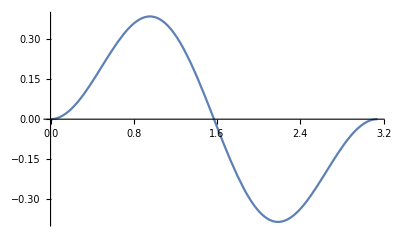

```mathematica
Plot[%,{u,0,π}]
```

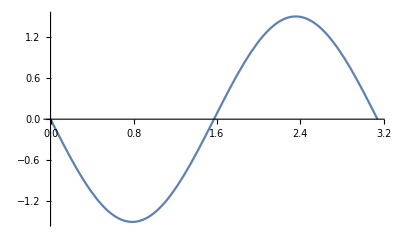

```mathematica
Plot[LegendreP[2,1,Cos[u]],{u,0,π}]
```

```mathematica
ueqa2=ueqa[[3;;4]];
ueqa2//TableForm
```

fr22[r] ((a l (1+l)-2 (a-c) Csc[u]^2) fu22[u]+a (Cot[u] fu22'[u]+fu22''[u]))+fr33[r] ((b l (1+l)-2 (b-d) Csc[u]^2) fu33[u]+b (Cot[u] fu33'[u]+fu33''[u]))
fr22[r] (fu22[u] (2 (a-c)+c l (1+l) Sin[u]^2)+c Sin[u] (Cos[u] fu22'[u]+Sin[u] fu22''[u]))+fr33[r] (fu33[u] (2 (b-d)+d l (1+l) Sin[u]^2)+d Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
ueqa3=ueqa2/.{fr22[r]->1,fr33[r]->-k}//Simplify
```

{(a l (1+l)-2 (a-c) Csc[u]^2) fu22[u]+a (Cot[u] fu22'[u]+fu22''[u])-k ((b l (1+l)-2 (b-d) Csc[u]^2) fu33[u]+b (Cot[u] fu33'[u]+fu33''[u])),fu22[u] (2 (a-c)+c l (1+l) Sin[u]^2)+c Sin[u] (Cos[u] fu22'[u]+Sin[u] fu22''[u])-k (fu33[u] (2 (b-d)+d l (1+l) Sin[u]^2)+d Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))}

```mathematica
ueqa3/.{a->1,c->1,b->1,d->1}//TableForm
```

l (1+l) fu22[u]+Cot[u] fu22'[u]+fu22''[u]-k (l (1+l) fu33[u]+Cot[u] fu33'[u]+fu33''[u])
l (1+l) fu22[u] Sin[u]^2+Sin[u] (Cos[u] fu22'[u]+Sin[u] fu22''[u])-k (l (1+l) fu33[u] Sin[u]^2+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
ueqa4={ueqa3[[1]],ueqa3[[2]]/Sin[u]^2}/.{a->1,c->1,b->1,d->1}//ExpandAll//Simplify
```

{l (1+l) fu22[u]-k l (1+l) fu33[u]+Cot[u] fu22'[u]-k Cot[u] fu33'[u]+fu22''[u]-k fu33''[u],l (1+l) fu22[u]-k l (1+l) fu33[u]+Cot[u] fu22'[u]-k Cot[u] fu33'[u]+fu22''[u]-k fu33''[u]}

```mathematica
%//TableForm
```

l (1+l) fu22[u]-k l (1+l) fu33[u]+Cot[u] fu22'[u]-k Cot[u] fu33'[u]+fu22''[u]-k fu33''[u]
l (1+l) fu22[u]-k l (1+l) fu33[u]+Cot[u] fu22'[u]-k Cot[u] fu33'[u]+fu22''[u]-k fu33''[u]

```mathematica
eqtmp=ueqa4[[1]]-ueqa4[[2]]//ExpandAll//Simplify
```

0

```mathematica
DSolve[eqtmp==0,fu33[u],u]
```

{{fu33[u]→C[1] LegendreP[l,2,Cos[u]]+C[2] LegendreQ[l,2,Cos[u]]}}

```mathematica
ueqa5=ueqa4/.{fu33->(LegendreP[l,2,Cos[#]]&)}/.l->8//Simplify//ExpandAll//Simplify
```

{72 fu22[u]+1/128 (-315 k (210+385 Cos[2 u]+286 Cos[4 u]+143 Cos[6 u])+128 Cot[u] fu22'[u]+128 fu22''[u]),72 fu22[u]+1/128 (-315 k (210+385 Cos[2 u]+286 Cos[4 u]+143 Cos[6 u])+128 Cot[u] fu22'[u]+128 fu22''[u])}

```mathematica
ueqa5=ueqa4/.{fu33->(LegendreP[l,2,Cos[#]]&)}//Simplify//ExpandAll//Simplify
```

{-1/2 Csc[u]^2 (2 k LegendreP[l,2,Cos[u]]+4 k l LegendreP[l,2,Cos[u]]+2 k l^2 LegendreP[l,2,Cos[u]]+6 k Cos[u] LegendreP[1+l,2,Cos[u]]-2 k l Cos[u] LegendreP[1+l,2,Cos[u]]-4 k l^2 Cos[u] LegendreP[1+l,2,Cos[u]]-2 k l LegendreP[2+l,2,Cos[u]]+2 k l^2 LegendreP[2+l,2,Cos[u]]-2 l (1+l) fu22[u] Sin[u]^2-Sin[2 u] fu22'[u]-fu22''[u]+Cos[2 u] fu22''[u]),-1/2 Csc[u]^2 (2 k LegendreP[l,2,Cos[u]]+4 k l LegendreP[l,2,Cos[u]]+2 k l^2 LegendreP[l,2,Cos[u]]+6 k Cos[u] LegendreP[1+l,2,Cos[u]]-2 k l Cos[u] LegendreP[1+l,2,Cos[u]]-4 k l^2 Cos[u] LegendreP[1+l,2,Cos[u]]-2 k l LegendreP[2+l,2,Cos[u]]+2 k l^2 LegendreP[2+l,2,Cos[u]]-2 l (1+l) fu22[u] Sin[u]^2-Sin[2 u] fu22'[u]-fu22''[u]+Cos[2 u] fu22''[u])}

```mathematica
LegendreP[3,Cos[u]]//FunctionExpand
```

1/2 (-3 Cos[u]+5 Cos[u]^3)

```mathematica
specsol={2k,10 k Cos[u]^3,5/2 k Cos[u]^2 (1+7 Cos[2 u]),7/2 k Cos[u]^3 (-1+9 Cos[2 u]),21/32 k Cos[u]^2 (19+12 Cos[2 u]+33 Cos[4 u]),9/32 k Cos[u]^3 (93-44 Cos[2 u]+143 Cos[4 u]),9/256 k Cos[u]^2 (178+869 Cos[2 u]+286 Cos[4 u]+715 Cos[6 u])}
```

{2 k,10 k Cos[u]^3,5/2 k Cos[u]^2 (1+7 Cos[2 u]),7/2 k Cos[u]^3 (-1+9 Cos[2 u]),21/32 k Cos[u]^2 (19+12 Cos[2 u]+33 Cos[4 u]),9/32 k Cos[u]^3 (93-44 Cos[2 u]+143 Cos[4 u]),9/256 k Cos[u]^2 (178+869 Cos[2 u]+286 Cos[4 u]+715 Cos[6 u])}

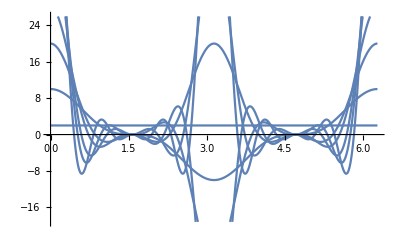

```mathematica
Plot[specsol/k,{u,0,2π}]
```

```mathematica
a/2 ueqa4[[2]]/.fu22''[u]->1/a(-6 b k-6 d k-(-a-2 c+3 a Cos[2 u]) Csc[u]^2 fu22[u]+a Cot[u] fu22'[u])/.a->1/.c->1//ExpandAll//Simplify
```

Sin[u] (-6 (b+d) k Sin[u]+6 fu22[u] Sin[u]+Cos[u] fu22'[u])

```mathematica
Out[322]/Sin[u]/.fu22->(LegendreP[2,Cos[u]]&)//Simplify
```

3 (-1-2 (b+d) k+3 Cos[u]^2) Sin[u]

```mathematica
SolveAlways[Out[319]==0,{k, Cos[2 u], fu22[u],Sin[u] , Cos[u]}]
```

{{a→0,c→0},{a→0,c→0},{c→0,a→0}}

```mathematica
ueqa4[[1]]-ueqa4[[2]]//ExpandAll//Simplify
```

-6 b k-6 d k+(a-c+3 c Cos[2 u]-3 a Cot[u]^2+a Csc[u]^2+2 c Csc[u]^2) fu22[u]+6 b k Sin[u]^2+6 d k Sin[u]^2+(a Cot[u]-c Cos[u] Sin[u]) fu22'[u]+a fu22''[u]-c Sin[u]^2 fu22''[u]

```mathematica
DSolve[-6 b k-6 d k-(-a-2 c+3 a Cos[2 u]) Csc[u]^2 fu22[u]+a Cot[u] fu22'[u]+a fu22''[u]==0,fu22[u],u]
```

```mathematica
DSolve[(2 a+c-3 c Cos[2 u]) fu22[u]+Sin[u] (c Cos[u] fu22'[u]+Sin[u] (-6 (b+d) k+c fu22''[u]))==0,fu22[u],u]
```

{{fu22[u]→C[1] LegendreP[2,√2 √(-(a-c)/c),Cos[u]]+(∫_1^Cos[u] (-((6 √2 b √(-(a-c)/c) k LegendreQ[2,√2 √(-(a-c)/c),K[1]])/((2 a+7 c) (LegendreP[3,√(2-(2 a)/c),K[1]] LegendreQ[2,√(2-(2 a)/c),K[1]]-LegendreP[2,√(2-(2 a)/c),K[1]] LegendreQ[3,√(2-(2 a)/c),K[1]])))-(6 √2 √(-(a-c)/c) d k LegendreQ[2,√2 √(-(a-c)/c),K[1]])/((2 a+7 c) (LegendreP[3,√(2-(2 a)/c),K[1]] LegendreQ[2,√(2-(2 a)/c),K[1]]-LegendreP[2,√(2-(2 a)/c),K[1]] LegendreQ[3,√(2-(2 a)/c),K[1]]))-(18 (b+d) k LegendreQ[2,√2 √(-(a-c)/c),K[1]])/((2 a+7 c) (LegendreP[3,√(2-(2 a)/c),K[1]] LegendreQ[2,√(2-(2 a)/c),K[1]]-LegendreP[2,√(2-(2 a)/c),K[1]] LegendreQ[3,√(2-(2 a)/c),K[1]])))ⅆK[1]) LegendreP[2,√2 √(-(a-c)/c),Cos[u]]+C[2] LegendreQ[2,√2 √(-(a-c)/c),Cos[u]]+(∫_1^Cos[u] ((6 √2 b √(-(a-c)/c) k LegendreP[2,√2 √(-(a-c)/c),K[2]])/((2 a+7 c) (LegendreP[3,√(2-(2 a)/c),K[2]] LegendreQ[2,√(2-(2 a)/c),K[2]]-LegendreP[2,√(2-(2 a)/c),K[2]] LegendreQ[3,√(2-(2 a)/c),K[2]]))+(6 √2 √(-(a-c)/c) d k LegendreP[2,√2 √(-(a-c)/c),K[2]])/((2 a+7 c) (LegendreP[3,√(2-(2 a)/c),K[2]] LegendreQ[2,√(2-(2 a)/c),K[2]]-LegendreP[2,√(2-(2 a)/c),K[2]] LegendreQ[3,√(2-(2 a)/c),K[2]]))+(18 (b+d) k LegendreP[2,√2 √(-(a-c)/c),K[2]])/((2 a+7 c) (LegendreP[3,√(2-(2 a)/c),K[2]] LegendreQ[2,√(2-(2 a)/c),K[2]]-LegendreP[2,√(2-(2 a)/c),K[2]] LegendreQ[3,√(2-(2 a)/c),K[2]])))ⅆK[2]) LegendreQ[2,√2 √(-(a-c)/c),Cos[u]]}}

```mathematica
Out[301]/.{a->1,b->5,c->4,d->3,k->1}
```

{{fu22[u]→C[1] LegendreP[2,√(3/2),Cos[u]]+(∫_1^Cos[u] (-(24 LegendreQ[2,√(3/2),K[1]])/(5 (LegendreP[3,√(3/2),K[1]] LegendreQ[2,√(3/2),K[1]]-LegendreP[2,√(3/2),K[1]] LegendreQ[3,√(3/2),K[1]]))-(4 √6 LegendreQ[2,√(3/2),K[1]])/(5 (LegendreP[3,√(3/2),K[1]] LegendreQ[2,√(3/2),K[1]]-LegendreP[2,√(3/2),K[1]] LegendreQ[3,√(3/2),K[1]])))ⅆK[1]) LegendreP[2,√(3/2),Cos[u]]+C[2] LegendreQ[2,√(3/2),Cos[u]]+(∫_1^Cos[u] ((24 LegendreP[2,√(3/2),K[2]])/(5 (LegendreP[3,√(3/2),K[2]] LegendreQ[2,√(3/2),K[2]]-LegendreP[2,√(3/2),K[2]] LegendreQ[3,√(3/2),K[2]]))+(4 √6 LegendreP[2,√(3/2),K[2]])/(5 (LegendreP[3,√(3/2),K[2]] LegendreQ[2,√(3/2),K[2]]-LegendreP[2,√(3/2),K[2]] LegendreQ[3,√(3/2),K[2]])))ⅆK[2]) LegendreQ[2,√(3/2),Cos[u]]}}

```mathematica
%//N
```

NIntegrate::nlim: K[1] = Cos[u] is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{{fu22[u]→(3.24307 C[1] (1-Cos[u])^1.38763 (1+Cos[u])^0.612372 (0.166667-1.22474 Cos[u]+1. Cos[u]^2))/(-1.+1. Cos[u])^2+C[2] LegendreQ[2.,1.22474,Cos[u]]+1/(-1.+1. Cos[u])^2 3.24307 (1-Cos[u])^1.38763 (1+Cos[u])^0.612372 (0.166667-1.22474 Cos[u]+1. Cos[u]^2) NIntegrate[-(4 (6+√6) k LegendreQ[2,√(3/2),K[1]])/(5 LegendreP[3,√(3/2),K[1]] LegendreQ[2,√(3/2),K[1]]-5 LegendreP[2,√(3/2),K[1]] LegendreQ[3,√(3/2),K[1]]),{K[1],1,Cos[u]}]+LegendreQ[2.,1.22474,Cos[u]] NIntegrate[(4 (6+√6) k LegendreP[2,√(3/2),K[2]])/(5 LegendreP[3,√(3/2),K[2]] LegendreQ[2,√(3/2),K[2]]-5 LegendreP[2,√(3/2),K[2]] LegendreQ[3,√(3/2),K[2]]),{K[2],1,Cos[u]}]}}

```mathematica
%//Simplify
```

{{fu22[u]→C[1] LegendreP[2,√(3/2),Cos[u]]+(∫_1^Cos[u] -(4 (6+√6) k LegendreQ[2,√(3/2),K[1]])/(5 LegendreP[3,√(3/2),K[1]] LegendreQ[2,√(3/2),K[1]]-5 LegendreP[2,√(3/2),K[1]] LegendreQ[3,√(3/2),K[1]])ⅆK[1]) LegendreP[2,√(3/2),Cos[u]]+C[2] LegendreQ[2,√(3/2),Cos[u]]+(∫_1^Cos[u] (4 (6+√6) k LegendreP[2,√(3/2),K[2]])/(5 LegendreP[3,√(3/2),K[2]] LegendreQ[2,√(3/2),K[2]]-5 LegendreP[2,√(3/2),K[2]] LegendreQ[3,√(3/2),K[2]])ⅆK[2]) LegendreQ[2,√(3/2),Cos[u]]}}

```mathematica
%//Simplify
```

{{fu22[u]→C[1] LegendreP[2,√(2-(2 c)/a),Cos[u]]+(∫_1^Cos[u] -((6 (3+√(2-(2 c)/a)) (b+d) k LegendreQ[2,√(2-(2 c)/a),K[1]])/((7 a+2 c) (LegendreP[3,√(2-(2 c)/a),K[1]] LegendreQ[2,√(2-(2 c)/a),K[1]]-LegendreP[2,√(2-(2 c)/a),K[1]] LegendreQ[3,√(2-(2 c)/a),K[1]])))ⅆK[1]) LegendreP[2,√(2-(2 c)/a),Cos[u]]+C[2] LegendreQ[2,√(2-(2 c)/a),Cos[u]]+(∫_1^Cos[u] ((6 (3+√(2-(2 c)/a)) (b+d) k LegendreP[2,√(2-(2 c)/a),K[2]])/((7 a+2 c) (LegendreP[3,√(2-(2 c)/a),K[2]] LegendreQ[2,√(2-(2 c)/a),K[2]]-LegendreP[2,√(2-(2 c)/a),K[2]] LegendreQ[3,√(2-(2 c)/a),K[2]])))ⅆK[2]) LegendreQ[2,√(2-(2 c)/a),Cos[u]]}}

```mathematica
symht1=symh/.{fu11->(LegendreP[l,Cos[#]]&),fu12->(LegendreP[l,1,Cos[#]]&),fu22->(LegendreP[l,Cos[#]]&),fu33->(LegendreP[l,2,Cos[#]]-2fr22[r]/fr33[r]&)}/.{a->1,b->1,c->1,d->1}
```

{{(fr11[r] LegendreP[l,Cos[u]])/r,fr12[r] LegendreP[l,1,Cos[u]],0},{fr12[r] LegendreP[l,1,Cos[u]],r (fr22[r] LegendreP[l,Cos[u]]+fr33[r] (-(2 fr22[r])/fr33[r]+LegendreP[l,2,Cos[u]])),0},{0,0,r (fr22[r] LegendreP[l,Cos[u]]+fr33[r] (-(2 fr22[r])/fr33[r]+LegendreP[l,2,Cos[u]])) Sin[u]^2}}

```mathematica
symht1tr=Sum[hh[i,j]symht1[[i,j]],{i,3},{j,3}]//Simplify
```

-(2 fr22[r] (-2+LegendreP[l,Cos[u]])+fr11[r] LegendreP[l,Cos[u]]+2 fr33[r] LegendreP[l,2,Cos[u]])/r

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symht1]-ω^2 Array[Val[tm[##]]&,{3,3}]symht1tr+ω^2 symht1)/.l->2//FunctionExpand//ExpandAll//PowerExpand//Simplify//PowerExpand//Simplify
```

{{-1/(2 r^3)((1+3 Cos[2 u]) fr11[r]-6 (1+3 Cos[2 u]) fr12[r]+3 fr22[r]-7 r^2 ω^2 fr22[r]+9 Cos[2 u] fr22[r]+3 r^2 ω^2 Cos[2 u] fr22[r]-6 fr33[r]+6 r^2 ω^2 fr33[r]-18 Cos[2 u] fr33[r]-6 r^2 ω^2 Cos[2 u] fr33[r]+7 r fr22'[r]-3 r Cos[2 u] fr22'[r]-6 r fr33'[r]+6 r Cos[2 u] fr33'[r]),-(3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]-2 fr33[r]-r fr22'[r]+2 r fr33'[r]))/r^2,0},{-(3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]-2 fr33[r]-r fr22'[r]+2 r fr33'[r]))/r^2,1/(4 r)(-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (-7+3 Cos[2 u]) fr22[r]-2 (6 r ω^2 fr33[r] Sin[u]^2+(-1+3 Cos[u]^2) fr11'[r]-12 Cos[u]^2 fr12'[r]+5 r fr22''[r]-3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))),0},{0,0,-1/(4 r)Sin[u]^2 ((-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]+r (r ω^2 (-7+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]+7 r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]))}}

```mathematica
geq2={2 r^3 geq[[1,1]],r^2 geq[[1,2]],geq[[2,2]]4r,4r/Sin[u]^2 geq[[3,3]]};
```

```mathematica
geq2//TableForm
```

-(1+3 Cos[2 u]) fr11[r]+6 (1+3 Cos[2 u]) fr12[r]-3 fr22[r]+7 r^2 ω^2 fr22[r]-9 Cos[2 u] fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]+6 fr33[r]-6 r^2 ω^2 fr33[r]+18 Cos[2 u] fr33[r]+6 r^2 ω^2 Cos[2 u] fr33[r]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r]
-3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]-2 fr33[r]-r fr22'[r]+2 r fr33'[r])
-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (-7+3 Cos[2 u]) fr22[r]-2 (6 r ω^2 fr33[r] Sin[u]^2+(-1+3 Cos[u]^2) fr11'[r]-12 Cos[u]^2 fr12'[r]+5 r fr22''[r]-3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))
-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (-7+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]+7 r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r])

```mathematica
geq2d=D[geq2[[1;;2]],r]//Simplify;
```

```mathematica
geq2d//TableForm
```

-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2-fr11'[r]-3 Cos[2 u] fr11'[r]+6 fr12'[r]+18 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r]+6 r fr33''[r]-6 r Cos[2 u] fr33''[r]
-3 Cos[u] Sin[u] (2 r ω^2 fr12[r]+fr11'[r]+(-2+r^2 ω^2) fr12'[r]-r fr22''[r]+2 r fr33''[r])

```mathematica
Solve[Join[geq2,geq2d]==0//Thread,{fr11''[r],fr12''[r],fr22''[r],fr33''[r]}]
```

{}

```mathematica
Solve[Join[geq2,geq2d]==0//Thread,{fr11[r]}]
```

{}

```mathematica
alleq=Join[geq2,geq2d]
```

{-(1+3 Cos[2 u]) fr11[r]+6 (1+3 Cos[2 u]) fr12[r]-3 fr22[r]+7 r^2 ω^2 fr22[r]-9 Cos[2 u] fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]+6 fr33[r]-6 r^2 ω^2 fr33[r]+18 Cos[2 u] fr33[r]+6 r^2 ω^2 Cos[2 u] fr33[r]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r],-3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]-2 fr33[r]-r fr22'[r]+2 r fr33'[r]),-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (-7+3 Cos[2 u]) fr22[r]-2 (6 r ω^2 fr33[r] Sin[u]^2+(-1+3 Cos[u]^2) fr11'[r]-12 Cos[u]^2 fr12'[r]+5 r fr22''[r]-3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r])),-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (-7+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]+7 r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]),-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2-fr11'[r]-3 Cos[2 u] fr11'[r]+6 fr12'[r]+18 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r]+6 r fr33''[r]-6 r Cos[2 u] fr33''[r],-3 Cos[u] Sin[u] (2 r ω^2 fr12[r]+fr11'[r]+(-2+r^2 ω^2) fr12'[r]-r fr22''[r]+2 r fr33''[r])}

```mathematica
Solve[alleq[[3]]==0,fr33''[r]]
```

{{fr33''[r]→1/(12 r^2 (-1+Cos[u]^2))(-5 fr11[r]-r^2 ω^2 fr11[r]-3 Cos[2 u] fr11[r]-3 r^2 ω^2 Cos[2 u] fr11[r]+7 r^2 ω^2 fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]-12 r^2 ω^2 fr33[r] Sin[u]^2+2 r fr11'[r]-6 r Cos[u]^2 fr11'[r]+24 r Cos[u]^2 fr12'[r]-10 r^2 fr22''[r]+6 r^2 Cos[u]^2 fr22''[r])}}

```mathematica
Solve[alleq[[4]]==0,fr33''[r]]
```

{{fr33''[r]→1/(6 r^2 (-1+Cos[2 u]))(fr11[r]-r^2 ω^2 fr11[r]-9 Cos[2 u] fr11[r]-3 r^2 ω^2 Cos[2 u] fr11[r]+7 r^2 ω^2 fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]-12 r^2 ω^2 fr33[r] Sin[u]^2-r fr11'[r]-3 r Cos[2 u] fr11'[r]+24 r Cos[2 u] fr12'[r]-7 r^2 fr22''[r]+3 r^2 Cos[2 u] fr22''[r])}}

```mathematica
(-5 fr11[r]-r^2 ω^2 fr11[r]-3 Cos[2 u] fr11[r]-3 r^2 ω^2 Cos[2 u] fr11[r]+7 r^2 ω^2 fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]-12 r^2 ω^2 fr33[r] Sin[u]^2+2 r fr11'[r]-6 r Cos[u]^2 fr11'[r]+24 r Cos[u]^2 fr12'[r]-10 r^2 fr22''[r]+6 r^2 Cos[u]^2 fr22''[r])==(fr11[r]-r^2 ω^2 fr11[r]-9 Cos[2 u] fr11[r]-3 r^2 ω^2 Cos[2 u] fr11[r]+7 r^2 ω^2 fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]-12 r^2 ω^2 fr33[r] Sin[u]^2-r fr11'[r]-3 r Cos[2 u] fr11'[r]+24 r Cos[2 u] fr12'[r]-7 r^2 fr22''[r]+3 r^2 Cos[2 u] fr22''[r])//ExpandAll//Simplify
```

fr11[r] Sin[u]==2 r Sin[u] fr12'[r]

```mathematica
seq=fr11[r]-2r fr12'[r]
```

fr11[r]-2 r fr12'[r]

```mathematica
AppendTo[alleq,seq];
AppendTo[alleq,D[seq,r]]
```

{-(1+3 Cos[2 u]) fr11[r]+6 (1+3 Cos[2 u]) fr12[r]-3 fr22[r]+7 r^2 ω^2 fr22[r]-9 Cos[2 u] fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]+6 fr33[r]-6 r^2 ω^2 fr33[r]+18 Cos[2 u] fr33[r]+6 r^2 ω^2 Cos[2 u] fr33[r]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r],-3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]-2 fr33[r]-r fr22'[r]+2 r fr33'[r]),-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (-7+3 Cos[2 u]) fr22[r]-2 (6 r ω^2 fr33[r] Sin[u]^2+(-1+3 Cos[u]^2) fr11'[r]-12 Cos[u]^2 fr12'[r]+5 r fr22''[r]-3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r])),-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (-7+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]+7 r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]),-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2-fr11'[r]-3 Cos[2 u] fr11'[r]+6 fr12'[r]+18 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r]+6 r fr33''[r]-6 r Cos[2 u] fr33''[r],-3 Cos[u] Sin[u] (2 r ω^2 fr12[r]+fr11'[r]+(-2+r^2 ω^2) fr12'[r]-r fr22''[r]+2 r fr33''[r]),fr11[r]-2 r fr12'[r],fr11[r]-2 r fr12'[r],fr11'[r]-2 fr12'[r]-2 r fr12''[r]}

```mathematica
alleq2=alleq/.{fr11[r]->2r fr12'[r],fr11'[r]->D[2r fr12'[r],r]}//ExpandAll//Simplify
```

{6 (1+3 Cos[2 u]) fr12[r]-(3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr22[r]+6 fr33[r]-6 r^2 ω^2 fr33[r]+18 Cos[2 u] fr33[r]+6 r^2 ω^2 Cos[2 u] fr33[r]-2 r fr12'[r]-6 r Cos[2 u] fr12'[r]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r],-3 Cos[u] Sin[u] ((-2+r^2 ω^2) fr12[r]+fr22[r]-2 fr33[r]+2 r fr12'[r]-r fr22'[r]+2 r fr33'[r]),-r^2 (ω^2 (-7+3 Cos[2 u]) fr22[r]+12 ω^2 fr33[r] Sin[u]^2+2 r ω^2 fr12'[r]+6 r ω^2 Cos[2 u] fr12'[r]+2 fr12''[r]+6 Cos[2 u] fr12''[r]+7 fr22''[r]-3 Cos[2 u] fr22''[r]-6 fr33''[r]+6 Cos[2 u] fr33''[r]),-r^2 (ω^2 (-7+3 Cos[2 u]) fr22[r]+12 ω^2 fr33[r] Sin[u]^2+2 r ω^2 fr12'[r]+6 r ω^2 Cos[2 u] fr12'[r]+2 fr12''[r]+6 Cos[2 u] fr12''[r]+7 fr22''[r]-3 Cos[2 u] fr22''[r]-6 fr33''[r]+6 Cos[2 u] fr33''[r]),-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2+4 fr12'[r]+12 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-2 r fr12''[r]-6 r Cos[2 u] fr12''[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r]+6 r fr33''[r]-6 r Cos[2 u] fr33''[r],-3 r Cos[u] Sin[u] (2 ω^2 fr12[r]+r ω^2 fr12'[r]+2 fr12''[r]-fr22''[r]+2 fr33''[r]),0,0,0}

```mathematica
%//TableForm
```

6 (1+3 Cos[2 u]) fr12[r]-(3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr22[r]+6 fr33[r]-6 r^2 ω^2 fr33[r]+18 Cos[2 u] fr33[r]+6 r^2 ω^2 Cos[2 u] fr33[r]-2 r fr12'[r]-6 r Cos[2 u] fr12'[r]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r]
-3 Cos[u] Sin[u] ((-2+r^2 ω^2) fr12[r]+fr22[r]-2 fr33[r]+2 r fr12'[r]-r fr22'[r]+2 r fr33'[r])
-r^2 (ω^2 (-7+3 Cos[2 u]) fr22[r]+12 ω^2 fr33[r] Sin[u]^2+2 r ω^2 fr12'[r]+6 r ω^2 Cos[2 u] fr12'[r]+2 fr12''[r]+6 Cos[2 u] fr12''[r]+7 fr22''[r]-3 Cos[2 u] fr22''[r]-6 fr33''[r]+6 Cos[2 u] fr33''[r])
-r^2 (ω^2 (-7+3 Cos[2 u]) fr22[r]+12 ω^2 fr33[r] Sin[u]^2+2 r ω^2 fr12'[r]+6 r ω^2 Cos[2 u] fr12'[r]+2 fr12''[r]+6 Cos[2 u] fr12''[r]+7 fr22''[r]-3 Cos[2 u] fr22''[r]-6 fr33''[r]+6 Cos[2 u] fr33''[r])
-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2+4 fr12'[r]+12 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-2 r fr12''[r]-6 r Cos[2 u] fr12''[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r]+6 r fr33''[r]-6 r Cos[2 u] fr33''[r]
-3 r Cos[u] Sin[u] (2 ω^2 fr12[r]+r ω^2 fr12'[r]+2 fr12''[r]-fr22''[r]+2 fr33''[r])
0
0
0

```mathematica
Solve[alleq2[[1]]==0,fr12[r]]
```

{{fr12[r]→1/(6 (1+3 Cos[2 u]))(3 fr22[r]-7 r^2 ω^2 fr22[r]+9 Cos[2 u] fr22[r]+3 r^2 ω^2 Cos[2 u] fr22[r]-6 fr33[r]+6 r^2 ω^2 fr33[r]-18 Cos[2 u] fr33[r]-6 r^2 ω^2 Cos[2 u] fr33[r]+2 r fr12'[r]+6 r Cos[2 u] fr12'[r]+7 r fr22'[r]-3 r Cos[2 u] fr22'[r]-6 r fr33'[r]+6 r Cos[2 u] fr33'[r])}}

```mathematica
Solve[alleq2[[1]]==0,fr12'[r]]
```

{{fr12'[r]→1/(2 r (1+3 Cos[2 u]))(6 fr12[r]+18 Cos[2 u] fr12[r]-3 fr22[r]+7 r^2 ω^2 fr22[r]-9 Cos[2 u] fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]+6 fr33[r]-6 r^2 ω^2 fr33[r]+18 Cos[2 u] fr33[r]+6 r^2 ω^2 Cos[2 u] fr33[r]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r])}}

```mathematica
Solve[alleq2[[3]]==0,fr12'[r]]
```

{{fr12'[r]→1/(2 r ω^2 (1+3 Cos[2 u]))(7 ω^2 fr22[r]-3 ω^2 Cos[2 u] fr22[r]-12 ω^2 fr33[r] Sin[u]^2-2 fr12''[r]-6 Cos[2 u] fr12''[r]-7 fr22''[r]+3 Cos[2 u] fr22''[r]+6 fr33''[r]-6 Cos[2 u] fr33''[r])}}

```mathematica
1/(2 r (1+3 Cos[2 u]))(6 fr12[r]+18 Cos[2 u] fr12[r]-3 fr22[r]+7 r^2 ω^2 fr22[r]-9 Cos[2 u] fr22[r]-3 r^2 ω^2 Cos[2 u] fr22[r]+6 fr33[r]-6 r^2 ω^2 fr33[r]+18 Cos[2 u] fr33[r]+6 r^2 ω^2 Cos[2 u] fr33[r]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r])==1/(2 r ω^2 (1+3 Cos[2 u]))(7 ω^2 fr22[r]-3 ω^2 Cos[2 u] fr22[r]-12 ω^2 fr33[r] Sin[u]^2-2 fr12''[r]-6 Cos[2 u] fr12''[r]-7 fr22''[r]+3 Cos[2 u] fr22''[r]+6 fr33''[r]-6 Cos[2 u] fr33''[r])//Simplify
```

1/(r ω (1+3 Cos[2 u]))(6 ω^2 (1+3 Cos[2 u]) fr12[r]-ω^2 (10-7 r^2 ω^2+3 (2+r^2 ω^2) Cos[2 u]) fr22[r]+12 ω^2 fr33[r]-6 r^2 ω^4 fr33[r]+12 ω^2 Cos[2 u] fr33[r]+6 r^2 ω^4 Cos[2 u] fr33[r]-7 r ω^2 fr22'[r]+3 r ω^2 Cos[2 u] fr22'[r]+6 r ω^2 fr33'[r]-6 r ω^2 Cos[2 u] fr33'[r]+2 fr12''[r]+6 Cos[2 u] fr12''[r]+7 fr22''[r]-3 Cos[2 u] fr22''[r]-6 fr33''[r]+6 Cos[2 u] fr33''[r])==0

```mathematica
Solve[(alleq2[[1;;3]]~Join~alleq2[[5;;6]])==0//Thread,{fr12''[r],fr22''[r],fr33''[r],fr12'[r],fr22'[r]}]
```

{}

```mathematica
Solve[alleq2[[3]]==0,fr33''[r]]
```

{{fr33''[r]→1/(6 (-1+Cos[2 u]))(7 ω^2 fr22[r]-3 ω^2 Cos[2 u] fr22[r]-12 ω^2 fr33[r] Sin[u]^2-2 r ω^2 fr12'[r]-6 r ω^2 Cos[2 u] fr12'[r]-2 fr12''[r]-6 Cos[2 u] fr12''[r]-7 fr22''[r]+3 Cos[2 u] fr22''[r])}}

```mathematica
Solve[alleq2[[5]]==0,fr33''[r]]
```

{{fr33''[r]→1/(6 r (-1+Cos[2 u]))(14 r ω^2 fr22[r]-6 r ω^2 Cos[2 u] fr22[r]-24 r ω^2 fr33[r] Sin[u]^2+4 fr12'[r]+12 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-2 r fr12''[r]-6 r Cos[2 u] fr12''[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r])}}

```mathematica
1/(6 (-1+Cos[2 u]))(7 ω^2 fr22[r]-3 ω^2 Cos[2 u] fr22[r]-12 ω^2 fr33[r] Sin[u]^2-2 r ω^2 fr12'[r]-6 r ω^2 Cos[2 u] fr12'[r]-2 fr12''[r]-6 Cos[2 u] fr12''[r]-7 fr22''[r]+3 Cos[2 u] fr22''[r])==1/(6 r (-1+Cos[2 u]))(14 r ω^2 fr22[r]-6 r ω^2 Cos[2 u] fr22[r]-24 r ω^2 fr33[r] Sin[u]^2+4 fr12'[r]+12 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-2 r fr12''[r]-6 r Cos[2 u] fr12''[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r])//ExpandAll//Simplify
```

1/r Csc[u]^2 (-r ω^2 (-7+3 Cos[2 u]) fr22[r]-12 r ω^2 fr33[r] Sin[u]^2+4 fr12'[r]+2 r^2 ω^2 fr12'[r]+12 Cos[2 u] fr12'[r]+6 r^2 ω^2 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r])==0

```mathematica
D[-r ω^2 (-7+3 Cos[2 u]) fr22[r]-12 r ω^2 fr33[r] Sin[u]^2+4 fr12'[r]+2 r^2 ω^2 fr12'[r]+12 Cos[2 u] fr12'[r]+6 r^2 ω^2 Cos[2 u] fr12'[r]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r],r]//Simplify
```

-ω^2 (-7+3 Cos[2 u]) fr22[r]-12 ω^2 fr33[r] Sin[u]^2+4 r ω^2 fr12'[r]+12 r ω^2 Cos[2 u] fr12'[r]+21 r ω^2 fr22'[r]-9 r ω^2 Cos[2 u] fr22'[r]-18 r ω^2 fr33'[r]+18 r ω^2 Cos[2 u] fr33'[r]+4 fr12''[r]+2 r^2 ω^2 fr12''[r]+12 Cos[2 u] fr12''[r]+6 r^2 ω^2 Cos[2 u] fr12''[r]-10 fr22''[r]+7 r^2 ω^2 fr22''[r]-6 Cos[2 u] fr22''[r]-3 r^2 ω^2 Cos[2 u] fr22''[r]+12 fr33''[r]-6 r^2 ω^2 fr33''[r]+12 Cos[2 u] fr33''[r]+6 r^2 ω^2 Cos[2 u] fr33''[r]

```mathematica
Solve[alleq2[[3]]==0,fr22''[r]]
```

{{fr22''[r]→1/(-7+3 Cos[2 u])(-7 ω^2 fr22[r]+3 ω^2 Cos[2 u] fr22[r]+12 ω^2 fr33[r] Sin[u]^2+2 r ω^2 fr12'[r]+6 r ω^2 Cos[2 u] fr12'[r]+2 fr12''[r]+6 Cos[2 u] fr12''[r]-6 fr33''[r]+6 Cos[2 u] fr33''[r])}}

```mathematica
Solve[alleq2[[5]]==0,fr22''[r]]
```

{{fr22''[r]→1/(r (-7+3 Cos[2 u]))(-14 r ω^2 fr22[r]+6 r ω^2 Cos[2 u] fr22[r]+24 r ω^2 fr33[r] Sin[u]^2-4 fr12'[r]-12 Cos[2 u] fr12'[r]+10 fr22'[r]-7 r^2 ω^2 fr22'[r]+6 Cos[2 u] fr22'[r]+3 r^2 ω^2 Cos[2 u] fr22'[r]-12 fr33'[r]+6 r^2 ω^2 fr33'[r]-12 Cos[2 u] fr33'[r]-6 r^2 ω^2 Cos[2 u] fr33'[r]+2 r fr12''[r]+6 r Cos[2 u] fr12''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r])}}

```mathematica
f12s=Re[sln[f[12]]]/.l->2//FunctionExpand//Simplify//ComplexExpand//Simplify
```

(4 (r ω (-6+r^2 ω^2) Cos[r ω]-3 (-2+r^2 ω^2) Sin[r ω]))/(r^4 ω^3)

```mathematica
alleq2/.fr12->(f12s/.r->#&)//ExpandAll//Simplify
```

{(56 Cos[r ω])/r-(336 Cos[r ω])/(r^3 ω^2)+(168 Cos[2 u] Cos[r ω])/r-(1008 Cos[2 u] Cos[r ω])/(r^3 ω^2)-(3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr22[r]+6 (1-r^2 ω^2+(3+r^2 ω^2) Cos[2 u]) fr33[r]+(336 Sin[r ω])/(r^4 ω^3)-(168 Sin[r ω])/(r^2 ω)+8 ω Sin[r ω]+(1008 Cos[2 u] Sin[r ω])/(r^4 ω^3)-(504 Cos[2 u] Sin[r ω])/(r^2 ω)+24 ω Cos[2 u] Sin[r ω]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r],-1/(r^4 ω^3)3 Cos[u] Sin[u] (240 r ω Cos[r ω]-64 r^3 ω^3 Cos[r ω]+4 r^5 ω^5 Cos[r ω]+r^4 ω^3 fr22[r]-2 r^4 ω^3 fr33[r]-240 Sin[r ω]+144 r^2 ω^2 Sin[r ω]-20 r^4 ω^4 Sin[r ω]-r^5 ω^3 fr22'[r]+2 r^5 ω^3 fr33'[r]),-(352 Cos[r ω])/r+(960 Cos[r ω])/(r^3 ω^2)+40 r ω^2 Cos[r ω]-(1056 Cos[2 u] Cos[r ω])/r+(2880 Cos[2 u] Cos[r ω])/(r^3 ω^2)+120 r ω^2 Cos[2 u] Cos[r ω]-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]-12 r^2 ω^2 fr33[r] Sin[u]^2-(960 Sin[r ω])/(r^4 ω^3)+(672 Sin[r ω])/(r^2 ω)-136 ω Sin[r ω]+8 r^2 ω^3 Sin[r ω]-(2880 Cos[2 u] Sin[r ω])/(r^4 ω^3)+(2016 Cos[2 u] Sin[r ω])/(r^2 ω)-408 ω Cos[2 u] Sin[r ω]+24 r^2 ω^3 Cos[2 u] Sin[r ω]-7 r^2 fr22''[r]+3 r^2 Cos[2 u] fr22''[r]+6 r^2 fr33''[r]-6 r^2 Cos[2 u] fr33''[r],-(352 Cos[r ω])/r+(960 Cos[r ω])/(r^3 ω^2)+40 r ω^2 Cos[r ω]-(1056 Cos[2 u] Cos[r ω])/r+(2880 Cos[2 u] Cos[r ω])/(r^3 ω^2)+120 r ω^2 Cos[2 u] Cos[r ω]-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]-12 r^2 ω^2 fr33[r] Sin[u]^2-(960 Sin[r ω])/(r^4 ω^3)+(672 Sin[r ω])/(r^2 ω)-136 ω Sin[r ω]+8 r^2 ω^3 Sin[r ω]-(2880 Cos[2 u] Sin[r ω])/(r^4 ω^3)+(2016 Cos[2 u] Sin[r ω])/(r^2 ω)-408 ω Cos[2 u] Sin[r ω]+24 r^2 ω^3 Cos[2 u] Sin[r ω]-7 r^2 fr22''[r]+3 r^2 Cos[2 u] fr22''[r]+6 r^2 fr33''[r]-6 r^2 Cos[2 u] fr33''[r],-(224 Cos[r ω])/r^2+(1344 Cos[r ω])/(r^4 ω^2)+8 ω^2 Cos[r ω]-(672 Cos[2 u] Cos[r ω])/r^2+(4032 Cos[2 u] Cos[r ω])/(r^4 ω^2)+24 ω^2 Cos[2 u] Cos[r ω]-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2-(1344 Sin[r ω])/(r^5 ω^3)+(672 Sin[r ω])/(r^3 ω)-(56 ω Sin[r ω])/r-(4032 Cos[2 u] Sin[r ω])/(r^5 ω^3)+(2016 Cos[2 u] Sin[r ω])/(r^3 ω)-(168 ω Cos[2 u] Sin[r ω])/r-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r]+6 r fr33''[r]-6 r Cos[2 u] fr33''[r],1/(2 r^5 ω^3)3 Sin[2 u] (4 (4 r ω (60-13 r^2 ω^2+r^4 ω^4) Cos[r ω]+(-240+132 r^2 ω^2-16 r^4 ω^4+r^6 ω^6) Sin[r ω])+r^6 ω^3 fr22''[r]-2 r^6 ω^3 fr33''[r]),0,0,0}

```mathematica
%//TableForm
```

(56 Cos[r ω])/r-(336 Cos[r ω])/(r^3 ω^2)+(168 Cos[2 u] Cos[r ω])/r-(1008 Cos[2 u] Cos[r ω])/(r^3 ω^2)-(3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr22[r]+6 (1-r^2 ω^2+(3+r^2 ω^2) Cos[2 u]) fr33[r]+(336 Sin[r ω])/(r^4 ω^3)-(168 Sin[r ω])/(r^2 ω)+8 ω Sin[r ω]+(1008 Cos[2 u] Sin[r ω])/(r^4 ω^3)-(504 Cos[2 u] Sin[r ω])/(r^2 ω)+24 ω Cos[2 u] Sin[r ω]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r]
-(3 Cos[u] Sin[u] (240 r ω Cos[r ω]-64 r^3 ω^3 Cos[r ω]+4 r^5 ω^5 Cos[r ω]+r^4 ω^3 fr22[r]-2 r^4 ω^3 fr33[r]-240 Sin[r ω]+144 r^2 ω^2 Sin[r ω]-20 r^4 ω^4 Sin[r ω]-r^5 ω^3 fr22'[r]+2 r^5 ω^3 fr33'[r]))/(r^4 ω^3)
-(352 Cos[r ω])/r+(960 Cos[r ω])/(r^3 ω^2)+40 r ω^2 Cos[r ω]-(1056 Cos[2 u] Cos[r ω])/r+(2880 Cos[2 u] Cos[r ω])/(r^3 ω^2)+120 r ω^2 Cos[2 u] Cos[r ω]-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]-12 r^2 ω^2 fr33[r] Sin[u]^2-(960 Sin[r ω])/(r^4 ω^3)+(672 Sin[r ω])/(r^2 ω)-136 ω Sin[r ω]+8 r^2 ω^3 Sin[r ω]-(2880 Cos[2 u] Sin[r ω])/(r^4 ω^3)+(2016 Cos[2 u] Sin[r ω])/(r^2 ω)-408 ω Cos[2 u] Sin[r ω]+24 r^2 ω^3 Cos[2 u] Sin[r ω]-7 r^2 fr22''[r]+3 r^2 Cos[2 u] fr22''[r]+6 r^2 fr33''[r]-6 r^2 Cos[2 u] fr33''[r]
-(352 Cos[r ω])/r+(960 Cos[r ω])/(r^3 ω^2)+40 r ω^2 Cos[r ω]-(1056 Cos[2 u] Cos[r ω])/r+(2880 Cos[2 u] Cos[r ω])/(r^3 ω^2)+120 r ω^2 Cos[2 u] Cos[r ω]-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]-12 r^2 ω^2 fr33[r] Sin[u]^2-(960 Sin[r ω])/(r^4 ω^3)+(672 Sin[r ω])/(r^2 ω)-136 ω Sin[r ω]+8 r^2 ω^3 Sin[r ω]-(2880 Cos[2 u] Sin[r ω])/(r^4 ω^3)+(2016 Cos[2 u] Sin[r ω])/(r^2 ω)-408 ω Cos[2 u] Sin[r ω]+24 r^2 ω^3 Cos[2 u] Sin[r ω]-7 r^2 fr22''[r]+3 r^2 Cos[2 u] fr22''[r]+6 r^2 fr33''[r]-6 r^2 Cos[2 u] fr33''[r]
-(224 Cos[r ω])/r^2+(1344 Cos[r ω])/(r^4 ω^2)+8 ω^2 Cos[r ω]-(672 Cos[2 u] Cos[r ω])/r^2+(4032 Cos[2 u] Cos[r ω])/(r^4 ω^2)+24 ω^2 Cos[2 u] Cos[r ω]-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2-(1344 Sin[r ω])/(r^5 ω^3)+(672 Sin[r ω])/(r^3 ω)-(56 ω Sin[r ω])/r-(4032 Cos[2 u] Sin[r ω])/(r^5 ω^3)+(2016 Cos[2 u] Sin[r ω])/(r^3 ω)-(168 ω Cos[2 u] Sin[r ω])/r-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-7 r fr22''[r]+3 r Cos[2 u] fr22''[r]+6 r fr33''[r]-6 r Cos[2 u] fr33''[r]
(3 Sin[2 u] (4 (4 r ω (60-13 r^2 ω^2+r^4 ω^4) Cos[r ω]+(-240+132 r^2 ω^2-16 r^4 ω^4+r^6 ω^6) Sin[r ω])+r^6 ω^3 fr22''[r]-2 r^6 ω^3 fr33''[r]))/(2 r^5 ω^3)
0
0
0

```mathematica
Solve[3 Sin[2 u] (4 (4 r ω (60-13 r^2 ω^2+r^4 ω^4) Cos[r ω]+(-240+132 r^2 ω^2-16 r^4 ω^4+r^6 ω^6) Sin[r ω])+r^6 ω^3 fr22''[r]-2 r^6 ω^3 fr33''[r])==0,fr22''[r]]
```

{{fr22''[r]→-1/(r^6 ω^3)2 (480 r ω Cos[r ω]-104 r^3 ω^3 Cos[r ω]+8 r^5 ω^5 Cos[r ω]-480 Sin[r ω]+264 r^2 ω^2 Sin[r ω]-32 r^4 ω^4 Sin[r ω]+2 r^6 ω^6 Sin[r ω]-r^6 ω^3 fr33''[r])}}

```mathematica
-1/(r^6 ω^3)2 (480 r ω Cos[r ω]-104 r^3 ω^3 Cos[r ω]+8 r^5 ω^5 Cos[r ω]-480 Sin[r ω]+264 r^2 ω^2 Sin[r ω]-32 r^4 ω^4 Sin[r ω]+2 r^6 ω^6 Sin[r ω]-r^6 ω^3 fr33''[r])
```

```mathematica
Out[536]/.{fr22''[r]->-1/(r^6 ω^3)2 (480 r ω Cos[r ω]-104 r^3 ω^3 Cos[r ω]+8 r^5 ω^5 Cos[r ω]-480 Sin[r ω]+264 r^2 ω^2 Sin[r ω]-32 r^4 ω^4 Sin[r ω]+2 r^6 ω^6 Sin[r ω]-r^6 ω^3 fr33''[r])}//ExpandAll//Simplify
```

{(56 Cos[r ω])/r-(336 Cos[r ω])/(r^3 ω^2)+(168 Cos[2 u] Cos[r ω])/r-(1008 Cos[2 u] Cos[r ω])/(r^3 ω^2)-(3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr22[r]+6 (1-r^2 ω^2+(3+r^2 ω^2) Cos[2 u]) fr33[r]+(336 Sin[r ω])/(r^4 ω^3)-(168 Sin[r ω])/(r^2 ω)+8 ω Sin[r ω]+(1008 Cos[2 u] Sin[r ω])/(r^4 ω^3)-(504 Cos[2 u] Sin[r ω])/(r^2 ω)+24 ω Cos[2 u] Sin[r ω]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r],-1/(r^4 ω^3)3 Cos[u] Sin[u] (240 r ω Cos[r ω]-64 r^3 ω^3 Cos[r ω]+4 r^5 ω^5 Cos[r ω]+r^4 ω^3 fr22[r]-2 r^4 ω^3 fr33[r]-240 Sin[r ω]+144 r^2 ω^2 Sin[r ω]-20 r^4 ω^4 Sin[r ω]-r^5 ω^3 fr22'[r]+2 r^5 ω^3 fr33'[r]),-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]+4 (-(452 Cos[r ω])/r+(1920 Cos[r ω])/(r^3 ω^2)+38 r ω^2 Cos[r ω]-(108 Cos[2 u] Cos[r ω])/r+18 r ω^2 Cos[2 u] Cos[r ω]-3 r^2 ω^2 fr33[r] Sin[u]^2-(1920 Sin[r ω])/(r^4 ω^3)+(1092 Sin[r ω])/(r^2 ω)-146 ω Sin[r ω]+9 r^2 ω^3 Sin[r ω]+(108 Cos[2 u] Sin[r ω])/(r^2 ω)-54 ω Cos[2 u] Sin[r ω]+3 r^2 ω^3 Cos[2 u] Sin[r ω]-2 r^2 fr33''[r]),-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]+4 (-(452 Cos[r ω])/r+(1920 Cos[r ω])/(r^3 ω^2)+38 r ω^2 Cos[r ω]-(108 Cos[2 u] Cos[r ω])/r+18 r ω^2 Cos[2 u] Cos[r ω]-3 r^2 ω^2 fr33[r] Sin[u]^2-(1920 Sin[r ω])/(r^4 ω^3)+(1092 Sin[r ω])/(r^2 ω)-146 ω Sin[r ω]+9 r^2 ω^3 Sin[r ω]+(108 Cos[2 u] Sin[r ω])/(r^2 ω)-54 ω Cos[2 u] Sin[r ω]+3 r^2 ω^3 Cos[2 u] Sin[r ω]-2 r^2 fr33''[r]),-(1680 Cos[r ω])/r^2+(8064 Cos[r ω])/(r^4 ω^2)+120 ω^2 Cos[r ω]-(48 Cos[2 u] Cos[r ω])/r^2+(1152 Cos[2 u] Cos[r ω])/(r^4 ω^2)-24 ω^2 Cos[2 u] Cos[r ω]-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2-(8064 Sin[r ω])/(r^5 ω^3)+(4368 Sin[r ω])/(r^3 ω)-(504 ω Sin[r ω])/r+28 r ω^3 Sin[r ω]-(1152 Cos[2 u] Sin[r ω])/(r^5 ω^3)+(432 Cos[2 u] Sin[r ω])/(r^3 ω)+(24 ω Cos[2 u] Sin[r ω])/r-12 r ω^3 Cos[2 u] Sin[r ω]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-8 r fr33''[r],0,0,0,0}

```mathematica
%//TableForm
```

(56 Cos[r ω])/r-(336 Cos[r ω])/(r^3 ω^2)+(168 Cos[2 u] Cos[r ω])/r-(1008 Cos[2 u] Cos[r ω])/(r^3 ω^2)-(3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr22[r]+6 (1-r^2 ω^2+(3+r^2 ω^2) Cos[2 u]) fr33[r]+(336 Sin[r ω])/(r^4 ω^3)-(168 Sin[r ω])/(r^2 ω)+8 ω Sin[r ω]+(1008 Cos[2 u] Sin[r ω])/(r^4 ω^3)-(504 Cos[2 u] Sin[r ω])/(r^2 ω)+24 ω Cos[2 u] Sin[r ω]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r]
-(3 Cos[u] Sin[u] (240 r ω Cos[r ω]-64 r^3 ω^3 Cos[r ω]+4 r^5 ω^5 Cos[r ω]+r^4 ω^3 fr22[r]-2 r^4 ω^3 fr33[r]-240 Sin[r ω]+144 r^2 ω^2 Sin[r ω]-20 r^4 ω^4 Sin[r ω]-r^5 ω^3 fr22'[r]+2 r^5 ω^3 fr33'[r]))/(r^4 ω^3)
-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]+4 (-(452 Cos[r ω])/r+(1920 Cos[r ω])/(r^3 ω^2)+38 r ω^2 Cos[r ω]-(108 Cos[2 u] Cos[r ω])/r+18 r ω^2 Cos[2 u] Cos[r ω]-3 r^2 ω^2 fr33[r] Sin[u]^2-(1920 Sin[r ω])/(r^4 ω^3)+(1092 Sin[r ω])/(r^2 ω)-146 ω Sin[r ω]+9 r^2 ω^3 Sin[r ω]+(108 Cos[2 u] Sin[r ω])/(r^2 ω)-54 ω Cos[2 u] Sin[r ω]+3 r^2 ω^3 Cos[2 u] Sin[r ω]-2 r^2 fr33''[r])
-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]+4 (-(452 Cos[r ω])/r+(1920 Cos[r ω])/(r^3 ω^2)+38 r ω^2 Cos[r ω]-(108 Cos[2 u] Cos[r ω])/r+18 r ω^2 Cos[2 u] Cos[r ω]-3 r^2 ω^2 fr33[r] Sin[u]^2-(1920 Sin[r ω])/(r^4 ω^3)+(1092 Sin[r ω])/(r^2 ω)-146 ω Sin[r ω]+9 r^2 ω^3 Sin[r ω]+(108 Cos[2 u] Sin[r ω])/(r^2 ω)-54 ω Cos[2 u] Sin[r ω]+3 r^2 ω^3 Cos[2 u] Sin[r ω]-2 r^2 fr33''[r])
-(1680 Cos[r ω])/r^2+(8064 Cos[r ω])/(r^4 ω^2)+120 ω^2 Cos[r ω]-(48 Cos[2 u] Cos[r ω])/r^2+(1152 Cos[2 u] Cos[r ω])/(r^4 ω^2)-24 ω^2 Cos[2 u] Cos[r ω]-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2-(8064 Sin[r ω])/(r^5 ω^3)+(4368 Sin[r ω])/(r^3 ω)-(504 ω Sin[r ω])/r+28 r ω^3 Sin[r ω]-(1152 Cos[2 u] Sin[r ω])/(r^5 ω^3)+(432 Cos[2 u] Sin[r ω])/(r^3 ω)+(24 ω Cos[2 u] Sin[r ω])/r-12 r ω^3 Cos[2 u] Sin[r ω]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-8 r fr33''[r]
0
0
0
0

```mathematica
tmp000=Out[539]
```

{(56 Cos[r ω])/r-(336 Cos[r ω])/(r^3 ω^2)+(168 Cos[2 u] Cos[r ω])/r-(1008 Cos[2 u] Cos[r ω])/(r^3 ω^2)-(3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr22[r]+6 (1-r^2 ω^2+(3+r^2 ω^2) Cos[2 u]) fr33[r]+(336 Sin[r ω])/(r^4 ω^3)-(168 Sin[r ω])/(r^2 ω)+8 ω Sin[r ω]+(1008 Cos[2 u] Sin[r ω])/(r^4 ω^3)-(504 Cos[2 u] Sin[r ω])/(r^2 ω)+24 ω Cos[2 u] Sin[r ω]-7 r fr22'[r]+3 r Cos[2 u] fr22'[r]+6 r fr33'[r]-6 r Cos[2 u] fr33'[r],-1/(r^4 ω^3)3 Cos[u] Sin[u] (240 r ω Cos[r ω]-64 r^3 ω^3 Cos[r ω]+4 r^5 ω^5 Cos[r ω]+r^4 ω^3 fr22[r]-2 r^4 ω^3 fr33[r]-240 Sin[r ω]+144 r^2 ω^2 Sin[r ω]-20 r^4 ω^4 Sin[r ω]-r^5 ω^3 fr22'[r]+2 r^5 ω^3 fr33'[r]),-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]+4 (-(452 Cos[r ω])/r+(1920 Cos[r ω])/(r^3 ω^2)+38 r ω^2 Cos[r ω]-(108 Cos[2 u] Cos[r ω])/r+18 r ω^2 Cos[2 u] Cos[r ω]-3 r^2 ω^2 fr33[r] Sin[u]^2-(1920 Sin[r ω])/(r^4 ω^3)+(1092 Sin[r ω])/(r^2 ω)-146 ω Sin[r ω]+9 r^2 ω^3 Sin[r ω]+(108 Cos[2 u] Sin[r ω])/(r^2 ω)-54 ω Cos[2 u] Sin[r ω]+3 r^2 ω^3 Cos[2 u] Sin[r ω]-2 r^2 fr33''[r]),-r^2 ω^2 (-7+3 Cos[2 u]) fr22[r]+4 (-(452 Cos[r ω])/r+(1920 Cos[r ω])/(r^3 ω^2)+38 r ω^2 Cos[r ω]-(108 Cos[2 u] Cos[r ω])/r+18 r ω^2 Cos[2 u] Cos[r ω]-3 r^2 ω^2 fr33[r] Sin[u]^2-(1920 Sin[r ω])/(r^4 ω^3)+(1092 Sin[r ω])/(r^2 ω)-146 ω Sin[r ω]+9 r^2 ω^3 Sin[r ω]+(108 Cos[2 u] Sin[r ω])/(r^2 ω)-54 ω Cos[2 u] Sin[r ω]+3 r^2 ω^3 Cos[2 u] Sin[r ω]-2 r^2 fr33''[r]),-(1680 Cos[r ω])/r^2+(8064 Cos[r ω])/(r^4 ω^2)+120 ω^2 Cos[r ω]-(48 Cos[2 u] Cos[r ω])/r^2+(1152 Cos[2 u] Cos[r ω])/(r^4 ω^2)-24 ω^2 Cos[2 u] Cos[r ω]-2 r ω^2 (-7+3 Cos[2 u]) fr22[r]-24 r ω^2 fr33[r] Sin[u]^2-(8064 Sin[r ω])/(r^5 ω^3)+(4368 Sin[r ω])/(r^3 ω)-(504 ω Sin[r ω])/r+28 r ω^3 Sin[r ω]-(1152 Cos[2 u] Sin[r ω])/(r^5 ω^3)+(432 Cos[2 u] Sin[r ω])/(r^3 ω)+(24 ω Cos[2 u] Sin[r ω])/r-12 r ω^3 Cos[2 u] Sin[r ω]-10 fr22'[r]+7 r^2 ω^2 fr22'[r]-6 Cos[2 u] fr22'[r]-3 r^2 ω^2 Cos[2 u] fr22'[r]+12 fr33'[r]-6 r^2 ω^2 fr33'[r]+12 Cos[2 u] fr33'[r]+6 r^2 ω^2 Cos[2 u] fr33'[r]-8 r fr33''[r],0,0,0,0}

```mathematica
Solve[tmp000[[3]]==0,fr22[r]]
```

{{fr22[r]→1/(r^6 ω^5 (-7+3 Cos[2 u]))4 (1920 r ω Cos[r ω]-452 r^3 ω^3 Cos[r ω]+38 r^5 ω^5 Cos[r ω]-108 r^3 ω^3 Cos[2 u] Cos[r ω]+18 r^5 ω^5 Cos[2 u] Cos[r ω]-3 r^6 ω^5 fr33[r] Sin[u]^2-1920 Sin[r ω]+1092 r^2 ω^2 Sin[r ω]-146 r^4 ω^4 Sin[r ω]+9 r^6 ω^6 Sin[r ω]+108 r^2 ω^2 Cos[2 u] Sin[r ω]-54 r^4 ω^4 Cos[2 u] Sin[r ω]+3 r^6 ω^6 Cos[2 u] Sin[r ω]-2 r^6 ω^3 fr33''[r])}}

```mathematica
Solve[tmp000[[1]]==0,fr22'[r]]
```

{{fr22'[r]→1/(r^4 ω^3 (-7 r+3 r Cos[2 u]))(336 r ω Cos[r ω]-56 r^3 ω^3 Cos[r ω]+1008 r ω Cos[2 u] Cos[r ω]-168 r^3 ω^3 Cos[2 u] Cos[r ω]+3 r^4 ω^3 fr22[r]-7 r^6 ω^5 fr22[r]+9 r^4 ω^3 Cos[2 u] fr22[r]+3 r^6 ω^5 Cos[2 u] fr22[r]-6 r^4 ω^3 fr33[r]+6 r^6 ω^5 fr33[r]-18 r^4 ω^3 Cos[2 u] fr33[r]-6 r^6 ω^5 Cos[2 u] fr33[r]-336 Sin[r ω]+168 r^2 ω^2 Sin[r ω]-8 r^4 ω^4 Sin[r ω]-1008 Cos[2 u] Sin[r ω]+504 r^2 ω^2 Cos[2 u] Sin[r ω]-24 r^4 ω^4 Cos[2 u] Sin[r ω]-6 r^5 ω^3 fr33'[r]+6 r^5 ω^3 Cos[2 u] fr33'[r])}}

```mathematica
tmp000/.{fr22'[r]->1/(r^4 ω^3 (-7 r+3 r Cos[2 u]))(336 r ω Cos[r ω]-56 r^3 ω^3 Cos[r ω]+1008 r ω Cos[2 u] Cos[r ω]-168 r^3 ω^3 Cos[2 u] Cos[r ω]+3 r^4 ω^3 fr22[r]-7 r^6 ω^5 fr22[r]+9 r^4 ω^3 Cos[2 u] fr22[r]+3 r^6 ω^5 Cos[2 u] fr22[r]-6 r^4 ω^3 fr33[r]+6 r^6 ω^5 fr33[r]-18 r^4 ω^3 Cos[2 u] fr33[r]-6 r^6 ω^5 Cos[2 u] fr33[r]-336 Sin[r ω]+168 r^2 ω^2 Sin[r ω]-8 r^4 ω^4 Sin[r ω]-1008 Cos[2 u] Sin[r ω]+504 r^2 ω^2 Cos[2 u] Sin[r ω]-24 r^4 ω^4 Cos[2 u] Sin[r ω]-6 r^5 ω^3 fr33'[r]+6 r^5 ω^3 Cos[2 u] fr33'[r])}/.{fr22[r]->1/(r^6 ω^5 (-7+3 Cos[2 u]))4 (1920 r ω Cos[r ω]-452 r^3 ω^3 Cos[r ω]+38 r^5 ω^5 Cos[r ω]-108 r^3 ω^3 Cos[2 u] Cos[r ω]+18 r^5 ω^5 Cos[2 u] Cos[r ω]-3 r^6 ω^5 fr33[r] Sin[u]^2-1920 Sin[r ω]+1092 r^2 ω^2 Sin[r ω]-146 r^4 ω^4 Sin[r ω]+9 r^6 ω^6 Sin[r ω]+108 r^2 ω^2 Cos[2 u] Sin[r ω]-54 r^4 ω^4 Cos[2 u] Sin[r ω]+3 r^6 ω^6 Cos[2 u] Sin[r ω]-2 r^6 ω^3 fr33''[r])}//ExpandAll//Simplify
```

{0,1/(r^6 ω^5 (7-3 Cos[2 u])^2)12 Cos[u] Sin[u] (19200 r ω Cos[r ω]-21488 r^3 ω^3 Cos[r ω]+4426 r^5 ω^5 Cos[r ω]-315 r^7 ω^7 Cos[r ω]+11520 r ω Cos[2 u] Cos[r ω]+2976 r^3 ω^3 Cos[2 u] Cos[r ω]-612 r^5 ω^5 Cos[2 u] Cos[r ω]+30 r^7 ω^7 Cos[2 u] Cos[r ω]-432 r^3 ω^3 Cos[2 u]^2 Cos[r ω]-198 r^5 ω^5 Cos[2 u]^2 Cos[r ω]+45 r^7 ω^7 Cos[2 u]^2 Cos[r ω]+4 r^6 ω^5 (5+3 Cos[2 u]) fr33[r]-19200 Sin[r ω]+27888 r^2 ω^2 Sin[r ω]-11162 r^4 ω^4 Sin[r ω]+1371 r^6 ω^6 Sin[r ω]-63 r^8 ω^8 Sin[r ω]-11520 Cos[2 u] Sin[r ω]+864 r^2 ω^2 Cos[2 u] Sin[r ω]+1860 r^4 ω^4 Cos[2 u] Sin[r ω]-150 r^6 ω^6 Cos[2 u] Sin[r ω]+6 r^8 ω^8 Cos[2 u] Sin[r ω]+432 r^2 ω^2 Cos[2 u]^2 Sin[r ω]+54 r^4 ω^4 Cos[2 u]^2 Sin[r ω]-117 r^6 ω^6 Cos[2 u]^2 Sin[r ω]+9 r^8 ω^8 Cos[2 u]^2 Sin[r ω]+2 r^7 ω^5 (-7+3 Cos[2 u]) fr33'[r]-20 r^6 ω^3 fr33''[r]+14 r^8 ω^5 fr33''[r]-12 r^6 ω^3 Cos[2 u] fr33''[r]-6 r^8 ω^5 Cos[2 u] fr33''[r]),0,0,-1/(r^7 ω^5 (7-3 Cos[2 u])^2)4 (57600 r ω Cos[r ω]-104784 r^3 ω^3 Cos[r ω]+117732 r^5 ω^5 Cos[r ω]-24038 r^7 ω^7 Cos[r ω]+1862 r^9 ω^9 Cos[r ω]+207360 r ω Cos[2 u] Cos[r ω]-288144 r^3 ω^3 Cos[2 u] Cos[r ω]-14076 r^5 ω^5 Cos[2 u] Cos[r ω]+8202 r^7 ω^7 Cos[2 u] Cos[r ω]-714 r^9 ω^9 Cos[2 u] Cos[r ω]+103680 r ω Cos[2 u]^2 Cos[r ω]+77328 r^3 ω^3 Cos[2 u]^2 Cos[r ω]+2700 r^5 ω^5 Cos[2 u]^2 Cos[r ω]+1278 r^7 ω^7 Cos[2 u]^2 Cos[r ω]-414 r^9 ω^9 Cos[2 u]^2 Cos[r ω]-3888 r^3 ω^3 Cos[2 u]^3 Cos[r ω]-4212 r^5 ω^5 Cos[2 u]^3 Cos[r ω]-162 r^7 ω^7 Cos[2 u]^3 Cos[r ω]+162 r^9 ω^9 Cos[2 u]^3 Cos[r ω]+6 r^6 ω^5 (1+3 Cos[2 u]) (10-7 r^2 ω^2+3 (2+r^2 ω^2) Cos[2 u]) fr33[r]-57600 Sin[r ω]+123984 r^2 ω^2 Sin[r ω]-151380 r^4 ω^4 Sin[r ω]+61128 r^6 ω^6 Sin[r ω]-7532 r^8 ω^8 Sin[r ω]+441 r^10 ω^10 Sin[r ω]-207360 Cos[2 u] Sin[r ω]+357264 r^2 ω^2 Cos[2 u] Sin[r ω]-77364 r^4 ω^4 Cos[2 u] Sin[r ω]-18720 r^6 ω^6 Cos[2 u] Sin[r ω]+2388 r^8 ω^8 Cos[2 u] Sin[r ω]-231 r^10 ω^10 Cos[2 u] Sin[r ω]-103680 Cos[2 u]^2 Sin[r ω]-42768 r^2 ω^2 Cos[2 u]^2 Sin[r ω]+25380 r^4 ω^4 Cos[2 u]^2 Sin[r ω]+1512 r^6 ω^6 Cos[2 u]^2 Sin[r ω]+1116 r^8 ω^8 Cos[2 u]^2 Sin[r ω]-45 r^10 ω^10 Cos[2 u]^2 Sin[r ω]+3888 r^2 ω^2 Cos[2 u]^3 Sin[r ω]+2916 r^4 ω^4 Cos[2 u]^3 Sin[r ω]-1296 r^6 ω^6 Cos[2 u]^3 Sin[r ω]-324 r^8 ω^8 Cos[2 u]^3 Sin[r ω]+27 r^10 ω^10 Cos[2 u]^3 Sin[r ω]+3 r^7 ω^5 (-5-36 Cos[2 u]+9 Cos[4 u]) fr33'[r]-60 r^6 ω^3 fr33''[r]+84 r^8 ω^5 fr33''[r]-98 r^10 ω^7 fr33''[r]-216 r^6 ω^3 Cos[2 u] fr33''[r]+216 r^8 ω^5 Cos[2 u] fr33''[r]+84 r^10 ω^7 Cos[2 u] fr33''[r]-108 r^6 ω^3 Cos[2 u]^2 fr33''[r]-108 r^8 ω^5 Cos[2 u]^2 fr33''[r]-18 r^10 ω^7 Cos[2 u]^2 fr33''[r]),0,0,0,0}

```mathematica
tmp001=Out[546];
```

```mathematica
tmp001//TableForm
```

0
(12 Cos[u] Sin[u] (19200 r ω Cos[r ω]-21488 r^3 ω^3 Cos[r ω]+4426 r^5 ω^5 Cos[r ω]-315 r^7 ω^7 Cos[r ω]+11520 r ω Cos[2 u] Cos[r ω]+2976 r^3 ω^3 Cos[2 u] Cos[r ω]-612 r^5 ω^5 Cos[2 u] Cos[r ω]+30 r^7 ω^7 Cos[2 u] Cos[r ω]-432 r^3 ω^3 Cos[2 u]^2 Cos[r ω]-198 r^5 ω^5 Cos[2 u]^2 Cos[r ω]+45 r^7 ω^7 Cos[2 u]^2 Cos[r ω]+4 r^6 ω^5 (5+3 Cos[2 u]) fr33[r]-19200 Sin[r ω]+27888 r^2 ω^2 Sin[r ω]-11162 r^4 ω^4 Sin[r ω]+1371 r^6 ω^6 Sin[r ω]-63 r^8 ω^8 Sin[r ω]-11520 Cos[2 u] Sin[r ω]+864 r^2 ω^2 Cos[2 u] Sin[r ω]+1860 r^4 ω^4 Cos[2 u] Sin[r ω]-150 r^6 ω^6 Cos[2 u] Sin[r ω]+6 r^8 ω^8 Cos[2 u] Sin[r ω]+432 r^2 ω^2 Cos[2 u]^2 Sin[r ω]+54 r^4 ω^4 Cos[2 u]^2 Sin[r ω]-117 r^6 ω^6 Cos[2 u]^2 Sin[r ω]+9 r^8 ω^8 Cos[2 u]^2 Sin[r ω]+2 r^7 ω^5 (-7+3 Cos[2 u]) fr33'[r]-20 r^6 ω^3 fr33''[r]+14 r^8 ω^5 fr33''[r]-12 r^6 ω^3 Cos[2 u] fr33''[r]-6 r^8 ω^5 Cos[2 u] fr33''[r]))/(r^6 ω^5 (7-3 Cos[2 u])^2)
0
0
-(4 (57600 r ω Cos[r ω]-104784 r^3 ω^3 Cos[r ω]+117732 r^5 ω^5 Cos[r ω]-24038 r^7 ω^7 Cos[r ω]+1862 r^9 ω^9 Cos[r ω]+207360 r ω Cos[2 u] Cos[r ω]-288144 r^3 ω^3 Cos[2 u] Cos[r ω]-14076 r^5 ω^5 Cos[2 u] Cos[r ω]+8202 r^7 ω^7 Cos[2 u] Cos[r ω]-714 r^9 ω^9 Cos[2 u] Cos[r ω]+103680 r ω Cos[2 u]^2 Cos[r ω]+77328 r^3 ω^3 Cos[2 u]^2 Cos[r ω]+2700 r^5 ω^5 Cos[2 u]^2 Cos[r ω]+1278 r^7 ω^7 Cos[2 u]^2 Cos[r ω]-414 r^9 ω^9 Cos[2 u]^2 Cos[r ω]-3888 r^3 ω^3 Cos[2 u]^3 Cos[r ω]-4212 r^5 ω^5 Cos[2 u]^3 Cos[r ω]-162 r^7 ω^7 Cos[2 u]^3 Cos[r ω]+162 r^9 ω^9 Cos[2 u]^3 Cos[r ω]+6 r^6 ω^5 (1+3 Cos[2 u]) (10-7 r^2 ω^2+3 (2+r^2 ω^2) Cos[2 u]) fr33[r]-57600 Sin[r ω]+123984 r^2 ω^2 Sin[r ω]-151380 r^4 ω^4 Sin[r ω]+61128 r^6 ω^6 Sin[r ω]-7532 r^8 ω^8 Sin[r ω]+441 r^10 ω^10 Sin[r ω]-207360 Cos[2 u] Sin[r ω]+357264 r^2 ω^2 Cos[2 u] Sin[r ω]-77364 r^4 ω^4 Cos[2 u] Sin[r ω]-18720 r^6 ω^6 Cos[2 u] Sin[r ω]+2388 r^8 ω^8 Cos[2 u] Sin[r ω]-231 r^10 ω^10 Cos[2 u] Sin[r ω]-103680 Cos[2 u]^2 Sin[r ω]-42768 r^2 ω^2 Cos[2 u]^2 Sin[r ω]+25380 r^4 ω^4 Cos[2 u]^2 Sin[r ω]+1512 r^6 ω^6 Cos[2 u]^2 Sin[r ω]+1116 r^8 ω^8 Cos[2 u]^2 Sin[r ω]-45 r^10 ω^10 Cos[2 u]^2 Sin[r ω]+3888 r^2 ω^2 Cos[2 u]^3 Sin[r ω]+2916 r^4 ω^4 Cos[2 u]^3 Sin[r ω]-1296 r^6 ω^6 Cos[2 u]^3 Sin[r ω]-324 r^8 ω^8 Cos[2 u]^3 Sin[r ω]+27 r^10 ω^10 Cos[2 u]^3 Sin[r ω]+3 r^7 ω^5 (-5-36 Cos[2 u]+9 Cos[4 u]) fr33'[r]-60 r^6 ω^3 fr33''[r]+84 r^8 ω^5 fr33''[r]-98 r^10 ω^7 fr33''[r]-216 r^6 ω^3 Cos[2 u] fr33''[r]+216 r^8 ω^5 Cos[2 u] fr33''[r]+84 r^10 ω^7 Cos[2 u] fr33''[r]-108 r^6 ω^3 Cos[2 u]^2 fr33''[r]-108 r^8 ω^5 Cos[2 u]^2 fr33''[r]-18 r^10 ω^7 Cos[2 u]^2 fr33''[r]))/(r^7 ω^5 (7-3 Cos[2 u])^2)
0
0
0
0

```mathematica
Solve[19200 r ω Cos[r ω]-21488 r^3 ω^3 Cos[r ω]+4426 r^5 ω^5 Cos[r ω]-315 r^7 ω^7 Cos[r ω]+11520 r ω Cos[2 u] Cos[r ω]+2976 r^3 ω^3 Cos[2 u] Cos[r ω]-612 r^5 ω^5 Cos[2 u] Cos[r ω]+30 r^7 ω^7 Cos[2 u] Cos[r ω]-432 r^3 ω^3 Cos[2 u]^2 Cos[r ω]-198 r^5 ω^5 Cos[2 u]^2 Cos[r ω]+45 r^7 ω^7 Cos[2 u]^2 Cos[r ω]+4 r^6 ω^5 (5+3 Cos[2 u]) fr33[r]-19200 Sin[r ω]+27888 r^2 ω^2 Sin[r ω]-11162 r^4 ω^4 Sin[r ω]+1371 r^6 ω^6 Sin[r ω]-63 r^8 ω^8 Sin[r ω]-11520 Cos[2 u] Sin[r ω]+864 r^2 ω^2 Cos[2 u] Sin[r ω]+1860 r^4 ω^4 Cos[2 u] Sin[r ω]-150 r^6 ω^6 Cos[2 u] Sin[r ω]+6 r^8 ω^8 Cos[2 u] Sin[r ω]+432 r^2 ω^2 Cos[2 u]^2 Sin[r ω]+54 r^4 ω^4 Cos[2 u]^2 Sin[r ω]-117 r^6 ω^6 Cos[2 u]^2 Sin[r ω]+9 r^8 ω^8 Cos[2 u]^2 Sin[r ω]+2 r^7 ω^5 (-7+3 Cos[2 u]) fr33'[r]-20 r^6 ω^3 fr33''[r]+14 r^8 ω^5 fr33''[r]-12 r^6 ω^3 Cos[2 u] fr33''[r]-6 r^8 ω^5 Cos[2 u] fr33''[r]==0,Cos[2u]]
```

{{Cos[2 u]→(-11520 r ω Cos[r ω]-2976 r^3 ω^3 Cos[r ω]+612 r^5 ω^5 Cos[r ω]-30 r^7 ω^7 Cos[r ω]-12 r^6 ω^5 fr33[r]+11520 Sin[r ω]-864 r^2 ω^2 Sin[r ω]-1860 r^4 ω^4 Sin[r ω]+150 r^6 ω^6 Sin[r ω]-6 r^8 ω^8 Sin[r ω]-6 r^7 ω^5 fr33'[r]+12 r^6 ω^3 fr33''[r]+6 r^8 ω^5 fr33''[r]-√((11520 r ω Cos[r ω]+2976 r^3 ω^3 Cos[r ω]-612 r^5 ω^5 Cos[r ω]+30 r^7 ω^7 Cos[r ω]+12 r^6 ω^5 fr33[r]-11520 Sin[r ω]+864 r^2 ω^2 Sin[r ω]+1860 r^4 ω^4 Sin[r ω]-150 r^6 ω^6 Sin[r ω]+6 r^8 ω^8 Sin[r ω]+6 r^7 ω^5 fr33'[r]-12 r^6 ω^3 fr33''[r]-6 r^8 ω^5 fr33''[r])^2-4 (-432 r^3 ω^3 Cos[r ω]-198 r^5 ω^5 Cos[r ω]+45 r^7 ω^7 Cos[r ω]+432 r^2 ω^2 Sin[r ω]+54 r^4 ω^4 Sin[r ω]-117 r^6 ω^6 Sin[r ω]+9 r^8 ω^8 Sin[r ω]) (19200 r ω Cos[r ω]-21488 r^3 ω^3 Cos[r ω]+4426 r^5 ω^5 Cos[r ω]-315 r^7 ω^7 Cos[r ω]+20 r^6 ω^5 fr33[r]-19200 Sin[r ω]+27888 r^2 ω^2 Sin[r ω]-11162 r^4 ω^4 Sin[r ω]+1371 r^6 ω^6 Sin[r ω]-63 r^8 ω^8 Sin[r ω]-14 r^7 ω^5 fr33'[r]-20 r^6 ω^3 fr33''[r]+14 r^8 ω^5 fr33''[r])))/(2 (-432 r^3 ω^3 Cos[r ω]-198 r^5 ω^5 Cos[r ω]+45 r^7 ω^7 Cos[r ω]+432 r^2 ω^2 Sin[r ω]+54 r^4 ω^4 Sin[r ω]-117 r^6 ω^6 Sin[r ω]+9 r^8 ω^8 Sin[r ω]))},{Cos[2 u]→(-11520 r ω Cos[r ω]-2976 r^3 ω^3 Cos[r ω]+612 r^5 ω^5 Cos[r ω]-30 r^7 ω^7 Cos[r ω]-12 r^6 ω^5 fr33[r]+11520 Sin[r ω]-864 r^2 ω^2 Sin[r ω]-1860 r^4 ω^4 Sin[r ω]+150 r^6 ω^6 Sin[r ω]-6 r^8 ω^8 Sin[r ω]-6 r^7 ω^5 fr33'[r]+12 r^6 ω^3 fr33''[r]+6 r^8 ω^5 fr33''[r]+√((11520 r ω Cos[r ω]+2976 r^3 ω^3 Cos[r ω]-612 r^5 ω^5 Cos[r ω]+30 r^7 ω^7 Cos[r ω]+12 r^6 ω^5 fr33[r]-11520 Sin[r ω]+864 r^2 ω^2 Sin[r ω]+1860 r^4 ω^4 Sin[r ω]-150 r^6 ω^6 Sin[r ω]+6 r^8 ω^8 Sin[r ω]+6 r^7 ω^5 fr33'[r]-12 r^6 ω^3 fr33''[r]-6 r^8 ω^5 fr33''[r])^2-4 (-432 r^3 ω^3 Cos[r ω]-198 r^5 ω^5 Cos[r ω]+45 r^7 ω^7 Cos[r ω]+432 r^2 ω^2 Sin[r ω]+54 r^4 ω^4 Sin[r ω]-117 r^6 ω^6 Sin[r ω]+9 r^8 ω^8 Sin[r ω]) (19200 r ω Cos[r ω]-21488 r^3 ω^3 Cos[r ω]+4426 r^5 ω^5 Cos[r ω]-315 r^7 ω^7 Cos[r ω]+20 r^6 ω^5 fr33[r]-19200 Sin[r ω]+27888 r^2 ω^2 Sin[r ω]-11162 r^4 ω^4 Sin[r ω]+1371 r^6 ω^6 Sin[r ω]-63 r^8 ω^8 Sin[r ω]-14 r^7 ω^5 fr33'[r]-20 r^6 ω^3 fr33''[r]+14 r^8 ω^5 fr33''[r])))/(2 (-432 r^3 ω^3 Cos[r ω]-198 r^5 ω^5 Cos[r ω]+45 r^7 ω^7 Cos[r ω]+432 r^2 ω^2 Sin[r ω]+54 r^4 ω^4 Sin[r ω]-117 r^6 ω^6 Sin[r ω]+9 r^8 ω^8 Sin[r ω]))}}

```mathematica
(57600 r ω Cos[r ω]-104784 r^3 ω^3 Cos[r ω]+117732 r^5 ω^5 Cos[r ω]-24038 r^7 ω^7 Cos[r ω]+1862 r^9 ω^9 Cos[r ω]+207360 r ω Cos[2 u] Cos[r ω]-288144 r^3 ω^3 Cos[2 u] Cos[r ω]-14076 r^5 ω^5 Cos[2 u] Cos[r ω]+8202 r^7 ω^7 Cos[2 u] Cos[r ω]-714 r^9 ω^9 Cos[2 u] Cos[r ω]+103680 r ω Cos[2 u]^2 Cos[r ω]+77328 r^3 ω^3 Cos[2 u]^2 Cos[r ω]+2700 r^5 ω^5 Cos[2 u]^2 Cos[r ω]+1278 r^7 ω^7 Cos[2 u]^2 Cos[r ω]-414 r^9 ω^9 Cos[2 u]^2 Cos[r ω]-3888 r^3 ω^3 Cos[2 u]^3 Cos[r ω]-4212 r^5 ω^5 Cos[2 u]^3 Cos[r ω]-162 r^7 ω^7 Cos[2 u]^3 Cos[r ω]+162 r^9 ω^9 Cos[2 u]^3 Cos[r ω]+6 r^6 ω^5 (1+3 Cos[2 u]) (10-7 r^2 ω^2+3 (2+r^2 ω^2) Cos[2 u]) fr33[r]-57600 Sin[r ω]+123984 r^2 ω^2 Sin[r ω]-151380 r^4 ω^4 Sin[r ω]+61128 r^6 ω^6 Sin[r ω]-7532 r^8 ω^8 Sin[r ω]+441 r^10 ω^10 Sin[r ω]-207360 Cos[2 u] Sin[r ω]+357264 r^2 ω^2 Cos[2 u] Sin[r ω]-77364 r^4 ω^4 Cos[2 u] Sin[r ω]-18720 r^6 ω^6 Cos[2 u] Sin[r ω]+2388 r^8 ω^8 Cos[2 u] Sin[r ω]-231 r^10 ω^10 Cos[2 u] Sin[r ω]-103680 Cos[2 u]^2 Sin[r ω]-42768 r^2 ω^2 Cos[2 u]^2 Sin[r ω]+25380 r^4 ω^4 Cos[2 u]^2 Sin[r ω]+1512 r^6 ω^6 Cos[2 u]^2 Sin[r ω]+1116 r^8 ω^8 Cos[2 u]^2 Sin[r ω]-45 r^10 ω^10 Cos[2 u]^2 Sin[r ω]+3888 r^2 ω^2 Cos[2 u]^3 Sin[r ω]+2916 r^4 ω^4 Cos[2 u]^3 Sin[r ω]-1296 r^6 ω^6 Cos[2 u]^3 Sin[r ω]-324 r^8 ω^8 Cos[2 u]^3 Sin[r ω]+27 r^10 ω^10 Cos[2 u]^3 Sin[r ω]+3 r^7 ω^5 (-5-36 Cos[2 u]+9 Cos[4 u]) fr33'[r]-60 r^6 ω^3 fr33''[r]+84 r^8 ω^5 fr33''[r]-98 r^10 ω^7 fr33''[r]-216 r^6 ω^3 Cos[2 u] fr33''[r]+216 r^8 ω^5 Cos[2 u] fr33''[r]+84 r^10 ω^7 Cos[2 u] fr33''[r]-108 r^6 ω^3 Cos[2 u]^2 fr33''[r]-108 r^8 ω^5 Cos[2 u]^2 fr33''[r]-18 r^10 ω^7 Cos[2 u]^2 fr33''[r])/.{Cos[2 u]->(-11520 r ω Cos[r ω]-2976 r^3 ω^3 Cos[r ω]+612 r^5 ω^5 Cos[r ω]-30 r^7 ω^7 Cos[r ω]-12 r^6 ω^5 fr33[r]+11520 Sin[r ω]-864 r^2 ω^2 Sin[r ω]-1860 r^4 ω^4 Sin[r ω]+150 r^6 ω^6 Sin[r ω]-6 r^8 ω^8 Sin[r ω]-6 r^7 ω^5 fr33'[r]+12 r^6 ω^3 fr33''[r]+6 r^8 ω^5 fr33''[r]-√((11520 r ω Cos[r ω]+2976 r^3 ω^3 Cos[r ω]-612 r^5 ω^5 Cos[r ω]+30 r^7 ω^7 Cos[r ω]+12 r^6 ω^5 fr33[r]-11520 Sin[r ω]+864 r^2 ω^2 Sin[r ω]+1860 r^4 ω^4 Sin[r ω]-150 r^6 ω^6 Sin[r ω]+6 r^8 ω^8 Sin[r ω]+6 r^7 ω^5 fr33'[r]-12 r^6 ω^3 fr33''[r]-6 r^8 ω^5 fr33''[r])^2-4 (-432 r^3 ω^3 Cos[r ω]-198 r^5 ω^5 Cos[r ω]+45 r^7 ω^7 Cos[r ω]+432 r^2 ω^2 Sin[r ω]+54 r^4 ω^4 Sin[r ω]-117 r^6 ω^6 Sin[r ω]+9 r^8 ω^8 Sin[r ω]) (19200 r ω Cos[r ω]-21488 r^3 ω^3 Cos[r ω]+4426 r^5 ω^5 Cos[r ω]-315 r^7 ω^7 Cos[r ω]+20 r^6 ω^5 fr33[r]-19200 Sin[r ω]+27888 r^2 ω^2 Sin[r ω]-11162 r^4 ω^4 Sin[r ω]+1371 r^6 ω^6 Sin[r ω]-63 r^8 ω^8 Sin[r ω]-14 r^7 ω^5 fr33'[r]-20 r^6 ω^3 fr33''[r]+14 r^8 ω^5 fr33''[r])))/(2 (-432 r^3 ω^3 Cos[r ω]-198 r^5 ω^5 Cos[r ω]+45 r^7 ω^7 Cos[r ω]+432 r^2 ω^2 Sin[r ω]+54 r^4 ω^4 Sin[r ω]-117 r^6 ω^6 Sin[r ω]+9 r^8 ω^8 Sin[r ω]))}//Simplify
```

$Aborted

```mathematica
Solve[{tmp001[[2]]==0,tmp001[[5]]==0},{fr33''[r],fr33'[r]}]//Simplify
```

{{fr33''[r]→-((2 r ω (-11520+30654 r^2 ω^2-6409 r^4 ω^4+478 r^6 ω^6) Cos[r ω]-34560 r ω Cos[2 u-r ω]-2088 r^3 ω^3 Cos[2 u-r ω]+300 r^5 ω^5 Cos[2 u-r ω]+24 r^7 ω^7 Cos[2 u-r ω]+810 r^3 ω^3 Cos[4 u-r ω]+189 r^5 ω^5 Cos[4 u-r ω]-54 r^7 ω^7 Cos[4 u-r ω]-34560 r ω Cos[2 u+r ω]-2088 r^3 ω^3 Cos[2 u+r ω]+300 r^5 ω^5 Cos[2 u+r ω]+24 r^7 ω^7 Cos[2 u+r ω]+810 r^3 ω^3 Cos[4 u+r ω]+189 r^5 ω^5 Cos[4 u+r ω]-54 r^7 ω^7 Cos[4 u+r ω]-24 r^6 ω^5 (1+3 Cos[2 u]) fr33[r]+23040 Sin[r ω]-68988 r^2 ω^2 Sin[r ω]+32742 r^4 ω^4 Sin[r ω]-3926 r^6 ω^6 Sin[r ω]+234 r^8 ω^8 Sin[r ω]-34560 Sin[2 u-r ω]+9432 r^2 ω^2 Sin[2 u-r ω]+1764 r^4 ω^4 Sin[2 u-r ω]+60 r^6 ω^6 Sin[2 u-r ω]+12 r^8 ω^8 Sin[2 u-r ω]+810 r^2 ω^2 Sin[4 u-r ω]-81 r^4 ω^4 Sin[4 u-r ω]-135 r^6 ω^6 Sin[4 u-r ω]+9 r^8 ω^8 Sin[4 u-r ω]+34560 Sin[2 u+r ω]-9432 r^2 ω^2 Sin[2 u+r ω]-1764 r^4 ω^4 Sin[2 u+r ω]-60 r^6 ω^6 Sin[2 u+r ω]-12 r^8 ω^8 Sin[2 u+r ω]-810 r^2 ω^2 Sin[4 u+r ω]+81 r^4 ω^4 Sin[4 u+r ω]+135 r^6 ω^6 Sin[4 u+r ω]-9 r^8 ω^8 Sin[4 u+r ω])/(8 r^6 ω^3 (3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]))),fr33'[r]→(r ω (-6+r^2 ω^2) (498-1140 r^2 ω^2+107 r^4 ω^4+(1368+336 r^2 ω^2-84 r^4 ω^4) Cos[2 u]+9 (6+4 r^2 ω^2+r^4 ω^4) Cos[4 u]) Cos[r ω]+4 r^6 ω^5 (-7+3 Cos[2 u]) fr33[r]+(2988-8334 r^2 ω^2+4158 r^4 ω^4-545 r^6 ω^6+12 (684-174 r^2 ω^2-102 r^4 ω^4+29 r^6 ω^6) Cos[2 u]-27 (-12-2 r^2 ω^2+2 r^4 ω^4+r^6 ω^6) Cos[4 u]) Sin[r ω])/(4 r^5 ω^3 (3-7 r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]))}}

0000000-----------------------------------000000000000

```mathematica
symh={{fr[r]fu[u],0,fr[r]fu[u]},{0,0,0},{0,0,0}} metr;
```

```mathematica
symh={{0,0,0},{0,f[r,u],0},{0,0,f[r,u]}} metr;
```

```mathematica
trace=Sum[hh[i,j]symh[[i,j]],{i,3},{j,3}]//Simplify
```

-(fr[r] fu[u])/r

----------------------

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symh]-ω^2 Array[Val[tm[##]]&,{3,3}]trace+ω^2 symh)//Simplify
```

{{-(2 fr[r] fu[u])/r^3,(fr[r] fu'[u])/r^2,((-1+r^2 ω^2) fr[r] fu[u] Sin[u])/r^2},{(fr[r] fu'[u])/r^2,(-r fu[u] fr'[r]+fr[r] (fu[u]-r^2 ω^2 fu[u]+Cot[u] fu'[u]))/r,-Cos[u] fu[u] fr'[r]+(fr[r] Sin[u] (Cot[u] fu[u]+fu'[u]))/r},{(fr[r] Sin[u] (Cot[u]^2 fu[u]-Cot[u] fu'[u]-fu''[u]))/r^2,Sin[u] (fr'[r] fu'[u]-(fr[r] (Cot[u] fu[u]+fu'[u]))/r),(Sin[u]^2 (-r fu[u] fr'[r]+fr[r] (fu[u]-r^2 ω^2 fu[u]+fu''[u])))/r}}

```mathematica
DSolve[-ω^2 fr[r]+fr''[r]==0,fr[r],r]
```

{{fr[r]→ⅇ^(r ω) C[1]+ⅇ^(-r ω) C[2]}}

```mathematica
geq//TableForm
```

(-2 r^2 ω^2 f[r,u]+2 r fu22[u] fr22'[r]+2 r fu33[u] fr33'[r]+Cot[u] fr22[r] fu22'[u]+Cot[u] fr33[r] fu33'[u]+fr22[r] fu22''[u]+fr33[r] fu33''[u])/r^3 | (fr22[r] fu22'[u]-r fr22'[r] fu22'[u]+(fr33[r]-r fr33'[r]) fu33'[u])/r^2 | 0
(fr22[r] fu22'[u]-r fr22'[r] fu22'[u]+(fr33[r]-r fr33'[r]) fu33'[u])/r^2 | r (-2 ω^2 f[r,u]+ω^2 (fr22[r] fu22[u]+fr33[r] fu33[u])+fu22[u] fr22''[r]+fu33[u] fr33''[r]) | 0
0 | 0 | r Sin[u]^2 (-2 ω^2 f[r,u]+ω^2 (fr22[r] fu22[u]+fr33[r] fu33[u])+fu22[u] fr22''[r]+fu33[u] fr33''[r])

```mathematica
ueq=Lum[Lup[symh]]+l(l+1)symh//Simplify
```

{{(fr[r] (l (1+l) fu[u]+Cot[u] fu'[u]+fu''[u]))/r,0,fr[r] (-Csc[u] fu[u]+l (1+l) fu[u] Sin[u]+Cos[u] fu'[u]+Sin[u] fu''[u])},{0,0,0},{0,0,0}}

```mathematica
(DSolve[-Csc[u] fu[u]+l (1+l) fu[u] Sin[u]+Cos[u] fu'[u]+Sin[u] fu''[u]==0,fu[u],u]/.l->2//Simplify//PowerExpand//FunctionExpand//Simplify)/.C[2]->0
```

{{fu[u]→-ⅈ C[1] Cos[u] Sin[u]}}

```mathematica
LegendreP[2,1,Cos[u]]//FullSimplify
```

-3 Cos[u] √(Sin[u]^2)

```mathematica
ueq/.fu->(LegendreP[2,Cos[#]]&)/.l->2//Simplify
```

{{0,0,-1/4 (1+3 Cos[2 u]) Csc[u] fr[r]},{0,0,0},{0,0,0}}

```mathematica
DSolve[l (1+l) fu[u]+Cot[u] fu'[u]+fu''[u]==0,fu[u],u]
```

{{fu[u]→C[1] LegendreP[l,Cos[u]]+C[2] LegendreQ[l,Cos[u]]}}

```mathematica
%//TableForm
```

0 | 0 | 0
0 | r fr[r] (l (1+l) fu[u]+Cot[u] fu'[u]+fu''[u]) | 0
0 | 0 | r fr[r] Sin[u] (l (1+l) fu[u] Sin[u]+Cos[u] fu'[u]+Sin[u] fu''[u])

```mathematica
ueq[[2,2]]/ueq[[3,3]]//Simplify
```

Csc[u]^2

```mathematica
fr22[r] (l (1+l) fu22[u]+Cot[u] fu22'[u]+fu22''[u])+fr33[r] (l (1+l) fu33[u]+Cot[u] fu33'[u]+fu33''[u])
```

```mathematica
DSolve[l (1+l) fu[u]+Cot[u] fu'[u]+fu''[u]==0,fu[u],u]
```

{{fu[u]→C[1] LegendreP[l,Cos[u]]+C[2] LegendreQ[l,Cos[u]]}}

```mathematica
geq/.fu-> (LegendreP[2,Cos[#]]&)//Simplify//PowerExpand//Simplify
```

{{((1-3 Cos[u]^2) fr[r])/r^3,-(3 Cos[u] fr[r] Sin[u])/r^2,0},{-(3 Cos[u] fr[r] Sin[u])/r^2,((-1+r^2 ω^2-3 (1+r^2 ω^2) Cos[u]^2) fr[r]+r (1-3 Cos[u]^2) fr'[r])/(2 r),0},{0,0,-(Sin[u]^2 ((-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr[r]+r (1+3 Cos[2 u]) fr'[r]))/(4 r)}}

```mathematica
DSolve[(3+r^2 ω^2) fr[r]-r fr'[r]==0,fr[r],r]
```

{{fr[r]→ⅇ^((r^2 ω^2)/2) r^3 C[1]}}

```mathematica
Out[584]/.fr->((ⅇ^((#^2 ω^2)/2) #^3 +ⅇ^(# ω))&)//FullSimplify
```

{{-(ⅇ^(r ω) (3+r ω (-1+r ω)) (1+3 Cos[2 u]))/(2 r^3),(3 (ⅇ^(r ω) (-1+r ω)+ⅇ^((r^2 ω^2)/2) r^3 (2+r^2 ω^2)) Cos[u] Sin[u])/r^2,0},{(3 (ⅇ^(r ω) (-1+r ω)+ⅇ^((r^2 ω^2)/2) r^3 (2+r^2 ω^2)) Cos[u] Sin[u])/r^2,1/4 ⅇ^((r^2 ω^2)/2) r^2 (6+6 r^2 ω^2+r^4 ω^4) (1+3 Cos[2 u]),0},{0,0,1/4 ⅇ^((r^2 ω^2)/2) r^2 (6+6 r^2 ω^2+r^4 ω^4) (1+3 Cos[2 u]) Sin[u]^2}}

### gen eq - 2

```mathematica
symh={{h11[r,u],h12[r,u],h13[r,u]},{h12[r,u],h22[r,u],h23[r,u]},{h13[r,u],h23[r,u],h33[r,u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],fr13[r]fu13[u]},{fr12[r]fu12[u],fr22[r]fu22[u],fr23[r]fu23[u]},{fr13[r]fu13[u],fr23[r]fu23[u],fr33[r]fu33[u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],0},{fr12[r]fu12[u],fr22[r]fu22[u],0},{0,0,fr33[r]fu33[u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],0},{fr12[r]fu12[u], fr22[r]fu22[u]+fr33[r]fu33[u],0},{0,0, fr22[r]fu22[u]-fr33[r]fu33[u]}} metr;
```

```mathematica
trace=Sum[hh[i,j]symh[[i,j]],{i,3},{j,3}]//Simplify
```

-(fr11[r] fu11[u]+2 fr22[r] fu22[u])/r

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symh]-ω^2 Array[Val[tm[##]]&,{3,3}]trace+ω^2 symh)//Simplify
```

{{1/r^3(-2 fr11[r] fu11[u]-2 r^2 ω^2 fr22[r] fu22[u]+2 fr33[r] fu33[u]+2 r fu22[u] fr22'[r]-2 fr12[r] (Cot[u] fu12[u]+fu12'[u])+Cot[u] fr22[r] fu22'[u]-3 Cot[u] fr33[r] fu33'[u]+fr22[r] fu22''[u]-fr33[r] fu33''[u]),1/r^2((-2+r^2 ω^2) fr12[r] fu12[u]+2 r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]+fr22[r] fu22'[u]-r fr22'[r] fu22'[u]+r fr33'[r] fu33'[u]-fr33[r] (2 Cot[u] fu33[u]+fu33'[u])),0},{1/r^2((-2+r^2 ω^2) fr12[r] fu12[u]+2 r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]+fr22[r] fu22'[u]-r fr22'[r] fu22'[u]+r fr33'[r] fu33'[u]-fr33[r] (2 Cot[u] fu33[u]+fu33'[u])),1/r(fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+Cot[u] fu11'[u])-r (r ω^2 fr22[r] fu22[u]-r ω^2 fr33[r] fu33[u]+fu11[u] fr11'[r]+2 Cot[u] fu12[u] fr12'[r]-r fu22[u] fr22''[r]+r fu33[u] fr33''[r])),0},{0,0,1/r Sin[u]^2 (-r (r ω^2 fr22[r] fu22[u]+r ω^2 fr33[r] fu33[u]+fu11[u] fr11'[r]+2 fr12'[r] fu12'[u]-r fu22[u] fr22''[r]-r fu33[u] fr33''[r])+fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+fu11''[u]))}}

-----------------

```mathematica
aeq={r^3 geq[[1,1]],r^2 geq[[1,2]],r geq[[2,2]],r geq[[3,3]] / Sin[u]^2}//Simplify;
aeq//TableForm
```

-2 fr11[r] fu11[u]-2 r^2 ω^2 fr22[r] fu22[u]+2 fr33[r] fu33[u]+2 r fu22[u] fr22'[r]-2 fr12[r] (Cot[u] fu12[u]+fu12'[u])+Cot[u] fr22[r] fu22'[u]-3 Cot[u] fr33[r] fu33'[u]+fr22[r] fu22''[u]-fr33[r] fu33''[u]
(-2+r^2 ω^2) fr12[r] fu12[u]+2 r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]+fr22[r] fu22'[u]-r fr22'[r] fu22'[u]+r fr33'[r] fu33'[u]-fr33[r] (2 Cot[u] fu33[u]+fu33'[u])
fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+Cot[u] fu11'[u])-r (r ω^2 fr22[r] fu22[u]-r ω^2 fr33[r] fu33[u]+fu11[u] fr11'[r]+2 Cot[u] fu12[u] fr12'[r]-r fu22[u] fr22''[r]+r fu33[u] fr33''[r])
-r (r ω^2 fr22[r] fu22[u]+r ω^2 fr33[r] fu33[u]+fu11[u] fr11'[r]+2 fr12'[r] fu12'[u]-r fu22[u] fr22''[r]-r fu33[u] fr33''[r])+fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+fu11''[u])

```mathematica
lvx={0,Sin[w],Cos[w]Cot[u]};
lvy={0,Cos[w],-Sin[w]Cot[u]};
lvz={0,0,1};
lvp=lvx-I lvy//FullSimplify;
lvm=lvx+I lvy//FullSimplify;
```

```mathematica
lvm
```

{0,ⅈ Cos[w]+Sin[w],ⅇ^(-ⅈ w) Cot[u]}

```mathematica
tξ=Tensor[ξ,1];
```

```mathematica
Lups[th_][i_,j_]:=SSum[tξ[c]ð[th[i,j],Cov[c]]+ð[tξ[c],Cov[i]]th[c,j]+ð[tξ[c],Cov[j]]th[i,c],c];
```

```mathematica
lupss2=Lups[th][i,j]//CovExpand//Tensorify//TensorBeautify
```

S_c(S_k(-h_kj^ Γ_ci^k ξ_^c-h_ik^ Γ_cj^k ξ_^c+h_cj^ Γ_ik^c ξ_^k+h_ic^ Γ_jk^c ξ_^k)+(ξ_^c)_(,i) h_cj^+(ξ_^c)_(,j) h_ic^+(h_ij^)_(,c) ξ_^c)

```mathematica
lupst=Table[lupss2/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3}]/.tξ[c_]:>lvp[[c]]//.DD2DRules[coords, !MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{{ⅇ^(ⅈ w) (-ⅈ (h_11^)_(,2)+Cot[u] (h_11^)_(,3)),(h_12^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_12^)_(,3)-Csc[u]^2 h_13^),ⅇ^(ⅈ w) (-ⅈ (h_13^)_(,2)+Cot[u] (h_13^)_(,3)+h_12^+ⅈ Cot[u] h_13^)},{(h_21^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_21^)_(,3)-Csc[u]^2 h_31^),(h_22^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_22^)_(,3)-Csc[u]^2 (h_23^+h_32^)),(h_23^)_(,2) (-ⅈ Cos[w]+Sin[w])+1/2 ⅇ^(ⅈ w) Csc[u]^2 ((h_23^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^+ⅈ Sin[2 u] h_23^-2 h_33^)},{ⅇ^(ⅈ w) (-ⅈ (h_31^)_(,2)+Cot[u] (h_31^)_(,3)+h_21^+ⅈ Cot[u] h_31^),(h_32^)_(,2) (-ⅈ Cos[w]+Sin[w])+1/2 ⅇ^(ⅈ w) Csc[u]^2 ((h_32^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^+ⅈ Sin[2 u] h_32^-2 h_33^),ⅇ^(ⅈ w) (-ⅈ (h_33^)_(,2)+Cot[u] (h_33^)_(,3)+h_23^+h_32^+2 ⅈ Cot[u] h_33^)}}

```mathematica
lumst=Table[lupss2/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3}]/.tξ[c_]:>lvm[[c]]//.DD2DRules[coords, !MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{{ⅇ^(-ⅈ w) (ⅈ (h_11^)_(,2)+Cot[u] (h_11^)_(,3)),ⅇ^(-ⅈ w) (ⅈ (h_12^)_(,2)+Cot[u] (h_12^)_(,3)-Csc[u]^2 h_13^),ⅇ^(-ⅈ w) (ⅈ (h_13^)_(,2)+Cot[u] (h_13^)_(,3)+h_12^-ⅈ Cot[u] h_13^)},{ⅇ^(-ⅈ w) (ⅈ (h_21^)_(,2)+Cot[u] (h_21^)_(,3)-Csc[u]^2 h_31^),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_22^)_(,2)+Csc[u]^2 ((h_22^)_(,3) Sin[2 u]-2 (h_23^+h_32^))),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_23^)_(,2)+Csc[u]^2 ((h_23^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^-ⅈ Sin[2 u] h_23^-2 h_33^))},{ⅇ^(-ⅈ w) (ⅈ (h_31^)_(,2)+Cot[u] (h_31^)_(,3)+h_21^-ⅈ Cot[u] h_31^),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_32^)_(,2)+Csc[u]^2 ((h_32^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^-ⅈ Sin[2 u] h_32^-2 h_33^)),ⅇ^(-ⅈ w) (ⅈ (h_33^)_(,2)+Cot[u] (h_33^)_(,3)+h_23^+h_32^-2 ⅈ Cot[u] h_33^)}}

```mathematica
Lup[th0_]:=EvaluateAt[lupst,th[a__]:>th0[[a]]]//Simplify
```

```mathematica
Lum[th0_]:=EvaluateAt[lumst,th[a__]:>th0[[a]]]//Simplify
```

```mathematica
ueq=Lum[Lup[symh]]+l(l+1)symh//Simplify
```

{{(fr11[r] (l (1+l) fu11[u]+Cot[u] fu11'[u]+fu11''[u]))/r,fr12[r] ((l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]),0},{fr12[r] ((l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]),r (fr22[r] (l (1+l) fu22[u]+Cot[u] fu22'[u]+fu22''[u])+fr33[r] ((l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu33'[u]+fu33''[u])),0},{0,0,r (fr22[r] Sin[u] (l (1+l) fu22[u] Sin[u]+Cos[u] fu22'[u]+Sin[u] fu22''[u])-fr33[r] (fu33[u] (-4+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u])))}}

```mathematica
ueqa={r /fr11[r] ueq[[1,1]],1/fr12[r]ueq[[1,2]],ueq[[2,2]]/r,ueq[[3,3]]/r}//ExpandAll//Simplify;
ueqa//TableForm
```

l (1+l) fu11[u]+Cot[u] fu11'[u]+fu11''[u]
(l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]
fr22[r] (l (1+l) fu22[u]+Cot[u] fu22'[u]+fu22''[u])+fr33[r] ((l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu33'[u]+fu33''[u])
fr22[r] Sin[u] (l (1+l) fu22[u] Sin[u]+Cos[u] fu22'[u]+Sin[u] fu22''[u])-fr33[r] (fu33[u] (-4+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
ueqa2=ueqa[[3;;4]];
ueqa2//TableForm
```

fr22[r] (l (1+l) fu22[u]+Cot[u] fu22'[u]+fu22''[u])+fr33[r] ((l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu33'[u]+fu33''[u])
fr22[r] Sin[u] (l (1+l) fu22[u] Sin[u]+Cos[u] fu22'[u]+Sin[u] fu22''[u])-fr33[r] (fu33[u] (-4+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
ueqa3=ueqa2/.{fr22[r]->1,fr33[r]->-k}//Simplify
```

{l (1+l) fu22[u]+Cot[u] fu22'[u]+fu22''[u]-k ((l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu33'[u]+fu33''[u]),k fu33[u] (-4+l (1+l) Sin[u]^2)+Sin[u] (l (1+l) fu22[u] Sin[u]+Cos[u] fu22'[u]+k Cos[u] fu33'[u]+Sin[u] fu22''[u]+k Sin[u] fu33''[u])}

```mathematica
ueqa3//TableForm
```

l (1+l) fu22[u]+Cot[u] fu22'[u]+fu22''[u]-k ((l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu33'[u]+fu33''[u])
k fu33[u] (-4+l (1+l) Sin[u]^2)+Sin[u] (l (1+l) fu22[u] Sin[u]+Cos[u] fu22'[u]+k Cos[u] fu33'[u]+Sin[u] fu22''[u]+k Sin[u] fu33''[u])

```mathematica
ueqa4={ueqa3[[1]],ueqa3[[2]]/Sin[u]^2}/.{a->1,c->1,b->1,d->1}//ExpandAll//Simplify
```

{l (1+l) fu22[u]-k (l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu22'[u]-k Cot[u] fu33'[u]+fu22''[u]-k fu33''[u],l (1+l) fu22[u]+k (l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu22'[u]+k Cot[u] fu33'[u]+fu22''[u]+k fu33''[u]}

```mathematica
symht1=symh/.{fu11->(LegendreP[l,Cos[#]]&),fu12->(LegendreP[l,1,Cos[#]]&),fu22->(LegendreP[l,Cos[#]]&),fu33->(LegendreP[l,2,Cos[#]]&)}
```

{{(fr11[r] LegendreP[l,Cos[u]])/r,fr12[r] LegendreP[l,1,Cos[u]],0},{fr12[r] LegendreP[l,1,Cos[u]],r (fr22[r] LegendreP[l,Cos[u]]+fr33[r] LegendreP[l,2,Cos[u]]),0},{0,0,r (fr22[r] LegendreP[l,Cos[u]]-fr33[r] LegendreP[l,2,Cos[u]]) Sin[u]^2}}

```mathematica
symht1tr=Sum[hh[i,j]symht1[[i,j]],{i,3},{j,3}]//Simplify
```

-((fr11[r]+2 fr22[r]) LegendreP[l,Cos[u]])/r

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symht1]-ω^2 Array[Val[tm[##]]&,{3,3}]symht1tr+ω^2 symht1)/.l->2//FunctionExpand//ExpandAll//PowerExpand//Simplify//PowerExpand//Simplify
```

{{-((1+3 Cos[2 u]) (fr11[r]-6 fr12[r]+(3+r^2 ω^2) fr22[r]+12 fr33[r]-r fr22'[r]))/(2 r^3),-(3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]))/r^2,0},{-(3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]))/r^2,1/(4 r)(-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))),0},{0,0,-1/(4 r)Sin[u]^2 ((-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]+r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]))}}

```mathematica
geq2={2 r^3 geq[[1,1]]/(-(1+3 Cos[2 u])),r^2 geq[[1,2]]/(-3 Cos[u] Sin[u]),geq[[2,2]]4r,4r/Sin[u]^2 geq[[3,3]]}//ExpandAll//Simplify;
```

```mathematica
geq2//TableForm
```

fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r]
fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]
-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))
-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r])

```mathematica
(geq2[[3]]+geq2[[4]])/(-2 (1+3 Cos[2 u]))//Simplify
```

(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])

```mathematica
geq3=geq2~Join~{(geq2[[3]]+geq2[[4]])/(-2 (1+3 Cos[2 u]))//Simplify}
```

{fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r],fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r],-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r])),-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]),(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])}

```mathematica
geq3//TableForm
```

fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r]
fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]
-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))
-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r])
(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])

```mathematica
sln1=First@Solve[geq3[[1;;2]]~Join~{geq3[[-1]]}==0//Thread,{fr11'[r],fr12[r],fr11[r]}]
```

{fr11'[r]→-1/(4+r^2 ω^2)(2 r ω^2 fr22[r]-2 r^3 ω^4 fr22[r]-r^5 ω^6 fr22[r]-24 r ω^2 fr33[r]-12 r^3 ω^4 fr33[r]-24 fr12'[r]-6 r^2 ω^2 fr12'[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+24 r^2 ω^2 fr33'[r]-4 r fr22''[r]-r^3 ω^2 fr22''[r]),fr12[r]→-(-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→-(r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+12 r^2 ω^2 fr33[r]-4 r fr22'[r]-r^3 ω^2 fr22'[r]-24 r fr33'[r])/(4+r^2 ω^2)}

```mathematica
AppendTo[sln1,fr12'[r]->D[(fr12[r]/.sln1),r]]
```

{fr11'[r]→-1/(4+r^2 ω^2)(2 r ω^2 fr22[r]-2 r^3 ω^4 fr22[r]-r^5 ω^6 fr22[r]-24 r ω^2 fr33[r]-12 r^3 ω^4 fr33[r]-24 fr12'[r]-6 r^2 ω^2 fr12'[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+24 r^2 ω^2 fr33'[r]-4 r fr22''[r]-r^3 ω^2 fr22''[r]),fr12[r]→-(-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→-(r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+12 r^2 ω^2 fr33[r]-4 r fr22'[r]-r^3 ω^2 fr22'[r]-24 r fr33'[r])/(4+r^2 ω^2),fr12'[r]→(2 r ω^2 (-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r]))/((4+r^2 ω^2)^2)-(-2 r ω^2 fr22[r]-2 fr22'[r]-r^2 ω^2 fr22'[r]-12 fr33'[r]-4 r fr33''[r])/(4+r^2 ω^2)}

```mathematica
geq4=geq3/.sln1/.sln1//Simplify
```

{0,0,1/((4+r^2 ω^2)^2)6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))),-1/((4+r^2 ω^2)^2)6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))),0}

```mathematica
geq4//TableForm
```

0
0
(6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))))/((4+r^2 ω^2)^2)
-(6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))))/((4+r^2 ω^2)^2)
0

```mathematica
sln2=Solve[(12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))==0,fr33''[r]]
```

{{fr33''[r]→1/(2 r^2 (4+r^2 ω^2))(12 fr22[r]+5 r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+48 fr33[r]+28 r^2 ω^2 fr33[r]+2 r^4 ω^4 fr33[r]+4 r fr22'[r]+r^3 ω^2 fr22'[r]-16 r fr33'[r])}}

```mathematica
sln1/.First@sln2//Simplify
```

{fr11'[r]→1/(4+r^2 ω^2)(r ω^2 (-2+2 r^2 ω^2+r^4 ω^4) fr22[r]+12 r ω^2 (2+r^2 ω^2) fr33[r]+24 fr12'[r]+6 r^2 ω^2 fr12'[r]-8 fr22'[r]-6 r^2 ω^2 fr22'[r]-r^4 ω^4 fr22'[r]-48 fr33'[r]-24 r^2 ω^2 fr33'[r]+4 r fr22''[r]+r^3 ω^2 fr22''[r]),fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),fr12'[r]→(2 (3+r^2 ω^2) fr22[r]+4 (6+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+4 fr33'[r]))/(r (4+r^2 ω^2))}

```mathematica
sln3={fr11'[r]->((fr11'[r]/.sln1[[1]])/.sln1)//Simplify}~Join~sln1[[2;;-1]]//Simplify
```

{fr11'[r]→1/((4+r^2 ω^2)^2)(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r]),fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),fr12'[r]→1/((4+r^2 ω^2)^2)(4 r ω^2 fr22[r]-16 r ω^2 fr33[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+4 r^2 ω^2 fr33'[r]+16 r fr33''[r]+4 r^3 ω^2 fr33''[r])}

```mathematica
sln3//TableForm
```

fr11'[r]→(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r])/((4+r^2 ω^2)^2)
fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2)
fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2)
fr12'[r]→(4 r ω^2 fr22[r]-16 r ω^2 fr33[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+4 r^2 ω^2 fr33'[r]+16 r fr33''[r]+4 r^3 ω^2 fr33''[r])/((4+r^2 ω^2)^2)

```mathematica
sln4=D[(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),r]-(1/((4+r^2 ω^2)^2)(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r]))//Simplify
```

-(r ω^2 ((6+4 r^2 ω^2+r^4 ω^4) fr22[r]+12 ((2+r^2 ω^2) fr33[r]-r fr33'[r])))/(4+r^2 ω^2)

```mathematica
sln5=Solve[sln4==0,fr33'[r]]
```

{{fr33'[r]→(6 fr22[r]+4 r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+24 fr33[r]+12 r^2 ω^2 fr33[r])/(12 r)}}

```mathematica
sln6=D[(fr33'[r]/.First@sln5),r]//Simplify
```

((-6+4 r^2 ω^2+3 r^4 ω^4) fr22[r]+12 (-2+r^2 ω^2) fr33[r]+r ((6+4 r^2 ω^2+r^4 ω^4) fr22'[r]+12 (2+r^2 ω^2) fr33'[r]))/(12 r^2)

```mathematica
sln6/.First@sln5//Simplify
```

((6+18 r^2 ω^2+9 r^4 ω^4+r^6 ω^6) fr22[r]+12 (2+5 r^2 ω^2+r^4 ω^4) fr33[r]+r (6+4 r^2 ω^2+r^4 ω^4) fr22'[r])/(12 r^2)

```mathematica
sln7=sln3/.First@sln5/.{fr33''[r]->sln6}/.First@sln5//ExpandAll//Simplify//FullSimplify
```

{fr11'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+r fr22''[r]))/r,fr12[r]→fr22[r]+1/3 r^2 ω^2 fr22[r]+4 fr33[r],fr11[r]→(3+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r],fr12'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r (3+r^2 ω^2) fr22'[r])/(3 r)}

```mathematica
sln7//TableForm
```

fr11'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+r fr22''[r]))/r
fr12[r]→fr22[r]+1/3 r^2 ω^2 fr22[r]+4 fr33[r]
fr11[r]→(3+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]
fr12'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r (3+r^2 ω^2) fr22'[r])/(3 r)

```mathematica
sln8=geq2/.sln7/.First@sln5/.{fr33''[r]->sln6}/.First@sln5//Simplify
```

{0,0,-r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]),r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])}

```mathematica
sln8//TableForm
```

0
0
-r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])
r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])

```mathematica
sln9=First@Solve[(5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]==0,fr33[r]]
```

{fr33[r]→1/12 (-5 fr22[r]-r^2 ω^2 fr22[r]-r fr22'[r])}

```mathematica
sln7/.sln9//Simplify
```

{fr11'[r]→-((4+r^2 ω^2) fr22[r])/r+2 fr22'[r]+r fr22''[r],fr12[r]→1/3 (-2 fr22[r]-r fr22'[r]),fr11[r]→-2 fr22[r],fr12'[r]→(-(4+r^2 ω^2) fr22[r]+r fr22'[r])/(3 r)}

### gen eq - 3

```mathematica
symh={{h11[r,u],h12[r,u],h13[r,u]},{h12[r,u],h22[r,u],h23[r,u]},{h13[r,u],h23[r,u],h33[r,u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],fr13[r]fu13[u]},{fr12[r]fu12[u],fr22[r]fu22[u],fr23[r]fu23[u]},{fr13[r]fu13[u],fr23[r]fu23[u],fr33[r]fu33[u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],0},{fr12[r]fu12[u],fr22[r]fu22[u],0},{0,0,fr33[r]fu33[u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],0},{fr12[r]fu12[u], fr22[r]fu22[u],0},{0,0, fr33[r]fu33[u]}} metr;
```

```mathematica
trace=Sum[hh[i,j]symh[[i,j]],{i,3},{j,3}]//Simplify
```

-(fr11[r] fu11[u]+fr22[r] fu22[u]+fr33[r] fu33[u])/r

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symh]-ω^2 Array[Val[tm[##]]&,{3,3}]trace+ω^2 symh)//Simplify
```

{{1/r^3(-2 fr11[r] fu11[u]+fr22[r] fu22[u]-r^2 ω^2 fr22[r] fu22[u]-fr33[r] fu33[u]-r^2 ω^2 fr33[r] fu33[u]+r fu22[u] fr22'[r]+r fu33[u] fr33'[r]-2 fr12[r] (Cot[u] fu12[u]+fu12'[u])-Cot[u] fr22[r] fu22'[u]+2 Cot[u] fr33[r] fu33'[u]+fr33[r] fu33''[u]),1/r^2((-2+r^2 ω^2) fr12[r] fu12[u]-Cot[u] fr22[r] fu22[u]+Cot[u] fr33[r] fu33[u]+r Cot[u] fu22[u] fr22'[r]-r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]+fr33[r] fu33'[u]-r fr33'[r] fu33'[u]),0},{1/r^2((-2+r^2 ω^2) fr12[r] fu12[u]-Cot[u] fr22[r] fu22[u]+Cot[u] fr33[r] fu33[u]+r Cot[u] fu22[u] fr22'[r]-r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]+fr33[r] fu33'[u]-r fr33'[r] fu33'[u]),1/r(fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+Cot[u] fu11'[u])-r (r ω^2 fr33[r] fu33[u]+fu11[u] fr11'[r]+2 Cot[u] fu12[u] fr12'[r]-r fu33[u] fr33''[r])),0},{0,0,1/r Sin[u]^2 (-r (r ω^2 fr22[r] fu22[u]+fu11[u] fr11'[r]+2 fr12'[r] fu12'[u]-r fu22[u] fr22''[r])+fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+fu11''[u]))}}

-----------------

```mathematica
aeq={r^3 geq[[1,1]],r^2 geq[[1,2]],r geq[[2,2]],r geq[[3,3]] / Sin[u]^2}//Simplify;
aeq//TableForm
```

-2 fr11[r] fu11[u]-2 r^2 ω^2 fr22[r] fu22[u]+2 fr33[r] fu33[u]+2 r fu22[u] fr22'[r]-2 fr12[r] (Cot[u] fu12[u]+fu12'[u])+Cot[u] fr22[r] fu22'[u]-3 Cot[u] fr33[r] fu33'[u]+fr22[r] fu22''[u]-fr33[r] fu33''[u]
(-2+r^2 ω^2) fr12[r] fu12[u]+2 r Cot[u] fu33[u] fr33'[r]+fr11[r] fu11'[u]+fr22[r] fu22'[u]-r fr22'[r] fu22'[u]+r fr33'[r] fu33'[u]-fr33[r] (2 Cot[u] fu33[u]+fu33'[u])
fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+Cot[u] fu11'[u])-r (r ω^2 fr22[r] fu22[u]-r ω^2 fr33[r] fu33[u]+fu11[u] fr11'[r]+2 Cot[u] fu12[u] fr12'[r]-r fu22[u] fr22''[r]+r fu33[u] fr33''[r])
-r (r ω^2 fr22[r] fu22[u]+r ω^2 fr33[r] fu33[u]+fu11[u] fr11'[r]+2 fr12'[r] fu12'[u]-r fu22[u] fr22''[r]-r fu33[u] fr33''[r])+fr11[r] (fu11[u]-r^2 ω^2 fu11[u]+fu11''[u])

```mathematica
lvx={0,Sin[w],Cos[w]Cot[u]};
lvy={0,Cos[w],-Sin[w]Cot[u]};
lvz={0,0,1};
lvp=lvx-I lvy//FullSimplify;
lvm=lvx+I lvy//FullSimplify;
```

```mathematica
lvm
```

{0,ⅈ Cos[w]+Sin[w],ⅇ^(-ⅈ w) Cot[u]}

```mathematica
tξ=Tensor[ξ,1];
```

```mathematica
Lups[th_][i_,j_]:=SSum[tξ[c]ð[th[i,j],Cov[c]]+ð[tξ[c],Cov[i]]th[c,j]+ð[tξ[c],Cov[j]]th[i,c],c];
```

```mathematica
lupss2=Lups[th][i,j]//CovExpand//Tensorify//TensorBeautify
```

S_c(S_k(-h_kj^ Γ_ci^k ξ_^c-h_ik^ Γ_cj^k ξ_^c+h_cj^ Γ_ik^c ξ_^k+h_ic^ Γ_jk^c ξ_^k)+(ξ_^c)_(,i) h_cj^+(ξ_^c)_(,j) h_ic^+(h_ij^)_(,c) ξ_^c)

```mathematica
lupst=Table[lupss2/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3}]/.tξ[c_]:>lvp[[c]]//.DD2DRules[coords, !MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{{ⅇ^(ⅈ w) (-ⅈ (h_11^)_(,2)+Cot[u] (h_11^)_(,3)),(h_12^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_12^)_(,3)-Csc[u]^2 h_13^),ⅇ^(ⅈ w) (-ⅈ (h_13^)_(,2)+Cot[u] (h_13^)_(,3)+h_12^+ⅈ Cot[u] h_13^)},{(h_21^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_21^)_(,3)-Csc[u]^2 h_31^),(h_22^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_22^)_(,3)-Csc[u]^2 (h_23^+h_32^)),(h_23^)_(,2) (-ⅈ Cos[w]+Sin[w])+1/2 ⅇ^(ⅈ w) Csc[u]^2 ((h_23^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^+ⅈ Sin[2 u] h_23^-2 h_33^)},{ⅇ^(ⅈ w) (-ⅈ (h_31^)_(,2)+Cot[u] (h_31^)_(,3)+h_21^+ⅈ Cot[u] h_31^),(h_32^)_(,2) (-ⅈ Cos[w]+Sin[w])+1/2 ⅇ^(ⅈ w) Csc[u]^2 ((h_32^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^+ⅈ Sin[2 u] h_32^-2 h_33^),ⅇ^(ⅈ w) (-ⅈ (h_33^)_(,2)+Cot[u] (h_33^)_(,3)+h_23^+h_32^+2 ⅈ Cot[u] h_33^)}}

```mathematica
lumst=Table[lupss2/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3}]/.tξ[c_]:>lvm[[c]]//.DD2DRules[coords, !MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{{ⅇ^(-ⅈ w) (ⅈ (h_11^)_(,2)+Cot[u] (h_11^)_(,3)),ⅇ^(-ⅈ w) (ⅈ (h_12^)_(,2)+Cot[u] (h_12^)_(,3)-Csc[u]^2 h_13^),ⅇ^(-ⅈ w) (ⅈ (h_13^)_(,2)+Cot[u] (h_13^)_(,3)+h_12^-ⅈ Cot[u] h_13^)},{ⅇ^(-ⅈ w) (ⅈ (h_21^)_(,2)+Cot[u] (h_21^)_(,3)-Csc[u]^2 h_31^),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_22^)_(,2)+Csc[u]^2 ((h_22^)_(,3) Sin[2 u]-2 (h_23^+h_32^))),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_23^)_(,2)+Csc[u]^2 ((h_23^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^-ⅈ Sin[2 u] h_23^-2 h_33^))},{ⅇ^(-ⅈ w) (ⅈ (h_31^)_(,2)+Cot[u] (h_31^)_(,3)+h_21^-ⅈ Cot[u] h_31^),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_32^)_(,2)+Csc[u]^2 ((h_32^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^-ⅈ Sin[2 u] h_32^-2 h_33^)),ⅇ^(-ⅈ w) (ⅈ (h_33^)_(,2)+Cot[u] (h_33^)_(,3)+h_23^+h_32^-2 ⅈ Cot[u] h_33^)}}

```mathematica
Lup[th0_]:=EvaluateAt[lupst,th[a__]:>th0[[a]]]//Simplify
```

```mathematica
Lum[th0_]:=EvaluateAt[lumst,th[a__]:>th0[[a]]]//Simplify
```

```mathematica
ueq=Lum[Lup[symh]]+l(l+1)symh//Simplify
```

{{(fr11[r] (l (1+l) fu11[u]+Cot[u] fu11'[u]+fu11''[u]))/r,fr12[r] ((l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]),0},{fr12[r] ((l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]),r (2 Csc[u]^2 fr33[r] fu33[u]+fr22[r] ((l+l^2-2 Csc[u]^2) fu22[u]+Cot[u] fu22'[u]+fu22''[u])),0},{0,0,r (2 fr22[r] fu22[u]+fr33[r] (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u])))}}

```mathematica
ueqa={r /fr11[r] ueq[[1,1]],1/fr12[r]ueq[[1,2]],ueq[[2,2]]/r,ueq[[3,3]]/r}//ExpandAll//Simplify;
ueqa//TableForm
```

l (1+l) fu11[u]+Cot[u] fu11'[u]+fu11''[u]
(l+l^2-Csc[u]^2) fu12[u]+Cot[u] fu12'[u]+fu12''[u]
2 Csc[u]^2 fr33[r] fu33[u]+fr22[r] ((l+l^2-2 Csc[u]^2) fu22[u]+Cot[u] fu22'[u]+fu22''[u])
2 fr22[r] fu22[u]+fr33[r] (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
ueqa2=ueqa[[3;;4]];
ueqa2//TableForm
```

2 Csc[u]^2 fr33[r] fu33[u]+fr22[r] ((l+l^2-2 Csc[u]^2) fu22[u]+Cot[u] fu22'[u]+fu22''[u])
2 fr22[r] fu22[u]+fr33[r] (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
ueqa3=ueqa2/.{fr22[r]->1,fr33[r]->-k}//Simplify
```

{(l+l^2-2 Csc[u]^2) fu22[u]-2 k Csc[u]^2 fu33[u]+Cot[u] fu22'[u]+fu22''[u],2 fu22[u]-k (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))}

```mathematica
ueqa3//TableForm
```

(l+l^2-2 Csc[u]^2) fu22[u]-2 k Csc[u]^2 fu33[u]+Cot[u] fu22'[u]+fu22''[u]
2 fu22[u]-k (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
Solve[ueqa3[[2]]==0, fu22[u]]
```

{{fu22[u]→1/2 k (-2 fu33[u]+l fu33[u] Sin[u]^2+l^2 fu33[u] Sin[u]^2+Cos[u] Sin[u] fu33'[u]+Sin[u]^2 fu33''[u])}}

```mathematica
Solve[ueqa3[[1]]==0, fu33[u]]
```

{{fu33[u]→(-2 fu22[u]+l fu22[u] Sin[u]^2+l^2 fu22[u] Sin[u]^2+Cos[u] Sin[u] fu22'[u]+Sin[u]^2 fu22''[u])/(2 k)}}

```mathematica
eq4=ueqa3[[1]]/.{fu22->(((1/2 k (-2 fu33[u]+l fu33[u] Sin[u]^2+l^2 fu33[u] Sin[u]^2+Cos[u] Sin[u] fu33'[u]+Sin[u]^2 fu33''[u]))/.u->#)&)}//Simplify
```

1/2 k (l (-6-5 l+2 l^2+l^3) fu33[u] Sin[u]^2+((-4+Cos[u]^2) Cot[u]+(-5+6 l+6 l^2) Cos[u] Sin[u]) fu33'[u]-4 fu33''[u]+7 Cos[u]^2 fu33''[u]-4 Sin[u]^2 fu33''[u]+2 l Sin[u]^2 fu33''[u]+2 l^2 Sin[u]^2 fu33''[u]+6 Cos[u] Sin[u] fu33^(3)[u]+Sin[u]^2 fu33^(4)[u])

```mathematica
eq4/.l->2/.k->4//Simplify
```

3 (3 Cot[u]-5 Cos[3 u] Csc[u]) fu33'[u]-(-7+Cos[2 u]) fu33''[u]+2 Sin[u] (6 Cos[u] fu33^(3)[u]+Sin[u] fu33^(4)[u])

```mathematica
DSolve[(eq4/.l->2/.k->4)==0,fu33[u],u]
```

DSolve[2 (((-4+Cos[u]^2) Cot[u]+31 Cos[u] Sin[u]) fu33'[u]-4 fu33''[u]+7 Cos[u]^2 fu33''[u]+8 Sin[u]^2 fu33''[u]+6 Cos[u] Sin[u] fu33^(3)[u]+Sin[u]^2 fu33^(4)[u])==0,fu33[u],u]

```mathematica
eq5=ueqa3[[2]]/.{fu33->((((-2 fu22[u]+l fu22[u] Sin[u]^2+l^2 fu22[u] Sin[u]^2+Cos[u] Sin[u] fu22'[u]+Sin[u]^2 fu22''[u])/(2 k))/.u->#)&)}//Simplify
```

-1/2 Sin[u] (l (-6-5 l+2 l^2+l^3) fu22[u] Sin[u]^3-3 Cos[u] (2-l-l^2+(-1+l+l^2) Cos[2 u]) fu22'[u]+Sin[u] ((7 Cos[u]^2+2 (-2+(-2+l+l^2) Sin[u]^2)) fu22''[u]+Sin[u] (6 Cos[u] fu22^(3)[u]+Sin[u] fu22^(4)[u])))

```mathematica
DSolve[(eq5/.l->2/.k->4)==0,fu22[u],u]
```

DSolve[-1/2 Sin[u] (-3 Cos[u] (-4+5 Cos[2 u]) fu22'[u]+Sin[u] ((7 Cos[u]^2+2 (-2+4 Sin[u]^2)) fu22''[u]+Sin[u] (6 Cos[u] fu22^(3)[u]+Sin[u] fu22^(4)[u])))==0,fu22[u],u]

```mathematica
ueqa3/.{fu22->(a f[#]+b g[#]&),fu33->(c f[#]+d g[#]&)}//ExpandAll//Simplify
```

{(a l (1+l)-2 (a+c k) Csc[u]^2) f[u]+(b l (1+l)-2 (b+d k) Csc[u]^2) g[u]+a Cot[u] f'[u]+b Cot[u] g'[u]+a f''[u]+b g''[u],f[u] (2 (a+c k)-c k l (1+l) Sin[u]^2)+g[u] (2 (b+d k)-d k l (1+l) Sin[u]^2)-k Sin[u] (c Cos[u] f'[u]+d Cos[u] g'[u]+c Sin[u] f''[u]+d Sin[u] g''[u])}

```mathematica
%//TableForm
```

(a l (1+l)-2 (a+c k) Csc[u]^2) f[u]+(b l (1+l)-2 (b+d k) Csc[u]^2) g[u]+a Cot[u] f'[u]+b Cot[u] g'[u]+a f''[u]+b g''[u]
f[u] (2 (a+c k)-c k l (1+l) Sin[u]^2)+g[u] (2 (b+d k)-d k l (1+l) Sin[u]^2)-k Sin[u] (c Cos[u] f'[u]+d Cos[u] g'[u]+c Sin[u] f''[u]+d Sin[u] g''[u])

```mathematica
%/.f->(LegendreP[2,Cos[#]]&)/.l->2//ExpandAll//Simplify
```

{-1/2 Csc[u]^2 (a+c k+3 a Cos[2 u]+3 c k Cos[2 u]+(-2 b+4 d k+6 b Cos[2 u]) g[u]-b Sin[2 u] g'[u]-b g''[u]+b Cos[2 u] g''[u]),1/2 (a+c k+3 a Cos[2 u]+3 c k Cos[2 u]+(4 b-2 d k+6 d k Cos[2 u]) g[u]-d k Sin[2 u] g'[u]-d k g''[u]+d k Cos[2 u] g''[u])}

```mathematica
Out[194]/.a->1/.d->1//TableForm
```

-1/2 Csc[u]^2 (1+c k+3 Cos[2 u]+3 c k Cos[2 u]+(-2 b+4 k+6 b Cos[2 u]) g[u]-b Sin[2 u] g'[u]-b g''[u]+b Cos[2 u] g''[u])
1/2 (1+c k+3 Cos[2 u]+3 c k Cos[2 u]+(4 b-2 k+6 k Cos[2 u]) g[u]-k Sin[2 u] g'[u]-k g''[u]+k Cos[2 u] g''[u])

```mathematica
DSolve[1+c k+3 Cos[2 u]+3 c k Cos[2 u]+(-2 b+4 k+6 b Cos[2 u]) g[u]-b Sin[2 u] g'[u]-b g''[u]+b Cos[2 u] g''[u]==0,g[u],u]
```

$Aborted

```mathematica
ueqa4={ueqa3[[1]],ueqa3[[2]]/Sin[u]^2}/.{a->1,c->1,b->1,d->1}//ExpandAll//Simplify
```

{l (1+l) fu22[u]-k (l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu22'[u]-k Cot[u] fu33'[u]+fu22''[u]-k fu33''[u],l (1+l) fu22[u]+k (l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu22'[u]+k Cot[u] fu33'[u]+fu22''[u]+k fu33''[u]}

```mathematica
symht1=symh/.{fu11->(LegendreP[l,Cos[#]]&),fu12->(LegendreP[l,1,Cos[#]]&),fu22->(LegendreP[l,Cos[#]]&),fu33->(LegendreP[l,2,Cos[#]]&)}
```

{{(fr11[r] LegendreP[l,Cos[u]])/r,fr12[r] LegendreP[l,1,Cos[u]],0},{fr12[r] LegendreP[l,1,Cos[u]],r (fr22[r] LegendreP[l,Cos[u]]+fr33[r] LegendreP[l,2,Cos[u]]),0},{0,0,r (fr22[r] LegendreP[l,Cos[u]]-fr33[r] LegendreP[l,2,Cos[u]]) Sin[u]^2}}

```mathematica
symht1tr=Sum[hh[i,j]symht1[[i,j]],{i,3},{j,3}]//Simplify
```

-((fr11[r]+2 fr22[r]) LegendreP[l,Cos[u]])/r

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symht1]-ω^2 Array[Val[tm[##]]&,{3,3}]symht1tr+ω^2 symht1)/.l->2//FunctionExpand//ExpandAll//PowerExpand//Simplify//PowerExpand//Simplify
```

{{-((1+3 Cos[2 u]) (fr11[r]-6 fr12[r]+(3+r^2 ω^2) fr22[r]+12 fr33[r]-r fr22'[r]))/(2 r^3),-(3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]))/r^2,0},{-(3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]))/r^2,1/(4 r)(-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))),0},{0,0,-1/(4 r)Sin[u]^2 ((-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]+r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]))}}

```mathematica
geq2={2 r^3 geq[[1,1]]/(-(1+3 Cos[2 u])),r^2 geq[[1,2]]/(-3 Cos[u] Sin[u]),geq[[2,2]]4r,4r/Sin[u]^2 geq[[3,3]]}//ExpandAll//Simplify;
```

```mathematica
geq2//TableForm
```

fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r]
fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]
-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))
-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r])

```mathematica
(geq2[[3]]+geq2[[4]])/(-2 (1+3 Cos[2 u]))//Simplify
```

(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])

```mathematica
geq3=geq2~Join~{(geq2[[3]]+geq2[[4]])/(-2 (1+3 Cos[2 u]))//Simplify}
```

{fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r],fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r],-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r])),-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]),(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])}

```mathematica
geq3//TableForm
```

fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r]
fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]
-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))
-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r])
(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])

```mathematica
sln1=First@Solve[geq3[[1;;2]]~Join~{geq3[[-1]]}==0//Thread,{fr11'[r],fr12[r],fr11[r]}]
```

{fr11'[r]→-1/(4+r^2 ω^2)(2 r ω^2 fr22[r]-2 r^3 ω^4 fr22[r]-r^5 ω^6 fr22[r]-24 r ω^2 fr33[r]-12 r^3 ω^4 fr33[r]-24 fr12'[r]-6 r^2 ω^2 fr12'[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+24 r^2 ω^2 fr33'[r]-4 r fr22''[r]-r^3 ω^2 fr22''[r]),fr12[r]→-(-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→-(r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+12 r^2 ω^2 fr33[r]-4 r fr22'[r]-r^3 ω^2 fr22'[r]-24 r fr33'[r])/(4+r^2 ω^2)}

```mathematica
AppendTo[sln1,fr12'[r]->D[(fr12[r]/.sln1),r]]
```

{fr11'[r]→-1/(4+r^2 ω^2)(2 r ω^2 fr22[r]-2 r^3 ω^4 fr22[r]-r^5 ω^6 fr22[r]-24 r ω^2 fr33[r]-12 r^3 ω^4 fr33[r]-24 fr12'[r]-6 r^2 ω^2 fr12'[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+24 r^2 ω^2 fr33'[r]-4 r fr22''[r]-r^3 ω^2 fr22''[r]),fr12[r]→-(-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→-(r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+12 r^2 ω^2 fr33[r]-4 r fr22'[r]-r^3 ω^2 fr22'[r]-24 r fr33'[r])/(4+r^2 ω^2),fr12'[r]→(2 r ω^2 (-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r]))/((4+r^2 ω^2)^2)-(-2 r ω^2 fr22[r]-2 fr22'[r]-r^2 ω^2 fr22'[r]-12 fr33'[r]-4 r fr33''[r])/(4+r^2 ω^2)}

```mathematica
geq4=geq3/.sln1/.sln1//Simplify
```

{0,0,1/((4+r^2 ω^2)^2)6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))),-1/((4+r^2 ω^2)^2)6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))),0}

```mathematica
geq4//TableForm
```

0
0
(6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))))/((4+r^2 ω^2)^2)
-(6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))))/((4+r^2 ω^2)^2)
0

```mathematica
sln2=Solve[(12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))==0,fr33''[r]]
```

{{fr33''[r]→1/(2 r^2 (4+r^2 ω^2))(12 fr22[r]+5 r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+48 fr33[r]+28 r^2 ω^2 fr33[r]+2 r^4 ω^4 fr33[r]+4 r fr22'[r]+r^3 ω^2 fr22'[r]-16 r fr33'[r])}}

```mathematica
sln1/.First@sln2//Simplify
```

{fr11'[r]→1/(4+r^2 ω^2)(r ω^2 (-2+2 r^2 ω^2+r^4 ω^4) fr22[r]+12 r ω^2 (2+r^2 ω^2) fr33[r]+24 fr12'[r]+6 r^2 ω^2 fr12'[r]-8 fr22'[r]-6 r^2 ω^2 fr22'[r]-r^4 ω^4 fr22'[r]-48 fr33'[r]-24 r^2 ω^2 fr33'[r]+4 r fr22''[r]+r^3 ω^2 fr22''[r]),fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),fr12'[r]→(2 (3+r^2 ω^2) fr22[r]+4 (6+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+4 fr33'[r]))/(r (4+r^2 ω^2))}

```mathematica
sln3={fr11'[r]->((fr11'[r]/.sln1[[1]])/.sln1)//Simplify}~Join~sln1[[2;;-1]]//Simplify
```

{fr11'[r]→1/((4+r^2 ω^2)^2)(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r]),fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),fr12'[r]→1/((4+r^2 ω^2)^2)(4 r ω^2 fr22[r]-16 r ω^2 fr33[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+4 r^2 ω^2 fr33'[r]+16 r fr33''[r]+4 r^3 ω^2 fr33''[r])}

```mathematica
sln3//TableForm
```

fr11'[r]→(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r])/((4+r^2 ω^2)^2)
fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2)
fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2)
fr12'[r]→(4 r ω^2 fr22[r]-16 r ω^2 fr33[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+4 r^2 ω^2 fr33'[r]+16 r fr33''[r]+4 r^3 ω^2 fr33''[r])/((4+r^2 ω^2)^2)

```mathematica
sln4=D[(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),r]-(1/((4+r^2 ω^2)^2)(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r]))//Simplify
```

-(r ω^2 ((6+4 r^2 ω^2+r^4 ω^4) fr22[r]+12 ((2+r^2 ω^2) fr33[r]-r fr33'[r])))/(4+r^2 ω^2)

```mathematica
sln5=Solve[sln4==0,fr33'[r]]
```

{{fr33'[r]→(6 fr22[r]+4 r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+24 fr33[r]+12 r^2 ω^2 fr33[r])/(12 r)}}

```mathematica
sln6=D[(fr33'[r]/.First@sln5),r]//Simplify
```

((-6+4 r^2 ω^2+3 r^4 ω^4) fr22[r]+12 (-2+r^2 ω^2) fr33[r]+r ((6+4 r^2 ω^2+r^4 ω^4) fr22'[r]+12 (2+r^2 ω^2) fr33'[r]))/(12 r^2)

```mathematica
sln6/.First@sln5//Simplify
```

((6+18 r^2 ω^2+9 r^4 ω^4+r^6 ω^6) fr22[r]+12 (2+5 r^2 ω^2+r^4 ω^4) fr33[r]+r (6+4 r^2 ω^2+r^4 ω^4) fr22'[r])/(12 r^2)

```mathematica
sln7=sln3/.First@sln5/.{fr33''[r]->sln6}/.First@sln5//ExpandAll//Simplify//FullSimplify
```

{fr11'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+r fr22''[r]))/r,fr12[r]→fr22[r]+1/3 r^2 ω^2 fr22[r]+4 fr33[r],fr11[r]→(3+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r],fr12'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r (3+r^2 ω^2) fr22'[r])/(3 r)}

```mathematica
sln7//TableForm
```

fr11'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+r fr22''[r]))/r
fr12[r]→fr22[r]+1/3 r^2 ω^2 fr22[r]+4 fr33[r]
fr11[r]→(3+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]
fr12'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r (3+r^2 ω^2) fr22'[r])/(3 r)

```mathematica
sln8=geq2/.sln7/.First@sln5/.{fr33''[r]->sln6}/.First@sln5//Simplify
```

{0,0,-r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]),r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])}

```mathematica
sln8//TableForm
```

0
0
-r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])
r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])

```mathematica
sln9=First@Solve[(5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]==0,fr33[r]]
```

{fr33[r]→1/12 (-5 fr22[r]-r^2 ω^2 fr22[r]-r fr22'[r])}

```mathematica
sln7/.sln9//Simplify
```

{fr11'[r]→-((4+r^2 ω^2) fr22[r])/r+2 fr22'[r]+r fr22''[r],fr12[r]→1/3 (-2 fr22[r]-r fr22'[r]),fr11[r]→-2 fr22[r],fr12'[r]→(-(4+r^2 ω^2) fr22[r]+r fr22'[r])/(3 r)}

### gen eq - 4

```mathematica
symh={{h11[r,u],h12[r,u],h13[r,u]},{h12[r,u],h22[r,u],h23[r,u]},{h13[r,u],h23[r,u],h33[r,u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],fr13[r]fu13[u]},{fr12[r]fu12[u],fr22[r]fu22[u],fr23[r]fu23[u]},{fr13[r]fu13[u],fr23[r]fu23[u],fr33[r]fu33[u]}} metr;
```

```mathematica
symh={{fr11[r]fu11[u],fr12[r]fu12[u],0},{fr12[r]fu12[u],fr22[r]fu22[u],0},{0,0,fr33[r]fu33[u]}} metr;
```

```mathematica
symh={{fr33[r]fu33[u],0,0},{0, fr22[r]fu22[u],0},{0,0, fr33[r]fu33[u]}} metr;
```

```mathematica
trace=Sum[hh[i,j]symh[[i,j]],{i,3},{j,3}]//Simplify
```

-(fr22[r] fu22[u]+2 fr33[r] fu33[u])/r

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symh]-ω^2 Array[Val[tm[##]]&,{3,3}]trace+ω^2 symh)//Simplify
```

{{1/r^3(r (fu22[u] fr22'[r]+fu33[u] fr33'[r])+fr22[r] (fu22[u]-r^2 ω^2 fu22[u]-Cot[u] fu22'[u])+fr33[r] (-(3+r^2 ω^2) fu33[u]+2 Cot[u] fu33'[u]+fu33''[u])),1/r^2(-Cot[u] fr22[r] fu22[u]+fr33[r] (Cot[u] fu33[u]+2 fu33'[u])+r (Cot[u] fu22[u] fr22'[r]-Cot[u] fu33[u] fr33'[r]-fr33'[r] fu33'[u])),0},{1/r^2(-Cot[u] fr22[r] fu22[u]+fr33[r] (Cot[u] fu33[u]+2 fu33'[u])+r (Cot[u] fu22[u] fr22'[r]-Cot[u] fu33[u] fr33'[r]-fr33'[r] fu33'[u])),(fr33[r] (fu33[u]-2 r^2 ω^2 fu33[u]+Cot[u] fu33'[u])+r fu33[u] (-fr33'[r]+r fr33''[r]))/r,0},{0,0,(Sin[u]^2 (-r^2 ω^2 fr22[r] fu22[u]+r (-fu33[u] fr33'[r]+r fu22[u] fr22''[r])+fr33[r] (fu33[u]-r^2 ω^2 fu33[u]+fu33''[u])))/r}}

-----------------

```mathematica
aeq={r^3 geq[[1,1]],r^2 geq[[1,2]],r geq[[2,2]],r geq[[3,3]] / Sin[u]^2}//Simplify;
aeq//TableForm
```

r (fu22[u] fr22'[r]+fu33[u] fr33'[r])+fr22[r] (fu22[u]-r^2 ω^2 fu22[u]-Cot[u] fu22'[u])+fr33[r] (-(3+r^2 ω^2+2 Cot[u]) fu33[u]+2 (-1+Cot[u]) fu33'[u]+fu33''[u])
-Cot[u] fr22[r] fu22[u]+fr33[r] ((-2+r^2 ω^2+Cot[u]) fu33[u]+2 fu33'[u])+r (Cot[u] fu22[u] fr22'[r]-fr33'[r] (Cot[u] fu33[u]+fu33'[u]))
fr33[r] (fu33[u]-2 r^2 ω^2 fu33[u]+Cot[u] fu33'[u])+r fu33[u] (-(1+2 Cot[u]) fr33'[r]+r fr33''[r])
-r^2 ω^2 fr22[r] fu22[u]+r (-fu33[u] fr33'[r]-2 fr33'[r] fu33'[u]+r fu22[u] fr22''[r])+fr33[r] (fu33[u]-r^2 ω^2 fu33[u]+fu33''[u])

```mathematica
lvx={0,Sin[w],Cos[w]Cot[u]};
lvy={0,Cos[w],-Sin[w]Cot[u]};
lvz={0,0,1};
lvp=lvx-I lvy//FullSimplify;
lvm=lvx+I lvy//FullSimplify;
```

```mathematica
lvm
```

{0,ⅈ Cos[w]+Sin[w],ⅇ^(-ⅈ w) Cot[u]}

```mathematica
tξ=Tensor[ξ,1];
```

```mathematica
Lups[th_][i_,j_]:=SSum[tξ[c]ð[th[i,j],Cov[c]]+ð[tξ[c],Cov[i]]th[c,j]+ð[tξ[c],Cov[j]]th[i,c],c];
```

```mathematica
lupss2=Lups[th][i,j]//CovExpand//Tensorify//TensorBeautify
```

S_c(S_k(-h_kj^ Γ_ci^k ξ_^c-h_ik^ Γ_cj^k ξ_^c+h_cj^ Γ_ik^c ξ_^k+h_ic^ Γ_jk^c ξ_^k)+(ξ_^c)_(,i) h_cj^+(ξ_^c)_(,j) h_ic^+(h_ij^)_(,c) ξ_^c)

```mathematica
lupst=Table[lupss2/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3}]/.tξ[c_]:>lvp[[c]]//.DD2DRules[coords, !MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{{ⅇ^(ⅈ w) (-ⅈ (h_11^)_(,2)+Cot[u] (h_11^)_(,3)),(h_12^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_12^)_(,3)-Csc[u]^2 h_13^),ⅇ^(ⅈ w) (-ⅈ (h_13^)_(,2)+Cot[u] (h_13^)_(,3)+h_12^+ⅈ Cot[u] h_13^)},{(h_21^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_21^)_(,3)-Csc[u]^2 h_31^),(h_22^)_(,2) (-ⅈ Cos[w]+Sin[w])+ⅇ^(ⅈ w) (Cot[u] (h_22^)_(,3)-Csc[u]^2 (h_23^+h_32^)),(h_23^)_(,2) (-ⅈ Cos[w]+Sin[w])+1/2 ⅇ^(ⅈ w) Csc[u]^2 ((h_23^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^+ⅈ Sin[2 u] h_23^-2 h_33^)},{ⅇ^(ⅈ w) (-ⅈ (h_31^)_(,2)+Cot[u] (h_31^)_(,3)+h_21^+ⅈ Cot[u] h_31^),(h_32^)_(,2) (-ⅈ Cos[w]+Sin[w])+1/2 ⅇ^(ⅈ w) Csc[u]^2 ((h_32^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^+ⅈ Sin[2 u] h_32^-2 h_33^),ⅇ^(ⅈ w) (-ⅈ (h_33^)_(,2)+Cot[u] (h_33^)_(,3)+h_23^+h_32^+2 ⅈ Cot[u] h_33^)}}

```mathematica
lumst=Table[lupss2/.TensorChristoffel[]->cs2//.SSum2SumRules[{#,3}&],{i,3},{j,3}]/.tξ[c_]:>lvm[[c]]//.DD2DRules[coords, !MatchQ[#,ð[Tensor[a__][b__],c__]]&]//Simplify
```

{{ⅇ^(-ⅈ w) (ⅈ (h_11^)_(,2)+Cot[u] (h_11^)_(,3)),ⅇ^(-ⅈ w) (ⅈ (h_12^)_(,2)+Cot[u] (h_12^)_(,3)-Csc[u]^2 h_13^),ⅇ^(-ⅈ w) (ⅈ (h_13^)_(,2)+Cot[u] (h_13^)_(,3)+h_12^-ⅈ Cot[u] h_13^)},{ⅇ^(-ⅈ w) (ⅈ (h_21^)_(,2)+Cot[u] (h_21^)_(,3)-Csc[u]^2 h_31^),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_22^)_(,2)+Csc[u]^2 ((h_22^)_(,3) Sin[2 u]-2 (h_23^+h_32^))),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_23^)_(,2)+Csc[u]^2 ((h_23^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^-ⅈ Sin[2 u] h_23^-2 h_33^))},{ⅇ^(-ⅈ w) (ⅈ (h_31^)_(,2)+Cot[u] (h_31^)_(,3)+h_21^-ⅈ Cot[u] h_31^),1/2 ⅇ^(-ⅈ w) (2 ⅈ (h_32^)_(,2)+Csc[u]^2 ((h_32^)_(,3) Sin[2 u]+h_22^-Cos[2 u] h_22^-ⅈ Sin[2 u] h_32^-2 h_33^)),ⅇ^(-ⅈ w) (ⅈ (h_33^)_(,2)+Cot[u] (h_33^)_(,3)+h_23^+h_32^-2 ⅈ Cot[u] h_33^)}}

```mathematica
Lup[th0_]:=EvaluateAt[lupst,th[a__]:>th0[[a]]]//Simplify
```

```mathematica
Lum[th0_]:=EvaluateAt[lumst,th[a__]:>th0[[a]]]//Simplify
```

```mathematica
ueq=Lum[Lup[symh]]+l(l+1)symh//Simplify
```

{{(fr33[r] (l (1+l) fu33[u]+Cot[u] fu33'[u]+fu33''[u]))/r,0,0},{0,r (2 Csc[u]^2 fr33[r] fu33[u]+fr22[r] ((l+l^2-2 Csc[u]^2) fu22[u]+Cot[u] fu22'[u]+fu22''[u])),0},{0,0,r (2 fr22[r] fu22[u]+fr33[r] (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u])))}}

```mathematica
ueqa={r /fr11[r] ueq[[1,1]],1/fr12[r]ueq[[1,2]],ueq[[2,2]]/r,ueq[[3,3]]/r}//ExpandAll//Simplify;
ueqa//TableForm
```

(fr33[r] (l (1+l) fu33[u]+Cot[u] fu33'[u]+fu33''[u]))/fr11[r]
0
2 Csc[u]^2 fr33[r] fu33[u]+fr22[r] ((l+l^2-2 Csc[u]^2) fu22[u]+Cot[u] fu22'[u]+fu22''[u])
2 fr22[r] fu22[u]+fr33[r] (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
ueqa2=ueqa[[3;;4]];
ueqa2//TableForm
```

2 Csc[u]^2 fr33[r] fu33[u]+fr22[r] ((l+l^2-2 Csc[u]^2) fu22[u]+Cot[u] fu22'[u]+fu22''[u])
2 fr22[r] fu22[u]+fr33[r] (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
ueqa3=ueqa2/.{fr22[r]->1,fr33[r]->-k}//Simplify
```

{(l+l^2-2 Csc[u]^2) fu22[u]-2 k Csc[u]^2 fu33[u]+Cot[u] fu22'[u]+fu22''[u],2 fu22[u]-k (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))}

```mathematica
ueqa3//TableForm
```

(l+l^2-2 Csc[u]^2) fu22[u]-2 k Csc[u]^2 fu33[u]+Cot[u] fu22'[u]+fu22''[u]
2 fu22[u]-k (fu33[u] (-2+l (1+l) Sin[u]^2)+Sin[u] (Cos[u] fu33'[u]+Sin[u] fu33''[u]))

```mathematica
Solve[ueqa3[[2]]==0, fu22[u]]
```

{{fu22[u]→1/2 k (-2 fu33[u]+l fu33[u] Sin[u]^2+l^2 fu33[u] Sin[u]^2+Cos[u] Sin[u] fu33'[u]+Sin[u]^2 fu33''[u])}}

```mathematica
Solve[ueqa3[[1]]==0, fu33[u]]
```

{{fu33[u]→(-2 fu22[u]+l fu22[u] Sin[u]^2+l^2 fu22[u] Sin[u]^2+Cos[u] Sin[u] fu22'[u]+Sin[u]^2 fu22''[u])/(2 k)}}

```mathematica
eq4=ueqa3[[1]]/.{fu22[u]->((1/2 k (-2 fu33[u]+l fu33[u] Sin[u]^2+l^2 fu33[u] Sin[u]^2+Cos[u] Sin[u] fu33'[u]+Sin[u]^2 fu33''[u])))}//Simplify
```

-2 k Csc[u]^2 fu33[u]+Cot[u] fu22'[u]+fu22''[u]+1/2 k (l+l^2-2 Csc[u]^2) Sin[u]^2 ((l+l^2-2 Csc[u]^2) fu33[u]+Cot[u] fu33'[u]+fu33''[u])

```mathematica
eq4/.l->2/.k->4//Simplify
```

3 (3 Cot[u]-5 Cos[3 u] Csc[u]) fu33'[u]-(-7+Cos[2 u]) fu33''[u]+2 Sin[u] (6 Cos[u] fu33^(3)[u]+Sin[u] fu33^(4)[u])

```mathematica
DSolve[(eq4/.l->2/.k->4)==0,fu33[u],u]
```

DSolve[2 (((-4+Cos[u]^2) Cot[u]+31 Cos[u] Sin[u]) fu33'[u]-4 fu33''[u]+7 Cos[u]^2 fu33''[u]+8 Sin[u]^2 fu33''[u]+6 Cos[u] Sin[u] fu33^(3)[u]+Sin[u]^2 fu33^(4)[u])==0,fu33[u],u]

```mathematica
eq5=ueqa3[[2]]/.{fu33->((((-2 fu22[u]+l fu22[u] Sin[u]^2+l^2 fu22[u] Sin[u]^2+Cos[u] Sin[u] fu22'[u]+Sin[u]^2 fu22''[u])/(2 k))/.u->#)&)}//Simplify
```

-1/2 Sin[u] (l (-6-5 l+2 l^2+l^3) fu22[u] Sin[u]^3-3 Cos[u] (2-l-l^2+(-1+l+l^2) Cos[2 u]) fu22'[u]+Sin[u] ((7 Cos[u]^2+2 (-2+(-2+l+l^2) Sin[u]^2)) fu22''[u]+Sin[u] (6 Cos[u] fu22^(3)[u]+Sin[u] fu22^(4)[u])))

```mathematica
DSolve[(eq5/.l->2/.k->4)==0,fu22[u],u]
```

DSolve[-1/2 Sin[u] (-3 Cos[u] (-4+5 Cos[2 u]) fu22'[u]+Sin[u] ((7 Cos[u]^2+2 (-2+4 Sin[u]^2)) fu22''[u]+Sin[u] (6 Cos[u] fu22^(3)[u]+Sin[u] fu22^(4)[u])))==0,fu22[u],u]

```mathematica
ueqa3/.{fu22->(a f[#]+b g[#]&),fu33->(c f[#]+d g[#]&)}//ExpandAll//Simplify
```

{(a l (1+l)-2 (a+c k) Csc[u]^2) f[u]+(b l (1+l)-2 (b+d k) Csc[u]^2) g[u]+a Cot[u] f'[u]+b Cot[u] g'[u]+a f''[u]+b g''[u],f[u] (2 (a+c k)-c k l (1+l) Sin[u]^2)+g[u] (2 (b+d k)-d k l (1+l) Sin[u]^2)-k Sin[u] (c Cos[u] f'[u]+d Cos[u] g'[u]+c Sin[u] f''[u]+d Sin[u] g''[u])}

```mathematica
%//TableForm
```

(a l (1+l)-2 (a+c k) Csc[u]^2) f[u]+(b l (1+l)-2 (b+d k) Csc[u]^2) g[u]+a Cot[u] f'[u]+b Cot[u] g'[u]+a f''[u]+b g''[u]
f[u] (2 (a+c k)-c k l (1+l) Sin[u]^2)+g[u] (2 (b+d k)-d k l (1+l) Sin[u]^2)-k Sin[u] (c Cos[u] f'[u]+d Cos[u] g'[u]+c Sin[u] f''[u]+d Sin[u] g''[u])

```mathematica
%/.f->(LegendreP[2,Cos[#]]&)/.l->2//ExpandAll//Simplify
```

{-1/2 Csc[u]^2 (a+c k+3 a Cos[2 u]+3 c k Cos[2 u]+(-2 b+4 d k+6 b Cos[2 u]) g[u]-b Sin[2 u] g'[u]-b g''[u]+b Cos[2 u] g''[u]),1/2 (a+c k+3 a Cos[2 u]+3 c k Cos[2 u]+(4 b-2 d k+6 d k Cos[2 u]) g[u]-d k Sin[2 u] g'[u]-d k g''[u]+d k Cos[2 u] g''[u])}

```mathematica
Out[194]/.a->1/.d->1//TableForm
```

-1/2 Csc[u]^2 (1+c k+3 Cos[2 u]+3 c k Cos[2 u]+(-2 b+4 k+6 b Cos[2 u]) g[u]-b Sin[2 u] g'[u]-b g''[u]+b Cos[2 u] g''[u])
1/2 (1+c k+3 Cos[2 u]+3 c k Cos[2 u]+(4 b-2 k+6 k Cos[2 u]) g[u]-k Sin[2 u] g'[u]-k g''[u]+k Cos[2 u] g''[u])

```mathematica
DSolve[1+c k+3 Cos[2 u]+3 c k Cos[2 u]+(-2 b+4 k+6 b Cos[2 u]) g[u]-b Sin[2 u] g'[u]-b g''[u]+b Cos[2 u] g''[u]==0,g[u],u]
```

$Aborted

```mathematica
ueqa4={ueqa3[[1]],ueqa3[[2]]/Sin[u]^2}/.{a->1,c->1,b->1,d->1}//ExpandAll//Simplify
```

{l (1+l) fu22[u]-k (l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu22'[u]-k Cot[u] fu33'[u]+fu22''[u]-k fu33''[u],l (1+l) fu22[u]+k (l+l^2-4 Csc[u]^2) fu33[u]+Cot[u] fu22'[u]+k Cot[u] fu33'[u]+fu22''[u]+k fu33''[u]}

```mathematica
symht1=symh/.{fu11->(LegendreP[l,Cos[#]]&),fu12->(LegendreP[l,1,Cos[#]]&),fu22->(LegendreP[l,Cos[#]]&),fu33->(LegendreP[l,2,Cos[#]]&)}
```

{{(fr11[r] LegendreP[l,Cos[u]])/r,fr12[r] LegendreP[l,1,Cos[u]],0},{fr12[r] LegendreP[l,1,Cos[u]],r (fr22[r] LegendreP[l,Cos[u]]+fr33[r] LegendreP[l,2,Cos[u]]),0},{0,0,r (fr22[r] LegendreP[l,Cos[u]]-fr33[r] LegendreP[l,2,Cos[u]]) Sin[u]^2}}

```mathematica
symht1tr=Sum[hh[i,j]symht1[[i,j]],{i,3},{j,3}]//Simplify
```

-((fr11[r]+2 fr22[r]) LegendreP[l,Cos[u]])/r

```mathematica
geq=(SemiCurlCov@SemiCurlCov[symht1]-ω^2 Array[Val[tm[##]]&,{3,3}]symht1tr+ω^2 symht1)/.l->2//FunctionExpand//ExpandAll//PowerExpand//Simplify//PowerExpand//Simplify
```

{{-((1+3 Cos[2 u]) (fr11[r]-6 fr12[r]+(3+r^2 ω^2) fr22[r]+12 fr33[r]-r fr22'[r]))/(2 r^3),-(3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]))/r^2,0},{-(3 Cos[u] Sin[u] (fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]))/r^2,1/(4 r)(-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))),0},{0,0,-1/(4 r)Sin[u]^2 ((-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]+r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]))}}

```mathematica
geq2={2 r^3 geq[[1,1]]/(-(1+3 Cos[2 u])),r^2 geq[[1,2]]/(-3 Cos[u] Sin[u]),geq[[2,2]]4r,4r/Sin[u]^2 geq[[3,3]]}//ExpandAll//Simplify;
```

```mathematica
geq2//TableForm
```

fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r]
fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]
-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))
-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r])

```mathematica
(geq2[[3]]+geq2[[4]])/(-2 (1+3 Cos[2 u]))//Simplify
```

(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])

```mathematica
geq3=geq2~Join~{(geq2[[3]]+geq2[[4]])/(-2 (1+3 Cos[2 u]))//Simplify}
```

{fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r],fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r],-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r])),-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r]),(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])}

```mathematica
geq3//TableForm
```

fr11[r]-6 fr12[r]+3 fr22[r]+r^2 ω^2 fr22[r]+12 fr33[r]-r fr22'[r]
fr11[r]+(-2+r^2 ω^2) fr12[r]+fr22[r]+4 fr33[r]-r fr22'[r]-4 r fr33'[r]
-(5+r^2 ω^2+3 (1+r^2 ω^2) Cos[2 u]) fr11[r]+r (-r ω^2 (1+3 Cos[2 u]) fr22[r]+2 (6 r ω^2 fr33[r] Sin[u]^2+(1-3 Cos[u]^2) fr11'[r]+12 Cos[u]^2 fr12'[r]-r fr22''[r]+3 r Cos[u]^2 fr22''[r]-6 r fr33''[r]+6 r Cos[u]^2 fr33''[r]))
-(-1+r^2 ω^2+3 (3+r^2 ω^2) Cos[2 u]) fr11[r]-r (r ω^2 (1+3 Cos[2 u]) fr22[r]+12 r ω^2 fr33[r] Sin[u]^2+fr11'[r]+3 Cos[2 u] fr11'[r]-24 Cos[2 u] fr12'[r]-r fr22''[r]-3 r Cos[2 u] fr22''[r]-6 r fr33''[r]+6 r Cos[2 u] fr33''[r])
(2+r^2 ω^2) fr11[r]+r (r ω^2 fr22[r]+fr11'[r]-6 fr12'[r]-r fr22''[r])

```mathematica
sln1=First@Solve[geq3[[1;;2]]~Join~{geq3[[-1]]}==0//Thread,{fr11'[r],fr12[r],fr11[r]}]
```

{fr11'[r]→-1/(4+r^2 ω^2)(2 r ω^2 fr22[r]-2 r^3 ω^4 fr22[r]-r^5 ω^6 fr22[r]-24 r ω^2 fr33[r]-12 r^3 ω^4 fr33[r]-24 fr12'[r]-6 r^2 ω^2 fr12'[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+24 r^2 ω^2 fr33'[r]-4 r fr22''[r]-r^3 ω^2 fr22''[r]),fr12[r]→-(-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→-(r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+12 r^2 ω^2 fr33[r]-4 r fr22'[r]-r^3 ω^2 fr22'[r]-24 r fr33'[r])/(4+r^2 ω^2)}

```mathematica
AppendTo[sln1,fr12'[r]->D[(fr12[r]/.sln1),r]]
```

{fr11'[r]→-1/(4+r^2 ω^2)(2 r ω^2 fr22[r]-2 r^3 ω^4 fr22[r]-r^5 ω^6 fr22[r]-24 r ω^2 fr33[r]-12 r^3 ω^4 fr33[r]-24 fr12'[r]-6 r^2 ω^2 fr12'[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+24 r^2 ω^2 fr33'[r]-4 r fr22''[r]-r^3 ω^2 fr22''[r]),fr12[r]→-(-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→-(r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+12 r^2 ω^2 fr33[r]-4 r fr22'[r]-r^3 ω^2 fr22'[r]-24 r fr33'[r])/(4+r^2 ω^2),fr12'[r]→(2 r ω^2 (-2 fr22[r]-r^2 ω^2 fr22[r]-8 fr33[r]-4 r fr33'[r]))/((4+r^2 ω^2)^2)-(-2 r ω^2 fr22[r]-2 fr22'[r]-r^2 ω^2 fr22'[r]-12 fr33'[r]-4 r fr33''[r])/(4+r^2 ω^2)}

```mathematica
geq4=geq3/.sln1/.sln1//Simplify
```

{0,0,1/((4+r^2 ω^2)^2)6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))),-1/((4+r^2 ω^2)^2)6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))),0}

```mathematica
geq4//TableForm
```

0
0
(6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))))/((4+r^2 ω^2)^2)
-(6 r^2 ω^2 Sin[u]^2 ((12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))))/((4+r^2 ω^2)^2)
0

```mathematica
sln2=Solve[(12+5 r^2 ω^2+r^4 ω^4) fr22[r]+2 (24+14 r^2 ω^2+r^4 ω^4) fr33[r]+r ((4+r^2 ω^2) fr22'[r]-2 (8 fr33'[r]+r (4+r^2 ω^2) fr33''[r]))==0,fr33''[r]]
```

{{fr33''[r]→1/(2 r^2 (4+r^2 ω^2))(12 fr22[r]+5 r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+48 fr33[r]+28 r^2 ω^2 fr33[r]+2 r^4 ω^4 fr33[r]+4 r fr22'[r]+r^3 ω^2 fr22'[r]-16 r fr33'[r])}}

```mathematica
sln1/.First@sln2//Simplify
```

{fr11'[r]→1/(4+r^2 ω^2)(r ω^2 (-2+2 r^2 ω^2+r^4 ω^4) fr22[r]+12 r ω^2 (2+r^2 ω^2) fr33[r]+24 fr12'[r]+6 r^2 ω^2 fr12'[r]-8 fr22'[r]-6 r^2 ω^2 fr22'[r]-r^4 ω^4 fr22'[r]-48 fr33'[r]-24 r^2 ω^2 fr33'[r]+4 r fr22''[r]+r^3 ω^2 fr22''[r]),fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),fr12'[r]→(2 (3+r^2 ω^2) fr22[r]+4 (6+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+4 fr33'[r]))/(r (4+r^2 ω^2))}

```mathematica
sln3={fr11'[r]->((fr11'[r]/.sln1[[1]])/.sln1)//Simplify}~Join~sln1[[2;;-1]]//Simplify
```

{fr11'[r]→1/((4+r^2 ω^2)^2)(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r]),fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2),fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),fr12'[r]→1/((4+r^2 ω^2)^2)(4 r ω^2 fr22[r]-16 r ω^2 fr33[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+4 r^2 ω^2 fr33'[r]+16 r fr33''[r]+4 r^3 ω^2 fr33''[r])}

```mathematica
sln3//TableForm
```

fr11'[r]→(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r])/((4+r^2 ω^2)^2)
fr12[r]→((2+r^2 ω^2) fr22[r]+8 fr33[r]+4 r fr33'[r])/(4+r^2 ω^2)
fr11[r]→(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2)
fr12'[r]→(4 r ω^2 fr22[r]-16 r ω^2 fr33[r]+8 fr22'[r]+6 r^2 ω^2 fr22'[r]+r^4 ω^4 fr22'[r]+48 fr33'[r]+4 r^2 ω^2 fr33'[r]+16 r fr33''[r]+4 r^3 ω^2 fr33''[r])/((4+r^2 ω^2)^2)

```mathematica
sln4=D[(r (-(r ω^2+r^3 ω^4) fr22[r]-12 r ω^2 fr33[r]+4 fr22'[r]+r^2 ω^2 fr22'[r]+24 fr33'[r]))/(4+r^2 ω^2),r]-(1/((4+r^2 ω^2)^2)(r ω^2 (16+6 r^2 ω^2+6 r^4 ω^4+r^6 ω^6) fr22[r]+12 r^3 ω^4 (6+r^2 ω^2) fr33[r]+16 fr22'[r]+4 r^2 ω^2 fr22'[r]-4 r^4 ω^4 fr22'[r]-r^6 ω^6 fr22'[r]+96 fr33'[r]-120 r^2 ω^2 fr33'[r]-24 r^4 ω^4 fr33'[r]+16 r fr22''[r]+8 r^3 ω^2 fr22''[r]+r^5 ω^4 fr22''[r]+96 r fr33''[r]+24 r^3 ω^2 fr33''[r]))//Simplify
```

-(r ω^2 ((6+4 r^2 ω^2+r^4 ω^4) fr22[r]+12 ((2+r^2 ω^2) fr33[r]-r fr33'[r])))/(4+r^2 ω^2)

```mathematica
sln5=Solve[sln4==0,fr33'[r]]
```

{{fr33'[r]→(6 fr22[r]+4 r^2 ω^2 fr22[r]+r^4 ω^4 fr22[r]+24 fr33[r]+12 r^2 ω^2 fr33[r])/(12 r)}}

```mathematica
sln6=D[(fr33'[r]/.First@sln5),r]//Simplify
```

((-6+4 r^2 ω^2+3 r^4 ω^4) fr22[r]+12 (-2+r^2 ω^2) fr33[r]+r ((6+4 r^2 ω^2+r^4 ω^4) fr22'[r]+12 (2+r^2 ω^2) fr33'[r]))/(12 r^2)

```mathematica
sln6/.First@sln5//Simplify
```

((6+18 r^2 ω^2+9 r^4 ω^4+r^6 ω^6) fr22[r]+12 (2+5 r^2 ω^2+r^4 ω^4) fr33[r]+r (6+4 r^2 ω^2+r^4 ω^4) fr22'[r])/(12 r^2)

```mathematica
sln7=sln3/.First@sln5/.{fr33''[r]->sln6}/.First@sln5//ExpandAll//Simplify//FullSimplify
```

{fr11'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+r fr22''[r]))/r,fr12[r]→fr22[r]+1/3 r^2 ω^2 fr22[r]+4 fr33[r],fr11[r]→(3+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r],fr12'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r (3+r^2 ω^2) fr22'[r])/(3 r)}

```mathematica
sln7//TableForm
```

fr11'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r ((4+r^2 ω^2) fr22'[r]+r fr22''[r]))/r
fr12[r]→fr22[r]+1/3 r^2 ω^2 fr22[r]+4 fr33[r]
fr11[r]→(3+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]
fr12'[r]→((6+6 r^2 ω^2+r^4 ω^4) fr22[r]+12 (2+r^2 ω^2) fr33[r]+r (3+r^2 ω^2) fr22'[r])/(3 r)

```mathematica
sln8=geq2/.sln7/.First@sln5/.{fr33''[r]->sln6}/.First@sln5//Simplify
```

{0,0,-r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]),r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])}

```mathematica
sln8//TableForm
```

0
0
-r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])
r^4 ω^4 Sin[u]^2 ((5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r])

```mathematica
sln9=First@Solve[(5+r^2 ω^2) fr22[r]+12 fr33[r]+r fr22'[r]==0,fr33[r]]
```

{fr33[r]→1/12 (-5 fr22[r]-r^2 ω^2 fr22[r]-r fr22'[r])}

```mathematica
sln7/.sln9//Simplify
```

{fr11'[r]→-((4+r^2 ω^2) fr22[r])/r+2 fr22'[r]+r fr22''[r],fr12[r]→1/3 (-2 fr22[r]-r fr22'[r]),fr11[r]→-2 fr22[r],fr12'[r]→(-(4+r^2 ω^2) fr22[r]+r fr22'[r])/(3 r)}